# Quantum Benchmarks

## HHL Matrix Creation

## Preliminaries

## Gates

```mathematica
Clear[Ctrl,Phase]
Ctrl[gate_]:=Ctrl[gate]=ArrayFlatten[{{Id,0},{0,gate}}]
Phase[ϕ_,pauli_]:=Phase[ϕ,pauli]=MatrixExp[-ⅈ ϕ pauli]

{Id,X,Y,Z}=PauliMatrix/@{0,1,2,3};
H={{1,1},{1,-1}}/√2;
CNOT=Ctrl[X];
CZ=Ctrl[Z];
SWAP=ArrayFlatten[{{1,0,0},{0,X,0},{0,0,1}}];
SQSWAP=MatrixPower[SWAP,1/2];
NOTC=SWAP.CNOT.SWAP;
MyEcho[x_]:=Module[{},Print[x//MatrixForm];x]
```

```mathematica
MatrixForm/@{Id,X,Y,Z,H,CNOT,CZ,SWAP,SQSWAP,NOTC,Phase[Z,π/2],Phase[Y,π/16]}
```

{(1 | 0
0 | 1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1),(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0),(-ⅈ | 0
0 | ⅈ),(Cos[π/16] | -Sin[π/16]
Sin[π/16] | Cos[π/16])}

## Matrix Circuits

## VQE Ansatz for U

We seek an ansatz which is interleaved single-qubit and entangling layers; much like a VQE circuit. This is an arbitrary choice of course.

```mathematica
Clear[VQEAnsatz]
VQEAnsatz[width_Integer/;width≥2,blockSize_Integer/;blockSize≥2,depth_Integer/;depth≥1,singleQubitGateCount_Integer/;singleQubitGateCount≥1]:=Flatten@Join[Table[{
SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width],
EntanglingLayer@@If[EvenQ@width,
If[EvenQ@i,
{{1}}~Join~Partition[Range[2,width-1],2]~Join~{{width}},
Reverse/@Reverse@Partition[Reverse@Range[width],2]
],
If[EvenQ@i,
Partition[Range[width],UpTo[2]],
Reverse/@Reverse@Partition[Reverse@Range[width],UpTo[2]]
]
]
},
{i,1,depth}
],{SingleQubitLayer@@RandomChoice[Range@singleQubitGateCount,width]}
]

Clear[UnitaryMatrixListQ,GateSetQ,RandomVQESample]
UnitaryMatrixListQ[list_]:=ListQ[list]∧(Length@list>0)∧And@@(UnitaryMatrixQ/@list)∧Equal@@(Dimensions/@list)∧(Dimensions@First@list=={2,2})
GateSetQ[assoc_]:=AssociationQ[assoc]∧UnitaryMatrixListQ@Values[assoc]
Clear[kron]
kron[mat_?MatrixQ]:=mat
kron[other__]:=KroneckerProduct[other]
RandomVQESample[width_Integer/;width≥2,blockSize_Integer/;blockSize≥2,depth_Integer/;depth≥1,entanglingGate_?UnitaryMatrixQ,entanglingGateName_String,singleQubitGates_?GateSetQ,numeric_:True]:=
Module[{
singleQubitGatesN=Values@singleQubitGates//If[numeric,N,Identity],
entanglingGateN=entanglingGate//If[numeric,N,Identity],
ansatz,U,textual
},
ansatz=VQEAnsatz[width,blockSize,depth,Length@singleQubitGates];
U=Dot@@(ansatz//.{
SingleQubitLayer[l___,gateIdx_Integer,r___]:>SingleQubitLayer[l,singleQubitGatesN⟦gateIdx⟧,r],
EntanglingLayer[l___,gateIdcs_?VectorQ,r___]:>EntanglingLayer[l,If[Length@gateIdcs==1,Id,entanglingGateN],r]
}/.{
SingleQubitLayer->kron,
EntanglingLayer->kron
}
);
textual=ansatz//.{
SingleQubitLayer[gateIdcs__]:>MapIndexed[Function[{idx,lane},Keys[singleQubitGates]⟦idx⟧<>" "<>ToString[lane⟦1⟧]],{gateIdcs}],
EntanglingLayer[gateIdcs__]:>(If[Length@#==1,Nothing,entanglingGateName<>" "<>StringRiffle[ToString/@#, " "]]&/@{gateIdcs})
}//Flatten;

<|
"ansatz"->ansatz,
"textual"->(textual//Reverse),
"U"->U//Chop,
"B"->U[[-blockSize;;,-blockSize;;]]//Chop,
(*"Histogram"->(Table[(Abs[#^2]&)/@((U[[1;;blockSize,1;;blockSize]]//Inverse).IdentityMatrix[blockSize][[k]]),{k,1,blockSize}]//Transpose),*)
"Histogram"->(Table[(Abs[#^2]&)/@((U[[-blockSize;;,-blockSize;;]]//PseudoInverse).IdentityMatrix[blockSize][[k]]),{k,1,blockSize}]//Transpose),
"qubits"->Log[2,Length[U]]
|>
]
```

```mathematica
VQEAnsatz[4,2,2,5]
```

{SingleQubitLayer[2,3,2,2],EntanglingLayer[{1,2},{3,4}],SingleQubitLayer[4,5,1,2],EntanglingLayer[{1},{2,3},{4}],SingleQubitLayer[1,5,3,3]}

The RandomVQESample function expects a circuit width (i.e. how many qubits U should act on), an ansatz depth, an entangling gate plus name, and a single qubit gate list defined in the following. This can of course be changed to include other rotations.

```mathematica
gateset=<|
"I"->IdentityMatrix[2],
"X"->X,
"Y"->Y,
"Z"->Z,
"R"->Phase[Z,π/3],
"S"->Phase[Z,π/4],
"T"->Phase[Z,π/8],
"RX"->Phase[X,π/3],
"SX"->Phase[X,π/4],
"TX"->Phase[X,π/8],
"RY"->Phase[Y,π/3],
"SY"->Phase[Y,π/4],
"TY"->Phase[Y,π/8]
|>;
MatrixForm/@%
```

<|I→(1 | 0
0 | 1),X→(0 | 1
1 | 0),Y→(0 | -ⅈ
ⅈ | 0),Z→(1 | 0
0 | -1),R→(ⅇ^(-(ⅈ π)/3) | 0
0 | ⅇ^((ⅈ π)/3)),S→(ⅇ^(-(ⅈ π)/4) | 0
0 | ⅇ^((ⅈ π)/4)),T→(ⅇ^(-(ⅈ π)/8) | 0
0 | ⅇ^((ⅈ π)/8)),RX→(1/2 (-1)^(1/3)-1/2 (-1)^(2/3) | -1/2 (-1)^(1/3)-1/2 (-1)^(2/3)
-1/2 (-1)^(1/3)-1/2 (-1)^(2/3) | 1/2 (-1)^(1/3)-1/2 (-1)^(2/3)),SX→(1/(√2) | -ⅈ/(√2)
-ⅈ/(√2) | 1/(√2)),TX→(1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | -1/2 (-1)^(1/8)-1/2 (-1)^(7/8)
-1/2 (-1)^(1/8)-1/2 (-1)^(7/8) | 1/2 (-1)^(1/8)-1/2 (-1)^(7/8)),RY→(1/2 | -(√3)/2
(√3)/2 | 1/2),SY→(1/(√2) | -1/(√2)
1/(√2) | 1/(√2)),TY→(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])|>

```mathematica
RandomVQESample[2,2,3,CZ,"CZ",gateset]
```

<|ansatz→{SingleQubitLayer[6,12],EntanglingLayer[{1,2}],SingleQubitLayer[12,6],EntanglingLayer[{1},{2}],SingleQubitLayer[2,1],EntanglingLayer[{1,2}],SingleQubitLayer[1,7]},textual→{T 2,I 1,CZ 1 2,I 2,X 1,S 2,SY 1,CZ 1 2,SY 2,S 1},U→{{0.191342+0.46194 ⅈ,0.46194+0.191342 ⅈ,-0.191342-0.46194 ⅈ,0.46194+0.191342 ⅈ},{0.191342+0.46194 ⅈ,-0.46194-0.191342 ⅈ,-0.191342-0.46194 ⅈ,-0.46194-0.191342 ⅈ},{0.46194-0.191342 ⅈ,-0.191342+0.46194 ⅈ,0.46194-0.191342 ⅈ,0.191342-0.46194 ⅈ},{0.46194-0.191342 ⅈ,0.191342-0.46194 ⅈ,0.46194-0.191342 ⅈ,-0.191342+0.46194 ⅈ}},B→{{0.46194-0.191342 ⅈ,0.191342-0.46194 ⅈ},{0.46194-0.191342 ⅈ,-0.191342+0.46194 ⅈ}},Histogram→{{1.,1.},{1.,1.}},qubits→2|>

## Find Good Circuit Candidates

```mathematica
(* checks that the top bs x bs block has bs^2-minOffset many unique absolute value squared entries *)
Clear[CircuitCriterion]
CircuitCriterion[bs_Integer,threshold_:.01,minOffset_:1,disrinctSVs_:2]:=Function[U,
(
Length@Union@Rationalize[#,threshold]&@Abs@N@Flatten@U⟦-bs;;,-bs;;⟧≥bs^2-minOffset
)∧(
(* condition number criterion *)
Min[SingularValueList[U⟦-bs;;,-bs;;⟧]]>.1
)∧(
(* distinct singular values criterion *)
(SingularValueList[U⟦-bs;;,-bs;;⟧]//DeleteDuplicatesBy[#,Round[500*#]&]&//Length)≥disrinctSVs
)
]
```

```mathematica
CircuitCriterion[5][RandomReal[{1,5},{10,10}]]&/@Range[10]
CircuitCriterion[5][IdentityMatrix[10]]
```

{True,True,True,True,True,False,True,True,True,False}

False

```mathematica
Clear[MatPlot]
MatPlot[U_?UnitaryMatrixQ,bs_Integer]:=BarChart3D[MyEcho[Abs[#]^2&/@U⟦-bs;;,-bs;;⟧],ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

Re-run the following or increase trials if it doesn’t print out a final matrix.

```mathematica
theVQE=Module[{
theVQE,
lowerRightBlockSize=64(* dimension *)
},

Module[{
width=7,  (* number of overall qubits *)
depth=7,  (* ansatz depth *)
entanglingGate=CZ,
entanglingGateName="CZ",
singleQubitGates=gateset,
i,maxTrials=10000,
criterionF=CircuitCriterion[lowerRightBlockSize,.007,2^12-100,8] (* play with the two threshold parameters in case you don't get a hit *)
},
For[i=1,i≤maxTrials,i++;
With[{
vqe=RandomVQESample[width,lowerRightBlockSize,depth,entanglingGate,entanglingGateName,singleQubitGates,True]
},
If[criterionF@vqe["U"],
theVQE=vqe;
Print["Match found after "+i+" trials"];
Break[];
]
]
]
];


MatPlot[theVQE["U"],lowerRightBlockSize]//Print;
theVQE
];

theVQE["B"]//MatrixForm
%//SingularValueList
theVQE["textual"]
```

32+Match found after + trials

(0.00892217 | 0.00780897 | 0.00862009 | 0.0089055 | 0.00172289 | 0.0000642869 | 0.000681853 | 0.00328283 | 0.000527557 | 0.0000544032 | 0.000131476 | 0.00107311 | 0.00495793 | 0.0124068 | 0.018147 | 0.00271035 | 0.0339543 | 0.0415503 | 0.0548516 | 0.030293 | 0.00759727 | 0.00866533 | 0.00694335 | 0.0064831 | 0.00815545 | 0.00923219 | 0.0101963 | 0.0070327 | 0.025214 | 0.048259 | 0.0658338 | 0.0164149 | 0.00871156 | 0.00762465 | 0.00841662 | 0.00869529 | 0.00168223 | 0.0000627694 | 0.000665758 | 0.00320534 | 0.000515105 | 0.000053119 | 0.000128372 | 0.00104778 | 0.0048409 | 0.0121139 | 0.0177187 | 0.00264637 | 0.00836291 | 0.0102338 | 0.0135099 | 0.00746115 | 0.0018712 | 0.00213426 | 0.00171014 | 0.00159678 | 0.00200868 | 0.00227388 | 0.00251133 | 0.00173215 | 0.00621018 | 0.0118862 | 0.0162148 | 0.00404297
0.00328027 | 0.00904444 | 0.0137871 | 0.00814491 | 0.000803955 | 0.000795871 | 0.00353574 | 0.000616299 | 0.000319691 | 0.0000925618 | 0.00132178 | 0.0000525147 | 0.00138949 | 0.0168556 | 0.00550391 | 0.0144731 | 0.0109642 | 0.0549268 | 0.0464927 | 0.0482656 | 0.00357352 | 0.00634597 | 0.0138823 | 0.00588721 | 0.00299906 | 0.0101821 | 0.0123062 | 0.00912932 | 0.00777225 | 0.0623624 | 0.0314223 | 0.0541647 | 0.00320284 | 0.00883095 | 0.0134617 | 0.00795265 | 0.000784979 | 0.000777085 | 0.00345228 | 0.000601751 | 0.000312145 | 0.000090377 | 0.00129058 | 0.0000512752 | 0.00135669 | 0.0164577 | 0.00537399 | 0.0141315 | 0.00270047 | 0.0135284 | 0.0114511 | 0.0118878 | 0.000880155 | 0.00156301 | 0.00341921 | 0.00145001 | 0.000738665 | 0.00250783 | 0.003031 | 0.00224854 | 0.0019143 | 0.0153598 | 0.00773929 | 0.0133407
0.0161209 | 0.00164964 | 0.00453913 | 0.00362415 | 0.000346313 | 0.00296608 | 0.000550717 | 0.000209464 | 0.00036653 | 0.0016329 | 0.000697623 | 0.000339765 | 0.0216111 | 0.0027418 | 0.0125686 | 0.0100524 | 0.0770714 | 0.00171465 | 0.0268001 | 0.0231187 | 0.0203492 | 0.00746184 | 0.010912 | 0.00704891 | 0.0187854 | 0.00179862 | 0.00696042 | 0.00536923 | 0.0873736 | 0.00699564 | 0.0437179 | 0.035199 | 0.0157404 | 0.00161071 | 0.00443199 | 0.00353861 | 0.000338138 | 0.00289607 | 0.000537717 | 0.000204519 | 0.000357878 | 0.00159436 | 0.000681156 | 0.000331745 | 0.021101 | 0.00267708 | 0.0122719 | 0.0098151 | 0.0189826 | 0.000422316 | 0.00660084 | 0.00569411 | 0.00501199 | 0.00183784 | 0.00268763 | 0.00173614 | 0.00462683 | 0.000442998 | 0.00171435 | 0.00132244 | 0.02152 | 0.00172302 | 0.0107677 | 0.00866947
0.00177192 | 0.0115922 | 0.00314897 | 0.00942074 | 0.00203906 | 0.00108598 | 0.00014391 | 0.000803624 | 0.00119791 | 0.000631818 | 0.000260804 | 0.000946291 | 0.0146394 | 0.0105939 | 0.00637846 | 0.0153622 | 0.0226872 | 0.0464852 | 0.0165327 | 0.0429997 | 0.00621054 | 0.0152574 | 0.00599277 | 0.0183113 | 0.00382523 | 0.0125523 | 0.00430229 | 0.0122339 | 0.0441441 | 0.0468868 | 0.0235299 | 0.0587254 | 0.00173009 | 0.0113186 | 0.00307464 | 0.00919837 | 0.00199093 | 0.00106035 | 0.000140513 | 0.000784655 | 0.00116963 | 0.000616904 | 0.000254647 | 0.000923955 | 0.0142939 | 0.0103438 | 0.0062279 | 0.0149996 | 0.00558784 | 0.0114493 | 0.00407198 | 0.0105908 | 0.00152965 | 0.00375788 | 0.00147601 | 0.00451005 | 0.00094215 | 0.00309161 | 0.00105965 | 0.00301319 | 0.0108726 | 0.0115482 | 0.00579539 | 0.014464
0.0017352 | 0.00421588 | 0.00935837 | 0.00083679 | 0.00722965 | 0.0173791 | 0.0153147 | 0.0139454 | 0.000494494 | 0.000800998 | 0.0032682 | 0.000330129 | 0.000268799 | 0.00045774 | 0.00251994 | 0.00186185 | 0.0087159 | 0.0219525 | 0.0231431 | 0.0111071 | 0.0223487 | 0.0491739 | 0.0629855 | 0.0384963 | 0.0137229 | 0.0294082 | 0.0443548 | 0.0190691 | 0.00433552 | 0.00946869 | 0.0118258 | 0.0105686 | 0.00169424 | 0.00411636 | 0.00913747 | 0.000817038 | 0.007059 | 0.0169689 | 0.0149532 | 0.0136162 | 0.000482822 | 0.000782091 | 0.00319105 | 0.000322337 | 0.000262454 | 0.000446936 | 0.00246046 | 0.0018179 | 0.00214672 | 0.00540687 | 0.00570012 | 0.00273566 | 0.00550446 | 0.0121115 | 0.0155133 | 0.00948161 | 0.00337994 | 0.00724322 | 0.0109245 | 0.0046967 | 0.00106783 | 0.00233213 | 0.0029127 | 0.00260305
0.00481235 | 0.00327527 | 0.00217311 | 0.00588551 | 0.013553 | 0.0112711 | 0.0273552 | 0.00168955 | 0.00128004 | 0.00116067 | 0.00149353 | 0.000959584 | 0.00041993 | 0.000692654 | 0.00287125 | 0.0011245 | 0.0189083 | 0.0136688 | 0.0224753 | 0.00986614 | 0.0436732 | 0.038342 | 0.0854924 | 0.00549667 | 0.0285259 | 0.024464 | 0.0471444 | 0.00642071 | 0.00762754 | 0.00741805 | 0.0209186 | 0.000234466 | 0.00469876 | 0.00319796 | 0.00212181 | 0.00574658 | 0.0132331 | 0.011005 | 0.0267095 | 0.00164967 | 0.00124982 | 0.00113327 | 0.00145827 | 0.000936934 | 0.000410017 | 0.000676304 | 0.00280347 | 0.00109796 | 0.0046571 | 0.00336661 | 0.00553564 | 0.00243002 | 0.0107567 | 0.00944361 | 0.0210567 | 0.00135383 | 0.00702591 | 0.00602546 | 0.0116116 | 0.00158141 | 0.00187866 | 0.00182706 | 0.00515224 | 0.0000577487
0.00104396 | 0.00285322 | 0.000254781 | 0.00367142 | 0.00946712 | 0.018738 | 0.00228094 | 0.0217035 | 0.000650137 | 0.00242811 | 0.000111679 | 0.00295416 | 0.00455235 | 0.00381933 | 0.000972092 | 0.00451643 | 0.00322564 | 0.0131436 | 0.00103103 | 0.0155738 | 0.0275101 | 0.0715204 | 0.00619617 | 0.0838606 | 0.0106152 | 0.0420985 | 0.00234223 | 0.0497962 | 0.0117021 | 0.0182332 | 0.00258246 | 0.0212454 | 0.00101932 | 0.00278587 | 0.000248767 | 0.00358475 | 0.00924366 | 0.0182957 | 0.00222709 | 0.0211912 | 0.000634791 | 0.00237079 | 0.000109043 | 0.00288443 | 0.0044449 | 0.00372918 | 0.000949146 | 0.00440982 | 0.000794473 | 0.00323725 | 0.000253942 | 0.00383583 | 0.00677571 | 0.0176154 | 0.00152611 | 0.0206548 | 0.0026145 | 0.0103688 | 0.000576889 | 0.0122648 | 0.00288223 | 0.00449082 | 0.000636057 | 0.00523271
0.00439329 | 0.00164044 | 0.000198553 | 0.0015911 | 0.0227794 | 0.005641 | 0.00807834 | 0.0156908 | 0.00309428 | 0.00112918 | 0.00064555 | 0.00127508 | 0.00424319 | 0.00451454 | 0.00312099 | 0.00198149 | 0.0180964 | 0.000181492 | 0.0022969 | 0.0123992 | 0.0875138 | 0.0220094 | 0.0263718 | 0.0531922 | 0.0528396 | 0.00973282 | 0.0118621 | 0.0304176 | 0.0213157 | 0.009861 | 0.00965397 | 0.0129325 | 0.00428959 | 0.00160172 | 0.000193866 | 0.00155354 | 0.0222417 | 0.00550785 | 0.00788765 | 0.0153204 | 0.00302124 | 0.00110252 | 0.000630312 | 0.00124498 | 0.00414303 | 0.00440798 | 0.00304732 | 0.00193472 | 0.00445714 | 0.0000447014 | 0.000565723 | 0.00305392 | 0.0215546 | 0.0054209 | 0.00649535 | 0.0131012 | 0.0130143 | 0.00239718 | 0.00292163 | 0.00749182 | 0.00525004 | 0.00242875 | 0.00237777 | 0.00318525
0.0162673 | 0.0177934 | 0.0150953 | 0.0139318 | 0.00592223 | 0.0115443 | 0.0286786 | 0.0107929 | 0.0230382 | 0.00827254 | 0.0115903 | 0.0321475 | 0.00431095 | 0.0164772 | 0.0232071 | 0.00098204 | 0.0057682 | 0.0108722 | 0.0125934 | 0.00333963 | 0.00293075 | 0.00888885 | 0.0163928 | 0.00266022 | 0.0140599 | 0.00736402 | 0.00931691 | 0.0176358 | 0.00282111 | 0.00512149 | 0.00543422 | 0.00169264 | 0.0158834 | 0.0173734 | 0.014739 | 0.0136029 | 0.00578244 | 0.0112718 | 0.0280017 | 0.0105381 | 0.0224944 | 0.00807727 | 0.0113167 | 0.0313887 | 0.00420919 | 0.0160883 | 0.0226593 | 0.000958859 | 0.0014207 | 0.00267782 | 0.00310176 | 0.000822549 | 0.000721841 | 0.00218932 | 0.00403753 | 0.000655211 | 0.00346295 | 0.00181375 | 0.00229475 | 0.00434367 | 0.000694837 | 0.00126142 | 0.00133844 | 0.000416895
0.0071705 | 0.0143702 | 0.028272 | 0.0132751 | 0.00104238 | 0.027357 | 0.00610164 | 0.022437 | 0.00899173 | 0.0141555 | 0.0394073 | 0.0124939 | 0.0015962 | 0.0204638 | 0.00546352 | 0.0174538 | 0.00224318 | 0.0115623 | 0.00857848 | 0.0101895 | 0.000467258 | 0.0153142 | 0.00224578 | 0.0128453 | 0.00524578 | 0.0107299 | 0.0228368 | 0.00956417 | 0.00123104 | 0.00487497 | 0.00463398 | 0.00432945 | 0.00700124 | 0.014031 | 0.0276046 | 0.0129618 | 0.00101778 | 0.0267112 | 0.00595761 | 0.0219074 | 0.00877948 | 0.0138214 | 0.0384771 | 0.012199 | 0.00155852 | 0.0199808 | 0.00533456 | 0.0170418 | 0.000552493 | 0.00284779 | 0.00211287 | 0.00250967 | 0.000115085 | 0.00377188 | 0.000553133 | 0.0031638 | 0.00129203 | 0.00264277 | 0.00562468 | 0.00235565 | 0.000303204 | 0.0012007 | 0.00114135 | 0.00106634
0.0406851 | 0.0115775 | 0.019361 | 0.0128952 | 0.013217 | 0.00960716 | 0.0119263 | 0.0107587 | 0.0184203 | 0.0121566 | 0.00104437 | 0.000778513 | 0.0299715 | 0.0092691 | 0.0220665 | 0.0163168 | 0.021632 | 0.00407543 | 0.0119695 | 0.00877543 | 0.0132204 | 0.00286202 | 0.00906828 | 0.00770456 | 0.0154176 | 0.00443608 | 0.0017659 | 0.00166247 | 0.0106964 | 0.00288359 | 0.00630563 | 0.00441693 | 0.0397248 | 0.0113042 | 0.018904 | 0.0125908 | 0.0129051 | 0.00938039 | 0.0116447 | 0.0105047 | 0.0179855 | 0.0118696 | 0.00101972 | 0.000760137 | 0.029264 | 0.00905031 | 0.0215456 | 0.0159317 | 0.00532794 | 0.00100377 | 0.00294807 | 0.00216138 | 0.00325619 | 0.000704912 | 0.00223351 | 0.00189763 | 0.00379734 | 0.0010926 | 0.00043494 | 0.000409464 | 0.00263451 | 0.000710226 | 0.00155307 | 0.00108789
0.00968035 | 0.0300622 | 0.011075 | 0.0337012 | 0.0310419 | 0.00271513 | 0.00451707 | 0.00723503 | 0.00327393 | 0.0191395 | 0.00168219 | 0.00830416 | 0.025422 | 0.0150904 | 0.0105635 | 0.026548 | 0.00986955 | 0.013003 | 0.0063715 | 0.0172083 | 0.0152455 | 0.00479885 | 0.00415711 | 0.00865383 | 0.00110603 | 0.0132993 | 0.00190973 | 0.00696693 | 0.00493746 | 0.00680595 | 0.00331216 | 0.00924698 | 0.00945185 | 0.0293526 | 0.0108136 | 0.0329057 | 0.0303092 | 0.00265104 | 0.00441044 | 0.00706425 | 0.00319665 | 0.0186877 | 0.00164248 | 0.00810815 | 0.0248219 | 0.0147342 | 0.0103141 | 0.0259213 | 0.00243086 | 0.00320262 | 0.0015693 | 0.0042384 | 0.00375495 | 0.00118195 | 0.00102389 | 0.00213143 | 0.000272415 | 0.00327561 | 0.000470364 | 0.00171595 | 0.00121609 | 0.0016763 | 0.000815783 | 0.00227752
0.00194412 | 0.00217171 | 0.028206 | 0.00111363 | 0.00765126 | 0.0215377 | 0.00886557 | 0.0185293 | 0.0154839 | 0.0349097 | 0.0547565 | 0.0145539 | 0.00231301 | 0.00913597 | 0.00120003 | 0.0176792 | 0.00118126 | 0.00177987 | 0.00778358 | 0.00296403 | 0.0000291755 | 0.00021625 | 0.00139532 | 0.000512032 | 0.011975 | 0.0269859 | 0.0385467 | 0.0135261 | 0.00224158 | 0.00725965 | 0.000580134 | 0.00991563 | 0.00189823 | 0.00212044 | 0.0275403 | 0.00108734 | 0.00747066 | 0.0210293 | 0.0086563 | 0.018092 | 0.0151184 | 0.0340856 | 0.053464 | 0.0142104 | 0.00225842 | 0.00892032 | 0.0011717 | 0.0172619 | 0.000290944 | 0.000438381 | 0.00191709 | 0.000730039 | 7.18589×10^-6 | 0.0000532622 | 0.000343666 | 0.000126113 | 0.00294943 | 0.0066466 | 0.00949401 | 0.00333147 | 0.000552098 | 0.00178805 | 0.000142887 | 0.00244221
0.0071887 | 0.00653955 | 0.00510587 | 0.0146014 | 0.0135437 | 0.0098619 | 0.0284898 | 0.00468839 | 0.0353697 | 0.0273893 | 0.0394656 | 0.0174794 | 0.00202807 | 0.00170517 | 0.0192937 | 0.00730129 | 0.00247126 | 0.00281913 | 0.0067446 | 0.00167375 | 0.000224571 | 0.00011989 | 0.000177103 | 0.00163121 | 0.0261753 | 0.0207922 | 0.034208 | 0.00985821 | 0.00294863 | 0.00227562 | 0.0126183 | 0.0021544 | 0.00701901 | 0.00638519 | 0.00498535 | 0.0142567 | 0.013224 | 0.00962912 | 0.0278173 | 0.00457772 | 0.0345348 | 0.0267428 | 0.038534 | 0.0170668 | 0.0019802 | 0.00166492 | 0.0188383 | 0.00712895 | 0.000608669 | 0.00069435 | 0.00166119 | 0.000412244 | 0.0000553117 | 0.0000295288 | 0.0000436202 | 0.000401767 | 0.00644695 | 0.00512109 | 0.0084254 | 0.00242807 | 0.000726245 | 0.000560484 | 0.00310789 | 0.000530627
0.0127208 | 0.0177019 | 0.00248636 | 0.0219574 | 0.0150382 | 0.0124256 | 0.00381468 | 0.0138765 | 0.00161361 | 0.034007 | 0.000513195 | 0.0409215 | 0.031454 | 0.0114643 | 0.0072398 | 0.0128167 | 0.00614397 | 0.0092138 | 0.00125394 | 0.0109759 | 0.0021062 | 0.000693461 | 0.000464713 | 0.000871094 | 0.00336035 | 0.0281585 | 0.000874918 | 0.0335452 | 0.0133083 | 0.00608103 | 0.00314625 | 0.00669455 | 0.0124206 | 0.0172841 | 0.00242767 | 0.0214391 | 0.0146832 | 0.0121323 | 0.00372464 | 0.013549 | 0.00157552 | 0.0332043 | 0.000501081 | 0.0399555 | 0.0307116 | 0.0111936 | 0.00706891 | 0.0125142 | 0.00151325 | 0.00226935 | 0.000308845 | 0.00270335 | 0.000518756 | 0.000170799 | 0.000114458 | 0.00021455 | 0.000827651 | 0.00693542 | 0.000215491 | 0.00826216 | 0.00327781 | 0.00149775 | 0.000774919 | 0.00164886
0.0222973 | 0.0177378 | 0.00835271 | 0.00647861 | 0.0146362 | 0.00704423 | 0.00969936 | 0.0137752 | 0.0459124 | 0.00207366 | 0.00364441 | 0.0254248 | 0.0108564 | 0.0243461 | 0.018918 | 0.00885428 | 0.0108517 | 0.00683536 | 0.00486604 | 0.00503452 | 0.000784175 | 0.00211452 | 0.00110699 | 0.000129784 | 0.0369757 | 0.00254975 | 0.00485677 | 0.0215568 | 0.00611508 | 0.00899724 | 0.00826882 | 0.00584896 | 0.021771 | 0.0173191 | 0.00815555 | 0.00632568 | 0.0142908 | 0.00687796 | 0.00947041 | 0.01345 | 0.0448287 | 0.00202471 | 0.00355838 | 0.0248247 | 0.0106001 | 0.0237714 | 0.0184715 | 0.00864528 | 0.00267276 | 0.00168354 | 0.0011985 | 0.00124 | 0.000193142 | 0.000520805 | 0.00027265 | 0.0000319656 | 0.00910709 | 0.000628002 | 0.00119622 | 0.00530942 | 0.00150614 | 0.00221601 | 0.0020366 | 0.00144059
0.00530037 | 0.00648614 | 0.00856251 | 0.00472884 | 0.00118596 | 0.00135268 | 0.00108388 | 0.00101203 | 0.00127309 | 0.00144117 | 0.00159167 | 0.00109783 | 0.00393598 | 0.00753339 | 0.0102769 | 0.00256241 | 0.00743539 | 0.0065077 | 0.00718365 | 0.0074215 | 0.00143579 | 0.0000535742 | 0.00056823 | 0.00273579 | 0.000439646 | 0.0000453375 | 0.000109567 | 0.000894291 | 0.00413175 | 0.0103393 | 0.015123 | 0.0022587 | 0.0192784 | 0.0235912 | 0.0311433 | 0.0171996 | 0.00431353 | 0.00491995 | 0.00394225 | 0.00368094 | 0.00463045 | 0.0052418 | 0.00578917 | 0.00399299 | 0.0143159 | 0.0274002 | 0.0373787 | 0.00931995 | 0.00280666 | 0.00245648 | 0.00271163 | 0.00280141 | 0.000541973 | 0.0000202228 | 0.000214491 | 0.00103268 | 0.000165954 | 0.0000171137 | 0.0000413585 | 0.00033757 | 0.00155962 | 0.00390281 | 0.00570852 | 0.000852598
0.00171154 | 0.00857425 | 0.00725765 | 0.00753441 | 0.000557838 | 0.000990626 | 0.00216708 | 0.000919012 | 0.000468162 | 0.00158945 | 0.00192103 | 0.00142512 | 0.00121327 | 0.00973497 | 0.00490512 | 0.00845528 | 0.00273365 | 0.00753729 | 0.0114896 | 0.00678766 | 0.000669986 | 0.000663249 | 0.00294655 | 0.0005136 | 0.000266418 | 0.0000771375 | 0.00110152 | 0.0000437638 | 0.00115795 | 0.0140468 | 0.00458675 | 0.0120613 | 0.00622517 | 0.031186 | 0.0263973 | 0.0274039 | 0.00202895 | 0.00360308 | 0.00788204 | 0.0033426 | 0.00170279 | 0.00578111 | 0.00698712 | 0.00518339 | 0.00441288 | 0.0354078 | 0.0178408 | 0.0307533 | 0.00103188 | 0.00284512 | 0.00433703 | 0.00256215 | 0.000252901 | 0.000250358 | 0.00111224 | 0.00019387 | 0.000100566 | 0.0000291173 | 0.000415794 | 0.0000165196 | 0.000437093 | 0.00530228 | 0.00173137 | 0.00455281
0.0120311 | 0.000267662 | 0.00418358 | 0.0036089 | 0.00317657 | 0.00116482 | 0.0017034 | 0.00110036 | 0.00293246 | 0.00028077 | 0.00108654 | 0.000838153 | 0.0136393 | 0.00109204 | 0.00682451 | 0.00549467 | 0.0134346 | 0.00137475 | 0.00378274 | 0.00302023 | 0.000288604 | 0.00247182 | 0.000458946 | 0.000174559 | 0.000305452 | 0.0013608 | 0.000581372 | 0.000283147 | 0.0180099 | 0.00228491 | 0.0104742 | 0.00837727 | 0.0437591 | 0.000973531 | 0.0152164 | 0.0131262 | 0.0115537 | 0.00423664 | 0.00619557 | 0.00400219 | 0.0106659 | 0.00102121 | 0.00395195 | 0.00304851 | 0.0496085 | 0.00397194 | 0.0248219 | 0.0199851 | 0.00507118 | 0.000518931 | 0.00142788 | 0.00114005 | 0.00010894 | 0.000933044 | 0.00017324 | 0.0000658912 | 0.0001153 | 0.000513663 | 0.000219452 | 0.00010688 | 0.00679824 | 0.00086249 | 0.00395372 | 0.00316219
0.00354154 | 0.00725648 | 0.0025808 | 0.00671239 | 0.000969485 | 0.00238172 | 0.00093549 | 0.00285845 | 0.00059713 | 0.00195945 | 0.000671602 | 0.00190975 | 0.00689103 | 0.00731918 | 0.00367309 | 0.00916722 | 0.00147665 | 0.00966053 | 0.00262423 | 0.00785088 | 0.00169927 | 0.000905015 | 0.000119929 | 0.00066971 | 0.000998289 | 0.000526533 | 0.000217344 | 0.000788603 | 0.0121999 | 0.00882852 | 0.00531556 | 0.0128022 | 0.0128812 | 0.0263931 | 0.00938682 | 0.0244141 | 0.00352618 | 0.00866274 | 0.00340254 | 0.0103967 | 0.00217186 | 0.00712685 | 0.00244273 | 0.00694608 | 0.0250639 | 0.0266211 | 0.0133597 | 0.0333427 | 0.000557394 | 0.00364659 | 0.000990576 | 0.00296349 | 0.000641429 | 0.000341618 | 0.0000452699 | 0.000252797 | 0.000376826 | 0.000198752 | 0.0000820413 | 0.000297676 | 0.00460514 | 0.00333252 | 0.00200648 | 0.0048325
0.00136058 | 0.00342685 | 0.00361271 | 0.00173385 | 0.0034887 | 0.0076762 | 0.00983223 | 0.00600939 | 0.00214219 | 0.00459072 | 0.00692392 | 0.00297674 | 0.000676788 | 0.00147809 | 0.00184605 | 0.0016498 | 0.00144605 | 0.00351335 | 0.00779891 | 0.000697349 | 0.00602492 | 0.0144831 | 0.0127627 | 0.0116215 | 0.000412093 | 0.000667521 | 0.00272359 | 0.000275117 | 0.000224007 | 0.000381463 | 0.00210002 | 0.00155159 | 0.00494866 | 0.012464 | 0.0131401 | 0.00630631 | 0.012689 | 0.0279197 | 0.0357615 | 0.0218572 | 0.00779152 | 0.0166972 | 0.0251835 | 0.0108269 | 0.0024616 | 0.00537608 | 0.00671441 | 0.0060006 | 0.000545845 | 0.00132619 | 0.00294387 | 0.00026323 | 0.00227424 | 0.00546696 | 0.00481756 | 0.00438681 | 0.000155554 | 0.000251971 | 0.00102808 | 0.000103849 | 0.0000845564 | 0.000143992 | 0.000792701 | 0.000585684
0.00295165 | 0.00213374 | 0.00350846 | 0.00154014 | 0.00681753 | 0.00598531 | 0.0133456 | 0.000858048 | 0.00445298 | 0.00381891 | 0.00735939 | 0.00100229 | 0.00119068 | 0.00115798 | 0.00326546 | 0.0000366008 | 0.00401043 | 0.00272949 | 0.00181098 | 0.00490476 | 0.0112945 | 0.0093929 | 0.0227968 | 0.00140801 | 0.00106674 | 0.000967257 | 0.00124465 | 0.000799681 | 0.000349953 | 0.000577231 | 0.00239279 | 0.000937116 | 0.0107356 | 0.00776079 | 0.0127609 | 0.00560174 | 0.0247965 | 0.0217696 | 0.0485404 | 0.00312087 | 0.0161963 | 0.01389 | 0.0267674 | 0.00364551 | 0.00433072 | 0.00421178 | 0.0118771 | 0.000133123 | 0.00151383 | 0.00103031 | 0.000683597 | 0.00185141 | 0.00426337 | 0.00354556 | 0.00860516 | 0.000531484 | 0.000402663 | 0.000365113 | 0.00046982 | 0.000301858 | 0.000132098 | 0.000217889 | 0.000903211 | 0.000353735
0.000503533 | 0.00205175 | 0.000160947 | 0.00243113 | 0.00429441 | 0.0111646 | 0.000967241 | 0.0130909 | 0.00165706 | 0.00657171 | 0.000365629 | 0.00777335 | 0.00182674 | 0.00284626 | 0.00040313 | 0.00331647 | 0.00087 | 0.00237776 | 0.000212324 | 0.00305962 | 0.00788954 | 0.0156155 | 0.00190084 | 0.0180868 | 0.000541799 | 0.00202349 | 0.0000930694 | 0.00246189 | 0.00379376 | 0.00318289 | 0.000810104 | 0.00376382 | 0.00183144 | 0.00746257 | 0.000585393 | 0.00884243 | 0.0156195 | 0.0406074 | 0.00351802 | 0.0476139 | 0.00602701 | 0.0239024 | 0.00132986 | 0.028273 | 0.00664418 | 0.0103523 | 0.00146625 | 0.0120626 | 0.000328401 | 0.000897541 | 0.0000801467 | 0.00115492 | 0.00297808 | 0.00589443 | 0.000717516 | 0.00682729 | 0.000204514 | 0.000763813 | 0.0000351311 | 0.000929294 | 0.00143204 | 0.00120145 | 0.000305792 | 0.00142074
0.00282491 | 0.0000283315 | 0.000358553 | 0.00193556 | 0.0136612 | 0.00343574 | 0.00411672 | 0.00830348 | 0.00824842 | 0.00151932 | 0.00185172 | 0.00474828 | 0.00332745 | 0.00153933 | 0.00150702 | 0.0020188 | 0.0036612 | 0.00136708 | 0.000165466 | 0.00132596 | 0.0189835 | 0.00470099 | 0.00673218 | 0.0130761 | 0.00257866 | 0.000941014 | 0.000537977 | 0.0010626 | 0.00353611 | 0.00376225 | 0.00260091 | 0.0016513 | 0.0102747 | 0.000103047 | 0.00130412 | 0.00703997 | 0.0496881 | 0.0124964 | 0.0149732 | 0.0302012 | 0.0300009 | 0.00552604 | 0.00673501 | 0.0172703 | 0.0121025 | 0.00559882 | 0.00548128 | 0.00734272 | 0.001382 | 0.000516035 | 0.000062459 | 0.000500513 | 0.00716575 | 0.0017745 | 0.00254121 | 0.00493586 | 0.000973372 | 0.000355207 | 0.000203071 | 0.000401102 | 0.00133478 | 0.00142015 | 0.000981774 | 0.000623319
0.000900434 | 0.00169719 | 0.00196588 | 0.000521327 | 0.000457499 | 0.00138758 | 0.00255896 | 0.000415269 | 0.0021948 | 0.00114955 | 0.0014544 | 0.002753 | 0.000440384 | 0.00079948 | 0.000848298 | 0.000264226 | 0.0135566 | 0.0148283 | 0.0125798 | 0.0116102 | 0.00493536 | 0.00962057 | 0.0238997 | 0.00899436 | 0.0191991 | 0.00689402 | 0.00965888 | 0.0267905 | 0.00359258 | 0.0137315 | 0.0193399 | 0.000818394 | 0.00327503 | 0.00617296 | 0.00715023 | 0.00189616 | 0.001664 | 0.00504686 | 0.0093074 | 0.00151041 | 0.00798288 | 0.0041811 | 0.0052899 | 0.0100131 | 0.00160175 | 0.00290785 | 0.00308541 | 0.000961035 | 0.00511723 | 0.00559729 | 0.00474854 | 0.00438254 | 0.00186296 | 0.0036315 | 0.00902146 | 0.00339512 | 0.00724715 | 0.0026023 | 0.00364596 | 0.0101127 | 0.0013561 | 0.00518326 | 0.00730028 | 0.000308921
0.000350168 | 0.00180491 | 0.00133913 | 0.00159062 | 0.0000729404 | 0.0023906 | 0.000350573 | 0.0020052 | 0.000818882 | 0.00167497 | 0.00356489 | 0.001493 | 0.000192169 | 0.000760999 | 0.00072338 | 0.000675841 | 0.00597562 | 0.0119756 | 0.0235608 | 0.011063 | 0.00086868 | 0.0227983 | 0.00508487 | 0.0186981 | 0.00749336 | 0.0117967 | 0.0328405 | 0.010412 | 0.00133021 | 0.0170538 | 0.00455309 | 0.0145453 | 0.00127362 | 0.00656478 | 0.00487064 | 0.00578534 | 0.000265297 | 0.00869502 | 0.00127509 | 0.00729325 | 0.00297842 | 0.00609216 | 0.0129661 | 0.00543029 | 0.000698953 | 0.00276788 | 0.00263106 | 0.00245815 | 0.00225563 | 0.00452045 | 0.00889355 | 0.00417597 | 0.000327903 | 0.00860572 | 0.0019194 | 0.00705802 | 0.00282854 | 0.00445292 | 0.0123964 | 0.00393023 | 0.000502119 | 0.00643733 | 0.00171867 | 0.00549045
0.00337682 | 0.000636187 | 0.00186847 | 0.00136987 | 0.00206375 | 0.00044677 | 0.00141559 | 0.00120271 | 0.00240673 | 0.000692486 | 0.000275663 | 0.000259516 | 0.00166974 | 0.000450138 | 0.000984329 | 0.000689497 | 0.0339054 | 0.00964824 | 0.0161347 | 0.0107463 | 0.0110146 | 0.00800624 | 0.00993888 | 0.00896589 | 0.0153507 | 0.0101308 | 0.000870342 | 0.000648783 | 0.0249771 | 0.00772452 | 0.0183894 | 0.0135978 | 0.0122821 | 0.00231392 | 0.00679596 | 0.00498246 | 0.00750623 | 0.00162498 | 0.00514873 | 0.00437445 | 0.0087537 | 0.00251869 | 0.00100263 | 0.000943905 | 0.00607313 | 0.00163723 | 0.00358018 | 0.00250782 | 0.0127984 | 0.00364194 | 0.00609042 | 0.00405644 | 0.0041577 | 0.00302214 | 0.00375166 | 0.00338438 | 0.00579448 | 0.00382411 | 0.00032853 | 0.000244898 | 0.00942816 | 0.00291579 | 0.00694149 | 0.0051328
0.00154067 | 0.0020298 | 0.000994611 | 0.00268627 | 0.00237987 | 0.000749116 | 0.000648939 | 0.00135089 | 0.000172655 | 0.00207607 | 0.000298114 | 0.00108756 | 0.000770752 | 0.00106243 | 0.000517039 | 0.00144348 | 0.00806723 | 0.0250527 | 0.00922948 | 0.0280853 | 0.0258692 | 0.00226268 | 0.00376435 | 0.0060294 | 0.00272836 | 0.0159501 | 0.00140187 | 0.00692037 | 0.0211857 | 0.0125758 | 0.00880321 | 0.0221241 | 0.00560367 | 0.00738274 | 0.00361757 | 0.00977044 | 0.008656 | 0.00272467 | 0.0023603 | 0.00491342 | 0.000627977 | 0.00755102 | 0.00108429 | 0.00395564 | 0.00280336 | 0.00386424 | 0.00188056 | 0.0052502 | 0.00304516 | 0.00945671 | 0.00348387 | 0.0106014 | 0.00976489 | 0.0008541 | 0.00142094 | 0.00227593 | 0.00102988 | 0.00602072 | 0.000529169 | 0.00261225 | 0.00799702 | 0.00474702 | 0.00332297 | 0.00835123
0.000184399 | 0.000277844 | 0.00121504 | 0.000462695 | 4.55438×10^-6 | 0.0000337573 | 0.000217814 | 0.0000799298 | 0.00186933 | 0.00421258 | 0.00601726 | 0.00211147 | 0.000349917 | 0.00113325 | 0.0000905607 | 0.00154786 | 0.00162015 | 0.00180982 | 0.0235058 | 0.000928055 | 0.00637627 | 0.0179487 | 0.00738823 | 0.0154416 | 0.0129037 | 0.0290924 | 0.045632 | 0.0121287 | 0.00192758 | 0.00761357 | 0.00100006 | 0.0147332 | 0.000670691 | 0.00101056 | 0.00441931 | 0.0016829 | 0.0000165651 | 0.000122781 | 0.000792227 | 0.000290718 | 0.00679909 | 0.0153219 | 0.0218858 | 0.00767977 | 0.00127271 | 0.00412184 | 0.000329385 | 0.00562984 | 0.000611563 | 0.000683156 | 0.00887281 | 0.000350315 | 0.00240687 | 0.00677514 | 0.00278885 | 0.00582879 | 0.0048708 | 0.0109816 | 0.0172248 | 0.00457825 | 0.000727607 | 0.00287391 | 0.000377493 | 0.00556137
0.000385771 | 0.000440075 | 0.00105285 | 0.000261278 | 0.0000350563 | 0.0000187152 | 0.0000276463 | 0.000254638 | 0.00408605 | 0.00324572 | 0.00533997 | 0.0015389 | 0.00046029 | 0.000355232 | 0.00196976 | 0.000336308 | 0.00599078 | 0.00544981 | 0.00425504 | 0.0121682 | 0.0112868 | 0.00821853 | 0.0237423 | 0.00390712 | 0.0294758 | 0.0228252 | 0.0328891 | 0.0145667 | 0.00169012 | 0.00142102 | 0.0160786 | 0.00608462 | 0.00140312 | 0.00160063 | 0.00382941 | 0.000950313 | 0.000127506 | 0.0000680704 | 0.000100554 | 0.000926161 | 0.0148617 | 0.0118053 | 0.0194224 | 0.00559724 | 0.00167416 | 0.00129204 | 0.00716437 | 0.00122321 | 0.00226136 | 0.00205715 | 0.00160616 | 0.00459317 | 0.00426047 | 0.00310227 | 0.00896208 | 0.00147483 | 0.0111263 | 0.00861589 | 0.0124147 | 0.00549853 | 0.000637972 | 0.000536397 | 0.00606924 | 0.00229678
0.000959093 | 0.0014383 | 0.000195745 | 0.00171337 | 0.000328785 | 0.000108251 | 0.0000725431 | 0.00013598 | 0.000524561 | 0.00439564 | 0.000136577 | 0.00523652 | 0.00207746 | 0.000949268 | 0.000491139 | 0.00104504 | 0.0106011 | 0.0147521 | 0.00207204 | 0.0182984 | 0.0125323 | 0.010355 | 0.00317901 | 0.0115642 | 0.00134472 | 0.0283401 | 0.000427677 | 0.0341024 | 0.0262126 | 0.00955387 | 0.00603337 | 0.010681 | 0.00348839 | 0.00523136 | 0.000711957 | 0.00623181 | 0.00119585 | 0.000393729 | 0.000263852 | 0.000494584 | 0.00190792 | 0.0159877 | 0.000496756 | 0.0190461 | 0.00755608 | 0.00345265 | 0.00178636 | 0.00380099 | 0.00400161 | 0.00556851 | 0.000782138 | 0.00690716 | 0.00473058 | 0.00390874 | 0.00119999 | 0.00436516 | 0.000507594 | 0.0106976 | 0.000161436 | 0.0128727 | 0.00989453 | 0.00360632 | 0.00227743 | 0.00403178
0.00169398 | 0.00106702 | 0.000759604 | 0.000785904 | 0.000122412 | 0.000330084 | 0.000172804 | 0.0000202596 | 0.00577203 | 0.000398024 | 0.000758157 | 0.00336508 | 0.000954583 | 0.0014045 | 0.00129079 | 0.000913041 | 0.0185817 | 0.014782 | 0.00696083 | 0.00539902 | 0.0121973 | 0.00587039 | 0.00808307 | 0.0114797 | 0.0382616 | 0.00172811 | 0.00303711 | 0.0211881 | 0.00904731 | 0.0202891 | 0.0157655 | 0.00737882 | 0.0061613 | 0.00388094 | 0.00276281 | 0.00285847 | 0.000445234 | 0.00120057 | 0.000628519 | 0.0000736878 | 0.0209939 | 0.00144768 | 0.00275755 | 0.0122394 | 0.00347198 | 0.0051084 | 0.00469482 | 0.00332089 | 0.0070141 | 0.00557981 | 0.00262752 | 0.00203798 | 0.00460414 | 0.00221591 | 0.00305114 | 0.00433328 | 0.0144427 | 0.000652313 | 0.00114643 | 0.00799791 | 0.00341511 | 0.00765859 | 0.00595106 | 0.0027853
0.00163216 | 0.00142852 | 0.0015769 | 0.00162911 | 0.000315174 | 0.0000117602 | 0.000124733 | 0.000600539 | 0.0000965077 | 9.95215×10^-6 | 0.0000240513 | 0.000196308 | 0.000906969 | 0.00226961 | 0.00331969 | 0.000495813 | 0.0256419 | 0.0313784 | 0.0414234 | 0.022877 | 0.00573738 | 0.00654397 | 0.00524355 | 0.00489597 | 0.00615891 | 0.00697205 | 0.0077001 | 0.00531102 | 0.0190413 | 0.0364447 | 0.049717 | 0.0123964 | 0.0101719 | 0.00890281 | 0.00982755 | 0.0101529 | 0.00196423 | 0.0000732918 | 0.000777363 | 0.00374268 | 0.000601455 | 0.0000620237 | 0.000149892 | 0.00122343 | 0.00565241 | 0.0141446 | 0.0206889 | 0.00309 | 0.00268539 | 0.00328614 | 0.00433812 | 0.00239582 | 0.000600855 | 0.000685326 | 0.000549137 | 0.000512737 | 0.000645 | 0.000730158 | 0.000806404 | 0.000556204 | 0.00199413 | 0.00381672 | 0.00520668 | 0.00129822
0.000600071 | 0.00165453 | 0.00252212 | 0.00148997 | 0.00014707 | 0.000145591 | 0.000646804 | 0.000112741 | 0.0000584821 | 0.0000169326 | 0.000241798 | 9.60668×10^-6 | 0.000254184 | 0.00308344 | 0.00100685 | 0.00264761 | 0.00828003 | 0.0414802 | 0.0351108 | 0.0364497 | 0.00269868 | 0.00479241 | 0.0104838 | 0.00444596 | 0.00226486 | 0.00768938 | 0.00929348 | 0.00689437 | 0.00586953 | 0.0470955 | 0.0237298 | 0.0409046 | 0.00373976 | 0.0103113 | 0.0157183 | 0.0092858 | 0.000916569 | 0.000907353 | 0.00403101 | 0.000702626 | 0.000364472 | 0.000105527 | 0.00150693 | 0.0000598707 | 0.00158412 | 0.0192166 | 0.00627487 | 0.0165004 | 0.000867137 | 0.00434407 | 0.00367702 | 0.00381724 | 0.000282623 | 0.000501892 | 0.00109793 | 0.000465609 | 0.00023719 | 0.000805281 | 0.000973273 | 0.000722022 | 0.000614694 | 0.00493214 | 0.00248514 | 0.00428379
0.00294905 | 0.000301775 | 0.000830357 | 0.000662978 | 0.0000633521 | 0.000542595 | 0.000100744 | 0.0000383179 | 0.0000670504 | 0.000298712 | 0.000127618 | 0.0000621542 | 0.00395339 | 0.000501565 | 0.00229922 | 0.00183891 | 0.0582035 | 0.00129488 | 0.0202392 | 0.017459 | 0.0153675 | 0.0056351 | 0.00824066 | 0.00532327 | 0.0141865 | 0.0013583 | 0.00525644 | 0.00405479 | 0.0659836 | 0.00528304 | 0.0330153 | 0.0265819 | 0.0183791 | 0.00188072 | 0.00517495 | 0.00413181 | 0.000394822 | 0.00338155 | 0.000627858 | 0.000238804 | 0.000417871 | 0.00186163 | 0.000795342 | 0.000387357 | 0.0246383 | 0.00312585 | 0.0143292 | 0.0114605 | 0.00609544 | 0.000135608 | 0.00211957 | 0.00182842 | 0.00160938 | 0.000590144 | 0.000863014 | 0.000557486 | 0.0014857 | 0.000142249 | 0.000550488 | 0.000424643 | 0.00691023 | 0.000553273 | 0.00345758 | 0.00278382
0.000324142 | 0.00212061 | 0.000576051 | 0.00172337 | 0.000373011 | 0.000198662 | 0.0000263259 | 0.000147009 | 0.000219137 | 0.00011558 | 0.0000477096 | 0.000173108 | 0.00267804 | 0.00193797 | 0.00116683 | 0.00281025 | 0.0171331 | 0.0351051 | 0.0124853 | 0.032473 | 0.00469014 | 0.0115222 | 0.00452568 | 0.0138285 | 0.00288877 | 0.00947934 | 0.00324905 | 0.0092389 | 0.0333371 | 0.0354084 | 0.0177695 | 0.0443488 | 0.00202012 | 0.013216 | 0.00359006 | 0.0107403 | 0.00232468 | 0.0012381 | 0.000164068 | 0.000916191 | 0.0013657 | 0.000720319 | 0.000297336 | 0.00107884 | 0.0166901 | 0.0120778 | 0.00727192 | 0.017514 | 0.00179429 | 0.00367643 | 0.00130754 | 0.00340077 | 0.000491181 | 0.00120668 | 0.000473958 | 0.00144821 | 0.00030253 | 0.000992737 | 0.000340261 | 0.000967556 | 0.00349128 | 0.0037082 | 0.00186094 | 0.00464449
0.000317426 | 0.000771224 | 0.00171196 | 0.000153077 | 0.00132254 | 0.00317921 | 0.00280156 | 0.00255107 | 0.0000904594 | 0.000146529 | 0.000597862 | 0.0000603916 | 0.0000491722 | 0.0000837359 | 0.000460981 | 0.000340594 | 0.00658216 | 0.0165783 | 0.0174774 | 0.00838794 | 0.0168775 | 0.0371356 | 0.047566 | 0.029072 | 0.0103634 | 0.0222088 | 0.0334963 | 0.0144008 | 0.00327414 | 0.00715066 | 0.00893076 | 0.00798132 | 0.00197826 | 0.00480641 | 0.0106692 | 0.000954003 | 0.00824234 | 0.0198135 | 0.0174599 | 0.0158988 | 0.000563761 | 0.000913197 | 0.00372599 | 0.000376372 | 0.000306451 | 0.000521858 | 0.00287292 | 0.00212265 | 0.000689326 | 0.00173618 | 0.00183035 | 0.000878439 | 0.00176752 | 0.00388908 | 0.00498141 | 0.00304461 | 0.00108532 | 0.00232585 | 0.00350794 | 0.00150814 | 0.000342889 | 0.000748863 | 0.000935286 | 0.000835855
0.000880339 | 0.000599156 | 0.000397533 | 0.00107665 | 0.00247929 | 0.00206186 | 0.00500417 | 0.000309075 | 0.000234162 | 0.000212325 | 0.000273215 | 0.00017554 | 0.000076819 | 0.000126709 | 0.000525246 | 0.000205708 | 0.0142794 | 0.0103225 | 0.0169731 | 0.00745081 | 0.0329816 | 0.0289555 | 0.064563 | 0.00415103 | 0.0215425 | 0.018475 | 0.035603 | 0.00484885 | 0.00576024 | 0.00560203 | 0.0157975 | 0.000177066 | 0.00548644 | 0.00373405 | 0.0024775 | 0.00670991 | 0.0154514 | 0.0128499 | 0.031187 | 0.00192621 | 0.00145934 | 0.00132325 | 0.00170273 | 0.001094 | 0.000478751 | 0.000789677 | 0.00327344 | 0.00128201 | 0.00149543 | 0.00108104 | 0.00177753 | 0.000780296 | 0.00345404 | 0.00303241 | 0.00676145 | 0.000434722 | 0.00225606 | 0.00193482 | 0.00372857 | 0.000507802 | 0.000603249 | 0.000586681 | 0.00165442 | 0.0000185435
0.000190976 | 0.000521948 | 0.0000466078 | 0.000671623 | 0.00173185 | 0.0034278 | 0.000417259 | 0.00397028 | 0.000118932 | 0.000444181 | 0.0000204299 | 0.000540414 | 0.000832776 | 0.000698683 | 0.000177828 | 0.000826205 | 0.00243597 | 0.00992587 | 0.000778624 | 0.0117612 | 0.0207753 | 0.0540115 | 0.00467928 | 0.0633306 | 0.00801646 | 0.0317923 | 0.00176883 | 0.0376056 | 0.00883734 | 0.0137695 | 0.00195025 | 0.0160443 | 0.0011902 | 0.00325288 | 0.000290469 | 0.00418569 | 0.0107932 | 0.0213627 | 0.00260044 | 0.0247436 | 0.000741204 | 0.00276822 | 0.000127323 | 0.00336797 | 0.00519002 | 0.00435432 | 0.00110826 | 0.00514907 | 0.000255111 | 0.0010395 | 0.0000815425 | 0.00123171 | 0.00217573 | 0.00565643 | 0.000490044 | 0.00663239 | 0.000839534 | 0.0033295 | 0.000185243 | 0.0039383 | 0.000925503 | 0.00144203 | 0.000204242 | 0.00168026
0.000803678 | 0.000300091 | 0.0000363219 | 0.000291065 | 0.00416711 | 0.00103193 | 0.0014778 | 0.00287036 | 0.000566047 | 0.000206564 | 0.000118092 | 0.000233254 | 0.00077622 | 0.00082586 | 0.000570933 | 0.00036248 | 0.0136662 | 0.000137061 | 0.00173459 | 0.00936378 | 0.0660895 | 0.0166213 | 0.0199157 | 0.0401702 | 0.0399039 | 0.00735012 | 0.00895816 | 0.022971 | 0.0160974 | 0.00744692 | 0.00729058 | 0.00976646 | 0.00500868 | 0.00187022 | 0.000226365 | 0.00181397 | 0.0259702 | 0.00643116 | 0.00920991 | 0.0178886 | 0.00352771 | 0.00128735 | 0.000735975 | 0.00145368 | 0.00483755 | 0.00514692 | 0.00355816 | 0.00225904 | 0.00143122 | 0.0000143539 | 0.000181657 | 0.000980634 | 0.00692132 | 0.00174069 | 0.0020857 | 0.00420688 | 0.00417899 | 0.000769752 | 0.000938156 | 0.00240567 | 0.00168582 | 0.000779889 | 0.000763516 | 0.00102281
0.00297583 | 0.003255 | 0.00276143 | 0.00254859 | 0.00108337 | 0.00211183 | 0.00524627 | 0.00197437 | 0.00421445 | 0.00151332 | 0.00212024 | 0.00588084 | 0.000788616 | 0.00301423 | 0.00424535 | 0.000179648 | 0.00435608 | 0.00821058 | 0.00951044 | 0.00252206 | 0.00221327 | 0.00671277 | 0.0123797 | 0.00200897 | 0.0106179 | 0.00556123 | 0.00703604 | 0.0133183 | 0.00213047 | 0.00386769 | 0.00410386 | 0.00127826 | 0.018546 | 0.0202858 | 0.0172097 | 0.0158833 | 0.00675178 | 0.0131614 | 0.0326957 | 0.0123047 | 0.0262652 | 0.00943131 | 0.0132138 | 0.0366505 | 0.00491481 | 0.0187853 | 0.0264578 | 0.0011196 | 0.000456197 | 0.000859864 | 0.000995994 | 0.000264126 | 0.000231788 | 0.000703004 | 0.00129648 | 0.000210393 | 0.00111198 | 0.000582408 | 0.000736859 | 0.00139478 | 0.000223117 | 0.000405049 | 0.000429783 | 0.000133868
0.00131172 | 0.00262878 | 0.00517188 | 0.00242846 | 0.000190686 | 0.0050045 | 0.00111619 | 0.00410447 | 0.00164488 | 0.00258952 | 0.0072089 | 0.00228556 | 0.000291998 | 0.00374351 | 0.000999459 | 0.00319287 | 0.00169403 | 0.00873174 | 0.00647838 | 0.00769502 | 0.000352868 | 0.0115651 | 0.00169599 | 0.00970067 | 0.00396156 | 0.00810311 | 0.0172461 | 0.00722277 | 0.00092967 | 0.00368153 | 0.00349954 | 0.00326956 | 0.0081749 | 0.0163831 | 0.0322322 | 0.0151346 | 0.00118839 | 0.031189 | 0.00695632 | 0.0255798 | 0.0102512 | 0.0161384 | 0.0449272 | 0.014244 | 0.00181979 | 0.0233303 | 0.00622882 | 0.0198986 | 0.000177409 | 0.000914443 | 0.000678457 | 0.000805871 | 0.0000369546 | 0.00121118 | 0.000177615 | 0.00101592 | 0.000414879 | 0.00084861 | 0.00180612 | 0.000756414 | 0.0000973609 | 0.000385553 | 0.000366494 | 0.000342409
0.00744266 | 0.00211791 | 0.00354177 | 0.00235895 | 0.00241783 | 0.00175747 | 0.00218171 | 0.00196812 | 0.00336968 | 0.00222384 | 0.000191051 | 0.000142416 | 0.00548278 | 0.00169563 | 0.0040367 | 0.00298489 | 0.0163363 | 0.00307772 | 0.00903923 | 0.00662711 | 0.00998395 | 0.00216136 | 0.00684827 | 0.0058184 | 0.0116432 | 0.00335008 | 0.00133359 | 0.00125548 | 0.0080778 | 0.00217766 | 0.00476195 | 0.00333562 | 0.0463841 | 0.0131992 | 0.022073 | 0.0147014 | 0.0150684 | 0.0109529 | 0.0135968 | 0.0122657 | 0.0210005 | 0.0138594 | 0.00119067 | 0.000887563 | 0.0341697 | 0.0105675 | 0.0251575 | 0.0186024 | 0.00171084 | 0.000322319 | 0.000946645 | 0.000694034 | 0.00104558 | 0.000226352 | 0.000717194 | 0.00060934 | 0.00121935 | 0.000350842 | 0.000139662 | 0.000131481 | 0.000845959 | 0.000228058 | 0.000498702 | 0.000349327
0.00177086 | 0.00549938 | 0.00202598 | 0.00616507 | 0.0056786 | 0.000496686 | 0.000826321 | 0.00132353 | 0.00059891 | 0.00350124 | 0.000307729 | 0.00151911 | 0.00465052 | 0.00276054 | 0.00193241 | 0.00485651 | 0.00745338 | 0.0098197 | 0.00481169 | 0.0129955 | 0.0115132 | 0.00362405 | 0.00313941 | 0.00653528 | 0.000835265 | 0.0100435 | 0.00144221 | 0.00526135 | 0.00372872 | 0.00513978 | 0.00250131 | 0.00698323 | 0.0110363 | 0.0342732 | 0.0126263 | 0.0384219 | 0.0353901 | 0.00309545 | 0.00514979 | 0.00824848 | 0.00373252 | 0.0218204 | 0.00191782 | 0.00946736 | 0.028983 | 0.0172042 | 0.0120432 | 0.0302667 | 0.000780565 | 0.00102838 | 0.000503911 | 0.00136098 | 0.00120574 | 0.000379533 | 0.000328779 | 0.000684417 | 0.0000874742 | 0.00105182 | 0.000151037 | 0.000551002 | 0.000390495 | 0.000538271 | 0.000261953 | 0.000731328
0.000355643 | 0.000397277 | 0.00515982 | 0.00020372 | 0.00139967 | 0.00393996 | 0.00162181 | 0.00338963 | 0.00283252 | 0.00638613 | 0.0100168 | 0.0026624 | 0.000423127 | 0.00167127 | 0.000219524 | 0.00323411 | 0.000892078 | 0.00134414 | 0.00587808 | 0.00223841 | 0.000022033 | 0.00016331 | 0.00105373 | 0.000386681 | 0.00904339 | 0.0203795 | 0.0291101 | 0.0102148 | 0.00169282 | 0.00548241 | 0.000438111 | 0.00748818 | 0.00221644 | 0.00247591 | 0.032157 | 0.00126962 | 0.00872301 | 0.0245546 | 0.0101074 | 0.0211248 | 0.0176528 | 0.0397996 | 0.0624265 | 0.0165926 | 0.00263701 | 0.0104157 | 0.00136812 | 0.0201556 | 0.0000934241 | 0.000140767 | 0.00061559 | 0.00023442 | 2.30744×10^-6 | 0.0000171028 | 0.000110354 | 0.0000404957 | 0.000947082 | 0.00213427 | 0.00304859 | 0.00106976 | 0.000177282 | 0.000574153 | 0.0000458818 | 0.00078421
0.00131505 | 0.0011963 | 0.000934033 | 0.00267107 | 0.0024776 | 0.00180407 | 0.00521173 | 0.000857661 | 0.00647029 | 0.00501042 | 0.00721956 | 0.00319757 | 0.000371001 | 0.000311932 | 0.00352945 | 0.00133565 | 0.00186627 | 0.00212898 | 0.00509346 | 0.001264 | 0.000169594 | 0.0000905396 | 0.000133746 | 0.00123188 | 0.0197673 | 0.015702 | 0.0258335 | 0.00744482 | 0.00222678 | 0.00171853 | 0.00952924 | 0.00162698 | 0.00819565 | 0.00745557 | 0.00582108 | 0.0166466 | 0.0154409 | 0.0112433 | 0.0324805 | 0.00534511 | 0.0403241 | 0.0312259 | 0.0449937 | 0.0199279 | 0.00231215 | 0.00194402 | 0.0219962 | 0.00832401 | 0.000195448 | 0.00022296 | 0.000533419 | 0.000132374 | 0.000017761 | 9.48188×10^-6 | 0.0000140067 | 0.00012901 | 0.00207016 | 0.00164442 | 0.00270545 | 0.000779669 | 0.000233202 | 0.000179975 | 0.000997963 | 0.000170388
0.00232706 | 0.00323826 | 0.000454838 | 0.00401673 | 0.00275098 | 0.00227306 | 0.000697832 | 0.00253848 | 0.000295182 | 0.00622101 | 0.0000938803 | 0.00748589 | 0.00575398 | 0.00209719 | 0.0013244 | 0.00234461 | 0.00463986 | 0.00695817 | 0.000946966 | 0.00828886 | 0.00159058 | 0.000523694 | 0.000350946 | 0.000657841 | 0.0025377 | 0.021265 | 0.000660729 | 0.025333 | 0.0100503 | 0.00459233 | 0.00237602 | 0.00505566 | 0.0145027 | 0.0201815 | 0.00283464 | 0.025033 | 0.0171447 | 0.0141661 | 0.00434902 | 0.0158203 | 0.00183963 | 0.0387705 | 0.00058508 | 0.0466535 | 0.0358599 | 0.0130701 | 0.00825391 | 0.014612 | 0.000485916 | 0.000728704 | 0.0000991723 | 0.000868062 | 0.000166576 | 0.0000548446 | 0.0000367533 | 0.0000688933 | 0.000265764 | 0.00222701 | 0.0000691957 | 0.00265303 | 0.00105253 | 0.000480938 | 0.000248831 | 0.000529461
0.00407892 | 0.00324484 | 0.00152799 | 0.00118515 | 0.00267745 | 0.00128862 | 0.00177433 | 0.00251994 | 0.0083989 | 0.000379341 | 0.000666683 | 0.00465104 | 0.001986 | 0.00445371 | 0.00346073 | 0.00161974 | 0.00819507 | 0.00516199 | 0.00367478 | 0.00380201 | 0.000592201 | 0.00159687 | 0.000835985 | 0.0000980112 | 0.0279237 | 0.00192555 | 0.00366778 | 0.0162795 | 0.00461804 | 0.00679462 | 0.00624453 | 0.00441707 | 0.0254206 | 0.0202224 | 0.00952271 | 0.0073861 | 0.0166864 | 0.00803095 | 0.011058 | 0.0157047 | 0.0523436 | 0.00236412 | 0.00415489 | 0.0289862 | 0.0123771 | 0.0277564 | 0.0215679 | 0.0100945 | 0.00085824 | 0.000540596 | 0.000384846 | 0.000398171 | 0.000062019 | 0.000167234 | 0.0000875497 | 0.0000102644 | 0.00292435 | 0.000201656 | 0.000384114 | 0.00170489 | 0.000483631 | 0.000711576 | 0.000653967 | 0.000462584
0.0162792 | 0.0199211 | 0.0262983 | 0.0145238 | 0.00364247 | 0.00415454 | 0.00332895 | 0.00310829 | 0.00391008 | 0.00442632 | 0.00488853 | 0.00337179 | 0.0120887 | 0.0231375 | 0.0315636 | 0.00787002 | 0.0158365 | 0.0138606 | 0.0153003 | 0.0158069 | 0.00305807 | 0.000114107 | 0.00121026 | 0.00582691 | 0.000936395 | 0.0000965637 | 0.000233365 | 0.00190474 | 0.00880014 | 0.0220216 | 0.0322103 | 0.00481077 | 0.0222894 | 0.0272759 | 0.0360076 | 0.019886 | 0.00498726 | 0.00568839 | 0.00455799 | 0.00425586 | 0.00535368 | 0.00606051 | 0.00669337 | 0.00461665 | 0.0165518 | 0.0316798 | 0.0432169 | 0.0107756 | 0.000235163 | 0.000205823 | 0.000227201 | 0.000234724 | 0.0000454106 | 1.69442×10^-6 | 0.0000179717 | 0.0000865263 | 0.0000139049 | 1.43392×10^-6 | 3.46533×10^-6 | 0.0000282842 | 0.000130677 | 0.000327007 | 0.000478304 | 0.0000714372
0.00525671 | 0.0263344 | 0.0222906 | 0.0231407 | 0.0017133 | 0.00304254 | 0.00665581 | 0.00282259 | 0.00143788 | 0.00488173 | 0.00590012 | 0.004377 | 0.00372636 | 0.0298993 | 0.0150653 | 0.025969 | 0.00582237 | 0.0160535 | 0.0244716 | 0.0144569 | 0.00142699 | 0.00141264 | 0.00627581 | 0.00109391 | 0.00056744 | 0.000164294 | 0.00234611 | 0.0000932117 | 0.00246629 | 0.029918 | 0.00976924 | 0.0256892 | 0.00719748 | 0.036057 | 0.0305203 | 0.0316841 | 0.00234585 | 0.00416584 | 0.00911312 | 0.00386468 | 0.00196874 | 0.00668405 | 0.00807843 | 0.00599298 | 0.00510213 | 0.0409381 | 0.0206273 | 0.0355566 | 0.0000864588 | 0.000238386 | 0.000363389 | 0.000214677 | 0.00002119 | 0.0000209769 | 0.0000931922 | 0.0000162439 | 8.42616×10^-6 | 2.43967×10^-6 | 0.0000348384 | 1.38414×10^-6 | 0.000036623 | 0.000444265 | 0.000145068 | 0.00038147
0.0369514 | 0.000822077 | 0.0128492 | 0.0110841 | 0.0097563 | 0.00357753 | 0.00523171 | 0.00337956 | 0.00900655 | 0.000862336 | 0.00333713 | 0.00257425 | 0.0418908 | 0.00335402 | 0.0209603 | 0.0168759 | 0.0286141 | 0.00292806 | 0.00805679 | 0.00643274 | 0.000614693 | 0.00526469 | 0.000977502 | 0.00037179 | 0.000650577 | 0.00289834 | 0.00123826 | 0.00060307 | 0.038359 | 0.00486659 | 0.0223088 | 0.0178426 | 0.0505938 | 0.00112559 | 0.017593 | 0.0151764 | 0.0133583 | 0.00489835 | 0.00716325 | 0.00462729 | 0.0123318 | 0.00118071 | 0.0045692 | 0.00352465 | 0.0573568 | 0.00459232 | 0.0286988 | 0.0231065 | 0.000424903 | 0.00004348 | 0.000119639 | 0.0000955225 | 9.12783×10^-6 | 0.0000781776 | 0.0000145153 | 5.52087×10^-6 | 9.66069×10^-6 | 0.0000430387 | 0.0000183874 | 8.95524×10^-6 | 0.000569609 | 0.000072266 | 0.000331273 | 0.000264953
0.0108772 | 0.0222871 | 0.00792649 | 0.020616 | 0.00297761 | 0.00731506 | 0.0028732 | 0.00877924 | 0.00183398 | 0.00601811 | 0.00206271 | 0.00586546 | 0.0211646 | 0.0224796 | 0.0112813 | 0.0281555 | 0.00314509 | 0.0205758 | 0.00558931 | 0.0167215 | 0.00361926 | 0.00192758 | 0.000255435 | 0.0014264 | 0.00212624 | 0.00112145 | 0.000462917 | 0.00167963 | 0.0259845 | 0.0188037 | 0.0113215 | 0.0272673 | 0.0148931 | 0.0305154 | 0.0108529 | 0.0282274 | 0.00407693 | 0.0100158 | 0.00393398 | 0.0120205 | 0.00251108 | 0.00823999 | 0.00282426 | 0.00803098 | 0.0289786 | 0.0307791 | 0.0154463 | 0.0385505 | 0.0000467027 | 0.000305539 | 0.000082998 | 0.000248304 | 0.0000537439 | 0.0000286234 | 3.79306×10^-6 | 0.0000211813 | 0.0000315734 | 0.0000166529 | 6.87405×10^-6 | 0.0000249416 | 0.000385854 | 0.000279224 | 0.000168118 | 0.000404904
0.00417879 | 0.010525 | 0.0110958 | 0.00532522 | 0.0107149 | 0.0235761 | 0.030198 | 0.0184568 | 0.00657937 | 0.0140996 | 0.0212656 | 0.00914256 | 0.00207864 | 0.00453971 | 0.00566983 | 0.00506707 | 0.00307992 | 0.00748303 | 0.0166108 | 0.00148527 | 0.0128324 | 0.0308473 | 0.027183 | 0.0247525 | 0.00087771 | 0.00142174 | 0.00580093 | 0.000585967 | 0.000477108 | 0.000812472 | 0.00447281 | 0.00330471 | 0.00572159 | 0.0144108 | 0.0151924 | 0.00729128 | 0.0146709 | 0.0322804 | 0.0413471 | 0.0252711 | 0.00900847 | 0.0193052 | 0.0291169 | 0.012518 | 0.00284607 | 0.00621576 | 0.00776313 | 0.00693782 | 0.0000457351 | 0.000111119 | 0.00024666 | 0.0000220554 | 0.000190553 | 0.000458064 | 0.000403652 | 0.000367561 | 0.0000130335 | 0.0000211121 | 0.0000861405 | 8.70128×10^-6 | 7.08478×10^-6 | 0.0000120647 | 0.0000664186 | 0.0000490731
0.00906548 | 0.00655343 | 0.0107756 | 0.00473027 | 0.0209389 | 0.0183829 | 0.0409888 | 0.00263535 | 0.0136766 | 0.0117291 | 0.0226031 | 0.00307837 | 0.00365698 | 0.00355654 | 0.0100293 | 0.000112413 | 0.00854175 | 0.00581349 | 0.00385719 | 0.0104466 | 0.024056 | 0.0200058 | 0.0485545 | 0.00299889 | 0.00227202 | 0.00206015 | 0.00265095 | 0.00170323 | 0.00074536 | 0.00122944 | 0.00509636 | 0.00199595 | 0.0124124 | 0.00897294 | 0.014754 | 0.00647667 | 0.0286695 | 0.0251698 | 0.0561218 | 0.00360831 | 0.0187259 | 0.0160595 | 0.0309481 | 0.0042149 | 0.00500713 | 0.00486961 | 0.0137321 | 0.000153916 | 0.00012684 | 0.000086327 | 0.000057277 | 0.000155125 | 0.000357218 | 0.000297074 | 0.000721006 | 0.0000445318 | 0.0000337382 | 0.000030592 | 0.0000393652 | 0.0000252919 | 0.0000110682 | 0.0000182564 | 0.000075678 | 0.0000296387
0.00154652 | 0.0063016 | 0.000494322 | 0.00746679 | 0.0131896 | 0.0342901 | 0.00297072 | 0.0402065 | 0.00508937 | 0.0201839 | 0.00112297 | 0.0238745 | 0.00561053 | 0.00874179 | 0.00123814 | 0.010186 | 0.001853 | 0.00506436 | 0.000452226 | 0.00651663 | 0.0168038 | 0.0332592 | 0.00404858 | 0.0385229 | 0.00115397 | 0.0043098 | 0.000198227 | 0.00524353 | 0.00808026 | 0.00677918 | 0.00172543 | 0.0080165 | 0.00211749 | 0.00862814 | 0.000676825 | 0.0102235 | 0.0180591 | 0.0469499 | 0.0040675 | 0.0550506 | 0.00696836 | 0.0276357 | 0.00153757 | 0.0326889 | 0.00768192 | 0.0119692 | 0.00169527 | 0.0139466 | 0.000027516 | 0.0000752029 | 6.7153×10^-6 | 0.0000967682 | 0.000249527 | 0.000493881 | 0.000060119 | 0.000572043 | 0.0000171358 | 0.0000639981 | 2.94356×10^-6 | 0.0000778634 | 0.000119987 | 0.000100667 | 0.0000256216 | 0.00011904
0.00867624 | 0.0000870155 | 0.00110123 | 0.00594474 | 0.041958 | 0.0105523 | 0.0126438 | 0.0255027 | 0.0253336 | 0.00466634 | 0.00568723 | 0.0145835 | 0.0102197 | 0.0047278 | 0.00462854 | 0.00620039 | 0.00779793 | 0.00291172 | 0.000352424 | 0.00282414 | 0.0404326 | 0.0100126 | 0.0143388 | 0.0278505 | 0.00549224 | 0.00200425 | 0.00114583 | 0.00226321 | 0.0075315 | 0.00801315 | 0.00553964 | 0.00351707 | 0.0118795 | 0.000119141 | 0.00150781 | 0.00813953 | 0.0574488 | 0.0144482 | 0.0173119 | 0.0349183 | 0.0346868 | 0.00638915 | 0.00778695 | 0.0199677 | 0.0139928 | 0.00647329 | 0.00633739 | 0.00848957 | 0.000115795 | 0.0000432374 | 5.2333×10^-6 | 0.0000419369 | 0.000600402 | 0.000148681 | 0.000212922 | 0.000413564 | 0.0000815566 | 0.000029762 | 0.0000170149 | 0.0000336074 | 0.000111839 | 0.000118991 | 0.0000822605 | 0.0000522265
0.00276553 | 0.00521262 | 0.00603786 | 0.00160117 | 0.00140513 | 0.00426171 | 0.00785942 | 0.00127543 | 0.00674096 | 0.00353064 | 0.00446694 | 0.00845537 | 0.00135257 | 0.00245547 | 0.0026054 | 0.000811524 | 0.0288739 | 0.0315826 | 0.0267936 | 0.0247284 | 0.0105117 | 0.0204907 | 0.0509035 | 0.0191569 | 0.0408919 | 0.0146835 | 0.0205723 | 0.0570606 | 0.00765178 | 0.0292465 | 0.0411917 | 0.00174308 | 0.00378656 | 0.00713711 | 0.00826702 | 0.00219232 | 0.0019239 | 0.00583512 | 0.0107611 | 0.00174632 | 0.00922971 | 0.00483414 | 0.00611613 | 0.0115771 | 0.00185193 | 0.00336202 | 0.00356731 | 0.00111114 | 0.000428761 | 0.000468984 | 0.000397869 | 0.000367203 | 0.000156093 | 0.000304275 | 0.000755888 | 0.000284469 | 0.000607222 | 0.000218041 | 0.000305487 | 0.000847317 | 0.000113625 | 0.000434294 | 0.000611674 | 0.0000258838
0.00107548 | 0.00554348 | 0.0041129 | 0.0048853 | 0.000224024 | 0.00734232 | 0.00107673 | 0.00615862 | 0.00251506 | 0.00514439 | 0.010949 | 0.00458549 | 0.000590216 | 0.00233728 | 0.00222174 | 0.00207573 | 0.0127274 | 0.0255066 | 0.0501818 | 0.0235629 | 0.00185019 | 0.0485577 | 0.0108302 | 0.0398248 | 0.01596 | 0.0251256 | 0.0699465 | 0.0221763 | 0.0028332 | 0.0363225 | 0.00969755 | 0.0309798 | 0.00147255 | 0.00759013 | 0.00563138 | 0.00668895 | 0.000306733 | 0.0100531 | 0.00147425 | 0.00843238 | 0.00344361 | 0.00704369 | 0.0149913 | 0.00627844 | 0.000808122 | 0.0032002 | 0.003042 | 0.00284209 | 0.000188994 | 0.000378758 | 0.00074517 | 0.000349895 | 0.0000274742 | 0.000721053 | 0.000160822 | 0.000591376 | 0.000236997 | 0.0003731 | 0.00103866 | 0.000329305 | 0.0000420714 | 0.000539369 | 0.000144003 | 0.000460032
0.0103713 | 0.00195394 | 0.0057387 | 0.00420733 | 0.00633847 | 0.00137218 | 0.00434773 | 0.00369391 | 0.00739187 | 0.00212685 | 0.000846652 | 0.000797059 | 0.00512832 | 0.00138252 | 0.0030232 | 0.00211767 | 0.0722146 | 0.0205496 | 0.0343651 | 0.0228884 | 0.0234598 | 0.0170524 | 0.0211687 | 0.0190963 | 0.0326953 | 0.0215775 | 0.00185373 | 0.00138183 | 0.0531983 | 0.0164523 | 0.0391673 | 0.0289617 | 0.0142004 | 0.00267533 | 0.00785741 | 0.00576067 | 0.00867862 | 0.00187878 | 0.00595291 | 0.00505769 | 0.0101209 | 0.00291208 | 0.00115923 | 0.00109133 | 0.00702169 | 0.00189295 | 0.00413936 | 0.00289951 | 0.00107235 | 0.00030515 | 0.000510302 | 0.00033988 | 0.000348364 | 0.000253218 | 0.000314343 | 0.000283569 | 0.000485506 | 0.000320413 | 0.0000275268 | 0.0000205194 | 0.000789964 | 0.000244308 | 0.000581611 | 0.000430065
0.0047319 | 0.00623419 | 0.00305478 | 0.00825043 | 0.00730937 | 0.00230078 | 0.0019931 | 0.00414903 | 0.000530281 | 0.00637629 | 0.000915607 | 0.00334025 | 0.00236723 | 0.00326307 | 0.001588 | 0.00443341 | 0.0171823 | 0.0533594 | 0.0196577 | 0.0598185 | 0.0550983 | 0.00481925 | 0.00801763 | 0.0128419 | 0.0058111 | 0.0339718 | 0.00298583 | 0.0147396 | 0.0451231 | 0.026785 | 0.0187498 | 0.0471217 | 0.0064789 | 0.00853584 | 0.0041826 | 0.0112965 | 0.010008 | 0.00315023 | 0.00272896 | 0.00568084 | 0.00072606 | 0.0087304 | 0.00125365 | 0.00457347 | 0.00324121 | 0.00446779 | 0.00217428 | 0.00607022 | 0.000255147 | 0.000792356 | 0.000291906 | 0.00088827 | 0.000818178 | 0.0000715631 | 0.000119057 | 0.000190695 | 0.0000862915 | 0.000504462 | 0.0000443379 | 0.000218874 | 0.000670052 | 0.000397742 | 0.000278424 | 0.000699731
0.00056635 | 0.000853349 | 0.00373179 | 0.00142109 | 0.000013988 | 0.00010368 | 0.000668979 | 0.000245491 | 0.00574134 | 0.0129382 | 0.018481 | 0.00648501 | 0.00107471 | 0.0034806 | 0.000278142 | 0.00475399 | 0.00345073 | 0.0038547 | 0.0500647 | 0.00197665 | 0.0135807 | 0.0382286 | 0.0157361 | 0.0328889 | 0.0274834 | 0.0619634 | 0.0971908 | 0.0258327 | 0.00410552 | 0.016216 | 0.00213 | 0.0313799 | 0.000775446 | 0.0011684 | 0.00510956 | 0.00194575 | 0.0000191524 | 0.000141958 | 0.000915964 | 0.000336125 | 0.00786103 | 0.017715 | 0.0253041 | 0.00887927 | 0.00147149 | 0.00476563 | 0.000380831 | 0.00650916 | 0.0000512414 | 0.0000572401 | 0.000743432 | 0.0000293521 | 0.000201666 | 0.000567673 | 0.000233672 | 0.000488381 | 0.000408113 | 0.000920121 | 0.00144323 | 0.000383601 | 0.0000609645 | 0.000240799 | 0.0000316293 | 0.000465974
0.00118483 | 0.00135162 | 0.00323366 | 0.00080247 | 0.000107669 | 0.0000574805 | 0.0000849108 | 0.000782076 | 0.0125496 | 0.00996869 | 0.0164008 | 0.00472646 | 0.0014137 | 0.00109103 | 0.00604979 | 0.00103291 | 0.0127597 | 0.0116075 | 0.00906274 | 0.0259169 | 0.0240396 | 0.0175045 | 0.0505684 | 0.00832172 | 0.0627799 | 0.0486151 | 0.0700499 | 0.0310254 | 0.00359975 | 0.00302661 | 0.0342456 | 0.0129595 | 0.00162227 | 0.00185063 | 0.00442752 | 0.00109874 | 0.000147421 | 0.0000787022 | 0.00011626 | 0.00107082 | 0.0171829 | 0.0136491 | 0.022456 | 0.00647146 | 0.00193564 | 0.00149384 | 0.00828336 | 0.00141426 | 0.000189474 | 0.000172364 | 0.000134576 | 0.000384851 | 0.000356975 | 0.000259932 | 0.000750912 | 0.000123573 | 0.000932246 | 0.000721906 | 0.0010402 | 0.000460709 | 0.0000534542 | 0.0000449434 | 0.000508527 | 0.000192441
0.00294569 | 0.0044175 | 0.000601196 | 0.00526231 | 0.00100981 | 0.000332476 | 0.000222804 | 0.000417641 | 0.0016111 | 0.0135005 | 0.000419474 | 0.0160831 | 0.00638057 | 0.00291552 | 0.00150845 | 0.00320967 | 0.022579 | 0.0314202 | 0.0044132 | 0.0389735 | 0.0266922 | 0.022055 | 0.00677093 | 0.0246304 | 0.00286409 | 0.0603612 | 0.000910902 | 0.0726341 | 0.0558298 | 0.0203486 | 0.0128504 | 0.0227492 | 0.00403323 | 0.00604844 | 0.000823157 | 0.00720515 | 0.00138262 | 0.000455225 | 0.000305063 | 0.000571833 | 0.00220592 | 0.0184848 | 0.000574343 | 0.0220209 | 0.00873626 | 0.00399192 | 0.00206537 | 0.00439467 | 0.000335286 | 0.000466572 | 0.0000655335 | 0.000578735 | 0.000396365 | 0.000327504 | 0.000100544 | 0.000365747 | 0.0000425301 | 0.000896329 | 0.0000135264 | 0.00107857 | 0.00082904 | 0.000302165 | 0.000190821 | 0.000337813
0.00520277 | 0.00327717 | 0.00233299 | 0.00241377 | 0.000375968 | 0.0010138 | 0.000530739 | 0.000062224 | 0.0177278 | 0.00122246 | 0.00232855 | 0.0103353 | 0.00293184 | 0.00431367 | 0.00396444 | 0.00280425 | 0.0395769 | 0.031484 | 0.0148257 | 0.0114993 | 0.0259788 | 0.0125033 | 0.017216 | 0.0244505 | 0.0814929 | 0.00368067 | 0.00646869 | 0.0451281 | 0.0192697 | 0.0432135 | 0.0335788 | 0.015716 | 0.00712362 | 0.0044871 | 0.00319433 | 0.00330493 | 0.000514775 | 0.00138809 | 0.000726686 | 0.000085197 | 0.0242729 | 0.0016738 | 0.00318825 | 0.0141511 | 0.00401427 | 0.00590627 | 0.0054281 | 0.00383957 | 0.000587695 | 0.000467519 | 0.000220154 | 0.000170758 | 0.00038577 | 0.000185666 | 0.000255648 | 0.000363075 | 0.00121012 | 0.0000546558 | 0.0000960563 | 0.000670126 | 0.000286144 | 0.000641695 | 0.000498625 | 0.000233374)

-Graphics3D-

(-0.0128184-0.0935834 ⅈ | -0.0741066+0.0481372 ⅈ | 0.091358-0.0165472 ⅈ | 0.0706429-0.0625706 ⅈ | -0.0125076+0.0395785 ⅈ | 0.00642896-0.00479117 ⅈ | -0.0089574+0.0245279 ⅈ | -0.0538683+0.0195202 ⅈ | -0.0179756-0.014298 ⅈ | -0.00710892-0.00196633 ⅈ | -0.0100284+0.0055594 ⅈ | -0.00460345-0.0324333 ⅈ | -0.00603182+0.0701537 ⅈ | 0.100973-0.0470236 ⅈ | -0.132605-0.0237257 ⅈ | -0.0502172+0.0137324 ⅈ | 0.0636168+0.172937 ⅈ | 0.127525-0.159021 ⅈ | -0.213377+0.0965499 ⅈ | -0.114333+0.131229 ⅈ | 0.0806155-0.0331422 ⅈ | -0.0383492-0.0848214 ⅈ | -0.0174634+0.0814763 ⅈ | 0.0746578+0.0301548 ⅈ | -0.0900145+0.00726928 ⅈ | 0.0429306+0.0859602 ⅈ | 0.00222417-0.100952 ⅈ | -0.0525035-0.0653918 ⅈ | 0.0880799-0.132121 ⅈ | -0.218552-0.0222292 ⅈ | 0.200163+0.160526 ⅈ | 0.126971+0.017128 ⅈ | -0.0416266-0.0835392 ⅈ | -0.0541263+0.06852 ⅈ | 0.0802755-0.0444124 ⅈ | 0.0463147-0.0809336 ⅈ | 0.000822861+0.0410067 ⅈ | 0.00450087-0.00652009 ⅈ | -0.000619014+0.0257949 ⅈ | -0.0442427+0.0353261 ⅈ | -0.0213525-0.00769247 ⅈ | -0.00727673+0.000410104 ⅈ | -0.00762685+0.00837875 ⅈ | -0.0145773-0.0289013 ⅈ | 0.0165644+0.067576 ⅈ | 0.0796268-0.0759834 ⅈ | -0.131635+0.0197741 ⅈ | -0.0426575+0.0287526 ⅈ | -0.0318382+0.0857277 ⅈ | 0.0994029-0.0187851 ⅈ | -0.111603-0.0324764 ⅈ | -0.085459+0.0125664 ⅈ | 0.0410879+0.0135271 ⅈ | 0.0129217-0.0443542 ⅈ | -0.0328821+0.025078 ⅈ | 0.0184111+0.0354657 ⅈ | -0.0362799-0.0263144 ⅈ | -0.0115622+0.0462622 ⅈ | 0.0334236-0.0373388 ⅈ | 0.0013144-0.0415983 ⅈ | 0.0758501-0.0213764 ⅈ | -0.0752142-0.0789239 ⅈ | 0.023643+0.125123 ⅈ | 0.0423366+0.0474403 ⅈ
0.0567387-0.00780949 ⅈ | -0.0929076-0.0203131 ⅈ | -0.0997154-0.0619996 ⅈ | -0.0406202-0.080591 ⅈ | -0.0243169-0.0145823 ⅈ | 0.0233357-0.015853 ⅈ | 0.0236297+0.0545654 ⅈ | 0.0232229+0.0087748 ⅈ | 0.0136551-0.0115426 ⅈ | 0.00925239+0.00263725 ⅈ | -0.0361941+0.00343004 ⅈ | 0.00268634+0.0067304 ⅈ | -0.0369686+0.00477655 ⅈ | 0.106824+0.0737853 ⅈ | 0.0593803+0.0444734 ⅈ | 0.0117412+0.11973 ⅈ | -0.0968491+0.0398049 ⅈ | 0.234354-0.00225664 ⅈ | 0.204257+0.0690769 ⅈ | 0.141184+0.168323 ⅈ | 0.0268037+0.053433 ⅈ | 0.0414661-0.0680186 ⅈ | 0.0249442-0.115153 ⅈ | 0.0755993-0.0131129 ⅈ | -0.00720893-0.0542871 ⅈ | -0.0404555+0.0924414 ⅈ | -0.0599512+0.0933381 ⅈ | -0.0918182+0.0264337 ⅈ | 0.0797052+0.037674 ⅈ | -0.114603-0.221875 ⅈ | -0.0665731-0.164287 ⅈ | 0.0894402-0.214861 ⅈ | 0.050637-0.0252732 ⅈ | -0.0933958+0.0104004 ⅈ | -0.112966-0.0264643 ⅈ | -0.0635368-0.0625758 ⅈ | -0.0273782-0.00595093 ⅈ | 0.016824-0.022227 ⅈ | 0.0393934+0.0435941 ⅈ | 0.0245155+0.000861251 ⅈ | 0.00912729-0.0151274 ⅈ | 0.00949551-0.000460709 ⅈ | -0.0327931+0.0146696 ⅈ | 0.00464533+0.00544941 ⅈ | -0.0330916+0.0161751 ⅈ | 0.123351+0.0352458 ⅈ | 0.0696622+0.0228291 ⅈ | 0.0488962+0.108354 ⅈ | -0.0493582-0.0162553 ⅈ | 0.0890748+0.0747938 ⅈ | 0.054704+0.0919705 ⅈ | -0.00110812+0.109025 ⅈ | -0.00714263+0.0287947 ⅈ | 0.0375868-0.0122572 ⅈ | 0.0465723-0.0353586 ⅈ | 0.0327319+0.0194586 ⅈ | 0.0148051-0.022792 ⅈ | -0.045089+0.0217903 ⅈ | -0.0527279+0.0158355 ⅈ | -0.0431457-0.019672 ⅈ | 0.0178868+0.0399295 ⅈ | 0.0284138-0.120634 ⅈ | 0.0279319-0.0834212 ⅈ | 0.10307-0.0521285 ⅈ
-0.123568-0.0291888 ⅈ | 0.00971226-0.0394375 ⅈ | -0.0632897+0.0230985 ⅈ | 0.0600968-0.00353914 ⅈ | 0.00808755+0.0167602 ⅈ | -0.0544526-0.000998166 ⅈ | -0.0165403+0.0166474 ⅈ | 0.0144695+0.00031092 ⅈ | -0.0158087-0.0107989 ⅈ | 0.00313601-0.0402873 ⅈ | -0.0199018-0.0173649 ⅈ | 0.0049765+0.0177482 ⅈ | 0.142142+0.0375087 ⅈ | 0.050609+0.0134359 ⅈ | 0.0961971-0.0575737 ⅈ | -0.099859+0.0089759 ⅈ | 0.275732-0.0323017 ⅈ | 0.0240935+0.0336771 ⅈ | 0.105152-0.125472 ⅈ | -0.132975+0.073731 ⅈ | 0.038635-0.137319 ⅈ | 0.0810194-0.0299616 ⅈ | -0.0162707-0.103186 ⅈ | -0.0192997+0.0817094 ⅈ | -0.0407265+0.130869 ⅈ | -0.0419754+0.00605647 ⅈ | 0.0252812+0.0795065 ⅈ | 0.00292439-0.0732166 ⅈ | -0.201729-0.216054 ⅈ | -0.0397556-0.0735876 ⅈ | -0.208743-0.0120106 ⅈ | 0.166369+0.0867197 ⅈ | -0.124905+0.0117992 ⅈ | -0.00339474-0.0399898 ⅈ | -0.0519285+0.0416583 ⅈ | 0.0551323-0.0223392 ⅈ | 0.0128764+0.0131277 ⅈ | -0.0512856+0.0163052 ⅈ | -0.0102118+0.0208191 ⅈ | 0.0136424-0.00428996 ⅈ | -0.0182164-0.00510314 ⅈ | -0.00981938-0.0387032 ⅈ | -0.0241265-0.00995333 ⅈ | 0.0102772+0.0150374 ⅈ | 0.144925-0.00989195 ⅈ | 0.0516256-0.00344616 ⅈ | 0.0718163-0.0843467 ⅈ | -0.0906298+0.0400167 ⅈ | 0.114371+0.0768233 ⅈ | -0.00178754+0.0204724 ⅈ | 0.0801397-0.0133596 ⅈ | -0.0739277-0.0151266 ⅈ | 0.0588883-0.0392958 ⅈ | 0.0402135+0.0148565 ⅈ | 0.0271725-0.0441507 ⅈ | -0.0336497+0.0245732 ⅈ | -0.0575948+0.0361892 ⅈ | -0.0177787-0.0112656 ⅈ | -0.0161325+0.0381325 ⅈ | 0.0247352-0.0266572 ⅈ | -0.00630986-0.146561 ⅈ | 0.00876549-0.0405732 ⅈ | -0.0748149-0.0719056 ⅈ | 0.0347263+0.0863919 ⅈ
-0.0416058-0.00639329 ⅈ | -0.0200109-0.105791 ⅈ | 0.0560392+0.00292964 ⅈ | -0.0970471-0.00161499 ⅈ | -0.0230703-0.0388178 ⅈ | -0.0229115+0.0236864 ⅈ | 0.00834133-0.0086216 ⅈ | -0.00786091+0.0272366 ⅈ | 0.0244861-0.0244609 ⅈ | -0.00615297-0.0243713 ⅈ | 0.00991355+0.0127485 ⅈ | -0.0260104-0.016424 ⅈ | 0.112841+0.0436622 ⅈ | 0.02703+0.0993138 ⅈ | -0.0795496+0.00709354 ⅈ | 0.120909-0.0272594 ⅈ | 0.145765-0.0379456 ⅈ | 0.109742+0.185585 ⅈ | -0.117973+0.0511381 ⅈ | 0.186129-0.0914087 ⅈ | 0.0679241-0.0399607 ⅈ | 0.117785-0.0372033 ⅈ | -0.0132575+0.0762693 ⅈ | 0.00316645-0.135282 ⅈ | -0.0268469+0.0557178 ⅈ | -0.110525+0.0183442 ⅈ | 0.00627845-0.0652907 ⅈ | -0.00230364+0.110583 ⅈ | -0.129211-0.165676 ⅈ | 0.0689443-0.205264 ⅈ | 0.134313+0.0740946 ⅈ | -0.223702-0.0931811 ⅈ | -0.0409686+0.00718789 ⅈ | -0.052224-0.0926891 ⅈ | 0.0533822-0.0149995 ⅈ | -0.0913508+0.029213 ⅈ | -0.0338842-0.0290308 ⅈ | -0.0139469+0.029425 ⅈ | 0.00507821-0.010711 ⅈ | 0.0012649+0.0279831 ⅈ | 0.0151756-0.0306485 ⅈ | -0.0134752-0.0208644 ⅈ | 0.0133156+0.00879449 ⅈ | -0.0295465-0.00713869 ⅈ | 0.119446+0.00514442 ⅈ | 0.0567434+0.0844037 ⅈ | -0.0722155+0.0318249 ⅈ | 0.104545-0.0637952 ⅈ | 0.0671982+0.0327451 ⅈ | -0.0185324+0.105384 ⅈ | -0.0609795-0.0188012 ⅈ | 0.0996716+0.0256195 ⅈ | 0.0385044+0.00686017 ⅈ | 0.0564108+0.0239937 ⅈ | -0.0296159+0.0244727 ⅈ | 0.0448599-0.0499764 ⅈ | -0.0281052+0.0123388 ⅈ | -0.0475867-0.0287597 ⅈ | 0.0234413-0.0225866 ⅈ | -0.0365622+0.0409438 ⅈ | 0.00476678-0.104163 ⅈ | 0.0922456-0.0551266 ⅈ | 0.0267168+0.0712854 ⅈ | -0.054254-0.107334 ⅈ
-0.00707145+0.0410511 ⅈ | -0.0316061+0.056718 ⅈ | 0.0637369+0.0727734 ⅈ | -0.0155771-0.024375 ⅈ | -0.0293264-0.0798099 ⅈ | -0.0324899-0.127763 ⅈ | -0.0803538-0.0941167 ⅈ | 0.11501-0.0267963 ⅈ | -0.00447921-0.0217814 ⅈ | 0.0000662882-0.0283018 ⅈ | -0.0321837-0.0472484 ⅈ | 0.014368-0.0111216 ⅈ | 0.00466211+0.0157183 ⅈ | 0.012381+0.0174485 ⅈ | -0.00971805+0.0492494 ⅈ | -0.0292604+0.0317124 ⅈ | 0.0618039-0.0699727 ⅈ | 0.118099-0.0894717 ⅈ | 0.00397528-0.152077 ⅈ | 0.0474335+0.0941123 ⅈ | 0.0164341+0.148589 ⅈ | 0.00235958+0.221739 ⅈ | 0.0993391+0.230472 ⅈ | -0.19507+0.0210694 ⅈ | 0.109169+0.0424858 ⅈ | 0.150332+0.0825132 ⅈ | 0.210605-0.000589553 ⅈ | -0.051088+0.128293 ⅈ | 0.038143-0.0536715 ⅈ | 0.0585631-0.0777113 ⅈ | 0.0567392-0.0927713 ⅈ | 0.0889258+0.0515833 ⅈ | 0.0063775+0.0406641 ⅈ | -0.0116278+0.0630964 ⅈ | 0.0826998+0.0479396 ⅈ | -0.0222978-0.0178842 ⅈ | -0.052718-0.0654203 ⅈ | -0.0708611-0.109305 ⅈ | -0.105011-0.0626568 ⅈ | 0.09917-0.0614941 ⅈ | -0.0110886-0.0189701 ⅈ | -0.0088982-0.0265125 ⅈ | -0.0450837-0.0340369 ⅈ | 0.00992793-0.014959 ⅈ | 0.00934024+0.0132368 ⅈ | 0.0171132+0.0124126 ⅈ | 0.00649572+0.0491759 ⅈ | -0.0173488+0.0389477 ⅈ | 0.0458845-0.00642919 ⅈ | 0.0734002+0.00439083 ⅈ | 0.0505857-0.0560465 ⅈ | -0.0124961+0.0507889 ⅈ | -0.041766+0.0613193 ⅈ | -0.0706833+0.0843526 ⅈ | -0.0369427+0.118947 ⅈ | -0.0803381-0.0550218 ⅈ | 0.0274409+0.0512537 ⅈ | 0.0300386+0.0796298 ⅈ | 0.0795839+0.0677566 ⅈ | -0.0606694+0.0318736 ⅈ | 0.0317031-0.00792126 ⅈ | 0.0471606-0.0103926 ⅈ | 0.0513341-0.0166586 ⅈ | 0.0168731+0.0481492 ⅈ
-0.0362228+0.059163 ⅈ | 0.00210853+0.0571911 ⅈ | -0.00990034-0.0455532 ⅈ | 0.00304258+0.0766567 ⅈ | 0.0132666-0.115659 ⅈ | -0.0331405-0.10086 ⅈ | 0.106908+0.126198 ⅈ | -0.0274476-0.0305971 ⅈ | 0.0125655-0.0334985 ⅈ | -0.00739807-0.0332556 ⅈ | 0.0308674+0.0232537 ⅈ | 0.0107983-0.0290341 ⅈ | -0.0119009+0.0166823 ⅈ | -0.00266111+0.0261834 ⅈ | -0.0424641-0.0326809 ⅈ | -0.0315785-0.0112827 ⅈ | 0.124125-0.059171 ⅈ | 0.0700591-0.0935976 ⅈ | -0.0617812+0.136596 ⅈ | 0.0306065-0.0944954 ⅈ | -0.0802691+0.192951 ⅈ | 0.012555+0.195408 ⅈ | -0.150111-0.250917 ⅈ | -0.00240571+0.0741005 ⅈ | 0.108941+0.129065 ⅈ | 0.14482+0.0590868 ⅈ | -0.216362+0.0182185 ⅈ | 0.0695404+0.03981 ⅈ | 0.080332-0.0342683 ⅈ | 0.0580486-0.0636271 ⅈ | -0.0261892+0.142242 ⅈ | 0.0152338+0.00154803 ⅈ | -0.0151751+0.0668467 ⅈ | 0.0200801+0.0528654 ⅈ | -0.023689-0.039505 ⅈ | 0.0271172+0.0707901 ⅈ | -0.0241991-0.112461 ⅈ | -0.0629527-0.0839167 ⅈ | 0.140023+0.0842788 ⅈ | -0.0353788-0.0199501 ⅈ | 0.00115626-0.0353339 ⅈ | -0.0174535-0.0287863 ⅈ | 0.036255+0.0119938 ⅈ | 0.000915525-0.0305957 ⅈ | -0.00585811+0.019383 ⅈ | 0.00579868+0.0253511 ⅈ | -0.0500946-0.0171465 ⅈ | -0.0331307-0.000563375 ⅈ | 0.0658917+0.0177589 ⅈ | 0.0566221-0.0126707 ⅈ | -0.0673804+0.031552 ⅈ | 0.0420391-0.0257436 ⅈ | -0.0925403+0.0468292 ⅈ | -0.0583407+0.0777173 ⅈ | 0.0244022-0.143043 ⅈ | -0.024825+0.0271578 ⅈ | -0.000590872+0.0838186 ⅈ | 0.035522+0.0690192 ⅈ | -0.0874444-0.0629691 ⅈ | 0.0133654+0.0374537 ⅈ | 0.0413445+0.0130111 ⅈ | 0.0424206-0.00524916 ⅈ | -0.0557855+0.0451688 ⅈ | 0.00524315+0.00550073 ⅈ
0.0305335+0.0105673 ⅈ | 0.0446191-0.0293659 ⅈ | 0.011068+0.0115013 ⅈ | -0.0582289-0.0167573 ⅈ | 0.0895776+0.0379865 ⅈ | -0.131891+0.0366449 ⅈ | 0.0193144+0.0436794 ⅈ | 0.121352+0.0835298 ⅈ | 0.0143987-0.0210431 ⅈ | -0.0414501+0.0266458 ⅈ | 0.0101772-0.00284674 ⅈ | 0.0516949+0.016787 ⅈ | -0.0656477+0.0155798 ⅈ | 0.0615983-0.004998 ⅈ | -0.0281816-0.0133375 ⅈ | -0.0455997-0.049367 ⅈ | -0.0321513+0.0468182 ⅈ | -0.097143-0.0608834 ⅈ | -0.0312535+0.00736554 ⅈ | 0.0197183+0.123228 ⅈ | -0.156279-0.05556 ⅈ | 0.265877-0.0288028 ⅈ | -0.0349714-0.0705207 ⅈ | -0.207912-0.201577 ⅈ | -0.0676107+0.0777429 ⅈ | 0.0570608-0.197085 ⅈ | -0.0483339+0.00246353 ⅈ | -0.204344+0.0896644 ⅈ | 0.0556908+0.0927398 ⅈ | -0.0994271-0.0913643 ⅈ | -0.00948427+0.049925 ⅈ | -0.00854658+0.145507 ⅈ | 0.031926+0.000224525 ⅈ | 0.0324679-0.0416137 ⅈ | 0.0140013+0.00726155 ⅈ | -0.0598096+0.00274967 ⅈ | 0.0958742+0.00719676 ⅈ | -0.111853+0.076057 ⅈ | 0.0319077+0.0347706 ⅈ | 0.140035+0.0397674 ⅈ | 0.00681554-0.0242557 ⅈ | -0.0303628+0.0380644 ⅈ | 0.00862496-0.00588671 ⅈ | 0.0537029-0.000653163 ⅈ | -0.0565161+0.0353671 ⅈ | 0.0560759-0.0241801 ⅈ | -0.0306016-0.00356224 ⅈ | -0.0583123-0.0317726 ⅈ | -0.0272323+0.00727169 ⅈ | -0.0169689-0.0543075 ⅈ | -0.0141593-0.00731132 ⅈ | -0.0323419+0.0528188 ⅈ | -0.0409803-0.0713886 ⅈ | 0.109527+0.0749616 ⅈ | 0.00957913-0.0378728 ⅈ | -0.0133135-0.1431 ⅈ | -0.0505815+0.00748411 ⅈ | 0.0851257-0.0558788 ⅈ | -0.019016-0.0146725 ⅈ | -0.105975-0.0321564 ⅈ | -0.00894022+0.0529368 ⅈ | -0.00799142-0.0665354 ⅈ | -0.0196901+0.0157593 ⅈ | -0.0501885+0.0520944 ⅈ
-0.0464334-0.0472994 ⅈ | 0.0255902-0.031394 ⅈ | 0.0140904+0.000116159 ⅈ | -0.00613211+0.0394144 ⅈ | 0.0778238+0.129317 ⅈ | -0.0115964-0.0742059 ⅈ | 0.076736-0.0467967 ⅈ | 0.00271037-0.125233 ⅈ | 0.038826+0.039835 ⅈ | -0.0328141-0.00723974 ⅈ | 0.000597386-0.0254007 ⅈ | -0.00734714-0.0349442 ⅈ | -0.0173322-0.0627916 ⅈ | 0.03237+0.0588789 ⅈ | -0.0318287+0.0459122 ⅈ | -0.00116114+0.0444988 ⅈ | -0.0362837+0.129537 ⅈ | 0.0134555+0.000665389 ⅈ | 0.031643+0.0359947 ⅈ | 0.0955594-0.0571633 ⅈ | -0.103974-0.276953 ⅈ | 0.0377611+0.14347 ⅈ | -0.138834+0.0842426 ⅈ | -0.044122+0.226375 ⅈ | -0.229729-0.00801261 ⅈ | 0.0986548+0.000201198 ⅈ | 0.0189228+0.107257 ⅈ | 0.14173+0.101637 ⅈ | -0.0701796+0.128026 ⅈ | 0.0547176-0.0828672 ⅈ | 0.0963076+0.0194634 ⅈ | 0.0938174-0.064271 ⅈ | -0.0584381-0.0295733 ⅈ | 0.0140141-0.0374876 ⅈ | 0.0132259-0.00435224 ⅈ | 0.00673858+0.0388347 ⅈ | 0.113787+0.0964065 ⅈ | -0.034348-0.065788 ⅈ | 0.0570119-0.0680977 ⅈ | -0.0371114-0.118081 ⅈ | 0.0489541+0.0249948 ⅈ | -0.0330072+0.00361215 ⅈ | -0.00748257-0.023965 ⅈ | -0.0179404-0.0303829 ⅈ | -0.0361031-0.0532878 ⅈ | 0.0489403+0.0448646 ⅈ | -0.0152571+0.0530523 ⅈ | 0.0130013+0.04202 ⅈ | -0.0554901+0.0371212 ⅈ | 0.00485765+0.00459398 ⅈ | 0.000310418+0.0237829 ⅈ | 0.054475+0.00929523 ⅈ | 0.0501985-0.137966 ⅈ | -0.0320739+0.0662735 ⅈ | -0.0795293-0.0130551 ⅈ | -0.089702+0.0710968 ⅈ | -0.0840166-0.0771723 ⅈ | 0.0371258+0.0319196 ⅈ | -0.0274868+0.0465415 ⅈ | 0.0206229+0.0840626 ⅈ | -0.0677801+0.0256104 ⅈ | 0.0473752-0.0135775 ⅈ | 0.0300235+0.0384233 ⅈ | 0.0561125+0.00605349 ⅈ
-0.0716334+0.105527 ⅈ | 0.119164+0.0599447 ⅈ | -0.0620729-0.106029 ⅈ | -0.116809+0.0169568 ⅈ | -0.0433481-0.0635859 ⅈ | 0.042561+0.0986552 ⅈ | 0.0271237-0.167161 ⅈ | 0.0725693-0.0743408 ⅈ | 0.151137+0.0139872 ⅈ | -0.0458194-0.0785692 ⅈ | 0.0511035+0.094756 ⅈ | 0.0866942+0.156945 ⅈ | -0.0479731-0.0448278 ⅈ | -0.0576269+0.114701 ⅈ | 0.140586-0.0586749 ⅈ | 0.00716682-0.030507 ⅈ | 0.0757733+0.00515741 ⅈ | -0.0193358-0.102461 ⅈ | -0.0481006+0.101389 ⅈ | 0.0318129+0.0482449 ⅈ | 0.0442361+0.0312077 ⅈ | -0.0253818-0.0907999 ⅈ | -0.0421102+0.120911 ⅈ | -0.026394+0.0443123 ⅈ | -0.116065-0.024268 ⅈ | 0.031269+0.0799141 ⅈ | -0.0172978-0.0949616 ⅈ | -0.0485709-0.123599 ⅈ | 0.0517148-0.0121115 ⅈ | -0.0252906-0.0669468 ⅈ | -0.0221372+0.0703147 ⅈ | 0.0344133+0.0225468 ⅈ | -0.0336419+0.121456 ⅈ | 0.13052+0.0183836 ⅈ | -0.0916709-0.0795953 ⅈ | -0.103969+0.0528533 ⅈ | -0.0607064-0.0457948 ⅈ | 0.0710725+0.0788702 ⅈ | -0.0275339-0.165056 ⅈ | 0.0443914-0.0925608 ⅈ | 0.145898-0.034757 ⅈ | -0.0677633-0.0590373 ⅈ | 0.0778341+0.0725158 ⅈ | 0.130837+0.119459 ⅈ | -0.0590969-0.0267723 ⅈ | -0.0176269+0.125609 ⅈ | 0.113017-0.0994307 ⅈ | -0.00294999-0.0308246 ⅈ | 0.0269002+0.0264023 ⅈ | 0.0257832-0.0448669 ⅈ | -0.0508592+0.0226957 ⅈ | -0.00357967+0.0284558 ⅈ | 0.00660289+0.0260431 ⅈ | 0.0197399-0.0424223 ⅈ | -0.0549022+0.0319886 ⅈ | -0.0242531+0.00818535 ⅈ | -0.0359207-0.0466117 ⅈ | -0.0140068+0.0402189 ⅈ | 0.0241307-0.0413818 ⅈ | 0.0215849-0.0622717 ⅈ | 0.0234047+0.0121267 ⅈ | 0.012075-0.0334008 ⅈ | -0.0310414+0.0193617 ⅈ | 0.00569543+0.0196076 ⅈ
-0.0730578-0.0428141 ⅈ | 0.0217595+0.117884 ⅈ | 0.058672+0.157574 ⅈ | -0.0723792+0.0896459 ⅈ | 0.0310829-0.00873118 ⅈ | -0.0997583+0.131929 ⅈ | -0.0715331-0.0313792 ⅈ | -0.149683+0.00565276 ⅈ | -0.0204279+0.0925982 ⅈ | -0.00479233-0.11888 ⅈ | 0.152759-0.126775 ⅈ | 0.0866794-0.0705735 ⅈ | 0.0145767-0.0371984 ⅈ | -0.14299-0.00421344 ⅈ | -0.0668145+0.0316123 ⅈ | -0.0835574-0.102332 ⅈ | 0.00488801+0.0471093 ⅈ | 0.0799627-0.0718907 ⅈ | 0.0533682-0.0756988 ⅈ | 0.100111+0.0129349 ⅈ | -0.0101905+0.0190633 ⅈ | 0.0879677-0.0870397 ⅈ | 0.046005-0.0113717 ⅈ | 0.112828+0.0107348 ⅈ | 0.0208371-0.0693657 ⅈ | -0.0253065+0.100446 ⅈ | -0.124278+0.0859749 ⅈ | -0.0896182+0.0391505 ⅈ | 0.0135326+0.0323714 ⅈ | 0.0443276-0.0539448 ⅈ | 0.0204974-0.0649141 ⅈ | 0.0657705-0.00192206 ⅈ | -0.0819395-0.0169457 ⅈ | 0.0576894+0.103455 ⅈ | 0.104806+0.12892 ⅈ | -0.0393679+0.106827 ⅈ | 0.0263304-0.0180134 ⅈ | -0.0516091+0.155073 ⅈ | -0.0768921-0.00672495 ⅈ | -0.138319+0.0526803 ⅈ | 0.010195+0.0931426 ⅈ | -0.0421229-0.109759 ⅈ | 0.102851-0.167029 ⅈ | 0.0587917-0.0935017 ⅈ | 0.00186748-0.039434 ⅈ | -0.135177+0.0413261 ⅈ | -0.0525324+0.0507435 ⅈ | -0.110611-0.0693328 ⅈ | -0.0133632+0.019337 ⅈ | 0.053349-0.00129099 ⅈ | 0.0445527-0.0113107 ⅈ | 0.0335646+0.0371899 ⅈ | -0.00999486+0.00389718 ⅈ | 0.0612565-0.00441797 ⅈ | 0.0210135+0.0105626 ⅈ | 0.0390687+0.0404652 ⅈ | 0.0302449-0.0194236 ⅈ | -0.041962+0.0296977 ⅈ | -0.0746012-0.00770372 ⅈ | -0.0464211-0.014168 ⅈ | -0.00534733+0.0165714 ⅈ | 0.0341228-0.00602801 ⅈ | 0.02868-0.0178551 ⅈ | 0.0254145+0.0205047 ⅈ
0.07526+0.187139 ⅈ | -0.0634354+0.0869105 ⅈ | 0.103499+0.0930005 ⅈ | -0.0513245-0.101296 ⅈ | -0.0347974+0.109573 ⅈ | 0.081304+0.0547432 ⅈ | 0.0914789+0.0596479 ⅈ | -0.0411936-0.0951934 ⅈ | 0.0617577-0.120856 ⅈ | 0.0353033+0.104452 ⅈ | 0.0134508-0.0293846 ⅈ | -0.00112644+0.0278791 ⅈ | -0.15457+0.0779713 ⅈ | -0.0910447+0.0313045 ⅈ | -0.0564512+0.137404 ⅈ | 0.0966308-0.0835422 ⅈ | 0.0711911-0.1287 ⅈ | 0.0555505-0.0314574 ⅈ | -0.0136345-0.108552 ⅈ | -0.0269611+0.0897136 ⅈ | 0.0465493-0.105136 ⅈ | -0.0134883-0.0517695 ⅈ | -0.0512252-0.0802761 ⅈ | 0.00579669+0.087584 ⅈ | -0.0642908+0.106227 ⅈ | -0.0216633-0.0629824 ⅈ | -0.00299485+0.0419158 ⅈ | 0.00505401-0.0404589 ⅈ | 0.0321079-0.0983131 ⅈ | 0.0434712-0.0315253 ⅈ | -0.0199148-0.0768703 ⅈ | -0.0109286+0.0655553 ⅈ | 0.129694+0.151342 ⅈ | -0.0318623+0.101435 ⅈ | 0.126322+0.0542845 ⅈ | -0.0801116-0.0785678 ⅈ | 0.00211865+0.113581 ⅈ | 0.0934349+0.0255011 ⅈ | 0.104512+0.0268707 ⅈ | -0.0686966-0.0760627 ⅈ | 0.0195448-0.132678 ⅈ | 0.0661143+0.086594 ⅈ | 0.00328735-0.0317634 ⅈ | 0.00777202+0.0264525 ⅈ | -0.119998+0.12192 ⅈ | -0.0753102+0.0581265 ⅈ | -0.00933889+0.146487 ⅈ | 0.0640007-0.108791 ⅈ | 0.0683793-0.0255383 ⅈ | 0.0310951+0.00607179 ⅈ | 0.0298985-0.0453228 ⅈ | -0.0391214+0.0251177 ⅈ | 0.0514838-0.0246089 ⅈ | 0.0116253-0.0238697 ⅈ | 0.00660064-0.0467968 ⅈ | -0.026085+0.0348883 ⅈ | -0.0585242+0.0192938 ⅈ | 0.0121628-0.0307355 ⅈ | -0.0146585+0.0148347 ⅈ | 0.0149645-0.0136208 ⅈ | 0.0438374-0.0266982 ⅈ | 0.0265634+0.00214722 ⅈ | 0.0173046-0.0354065 ⅈ | -0.0252797+0.0211854 ⅈ
-0.0265173+0.094748 ⅈ | -0.103674+0.138974 ⅈ | -0.0503842-0.0923928 ⅈ | 0.107882+0.148535 ⅈ | 0.00386902+0.176145 ⅈ | -0.0520311-0.00280933 ⅈ | -0.0281834-0.0610144 ⅈ | 0.0515444+0.0676625 ⅈ | -0.0569106+0.00592543 ⅈ | 0.135631+0.0272719 ⅈ | -0.0214648+0.0349493 ⅈ | 0.054862-0.0727621 ⅈ | -0.158052+0.0210139 ⅈ | -0.109135-0.0563915 ⅈ | 0.0738576-0.071474 ⅈ | -0.0952879+0.132167 ⅈ | 0.075629-0.0644189 ⅈ | 0.113866-0.00611586 ⅈ | -0.0214125+0.0768961 ⅈ | 0.0176345-0.12999 ⅈ | 0.042034-0.116098 ⅈ | 0.0691353-0.00437737 ⅈ | 0.00445358+0.0643217 ⅈ | -0.0205682-0.0907237 ⅈ | 0.0248318+0.0221228 ⅈ | -0.112263-0.0263868 ⅈ | 0.0188528-0.0394246 ⅈ | -0.0415698+0.0723801 ⅈ | 0.0513051-0.0480129 ⅈ | 0.0794375-0.0222628 ⅈ | -0.00690518+0.0571356 ⅈ | -0.00298872-0.0961148 ⅈ | 0.0051757+0.0970828 ⅈ | -0.053044+0.162908 ⅈ | -0.0764126-0.0705315 ⅈ | 0.148007+0.104879 ⅈ | 0.0593883+0.163653 ⅈ | -0.0495924+0.0138432 ⅈ | -0.0456976-0.0481889 ⅈ | 0.069669+0.0470158 ⅈ | -0.0513944+0.0235641 ⅈ | 0.135589-0.0174127 ⅈ | -0.009027+0.0395095 ⅈ | 0.0283166-0.085477 ⅈ | -0.141289+0.0697084 ⅈ | -0.120008-0.0182327 ⅈ | 0.046505-0.0902853 ⅈ | -0.0473492+0.153881 ⅈ | 0.0493036+0.000126889 ⅈ | 0.0448993+0.0344481 ⅈ | -0.0328925+0.0220767 ⅈ | 0.0486058-0.0433113 ⅈ | 0.0533198-0.0301986 ⅈ | 0.0274755+0.0206653 ⅈ | -0.0190828+0.0256854 ⅈ | 0.0215299-0.0408399 ⅈ | 0.00222028+0.016355 ⅈ | -0.0338038-0.0461835 ⅈ | 0.0198325-0.00877693 ⅈ | -0.0390337+0.0138679 ⅈ | 0.0348385-0.00153962 ⅈ | 0.0371322+0.0172481 ⅈ | -0.0210453+0.0193101 ⅈ | 0.0298971-0.0371979 ⅈ
0.0304282+0.0319098 ⅈ | 0.0141442+0.0444032 ⅈ | 0.160235+0.0503078 ⅈ | 0.0272568+0.0192534 ⅈ | -0.0353895-0.0799928 ⅈ | -0.0433432-0.140211 ⅈ | -0.0783528-0.052215 ⅈ | 0.135601-0.0119039 ⅈ | 0.116382-0.0440363 ⅈ | 0.184548-0.0291856 ⅈ | 0.134706-0.191339 ⅈ | 0.0167893+0.119466 ⅈ | 0.0434208-0.0206795 ⅈ | 0.0834265-0.0466475 ⅈ | 0.0116252+0.0326325 ⅈ | 0.0219109+0.131145 ⅈ | -0.0343534+0.00105335 ⅈ | -0.0421259+0.00229757 ⅈ | -0.0882064+0.00178912 ⅈ | -0.0292762-0.0459014 ⅈ | 0.0052484+0.00127665 ⅈ | 0.0071614+0.0128438 ⅈ | 0.00597832-0.0368725 ⅈ | -0.0151939-0.0167684 ⅈ | -0.109392-0.00288404 ⅈ | -0.160879-0.0332258 ⅈ | -0.171943+0.0947743 ⅈ | 0.0219549-0.114211 ⅈ | -0.040473+0.0245665 ⅈ | -0.0737045+0.0427468 ⅈ | -0.0216559+0.0105431 ⅈ | -0.026256-0.0960534 ⅈ | 0.0385844+0.0202353 ⅈ | 0.0272974+0.037085 ⅈ | 0.165913-0.00363978 ⅈ | 0.0316089+0.00939249 ⅈ | -0.0584513-0.0636719 ⅈ | -0.084961-0.11752 ⅈ | -0.0898721-0.0240689 ⅈ | 0.123159-0.0540732 ⅈ | 0.0949958-0.0780656 ⅈ | 0.163503-0.0857459 ⅈ | 0.0655128-0.221748 ⅈ | 0.0535378+0.106509 ⅈ | 0.0340964-0.0331037 ⅈ | 0.0633217-0.0700762 ⅈ | 0.0212129+0.0268647 ⅈ | 0.0620295+0.11582 ⅈ | -0.0132905-0.0106915 ⅈ | -0.0166222-0.0127312 ⅈ | -0.0338294-0.0277967 ⅈ | 0.00377952-0.0267536 ⅈ | 0.00156646+0.00217534 ⅈ | -0.00144603+0.0071534 ⅈ | 0.0141554-0.0119705 ⅈ | -0.000315296-0.0112256 ⅈ | -0.0403077-0.0363968 ⅈ | -0.0499232-0.0644537 ⅈ | -0.0954101-0.0197718 ⅈ | 0.0451414-0.0359684 ⅈ | -0.023187-0.00380277 ⅈ | -0.0415828-0.00767563 ⅈ | -0.0115669-0.00301551 ⅈ | 0.0211061-0.044685 ⅈ
0.0139579+0.0836294 ⅈ | 0.0615476+0.0524542 ⅈ | -0.0658349+0.0277783 ⅈ | 0.020794+0.119034 ⅈ | -0.00354959-0.116323 ⅈ | -0.0402127-0.0908011 ⅈ | 0.0974808+0.137794 ⅈ | -0.0677644-0.0098169 ⅈ | 0.187387+0.0159909 ⅈ | 0.150653-0.0685047 ⅈ | -0.140884+0.140062 ⅈ | 0.118052-0.0595243 ⅈ | 0.0445949-0.00627393 ⅈ | 0.041008-0.00484854 ⅈ | -0.123109+0.0643268 ⅈ | -0.0776381-0.0356877 ⅈ | -0.0392077-0.0305617 ⅈ | -0.0526548-0.00682656 ⅈ | 0.0622422-0.0535771 ⅈ | -0.00765553-0.0401889 ⅈ | 0.0145274+0.00367783 ⅈ | 0.00801481-0.00746007 ⅈ | 0.0103498-0.0083656 ⅈ | 0.0389524-0.0106737 ⅈ | -0.143181-0.0753297 ⅈ | -0.144186+0.00158278 ⅈ | 0.17115-0.0701109 ⅈ | -0.0990555+0.00679784 ⅈ | -0.0534481+0.00958798 ⅈ | -0.043762+0.0189871 ⅈ | 0.0881319-0.0696499 ⅈ | 0.0356287+0.0297488 ⅈ | 0.0395419+0.073861 ⅈ | 0.0742175+0.0296132 ⅈ | -0.0528293+0.0468446 ⅈ | 0.0571495+0.104836 ⅈ | -0.0401501-0.107759 ⅈ | -0.0663878-0.0722619 ⅈ | 0.134871+0.0981185 ⅈ | -0.0665379+0.012265 ⅈ | 0.180464-0.044358 ⅈ | 0.119329-0.111819 ⅈ | -0.0875289+0.175706 ⅈ | 0.0916558-0.0930917 ⅈ | 0.0397561-0.0199912 ⅈ | 0.03685-0.0175214 ⅈ | -0.0948685+0.0991879 ⅈ | -0.0839706-0.00882503 ⅈ | -0.00491577-0.0241765 ⅈ | -0.0176463-0.0195693 ⅈ | 0.0407576-0.000106961 ⅈ | 0.0100861-0.0176214 ⅈ | 0.00428939+0.0060756 ⅈ | 0.00542937-0.000225276 ⅈ | 0.00660191+0.000187058 ⅈ | 0.0181295+0.00854925 ⅈ | -0.0296612-0.0746134 ⅈ | -0.054866-0.0459436 ⅈ | 0.0871504+0.0288134 ⅈ | -0.039536-0.0294104 ⅈ | -0.0232436-0.0136375 ⅈ | -0.022626-0.00696774 ⅈ | 0.0557054+0.00219063 ⅈ | 0.00382898+0.0227149 ⅈ
0.0671565+0.0906137 ⅈ | 0.0129753-0.132414 ⅈ | 0.000577193+0.0498601 ⅈ | -0.124383+0.0805373 ⅈ | 0.0841143+0.0892355 ⅈ | -0.110243+0.0164966 ⅈ | 0.00313013+0.0616838 ⅈ | 0.0887717+0.0774346 ⅈ | -0.0130205+0.038001 ⅈ | -0.107461-0.149864 ⅈ | -0.0220009+0.00539967 ⅈ | -0.0485922+0.196368 ⅈ | -0.114201+0.135691 ⅈ | 0.0543193-0.0922695 ⅈ | -0.0833623+0.0170449 ⅈ | -0.112372+0.0137558 ⅈ | -0.0171543-0.0764833 ⅈ | 0.00857786+0.0956045 ⅈ | 0.016208-0.031484 ⅈ | 0.075561-0.07257 ⅈ | 0.0142035-0.0436401 ⅈ | -0.022572+0.0135635 ⅈ | 0.0174172-0.0127026 ⅈ | 0.0272597+0.0113138 ⅈ | 0.0347675-0.046385 ⅈ | 0.0249802+0.165935 ⅈ | 0.0295524-0.00125437 ⅈ | 0.12046-0.137966 ⅈ | 0.0644326-0.0956906 ⅈ | -0.0097409+0.0773702 ⅈ | 0.0536709-0.0162999 ⅈ | 0.0698028-0.0426864 ⅈ | 0.0915488+0.0635561 ⅈ | -0.0297765-0.128052 ⅈ | 0.0163258+0.0464881 ⅈ | -0.0909291+0.114765 ⅈ | 0.106986+0.0568973 ⅈ | -0.0979684+0.0503438 ⅈ | 0.0224587+0.0567472 ⅈ | 0.107609+0.0443768 ⅈ | -0.000156696+0.0396925 ⅈ | -0.148033-0.106256 ⅈ | -0.0188841+0.0120197 ⅈ | 0.0166852+0.199191 ⅈ | -0.0639374+0.163167 ⅈ | 0.0216327-0.103565 ⅈ | -0.0726337+0.0423468 ⅈ | -0.100829+0.0484525 ⅈ | 0.0182204-0.0343696 ⅈ | -0.0276255+0.0388096 ⅈ | 0.0162725-0.00663721 ⅈ | 0.0519089-0.00296782 ⅈ | 0.0194405-0.0118668 ⅈ | -0.0128871-0.00217261 ⅈ | 0.010666+0.000833291 ⅈ | 0.00662449+0.0130639 ⅈ | 0.0280787-0.00626397 ⅈ | -0.0441434+0.0706172 ⅈ | 0.0115455+0.00906602 ⅈ | 0.0899434-0.013128 ⅈ | 0.0551766-0.0152758 ⅈ | -0.0286456+0.0260228 ⅈ | 0.025494+0.0111791 ⅈ | 0.0400924+0.00643902 ⅈ
-0.14906+0.00885883 ⅈ | 0.0917088-0.096578 ⅈ | 0.0854032+0.0325422 ⅈ | 0.0733108+0.0332284 ⅈ | 0.0548672+0.107823 ⅈ | 0.0400428-0.0737619 ⅈ | 0.0972475-0.0155654 ⅈ | 0.012265-0.116725 ⅈ | -0.13779+0.164092 ⅈ | 0.00999788-0.0444263 ⅈ | 0.0475102+0.0372449 ⅈ | 0.157301-0.0261017 ⅈ | -0.0993498-0.0314011 ⅈ | 0.13797+0.0728727 ⅈ | 0.0148519+0.136739 ⅈ | 0.0846579+0.041077 ⅈ | 0.0997545-0.0300119 ⅈ | -0.069613+0.0446026 ⅈ | -0.0561506-0.0413901 ⅈ | -0.0703487-0.00925046 ⅈ | 0.0160384+0.0229553 ⅈ | -0.044905-0.00990283 ⅈ | -0.0121139-0.0309877 ⅈ | -0.00675584-0.00917291 ⅈ | 0.176762-0.0757034 ⅈ | -0.0441494+0.0245068 ⅈ | -0.0293252-0.0632203 ⅈ | -0.141808-0.0380442 ⅈ | 0.0772363-0.0122326 ⅈ | -0.0894174-0.0316507 ⅈ | -0.0239297-0.0877279 ⅈ | -0.075394-0.0128336 ⅈ | -0.136721+0.055484 ⅈ | 0.0552665-0.119435 ⅈ | 0.0902432+0.00342233 ⅈ | 0.0791415+0.00789304 ⅈ | 0.085494+0.0835556 ⅈ | 0.0141287-0.0817211 ⅈ | 0.0860991-0.045358 ⅈ | -0.0254743-0.113142 ⅈ | -0.0770257+0.19722 ⅈ | -0.00470683-0.0447499 ⅈ | 0.0562629+0.019821 ⅈ | 0.138975-0.0742329 ⅈ | -0.102936+0.00206119 ⅈ | 0.152216+0.0245307 ⅈ | 0.0571928+0.12329 ⅈ | 0.0922476+0.0116472 ⅈ | 0.0472925+0.0208848 ⅈ | -0.0406394-0.00565537 ⅈ | -0.00780772-0.0337274 ⅈ | -0.0235341-0.0261943 ⅈ | -0.00136333+0.0138305 ⅈ | -0.0137318-0.0182275 ⅈ | 0.0054355-0.0155918 ⅈ | 0.000414015-0.00563863 ⅈ | 0.0910709+0.0285164 ⅈ | -0.0245537-0.00501197 ⅈ | 0.00935121-0.0332983 ⅈ | -0.0411786-0.0601144 ⅈ | 0.0330649+0.0203188 ⅈ | -0.0234923-0.0407937 ⅈ | 0.0192957-0.0407956 ⅈ | -0.0242795-0.0291736 ⅈ
0.0120415-0.0718009 ⅈ | -0.074904+0.0295894 ⅈ | 0.0921275+0.00866139 ⅈ | 0.0649339-0.0226368 ⅈ | -0.0341533-0.00441674 ⅈ | -0.00345379+0.0366163 ⅈ | 0.02195-0.0245372 ⅈ | -0.0197119-0.0249695 ⅈ | 0.0323111+0.0151356 ⅈ | 0.00210477-0.0379044 ⅈ | -0.0205353+0.0342048 ⅈ | 0.00520851+0.0327215 ⅈ | -0.0561003+0.0280846 ⅈ | 0.0706396+0.0504325 ⅈ | -0.0372435-0.0942856 ⅈ | -0.0402137-0.0307453 ⅈ | -0.0861227+0.00427373 ⅈ | 0.037932+0.071196 ⅈ | -0.00784058-0.084393 ⅈ | -0.051332-0.0691848 ⅈ | 0.0350085+0.0144982 ⅈ | -0.00385014-0.006225 ⅈ | 0.0216006+0.0100819 ⅈ | 0.0135025+0.0505319 ⅈ | -0.014422+0.0152201 ⅈ | -0.00234925+0.0063102 ⅈ | 0.00426482+0.00955919 ⅈ | -0.0298604+0.00162755 ⅈ | 0.0633268+0.0110212 ⅈ | -0.0347993-0.0955423 ⅈ | -0.032041+0.118728 ⅈ | 0.00852681+0.0467546 ⅈ | -0.0747916-0.116981 ⅈ | -0.0681287+0.137658 ⅈ | 0.141416-0.10557 ⅈ | 0.0629152-0.115071 ⅈ | -0.0539674+0.0374306 ⅈ | 0.041943+0.0562204 ⅈ | -0.000327139-0.0627865 ⅈ | -0.0598214-0.0101159 ⅈ | 0.0650695-0.01991 ⅈ | -0.0454988-0.0563174 ⅈ | 0.0146926+0.0746545 ⅈ | 0.0492169+0.0396318 ⅈ | -0.0434505+0.111481 ⅈ | 0.164437-0.0189923 ⅈ | -0.173274-0.0857601 ⅈ | -0.0962134+0.00793287 ⅈ | -0.00386569-0.0528367 ⅈ | -0.0431835+0.0243242 ⅈ | 0.0517228-0.0060316 ⅈ | 0.0417551-0.0325258 ⅈ | -0.00840073+0.0217118 ⅈ | 0.00376805-0.00245451 ⅈ | -0.00588129+0.0134127 ⅈ | -0.0308431+0.00902147 ⅈ | -0.00955624-0.00863901 ⅈ | -0.00390969-0.00135205 ⅈ | -0.00581+0.00275724 ⅈ | -0.00142984-0.0183174 ⅈ | -0.00585717+0.0390553 ⅈ | 0.0581826-0.0227508 ⅈ | -0.0733867-0.0179698 ⅈ | -0.0285947+0.00591088 ⅈ
0.0410286+0.00530999 ⅈ | -0.0808576-0.0451254 ⅈ | -0.0565592-0.063708 ⅈ | -0.0154781-0.0854098 ⅈ | 0.00126785-0.0235845 ⅈ | -0.0275505+0.0152183 ⅈ | -0.0311127+0.0346277 ⅈ | -0.0285092-0.0103071 ⅈ | -0.00815883+0.0200399 ⅈ | 0.031987-0.0237966 ⅈ | 0.0388524-0.020286 ⅈ | 0.0366835+0.0089128 ⅈ | -0.0199712-0.0285381 ⅈ | -0.00413118+0.0985794 ⅈ | -0.00933302+0.0694119 ⅈ | -0.0727722+0.0562094 ⅈ | -0.00262552-0.0522184 ⅈ | -0.025805+0.0828938 ⅈ | -0.0642548+0.0857961 ⅈ | -0.0765002+0.0305838 ⅈ | -0.0151809+0.0209649 ⅈ | -0.0125765-0.022474 ⅈ | 0.0514901-0.017185 ⅈ | 0.00981282-0.0204281 ⅈ | -0.00942015-0.0133296 ⅈ | 0.00312856-0.00820668 ⅈ | 0.000263616+0.0331881 ⅈ | 0.00633307-0.00191208 ⅈ | 0.00142712+0.0339987 ⅈ | 0.0755345-0.0913309 ⅈ | 0.0451326-0.0504955 ⅈ | 0.109817-0.00123099 ⅈ | 0.0648366-0.0449598 ⅈ | -0.172106+0.0395685 ⅈ | -0.161495-0.017797 ⅈ | -0.13113-0.101039 ⅈ | -0.0283689-0.0349879 ⅈ | -0.0195143+0.056765 ⅈ | 0.00026898+0.0887804 ⅈ | -0.0535156+0.0218788 ⅈ | 0.0140865+0.038786 ⅈ | 0.01482-0.0745753 ⅈ | 0.0290227-0.0783888 ⅈ | 0.063297-0.0343056 ⅈ | -0.0647523-0.0148332 ⅈ | 0.12023+0.14475 ⅈ | 0.0755681+0.110137 ⅈ | -0.031068+0.172592 ⅈ | 0.0320357-0.00236491 ⅈ | -0.0512867-0.0146558 ⅈ | -0.0536232-0.0382306 ⅈ | -0.0198872-0.0465473 ⅈ | -0.0130957-0.00902238 ⅈ | 0.0136228-0.00804851 ⅈ | 0.0112971+0.0313786 ⅈ | 0.0126887+0.00573293 ⅈ | 0.00805161-0.00597807 ⅈ | 0.00508577+0.0018034 ⅈ | -0.020381+0.000640028 ⅈ | 0.00126567+0.00386234 ⅈ | -0.0208621+0.00136635 ⅈ | 0.0571853+0.045079 ⅈ | 0.0316654+0.0269939 ⅈ | 0.00233813+0.067434 ⅈ
-0.10094-0.0429199 ⅈ | -0.00167149-0.0162748 ⅈ | -0.060656+0.0224596 ⅈ | 0.0600695+0.000744186 ⅈ | -0.040152+0.0395524 ⅈ | -0.033669-0.00558724 ⅈ | -0.0146265+0.0385936 ⅈ | 0.0226258-0.0242576 ⅈ | 0.0396064-0.0369296 ⅈ | 0.0155895+0.00614296 ⅈ | 0.00689693-0.0322332 ⅈ | -0.0153434+0.0245506 ⅈ | 0.0269052+0.113646 ⅈ | -0.000770952+0.0330371 ⅈ | 0.0692752+0.045005 ⅈ | -0.0401028-0.0623412 ⅈ | -0.0362965+0.110078 ⅈ | -0.0351009-0.0119448 ⅈ | 0.0160135+0.0593827 ⅈ | 0.00152321-0.0549355 ⅈ | 0.0158811-0.00603292 ⅈ | -0.00520439+0.0494442 ⅈ | 0.0138352+0.0163564 ⅈ | 0.00142449-0.0131351 ⅈ | -0.0110686+0.0135254 ⅈ | -0.0363926-0.00603098 ⅈ | -0.0173632+0.0167299 ⅈ | 0.0165341-0.00312555 ⅈ | 0.0453288-0.126314 ⅈ | 0.0162128-0.0449672 ⅈ | -0.0447711-0.0920313 ⅈ | 0.000283925+0.091527 ⅈ | -0.197697+0.068373 ⅈ | -0.0231788-0.0208872 ⅈ | -0.0570897+0.109349 ⅈ | 0.0859357-0.0757711 ⅈ | -0.00622115+0.107308 ⅈ | -0.0547791+0.0351552 ⅈ | 0.0286651+0.0733068 ⅈ | 0.000986593-0.0632552 ⅈ | 0.00880362-0.1029 ⅈ | 0.0299118-0.0112469 ⅈ | -0.031466-0.0544228 ⅈ | 0.00969094+0.0543562 ⅈ | 0.183408+0.126372 ⅈ | 0.0411609+0.0477255 ⅈ | 0.155565-0.0249261 ⅈ | -0.136465-0.0369096 ⅈ | -0.0681348-0.0207082 ⅈ | 0.00683107-0.0217317 ⅈ | -0.0362433+0.0106913 ⅈ | 0.0337644+0.000144178 ⅈ | 0.00393432+0.00966753 ⅈ | -0.0304446-0.00248434 ⅈ | -0.00984713+0.00873348 ⅈ | 0.00808833+0.000685725 ⅈ | -0.00846704-0.00660371 ⅈ | 0.00318007-0.0224399 ⅈ | -0.010526-0.0104238 ⅈ | 0.00215797+0.0101106 ⅈ | 0.0782374+0.0260221 ⅈ | 0.0278533+0.00931043 ⅈ | 0.0558824-0.0288251 ⅈ | -0.0562135+0.00149294 ⅈ
-0.0574492-0.0155284 ⅈ | -0.00130868-0.0851749 ⅈ | 0.0504966+0.00555835 ⅈ | -0.081771-0.00508891 ⅈ | -0.0311339+0.000408615 ⅈ | -0.0477029-0.0103031 ⅈ | 0.019487-0.0235743 ⅈ | -0.0275824+0.0458002 ⅈ | 0.0201249-0.0138607 ⅈ | 0.0415181+0.0153524 ⅈ | -0.014942+0.021174 ⅈ | 0.0224488-0.0374939 ⅈ | 0.0118886+0.0821565 ⅈ | -0.0638598+0.0569308 ⅈ | -0.0315758-0.0517306 ⅈ | 0.0585105+0.0757875 ⅈ | -0.00909741+0.0373348 ⅈ | -0.097793+0.00985179 ⅈ | 0.0070862-0.0507348 ⅈ | -0.00912629+0.088134 ⅈ | -0.037124+0.0179188 ⅈ | 0.0197342+0.0227063 ⅈ | -0.00718292-0.00826647 ⅈ | 0.0241506+0.00929837 ⅈ | -0.0203144-0.0241995 ⅈ | -0.0226504+0.00367292 ⅈ | 0.0123766-0.00801015 ⅈ | -0.0169895+0.0223598 ⅈ | 0.0486132-0.0991802 ⅈ | 0.0924558-0.0167466 ⅈ | 0.000174495+0.0729077 ⅈ | -0.0152512-0.112114 ⅈ | -0.101136+0.0515038 ⅈ | -0.110783-0.118828 ⅈ | 0.0785492-0.0567172 ⅈ | -0.122195+0.0973787 ⅈ | -0.0435244+0.0403957 ⅈ | -0.080665+0.0464317 ⅈ | -0.00258017-0.0582742 ⅈ | 0.0195522+0.100072 ⅈ | 0.0107451-0.0453476 ⅈ | 0.0783726-0.0313782 ⅈ | 0.00594049+0.0490657 ⅈ | -0.0161919-0.0817551 ⅈ | 0.121891+0.101027 ⅈ | -0.0175365+0.162215 ⅈ | -0.110831-0.0328036 ⅈ | 0.179704+0.032391 ⅈ | -0.0230628-0.00504996 ⅈ | -0.00745997-0.0599244 ⅈ | 0.0312644+0.00362159 ⅈ | -0.054265-0.00433588 ⅈ | -0.0115409-0.0225441 ⅈ | -0.0136623+0.0124483 ⅈ | 0.00497395-0.00453097 ⅈ | -0.00536332+0.0149677 ⅈ | 0.0145711-0.0128261 ⅈ | -0.00258228-0.0138594 ⅈ | 0.00509829+0.00748657 ⅈ | -0.0139785-0.0101132 ⅈ | 0.0616187+0.0284303 ⅈ | 0.011618+0.0565468 ⅈ | -0.0447788+0.00115749 ⅈ | 0.0686431-0.0109827 ⅈ
-0.0349119+0.0119055 ⅈ | -0.0580477+0.00757071 ⅈ | -0.0311493+0.0514046 ⅈ | 0.00215631-0.0415836 ⅈ | 0.0234629-0.0542051 ⅈ | 0.0426194-0.0765492 ⅈ | 0.0110524-0.0985397 ⅈ | 0.0710625+0.0309761 ⅈ | -0.0291389-0.0359599 ⅈ | -0.0354239-0.0577569 ⅈ | -0.0723819-0.0410461 ⅈ | 0.0426572-0.0340162 ⅈ | -0.0236002+0.0109462 ⅈ | -0.0353155+0.0151957 ⅈ | -0.0376392+0.0207206 ⅈ | -0.0204108-0.0351169 ⅈ | 0.0367768+0.00967042 ⅈ | 0.0490894+0.0332202 ⅈ | 0.0712144-0.0522246 ⅈ | -0.0233975+0.0122436 ⅈ | -0.0748987+0.020374 ⅈ | -0.118761+0.0194674 ⅈ | -0.0919366+0.0656531 ⅈ | -0.0152956-0.106713 ⅈ | -0.020163+0.00235504 ⅈ | -0.0257344-0.00229345 ⅈ | -0.0455104+0.0255419 ⅈ | -0.00898102-0.0139448 ⅈ | 0.0146631-0.0029998 ⅈ | 0.0168458-0.00988342 ⅈ | 0.044024+0.0127243 ⅈ | 0.0265327+0.0291138 ⅈ | -0.0341657+0.0614928 ⅈ | -0.0724412+0.0849489 ⅈ | 0.0216735+0.112562 ⅈ | -0.0501313-0.0615886 ⅈ | -0.0361294-0.106694 ⅈ | -0.0376038-0.162805 ⅈ | -0.110388-0.153545 ⅈ | 0.140152-0.0470593 ⅈ | -0.0872142-0.0136085 ⅈ | -0.123983-0.0364079 ⅈ | -0.154898+0.0345002 ⅈ | 0.0168458-0.10268 ⅈ | -0.0193894+0.0456689 ⅈ | -0.0305289+0.0666638 ⅈ | -0.0267506+0.077452 ⅈ | -0.073788-0.0235782 ⅈ | -0.00540995+0.0227283 ⅈ | -0.0196973+0.0306302 ⅈ | 0.0331033+0.0429889 ⅈ | -0.00785733-0.0141948 ⅈ | -0.0135931-0.0457107 ⅈ | -0.0136681-0.0726646 ⅈ | -0.0416498-0.0555234 ⅈ | 0.0653246-0.0109321 ⅈ | -0.00173698-0.0123506 ⅈ | 0.00103795-0.0158396 ⅈ | -0.016344-0.0275854 ⅈ | 0.0084358-0.00571721 ⅈ | 0.00205377+0.00896317 ⅈ | 0.00631326+0.0102046 ⅈ | -0.00718129+0.0272237 ⅈ | -0.0175+0.0167163 ⅈ
-0.0541811-0.00400699 ⅈ | -0.0423716+0.0183953 ⅈ | 0.0479526-0.0347708 ⅈ | -0.0290098+0.0264304 ⅈ | 0.0653341-0.0504875 ⅈ | 0.0339639-0.0695109 ⅈ | 0.00236489+0.115499 ⅈ | 0.0153386-0.0249555 ⅈ | -0.0121036-0.0656238 ⅈ | -0.0381205-0.0486388 ⅈ | 0.0778101+0.0361244 ⅈ | -0.0160649-0.0272803 ⅈ | -0.0342766-0.00397482 ⅈ | -0.0323804+0.0104636 ⅈ | 0.0368455-0.0436792 ⅈ | -0.0049241-0.00351483 ⅈ | 0.0509488+0.0376118 ⅈ | 0.05218+0.00259503 ⅈ | -0.0422104+0.00540968 ⅈ | 0.069957+0.00328147 ⅈ | -0.104141-0.0211916 ⅈ | -0.0943444+0.0221819 ⅈ | 0.123209-0.0872721 ⅈ | -0.0299929+0.0225485 ⅈ | -0.0294744-0.0140711 ⅈ | -0.0308288+0.00410429 ⅈ | 0.0235841-0.0262381 ⅈ | -0.0255536-0.0121117 ⅈ | 0.014233+0.0121398 ⅈ | 0.0236031+0.00448621 ⅈ | -0.033073+0.0360412 ⅈ | -0.012753+0.0278294 ⅈ | -0.0817778+0.0636242 ⅈ | -0.0364196+0.0802147 ⅈ | 0.0233724-0.11052 ⅈ | -0.00723953+0.0744938 ⅈ | 0.0278627-0.154985 ⅈ | -0.0408479-0.141778 ⅈ | 0.151059+0.160379 ⅈ | -0.0102156-0.0549228 ⅈ | -0.101051-0.0773624 ⅈ | -0.116136-0.0200592 ⅈ | 0.156283-0.0484053 ⅈ | -0.0576171-0.0180494 ⅈ | -0.0535766+0.0382135 ⅈ | -0.0324284+0.0562154 ⅈ | -0.00373456-0.108918 ⅈ | -0.0114616+0.00132488 ⅈ | -0.0223679+0.0318356 ⅈ | -0.00084221+0.0320873 ⅈ | -0.00393082-0.0258485 ⅈ | -0.00100774+0.0430162 ⅈ | 0.011516-0.0642709 ⅈ | -0.0149837-0.0576286 ⅈ | 0.0553791+0.0744198 ⅈ | -0.0142818-0.0180974 ⅈ | 0.00821815-0.0183064 ⅈ | -0.00296505-0.0188765 ⅈ | 0.0164557+0.0141078 ⅈ | 0.00707111-0.01587 ⅈ | -0.00725146+0.00891706 ⅈ | -0.00241549+0.0145621 ⅈ | -0.0226136-0.0197948 ⅈ | -0.0172771-0.00743221 ⅈ
0.0202019-0.00976803 ⅈ | 0.021409+0.0399175 ⅈ | 0.0121668+0.00359381 ⅈ | 0.0173688-0.046146 ⅈ | 0.0427435+0.049673 ⅈ | -0.0968737-0.0421905 ⅈ | -0.00181195+0.0310477 ⅈ | 0.0318622+0.109889 ⅈ | 0.0384262-0.0134345 ⅈ | -0.0581801+0.0564516 ⅈ | 0.0170677+0.00862117 ⅈ | 0.0876795+0.0092549 ⅈ | -0.000945905-0.0427299 ⅈ | 0.0162229+0.050824 ⅈ | 0.0130326-0.0152736 ⅈ | 0.0314312-0.048255 ⅈ | 0.0120199-0.0269355 ⅈ | -0.0231867-0.0428969 ⅈ | 0.0113334-0.0091585 ⅈ | -0.0198348+0.0516352 ⅈ | 0.0416157-0.0784708 ⅈ | 0.0229206+0.122842 ⅈ | 0.0412491-0.0141193 ⅈ | 0.0855431-0.103775 ⅈ | -0.018002-0.0147556 ⅈ | 0.020963+0.0398001 ⅈ | -0.00178599-0.00948049 ⅈ | 0.0193463-0.0456904 ⅈ | 0.00898946+0.060934 ⅈ | 0.000314888-0.0564162 ⅈ | -0.0143538+0.0245779 ⅈ | -0.0484959+0.0375762 ⅈ | 0.0160884-0.039656 ⅈ | 0.0813397+0.0290933 ⅈ | 0.0218093-0.010476 ⅈ | -0.0344442-0.0874987 ⅈ | 0.123999+0.01561 ⅈ | -0.191011+0.064204 ⅈ | 0.0371439+0.0462423 ⅈ | 0.185617+0.114718 ⅈ | 0.0371822-0.0681505 ⅈ | -0.010114+0.154273 ⅈ | 0.0351724-0.00963123 ⅈ | 0.135882-0.0990413 ⅈ | -0.0559863-0.0592428 ⅈ | 0.0879511+0.051156 ⅈ | -0.00109573-0.038276 ⅈ | -0.0172466-0.108467 ⅈ | 0.0167175+0.00699479 ⅈ | 0.026014-0.0148597 ⅈ | 0.0057886+0.00682926 ⅈ | -0.0320011-0.011439 ⅈ | 0.0487978+0.0244307 ⅈ | -0.0751217+0.0158479 ⅈ | 0.00926661+0.0251326 ⅈ | 0.0649728+0.0510472 ⅈ | 0.00880384-0.0112697 ⅈ | -0.024144+0.0134492 ⅈ | 0.00579737-0.00123356 ⅈ | 0.0283426+0.0112246 ⅈ | -0.0372973+0.00639931 ⅈ | 0.0346564-0.000619325 ⅈ | -0.015303-0.00846229 ⅈ | -0.0237787-0.0292458 ⅈ
0.037821-0.0373428 ⅈ | -0.00448675-0.00286366 ⅈ | -0.00380811-0.0185486 ⅈ | -0.0439858+0.000898932 ⅈ | -0.0185656+0.115397 ⅈ | 0.0151422-0.0566256 ⅈ | 0.0641387-0.0017152 ⅈ | 0.0594769-0.0690361 ⅈ | 0.0772593+0.0477433 ⅈ | -0.0338128-0.0193912 ⅈ | 0.0145139-0.0405101 ⅈ | -0.0287266-0.0626343 ⅈ | 0.0491559-0.0301852 ⅈ | -0.0350058+0.017718 ⅈ | -0.0292347-0.0255411 ⅈ | -0.0447802+0.00367904 ⅈ | -0.0466812+0.0384976 ⅈ | -0.0265327-0.0257506 ⅈ | 0.00121745-0.0128056 ⅈ | 0.0353624+0.00868696 ⅈ | 0.123751-0.0605747 ⅈ | -0.0684031+0.00469137 ⅈ | -0.0365053-0.0734816 ⅈ | -0.113682-0.0123466 ⅈ | 0.0392923-0.0321679 ⅈ | -0.00917353+0.0292722 ⅈ | -0.023054-0.00254755 ⅈ | -0.0323604+0.00392473 ⅈ | -0.0584747+0.0108086 ⅈ | 0.0561028-0.0247937 ⅈ | 0.0392443+0.0325699 ⅈ | 0.0403787+0.00456721 ⅈ | 0.0057494-0.101201 ⅈ | -0.0100101+0.00168679 ⅈ | -0.0291097-0.0213716 ⅈ | -0.0610797+0.057526 ⅈ | 0.121318+0.187003 ⅈ | -0.0509968-0.0994772 ⅈ | 0.0885473-0.0844547 ⅈ | -0.00414591-0.173735 ⅈ | 0.170363-0.0312629 ⅈ | -0.0726367+0.0158098 ⅈ | -0.0312754-0.075874 ⅈ | -0.120745-0.0518735 ⅈ | 0.0309394-0.105571 ⅈ | -0.0268648+0.0698362 ⅈ | -0.074025+0.00125428 ⅈ | -0.058648+0.0624751 ⅈ | -0.0243184-0.0281179 ⅈ | 0.0154343-0.0166679 ⅈ | 0.007883+0.000563301 ⅈ | -0.00482627+0.0218454 ⅈ | 0.0389889+0.0751373 ⅈ | -0.00386695-0.0419469 ⅈ | 0.0446079-0.0234808 ⅈ | 0.00594578-0.0700036 ⅈ | 0.0203242+0.0236706 ⅈ | -0.0181117-0.00521286 ⅈ | 0.00123263-0.0141969 ⅈ | -0.00287683-0.0198198 ⅈ | -0.00748122-0.0357605 ⅈ | 0.016037+0.0341022 ⅈ | -0.0194397+0.0245738 ⅈ | -0.00222357+0.0248671 ⅈ
0.0249906+0.0166104 ⅈ | 0.0134329-0.0389454 ⅈ | -0.0363629+0.0253696 ⅈ | 0.00146711+0.0227854 ⅈ | 0.00906684+0.0193724 ⅈ | 0.00907429-0.036128 ⅈ | -0.0381308+0.0332416 ⅈ | -0.0177356+0.0100358 ⅈ | -0.0350731-0.0310593 ⅈ | -0.00492213+0.0335458 ⅈ | 0.0126633-0.0359728 ⅈ | 0.00754113-0.0519243 ⅈ | 0.0201174+0.00597279 ⅈ | 0.00443383-0.0279253 ⅈ | -0.0213677+0.0197919 ⅈ | 0.00739255+0.0144767 ⅈ | -0.0903216-0.0734751 ⅈ | -0.0639205+0.103646 ⅈ | 0.101328-0.0480872 ⅈ | -0.0062049-0.107572 ⅈ | 0.0612499-0.0344066 ⅈ | -0.0930823+0.0309235 ⅈ | 0.149888+0.0378581 ⅈ | 0.0618847+0.0718654 ⅈ | -0.0246465+0.136351 ⅈ | 0.0750717-0.0354719 ⅈ | -0.0902101+0.0390004 ⅈ | -0.149577+0.066462 ⅈ | 0.0445548-0.040093 ⅈ | -0.0997703-0.0614605 ⅈ | 0.0422701+0.132488 ⅈ | 0.0271797+0.00892517 ⅈ | 0.056599-0.00846112 ⅈ | -0.0308036-0.0722779 ⅈ | -0.0189991+0.082397 ⅈ | 0.0312163+0.0303596 ⅈ | 0.0376031+0.0158116 ⅈ | -0.0333668-0.0627177 ⅈ | -0.0114327+0.095795 ⅈ | -0.0122567+0.0368806 ⅈ | -0.0893423+0.000914186 ⅈ | 0.0359386+0.0537542 ⅈ | -0.0280906-0.0670882 ⅈ | -0.0557379-0.0831048 ⅈ | 0.0361-0.0172784 ⅈ | -0.0294413-0.0451781 ⅈ | -0.00491792+0.0553283 ⅈ | 0.0289732+0.0110266 ⅈ | 0.0438286-0.0565357 ⅈ | -0.0645822-0.0377681 ⅈ | 0.0309958+0.0615451 ⅈ | 0.0659833-0.00536085 ⅈ | 0.0220155+0.0371252 ⅈ | -0.0203348-0.0567274 ⅈ | -0.0210939+0.0926095 ⅈ | -0.0432496+0.039046 ⅈ | -0.0841047-0.0131741 ⅈ | 0.022869+0.0455995 ⅈ | -0.0252543-0.0548469 ⅈ | -0.0429771-0.0909156 ⅈ | 0.0252677+0.0267889 ⅈ | 0.0363129-0.0621662 ⅈ | -0.0807679+0.0278717 ⅈ | -0.00509045+0.0168229 ⅈ
-0.00754941+0.0171223 ⅈ | 0.0415185-0.00900719 ⅈ | 0.0331387-0.0155226 ⅈ | 0.0318185+0.0240458 ⅈ | -0.00723043+0.00454546 ⅈ | 0.0472323-0.0126375 ⅈ | 0.0180133+0.00510832 ⅈ | 0.0366129+0.0257816 ⅈ | 0.0207357-0.0197209 ⅈ | -0.0283567+0.0295105 ⅈ | -0.0594833+0.0051605 ⅈ | -0.0384192-0.00411831 ⅈ | -0.00169662+0.0137583 ⅈ | 0.0257759-0.00982863 ⅈ | 0.0197473-0.0182599 ⅈ | 0.0229448+0.012222 ⅈ | 0.0447028-0.0630657 ⅈ | -0.108929+0.0104879 ⅈ | -0.147938+0.040927 ⅈ | -0.0758191-0.0729002 ⅈ | 0.00548814+0.0289579 ⅈ | -0.112114-0.101137 ⅈ | 0.0341828-0.0625812 ⅈ | 0.00666975-0.136578 ⅈ | -0.0826034-0.025885 ⅈ | 0.108496+0.0050218 ⅈ | 0.103245+0.148933 ⅈ | 0.057345+0.084401 ⅈ | 0.0326806+0.0161923 ⅈ | 0.0151146-0.129712 ⅈ | -0.0234785-0.0632602 ⅈ | 0.0996614-0.0679184 ⅈ | 0.0112174+0.033879 ⅈ | 0.0472192-0.0658417 ⅈ | 0.0270313-0.0643424 ⅈ | 0.0757681-0.0066741 ⅈ | -0.00441606+0.0156779 ⅈ | 0.05066-0.0782853 ⅈ | 0.0320176-0.0158104 ⅈ | 0.084771-0.0103502 ⅈ | 0.00411465-0.0544195 ⅈ | -0.00237646+0.0780161 ⅈ | -0.0775547+0.0833751 ⅈ | -0.0596209+0.0433086 ⅈ | 0.0151954+0.0216345 ⅈ | 0.0238967-0.0468704 ⅈ | 0.00458473-0.0510885 ⅈ | 0.0480923-0.0120532 ⅈ | 0.0393801+0.0265488 ⅈ | -0.00801112-0.0667553 ⅈ | -0.0272694-0.090277 ⅈ | 0.0436844-0.0476198 ⅈ | -0.0177074+0.00378809 ⅈ | 0.0605052-0.0703196 ⅈ | 0.038931+0.0200942 ⅈ | 0.0839851+0.00212913 ⅈ | 0.0147091-0.0511095 ⅈ | -0.00152148+0.0667129 ⅈ | -0.0899902+0.0655604 ⅈ | -0.0510146+0.0364383 ⅈ | -0.00947479+0.0203063 ⅈ | 0.0798896+0.00741504 ⅈ | 0.0385174-0.0153322 ⅈ | 0.0431525+0.0602355 ⅈ
0.0496352-0.0302187 ⅈ | 0.0252226+0.0000857348 ⅈ | 0.0165822-0.0399187 ⅈ | -0.0268223+0.0255036 ⅈ | 0.0365644-0.0269592 ⅈ | 0.00551105-0.0204058 ⅈ | -0.00185468-0.0375785 ⅈ | -0.0151648+0.0311887 ⅈ | -0.0428659+0.0238588 ⅈ | 0.00490203-0.0258545 ⅈ | -0.00923713+0.0137963 ⅈ | 0.00965836-0.0128931 ⅈ | 0.0302727-0.0274464 ⅈ | 0.021091-0.0023034 ⅈ | 0.00822203-0.0302775 ⅈ | -0.0165894+0.0203541 ⅈ | -0.176136+0.0536805 ⅈ | -0.0740371-0.0645503 ⅈ | -0.0927477+0.0867906 ⅈ | 0.0961758-0.0386853 ⅈ | -0.0969074-0.0402931 ⅈ | -0.0562026+0.069624 ⅈ | -0.0614661+0.0784908 ⅈ | 0.0898259-0.0299531 ⅈ | 0.105042+0.065703 ⅈ | -0.0977817+0.0238655 ⅈ | 0.025663+0.0145516 ⅈ | -0.0252663-0.00322427 ⅈ | -0.0587162-0.146729 ⅈ | -0.0212866-0.0852725 ⅈ | -0.12051-0.0621826 ⅈ | 0.0683545+0.0944747 ⅈ | 0.0315746-0.106231 ⅈ | 0.0357936-0.0321363 ⅈ | -0.027593-0.0776826 ⅈ | -0.00533018+0.070385 ⅈ | 0.0172513-0.0849036 ⅈ | -0.0183005-0.0359175 ⅈ | -0.0506838-0.0507926 ⅈ | 0.0184331+0.063519 ⅈ | -0.0301315+0.0885765 ⅈ | -0.0261306-0.0428472 ⅈ | 0.00457603+0.031332 ⅈ | -0.00282495-0.0305929 ⅈ | 0.00772696-0.0775463 ⅈ | 0.0268929-0.0302324 ⅈ | -0.0270902-0.0533507 ⅈ | 0.00256109+0.0500126 ⅈ | -0.035509-0.107413 ⅈ | 0.0385814-0.0464049 ⅈ | -0.0546446-0.0557171 ⅈ | 0.0251468+0.0585157 ⅈ | 0.0233527-0.0601028 ⅈ | -0.0435741-0.0335177 ⅈ | -0.049096-0.0366229 ⅈ | 0.0196918+0.0547413 ⅈ | -0.0388428+0.0654654 ⅈ | -0.0160673-0.0597156 ⅈ | -0.0085682+0.0159724 ⅈ | 0.00161642-0.0155655 ⅈ | 0.0892781-0.0381784 ⅈ | 0.0520693-0.0143031 ⅈ | 0.0364576-0.0749155 ⅈ | -0.0570434+0.0433456 ⅈ
0.038568-0.00729212 ⅈ | 0.0402696+0.0202029 ⅈ | -0.022408+0.0221921 ⅈ | 0.0315104-0.0411505 ⅈ | 0.0371619-0.0316048 ⅈ | 0.0245803+0.0120386 ⅈ | -0.0110696+0.0229434 ⅈ | 0.0107111-0.0351591 ⅈ | 0.00418782+0.0124546 ⅈ | -0.0333538-0.0310418 ⅈ | 0.0141907-0.00983561 ⅈ | -0.0284403+0.0166946 ⅈ | 0.0270084-0.00642658 ⅈ | 0.0316183+0.00791915 ⅈ | -0.0135598+0.018253 ⅈ | 0.0177992-0.0335659 ⅈ | -0.0840781-0.0315928 ⅈ | -0.118213-0.105254 ⅈ | 0.088004-0.0385326 ⅈ | -0.1436+0.0863957 ⅈ | -0.160504-0.01038 ⅈ | 0.00666052-0.047099 ⅈ | 0.0577146-0.0208176 ⅈ | -0.0656041+0.0415391 ⅈ | -0.000898463-0.052226 ⅈ | -0.0355049+0.1212 ⅈ | -0.0300917-0.0222793 ⅈ | 0.0618461+0.0556366 ⅈ | -0.00664042-0.145402 ⅈ | 0.0598977-0.0948054 ⅈ | 0.0591758+0.072811 ⅈ | -0.112684-0.0970902 ⅈ | 0.0452385-0.0596419 ⅈ | 0.0828097-0.0229193 ⅈ | -0.00332009+0.0600546 ⅈ | -0.00804845-0.0985173 ⅈ | 0.0121552-0.0922402 ⅈ | 0.0501715-0.0144044 ⅈ | 0.0136819+0.0466166 ⅈ | -0.0298119-0.0634403 ⅈ | 0.0218532+0.0122644 ⅈ | -0.0868875-0.00126003 ⅈ | 0.00749746-0.0320637 ⅈ | -0.0188851+0.0599916 ⅈ | 0.0299913-0.0436335 ⅈ | 0.0548602-0.0292335 ⅈ | 0.00416014+0.0431654 ⅈ | -0.0177465-0.0702514 ⅈ | 0.0181937-0.0520975 ⅈ | 0.0629463-0.0741247 ⅈ | 0.0249353+0.0534987 ⅈ | -0.0551346-0.0869575 ⅈ | 0.00406334-0.0987339 ⅈ | 0.0290251+0.00341251 ⅈ | 0.013618+0.0351495 ⅈ | -0.0264592-0.0396969 ⅈ | 0.0320653-0.00130422 ⅈ | -0.0749549-0.0200618 ⅈ | 0.0132508-0.0188038 ⅈ | -0.0332821+0.0387885 ⅈ | 0.0892127-0.00617334 ⅈ | 0.0590942+0.0354245 ⅈ | -0.0438694+0.0373958 ⅈ | 0.0580113-0.0706111 ⅈ
-0.0119942-0.00636689 ⅈ | -0.014905-0.00746225 ⅈ | -0.0306173-0.0166619 ⅈ | -0.00105566-0.0214844 ⅈ | 0.00155088+0.001466 ⅈ | -0.0000582066+0.00580981 ⅈ | 0.0092731-0.0114814 ⅈ | -0.0019294-0.00872967 ⅈ | -0.0369717-0.0224148 ⅈ | -0.048696-0.0429102 ⅈ | -0.0775624-0.00115561 ⅈ | 0.0299025-0.03489 ⅈ | -0.0186993+0.0005028 ⅈ | -0.033663+0.000232524 ⅈ | -0.00949588-0.000623691 ⅈ | 0.00980327-0.0381019 ⅈ | -0.031422+0.0251557 ⅈ | -0.0414995+0.00936009 ⅈ | -0.0583968+0.141759 ⅈ | -0.0196611+0.0232701 ⅈ | 0.0755435-0.0258739 ⅈ | 0.130937-0.028356 ⅈ | 0.0536704-0.0671395 ⅈ | 0.000126634+0.124264 ⅈ | 0.0308666+0.10932 ⅈ | 0.0119817+0.170144 ⅈ | 0.163388+0.137609 ⅈ | -0.109975+0.00584292 ⅈ | 0.0153813+0.0411217 ⅈ | 0.0358417+0.0795546 ⅈ | -0.0305956+0.00799791 ⅈ | -0.121002+0.00957929 ⅈ | -0.0251117+0.00633201 ⅈ | -0.0306306+0.00850493 ⅈ | -0.0646254+0.0155845 ⅈ | -0.0289703-0.0290452 ⅈ | 0.00406901+0.0000905854 ⅈ | 0.00734792+0.00829393 ⅈ | -0.0015646-0.028103 ⅈ | -0.0138942-0.00988285 ⅈ | -0.0809728+0.0155722 ⅈ | -0.123772+0.00157057 ⅈ | -0.11121+0.0975609 ⅈ | -0.00231655-0.0876037 ⅈ | -0.025812+0.0246262 ⅈ | -0.0473277+0.0433812 ⅈ | -0.014232+0.0112621 ⅈ | -0.0348599-0.0664426 ⅈ | -0.0159038-0.0189376 ⅈ | -0.00634699-0.0253549 ⅈ | -0.0879124-0.0338262 ⅈ | -0.0145762-0.011741 ⅈ | 0.0169805+0.0460275 ⅈ | 0.0193031+0.0800158 ⅈ | 0.0420115+0.0319982 ⅈ | -0.0763237+0.00186794 ⅈ | -0.066702+0.0205337 ⅈ | -0.104333+0.00981048 ⅈ | -0.0821684+0.102339 ⅈ | -0.00517314-0.0674647 ⅈ | -0.0250361+0.0100399 ⅈ | -0.0483476+0.0231608 ⅈ | -0.00535323-0.0186772 ⅈ | -0.00762694-0.0741835 ⅈ
-0.00746791-0.0181659 ⅈ | -0.0167308-0.0126552 ⅈ | 0.0318511-0.00619378 ⅈ | 0.00524435-0.0152897 ⅈ | 0.00426456+0.00410729 ⅈ | 0.00421129-0.000990078 ⅈ | 0.00518988-0.000843468 ⅈ | 0.0154565+0.00396653 ⅈ | -0.0343769-0.0538913 ⅈ | -0.0497857-0.0276967 ⅈ | 0.0724598+0.00946325 ⅈ | -0.0353211-0.0170681 ⅈ | -0.0202179-0.00717817 ⅈ | -0.0187351-0.0020559 ⅈ | 0.0438828-0.00663826 ⅈ | 0.00639906+0.0171861 ⅈ | -0.0771598+0.00609555 ⅈ | -0.0525619+0.0518368 ⅈ | -0.0200689-0.0620667 ⅈ | -0.109898+0.00951918 ⅈ | 0.106073+0.00595027 ⅈ | 0.0857539-0.0294076 ⅈ | -0.133012+0.0777832 ⅈ | 0.0142751-0.0608551 ⅈ | -0.0293291+0.169161 ⅈ | 0.0504156+0.14242 ⅈ | -0.116266-0.139181 ⅈ | 0.0448206+0.112062 ⅈ | 0.00218718+0.0410528 ⅈ | 0.00117385+0.0376782 ⅈ | -0.0487894-0.117039 ⅈ | 0.0385829-0.0677936 ⅈ | -0.033798-0.0161496 ⅈ | -0.0398551+0.0034932 ⅈ | 0.0371403-0.0494976 ⅈ | -0.0121347-0.0283383 ⅈ | 0.0112862+0.0003568 ⅈ | 0.00469173-0.00678661 ⅈ | 0.0062637-0.00783073 ⅈ | 0.0269401-0.0141559 ⅈ | -0.117558-0.0322781 ⅈ | -0.105857+0.0244876 ⅈ | 0.114616-0.0792818 ⅈ | -0.0717995+0.0210255 ⅈ | -0.0377838+0.0157017 ⅈ | -0.029135+0.0210521 ⅈ | 0.0535938-0.0655139 ⅈ | 0.0310327+0.0161303 ⅈ | -0.00485557-0.0473052 ⅈ | -0.0325964-0.0315378 ⅈ | 0.0378335-0.0132208 ⅈ | -0.00743006-0.0673644 ⅈ | -0.00212668+0.0652376 ⅈ | 0.0192981+0.052248 ⅈ | -0.0496921-0.0805778 ⅈ | 0.037584+0.00789137 ⅈ | -0.104325-0.0155775 ⅈ | -0.0867508+0.0330179 ⅈ | 0.0838126-0.0734177 ⅈ | -0.0681847+0.0291441 ⅈ | -0.0251839+0.00193482 ⅈ | -0.0231257+0.0012638 ⅈ | 0.0711849-0.0316535 ⅈ | 0.0421959+0.0227217 ⅈ
0.00909348-0.0296041 ⅈ | -0.0157814+0.0344855 ⅈ | 0.0117279-0.00762891 ⅈ | 0.0401411-0.0101024 ⅈ | 0.013421-0.0121927 ⅈ | -0.0104018+0.000233271 ⅈ | 0.00846436-0.000947468 ⅈ | 0.00713796+0.00922117 ⅈ | 0.0210148-0.00910701 ⅈ | -0.0239279+0.0618312 ⅈ | 0.0103862+0.00535761 ⅈ | 0.068356-0.0237483 ⅈ | 0.0408509-0.0202155 ⅈ | -0.0184959+0.0246408 ⅈ | 0.0216089+0.0049187 ⅈ | 0.0323124-0.000975964 ⅈ | -0.0877094+0.053927 ⅈ | 0.119403+0.0222488 ⅈ | -0.0453918-0.00340928 ⅈ | -0.0634318-0.119477 ⅈ | -0.087794+0.0694583 ⅈ | -0.00630445-0.101564 ⅈ | -0.0563465-0.00202041 ⅈ | -0.077429+0.0746252 ⅈ | -0.0335333-0.0148402 ⅈ | 0.144776-0.0859074 ⅈ | -0.00317486-0.0204352 ⅈ | -0.174756-0.0596876 ⅈ | -0.114396-0.11457 ⅈ | 0.0796303+0.0566823 ⅈ | -0.00892408-0.0771604 ⅈ | -0.00364371-0.103285 ⅈ | -0.0249961-0.0535125 ⅈ | 0.0217773+0.0689718 ⅈ | 0.00683546-0.0257921 ⅈ | 0.0438699-0.0656296 ⅈ | 0.00339398-0.0344141 ⅈ | -0.0144177+0.013633 ⅈ | 0.0107633-0.0121657 ⅈ | 0.0218916+0.00391688 ⅈ | 0.0180838-0.0397605 ⅈ | 0.0452247+0.118078 ⅈ | 0.0215459-0.00570338 ⅈ | 0.0663352-0.12102 ⅈ | 0.0319403-0.0808449 ⅈ | 0.00534624+0.0585156 ⅈ | 0.0368621-0.0206772 ⅈ | 0.044466-0.0427056 ⅈ | -0.0343865-0.0530959 ⅈ | -0.0119455+0.0736601 ⅈ | 0.00144013-0.0279296 ⅈ | 0.0724715-0.0406822 ⅈ | -0.0439274-0.0529241 ⅈ | 0.0622918-0.00533545 ⅈ | 0.000429242-0.0346382 ⅈ | -0.0469517-0.0464833 ⅈ | 0.00863206-0.0208106 ⅈ | 0.0548516+0.0876865 ⅈ | 0.0125059-0.00224445 ⅈ | 0.0341437-0.108199 ⅈ | 0.0687228-0.0719146 ⅈ | -0.0336682+0.049727 ⅈ | 0.0472648-0.00659292 ⅈ | 0.0633869-0.00372596 ⅈ
0.0401075+0.00923934 ⅈ | -0.0326225+0.00167067 ⅈ | -0.0111609-0.0252 ⅈ | -0.0223275-0.0169524 ⅈ | 0.00100745+0.011018 ⅈ | -0.013469-0.012193 ⅈ | 0.00191241-0.0130056 ⅈ | -0.000521608-0.00447074 ⅈ | 0.0754806+0.00864326 ⅈ | -0.0199491-0.000237755 ⅈ | 0.00231954-0.0274368 ⅈ | -0.0412083-0.0408284 ⅈ | 0.0288985+0.0109298 ⅈ | -0.0244835-0.0283735 ⅈ | 0.00897091-0.0347895 ⅈ | -0.023357-0.0191701 ⅈ | 0.00370475-0.136265 ⅈ | 0.0805985+0.0910269 ⅈ | -0.0363349+0.0751039 ⅈ | -0.0360048+0.0640521 ⅈ | -0.102391+0.0413923 ⅈ | 0.0639246+0.0422379 ⅈ | 0.00648297+0.0896719 ⅈ | 0.10519+0.0203648 ⅈ | -0.138365-0.138264 ⅈ | 0.0396155+0.0125982 ⅈ | -0.0376219+0.0402703 ⅈ | 0.0113269+0.14512 ⅈ | 0.0363976-0.0878779 ⅈ | -0.077162+0.119729 ⅈ | -0.125531+0.00271798 ⅈ | -0.0440383+0.0737526 ⅈ | 0.0685589-0.0382228 ⅈ | -0.0440164+0.0440851 ⅈ | -0.0480186-0.0213781 ⅈ | -0.0532688+0.00457142 ⅈ | 0.0155165+0.0142994 ⅈ | -0.0346493-0.0000243221 ⅈ | -0.0139275-0.0208457 ⅈ | -0.00645566-0.00565793 ⅈ | 0.117841-0.0843053 ⅈ | -0.0285273+0.0251769 ⅈ | -0.0318078-0.0417829 ⅈ | -0.110516-0.0050603 ⅈ | 0.0548627-0.0214958 ⅈ | -0.0709256-0.0088294 ⅈ | -0.0318012-0.0606919 ⅈ | -0.0575615+0.00275055 ⅈ | 0.0837496+0.000312493 ⅈ | -0.0547494+0.0508165 ⅈ | -0.0466537-0.0212356 ⅈ | -0.0398607-0.0211921 ⅈ | -0.026899-0.0622943 ⅈ | -0.0250224+0.0398722 ⅈ | -0.0549848+0.00527378 ⅈ | -0.0109931+0.0649032 ⅈ | 0.082931-0.0869779 ⅈ | -0.00716737+0.0245141 ⅈ | -0.0252768-0.022528 ⅈ | -0.0889722+0.0090478 ⅈ | 0.0545006+0.0210901 ⅈ | -0.0746517-0.0456696 ⅈ | -0.00347785-0.0770647 ⅈ | -0.0459347-0.0259867 ⅈ
-0.034082-0.0216928 ⅈ | -0.00478242+0.037492 ⅈ | 0.0198607-0.0343868 ⅈ | -0.000885101-0.0403525 ⅈ | 0.00945675+0.0150248 ⅈ | 0.000214165-0.00342262 ⅈ | 0.00552712+0.00970486 ⅈ | -0.00852477+0.0229754 ⅈ | -0.0096359+0.00191234 ⅈ | -0.00260725+0.00177606 ⅈ | -0.000958716+0.00480959 ⅈ | -0.0118563-0.00746559 ⅈ | 0.0212245+0.0213657 ⅈ | 0.0125743-0.045951 ⅈ | -0.0444071+0.036711 ⅈ | -0.00940388+0.0201836 ⅈ | -0.127747+0.0965537 ⅈ | 0.164424+0.0659028 ⅈ | -0.134147-0.153062 ⅈ | -0.137983-0.0619479 ⅈ | 0.0479085+0.0586698 ⅈ | 0.0608529-0.0533 ⅈ | -0.0721596+0.00604483 ⅈ | -0.0062298+0.0696933 ⅈ | -0.0287664-0.0730164 ⅈ | -0.0606434+0.0573971 ⅈ | 0.0845079-0.0236331 ⅈ | 0.0411233-0.0601656 ⅈ | 0.132098+0.0398924 ⅈ | -0.0366828-0.187348 ⅈ | -0.082959+0.206966 ⅈ | 0.0178075+0.109906 ⅈ | -0.0865392+0.0517968 ⅈ | 0.0783239+0.0526135 ⅈ | -0.0545266-0.0827913 ⅈ | -0.091048-0.0431648 ⅈ | 0.0441107-0.00429793 ⅈ | -0.00739895-0.00430667 ⅈ | 0.027842-0.00147901 ⅈ | 0.0417397+0.0447267 ⅈ | -0.00651125+0.0236444 ⅈ | 0.00104719+0.00780558 ⅈ | 0.00966146+0.00751986 ⅈ | -0.0299246+0.0181094 ⅈ | 0.071426-0.0234676 ⅈ | -0.0884862-0.0794659 ⅈ | 0.0322548+0.140173 ⅈ | 0.0345258+0.0435657 ⅈ | 0.0350125-0.0382035 ⅈ | -0.0561883-0.0113587 ⅈ | 0.0516496+0.040871 ⅈ | 0.0475414+0.0116464 ⅈ | -0.0186802-0.0158715 ⅈ | -0.016251+0.0205239 ⅈ | 0.0226137-0.00614462 ⅈ | -0.00209354-0.0225467 ⅈ | 0.0134267+0.0215575 ⅈ | 0.0159447-0.0218157 ⅈ | -0.0255153+0.0124649 ⅈ | -0.00956983+0.0215551 ⅈ | -0.0443782-0.00497067 ⅈ | 0.0226336+0.0574843 ⅈ | 0.0142991-0.0707263 ⅈ | -0.0120963-0.0339397 ⅈ
0.0131398-0.020674 ⅈ | -0.0323173+0.0247006 ⅈ | -0.0478026+0.0153959 ⅈ | -0.0375295-0.00902825 ⅈ | -0.011482+0.003903 ⅈ | 0.00127918-0.0119981 ⅈ | 0.0243391+0.00737651 ⅈ | 0.00928444-0.00515177 ⅈ | 9.08601×10^-6-0.00764736 ⅈ | 0.00341885-0.00229 ⅈ | -0.00888834+0.0127591 ⅈ | 0.002939+0.000984351 ⅈ | -0.00866308+0.0133841 ⅈ | 0.0536139-0.0144567 ⅈ | 0.0309309-0.0070799 ⅈ | 0.0423161+0.0292737 ⅈ | -0.0575466-0.070487 ⅈ | 0.0610327+0.194307 ⅈ | -0.00588161+0.187286 ⅈ | -0.104331+0.15989 ⅈ | -0.0376662+0.0357762 ⅈ | 0.0670278+0.0173116 ⅈ | 0.102051-0.00832483 ⅈ | 0.029987+0.0595545 ⅈ | 0.0433226-0.0196979 ⅈ | -0.0870814-0.0103064 ⅈ | -0.0927482-0.0262917 ⅈ | -0.0451579-0.0696788 ⅈ | -0.0112083+0.0757885 ⅈ | 0.155572-0.151304 ⅈ | 0.119808-0.0968286 ⅈ | 0.201244+0.0201381 ⅈ | -0.0314411-0.052452 ⅈ | 0.0189748+0.0997562 ⅈ | -0.0191139+0.123907 ⅈ | -0.0621313+0.0736581 ⅈ | -0.00413369+0.0299914 ⅈ | -0.0253462-0.0162765 ⅈ | 0.0436895-0.0460677 ⅈ | -0.0011116-0.0264838 ⅈ | -0.017057-0.00857496 ⅈ | -0.0012863-0.0101918 ⅈ | 0.0185326+0.0341097 ⅈ | 0.00548455-0.00545806 ⅈ | 0.0201794+0.0343061 ⅈ | 0.0277108-0.135826 ⅈ | 0.0188-0.0769508 ⅈ | 0.112669-0.0616932 ⅈ | 0.022439+0.019069 ⅈ | -0.0307909-0.0582751 ⅈ | -0.00908241-0.0599544 ⅈ | 0.023855-0.0569928 ⅈ | 0.00989603-0.0135901 ⅈ | -0.0223465-0.00158955 ⅈ | -0.0319945+0.00861869 ⅈ | -0.0130278-0.0172014 ⅈ | -0.0126368+0.00880349 ⅈ | 0.0283195-0.00181306 ⅈ | 0.0310582+0.00294337 ⅈ | 0.0184486+0.0195364 ⅈ | -0.000865459-0.0247779 ⅈ | -0.0406663+0.0572572 ⅈ | -0.0324696+0.0378267 ⅈ | -0.0652307+0.00536118 ⅈ
-0.043691+0.0322514 ⅈ | -0.0101836-0.0140737 ⅈ | -0.00996211+0.0270391 ⅈ | 0.0154618-0.0205891 ⅈ | 0.00770531+0.00199507 ⅈ | -0.0153818+0.0174927 ⅈ | 0.000858951+0.0100003 ⅈ | 0.00410226-0.00463566 ⅈ | -0.00789491+0.00217275 ⅈ | -0.0122793-0.0121627 ⅈ | -0.0111693+0.00169291 ⅈ | 0.00716751+0.00328344 ⅈ | 0.0515416-0.0360119 ⅈ | 0.0183776-0.0127995 ⅈ | 0.00781115-0.0473096 ⅈ | -0.0246819+0.0350674 ⅈ | 0.0964614+0.22113 ⅈ | -0.0219224+0.0285358 ⅈ | 0.130879+0.0557666 ⅈ | -0.0948769-0.0919639 ⅈ | 0.12394-0.00253555 ⅈ | 0.0453656+0.0598086 ⅈ | 0.0816968-0.0395763 ⅈ | -0.072817+0.00457667 ⅈ | -0.119104-0.000831673 ⅈ | -0.0156318-0.0333758 ⅈ | -0.0597319+0.0410918 ⅈ | 0.0616213-0.0160498 ⅈ | 0.128738-0.222284 ⅈ | 0.0511564-0.0516339 ⅈ | -0.0427042-0.176612 ⅈ | -0.0301163+0.160234 ⅈ | 0.0231031+0.133586 ⅈ | -0.0428012+0.00698418 ⅈ | 0.0492012+0.0524804 ⅈ | -0.028654-0.0575392 ⅈ | 0.0130721-0.0149647 ⅈ | 0.0218331+0.0538968 ⅈ | 0.0232794+0.00926983 ⅈ | -0.00575679-0.014341 ⅈ | -0.0039825+0.0200502 ⅈ | -0.0408806+0.0137988 ⅈ | -0.00871625+0.0268211 ⅈ | 0.0153458-0.0123233 ⅈ | -0.0227137-0.155314 ⅈ | -0.00800758-0.0553329 ⅈ | -0.0968466-0.0703555 ⅈ | 0.0506522+0.0943123 ⅈ | -0.0436362-0.0647404 ⅈ | 0.00530851-0.0103648 ⅈ | -0.0449185-0.0100945 ⅈ | 0.0355769+0.0237213 ⅈ | -0.0392998+0.0080563 ⅈ | -0.0179374-0.0163827 ⅈ | -0.023688+0.017375 ⅈ | 0.0229089-0.00571578 ⅈ | 0.0379578-0.00670174 ⅈ | 0.00692752+0.0097087 ⅈ | 0.0166083-0.0165726 ⅈ | -0.0186744+0.00871265 ⅈ | -0.0279739+0.0782795 ⅈ | -0.0132622+0.0194264 ⅈ | 0.0239222+0.0537151 ⅈ | 0.000213416-0.0527615 ⅈ
-0.0135902+0.0118089 ⅈ | -0.0400543-0.0227213 ⅈ | 0.0164507-0.0174764 ⅈ | -0.0273603+0.0312214 ⅈ | -0.0190457-0.00320484 ⅈ | 0.00139426+0.0140256 ⅈ | -0.000507-0.00510576 ⅈ | 0.00671418+0.010096 ⅈ | -0.0012116-0.0147536 ⅈ | -0.00965401-0.0047308 ⅈ | 0.00690112+0.000290001 ⅈ | -0.0125513+0.00394638 ⅈ | 0.045448-0.0247492 ⅈ | 0.0398814+0.0186398 ⅈ | -0.0196806+0.0279196 ⅈ | 0.0245361-0.0469918 ⅈ | 0.0683479+0.111632 ⅈ | -0.126621+0.138102 ⅈ | -0.0723028-0.0851916 ⅈ | 0.122994+0.131702 ⅈ | 0.0503748+0.0463952 ⅈ | 0.0606679+0.0885529 ⅈ | -0.0667681+0.00822787 ⅈ | 0.113293-0.0315152 ⅈ | -0.0531088-0.00826002 ⅈ | -0.0431531-0.0872763 ⅈ | 0.0558772-0.01126 ⅈ | -0.0925365+0.025998 ⅈ | 0.105152-0.149266 ⅈ | 0.18809+0.00551706 ⅈ | -0.0277097+0.130391 ⅈ | 0.0210171-0.20954 ⅈ | 0.0111522+0.0435402 ⅈ | -0.0955154+0.0639752 ⅈ | -0.0206009-0.0562642 ⅈ | 0.0390727+0.0959879 ⅈ | -0.0284579+0.0389208 ⅈ | 0.0328617+0.012578 ⅈ | -0.0119621-0.00458003 ⅈ | 0.0300428-0.00369071 ⅈ | -0.0342821-0.0138 ⅈ | -0.0213575+0.0162535 ⅈ | 0.00836713-0.0150774 ⅈ | -0.00523296+0.0324262 ⅈ | -0.0043945-0.129115 ⅈ | 0.086213-0.0681551 ⅈ | 0.0402947+0.0751548 ⅈ | -0.077428-0.107326 ⅈ | -0.0282835-0.0315331 ⅈ | 0.0322241-0.0513619 ⅈ | 0.0279958+0.0228862 ⅈ | -0.0468504-0.0347248 ⅈ | -0.0187472-0.0118205 ⅈ | -0.0244892-0.0246366 ⅈ | 0.02077-0.0065241 ⅈ | -0.0342161+0.0166574 ⅈ | 0.0173869-0.00047731 ⅈ | 0.0188398+0.0252547 ⅈ | -0.0171263+0.00685217 ⅈ | 0.0279323-0.0136873 ⅈ | -0.0247376+0.0536594 ⅈ | -0.060189+0.00924547 ⅈ | 0.00119299-0.0431221 ⅈ | 0.00556665+0.0679228 ⅈ
0.0114404+0.0136581 ⅈ | 0.00976892+0.025996 ⅈ | 0.0413703-0.000676625 ⅈ | -0.012261-0.00165659 ⅈ | -0.0341519-0.0124977 ⅈ | -0.0506746-0.0247244 ⅈ | -0.0529294+0.000197597 ⅈ | 0.0230561-0.0449387 ⅈ | -0.00834612-0.0045609 ⅈ | -0.009217-0.00784704 ⅈ | -0.0243166-0.00256207 ⅈ | 0.000343591-0.0077636 ⅈ | 0.00641818+0.00282475 ⅈ | 0.00911705+0.000784351 ⅈ | 0.0133838+0.0167885 ⅈ | 0.00225778+0.0183166 ⅈ | 0.0737864+0.0337303 ⅈ | 0.104211+0.07562 ⅈ | 0.127462-0.035082 ⅈ | -0.0662857+0.0631993 ⅈ | -0.11941+0.0511729 ⅈ | -0.183791+0.0579342 ⅈ | -0.166573+0.140782 ⅈ | -0.0667604-0.156892 ⅈ | -0.00777226+0.101504 ⅈ | -0.0306664+0.145837 ⅈ | 0.0536517+0.174979 ⅈ | -0.119578-0.0100981 ⅈ | 0.0542586+0.0181698 ⅈ | 0.0794034+0.029082 ⅈ | 0.0914661+0.0237638 ⅈ | -0.0204472+0.0869669 ⅈ | 0.0432795-0.0102538 ⅈ | 0.0689452+0.00727825 ⅈ | 0.0447686-0.093086 ⅈ | -0.0174129+0.0255107 ⅈ | -0.0660958+0.0622389 ⅈ | -0.111866+0.0854365 ⅈ | -0.0587683+0.118348 ⅈ | -0.0745017-0.101726 ⅈ | -0.0195152+0.0135246 ⅈ | -0.0278234+0.0117922 ⅈ | -0.0329196+0.0514032 ⅈ | -0.0169423-0.00945153 ⅈ | 0.0134839-0.011164 ⅈ | 0.0119492-0.0194698 ⅈ | 0.05244-0.0110893 ⅈ | 0.0434041+0.0154509 ⅈ | -0.025458-0.00642004 ⅈ | -0.0375917-0.0179734 ⅈ | -0.0385174+0.0186214 ⅈ | 0.0174012-0.0239925 ⅈ | 0.0350134-0.0232719 ⅈ | 0.0551094-0.0291896 ⅈ | 0.0447833-0.0545515 ⅈ | 0.0304255+0.0460315 ⅈ | -0.00346319-0.0327617 ⅈ | 0.0012306-0.0482113 ⅈ | -0.0273111-0.0525552 ⅈ | 0.0386504-0.00378007 ⅈ | -0.0183325-0.00260958 ⅈ | -0.0269739-0.00461202 ⅈ | -0.0305022-0.00221379 ⅈ | 0.0014213-0.0288762 ⅈ
0.00929026+0.0281785 ⅈ | 0.0192454+0.0151252 ⅈ | -0.0176021-0.00936474 ⅈ | 0.0258555+0.0202026 ⅈ | -0.0340731-0.0363086 ⅈ | -0.0420756-0.0170734 ⅈ | 0.0707402+7.67773×10^-6 ⅈ | -0.0175735+0.000496537 ⅈ | -0.00745673-0.0133626 ⅈ | -0.0128974-0.00678102 ⅈ | 0.0161228-0.0036429 ⅈ | -0.00648857-0.0115515 ⅈ | 0.00215311+0.00849607 ⅈ | 0.00780827+0.00810804 ⅈ | -0.0224056+0.00482048 ⅈ | -0.0124131+0.00718491 ⅈ | 0.0805356+0.0882801 ⅈ | 0.0955155+0.0346314 ⅈ | -0.129181-0.0168942 ⅈ | 0.0863033+0.00159798 ⅈ | -0.18071-0.0180424 ⅈ | -0.159322+0.0597656 ⅈ | 0.170758-0.188161 ⅈ | -0.0622254+0.0167042 ⅈ | -0.0798243+0.123169 ⅈ | -0.0125778+0.135339 ⅈ | -0.0697642-0.175317 ⅈ | -0.0155504+0.0678751 ⅈ | 0.0487733+0.0581498 ⅈ | 0.0675618+0.0322093 ⅈ | -0.124892+0.0141275 ⅈ | 0.0025581+0.0130584 ⅈ | 0.0732807+0.010788 ⅈ | 0.0552848-0.0260316 ⅈ | -0.0405905+0.0288082 ⅈ | 0.0740109-0.0351042 ⅈ | -0.119148+0.0354271 ⅈ | -0.0851717+0.0748041 ⅈ | 0.0791503-0.157868 ⅈ | -0.0185504+0.0397756 ⅈ | -0.0381637+0.00169377 ⅈ | -0.0295613+0.0211985 ⅈ | 0.00990556-0.0400576 ⅈ | -0.0330389+0.00155894 ⅈ | 0.0213699+0.00469882 ⅈ | 0.02683-0.00835629 ⅈ | -0.0143056+0.0553966 ⅈ | 0.00214923+0.0357407 ⅈ | -0.0307968-0.0233877 ⅈ | -0.0324267-0.00543591 ⅈ | 0.0421044-0.00217866 ⅈ | -0.0275625+0.00453929 ⅈ | 0.0585725-0.00482715 ⅈ | 0.0472142-0.0283413 ⅈ | -0.0433441+0.0698766 ⅈ | 0.0188284-0.00895627 ⅈ | 0.0182027-0.0438717 ⅈ | -0.00391273-0.0438122 ⅈ | 0.0324592+0.0517201 ⅈ | 0.000979418-0.0225132 ⅈ | -0.018925-0.0156554 ⅈ | -0.0233878-0.00630003 ⅈ | 0.0389248-0.0118015 ⅈ | -0.001578-0.00400667 ⅈ
0.0118907-0.00704174 ⅈ | 0.00275456-0.0226795 ⅈ | 0.00681334-0.000431567 ⅈ | -0.0215684+0.0143677 ⅈ | 0.0371636-0.0187274 ⅈ | -0.0245097+0.0531702 ⅈ | 0.0195937+0.00577469 ⅈ | 0.0608106-0.0165031 ⅈ | -0.00288548-0.0105169 ⅈ | -0.00276592+0.0208933 ⅈ | 0.00188505-0.0041081 ⅈ | 0.0197714-0.0122273 ⅈ | -0.0130675+0.0257297 ⅈ | 0.0154009-0.0214824 ⅈ | -0.0121444+0.00550828 ⅈ | -0.0287175+0.00122998 ⅈ | -0.0470473-0.0149174 ⅈ | 0.0261064-0.0961474 ⅈ | -0.0140139-0.0241296 ⅈ | -0.0974923+0.0475022 ⅈ | 0.00675237-0.143978 ⅈ | 0.0910644+0.213819 ⅈ | 0.0498138-0.0468814 ⅈ | 0.115139-0.223771 ⅈ | -0.0817134-0.0365975 ⅈ | 0.178289-0.00229992 ⅈ | -0.0142491-0.0395701 ⅈ | -0.126141-0.147289 ⅈ | -0.06306+0.0697193 ⅈ | 0.0508762-0.105741 ⅈ | -0.0439091+0.00471558 ⅈ | -0.123154+0.0296224 ⅈ | -0.00241408-0.0344147 ⅈ | -0.0475342-0.0315179 ⅈ | 0.00665855-0.0156886 ⅈ | 0.00793805+0.0642081 ⅈ | -0.000222382-0.10389 ⅈ | 0.0912463+0.114179 ⅈ | 0.0348062-0.0372688 ⅈ | 0.0311943-0.154177 ⅈ | -0.0266992-0.00532495 ⅈ | 0.0435352+0.0295451 ⅈ | -0.00705966-0.00880251 ⅈ | -0.00517132-0.0578033 ⅈ | 0.0428049+0.0579462 ⅈ | -0.0307158-0.0584026 ⅈ | -0.00129204+0.0332654 ⅈ | -0.0293796+0.0654668 ⅈ | 0.015847+0.00199616 ⅈ | -0.00268557+0.0321292 ⅈ | 0.00587176+0.00686039 ⅈ | 0.0282519-0.0208216 ⅈ | 0.00627216+0.0462211 ⅈ | -0.0414908-0.0627291 ⅈ | -0.0131129+0.0178353 ⅈ | -0.0235586+0.0779575 ⅈ | 0.0281487+0.00686897 ⅈ | -0.0566122+0.0111602 ⅈ | 0.00684974+0.0117611 ⅈ | 0.0487639+0.0395017 ⅈ | 0.0159931-0.025879 ⅈ | -0.0100083+0.0366315 ⅈ | 0.0136998-0.00406915 ⅈ | 0.0374653-0.0166317 ⅈ
-0.0282733+0.00207372 ⅈ | -0.00316871-0.0170309 ⅈ | 0.00393388-0.0045658 ⅈ | 0.011166+0.012899 ⅈ | 0.0637163+0.0103608 ⅈ | -0.0274209-0.0167337 ⅈ | 0.00594688-0.0379793 ⅈ | -0.0401162-0.0355113 ⅈ | 0.0237341-0.00165523 ⅈ | -0.0114355+0.00870597 ⅈ | -0.00812345-0.00721817 ⅈ | -0.0134343-0.00726452 ⅈ | -0.0252822-0.011706 ⅈ | 0.0281634+0.0057171 ⅈ | 0.00618129+0.0230808 ⅈ | 0.0141996+0.0126827 ⅈ | -0.116875+0.00252656 ⅈ | 0.00284316+0.0113568 ⅈ | -0.0219439+0.0353986 ⅈ | 0.0716554+0.0650329 ⅈ | 0.204054-0.156369 ⅈ | -0.10977+0.0676151 ⅈ | -0.105097-0.0941827 ⅈ | -0.199379+0.0204525 ⅈ | -0.0513259-0.193053 ⅈ | 0.0247354+0.082087 ⅈ | -0.0844128+0.0428093 ⅈ | -0.0487403+0.143511 ⅈ | -0.124174-0.0260412 ⅈ | 0.0827201+0.0245828 ⅈ | 0.00812549+0.0849974 ⅈ | 0.0771261+0.0617902 ⅈ | -0.0269997+0.0654194 ⅈ | -0.0415537-0.0119796 ⅈ | -0.00578923-0.013887 ⅈ | 0.0412785-0.0104906 ⅈ | 0.0943989-0.13061 ⅈ | -0.0680202+0.0424783 ⅈ | -0.078109-0.0557575 ⅈ | -0.124129+0.0498059 ⅈ | 0.0228559-0.0548208 ⅈ | 0.00663752+0.0352603 ⅈ | -0.0251966+0.0100551 ⅈ | -0.031241+0.0218559 ⅈ | -0.054407+0.0433294 ⅈ | 0.0442641-0.0564589 ⅈ | 0.0584259+0.012024 ⅈ | 0.0441893-0.0175028 ⅈ | 0.0370519-0.00764025 ⅈ | -0.0015692-0.00344841 ⅈ | 0.00491393-0.0125503 ⅈ | -0.0266106-0.0165079 ⅈ | -0.0558014+0.0617051 ⅈ | 0.0309834-0.0279414 ⅈ | 0.0389595+0.0238298 ⅈ | 0.062263-0.0181715 ⅈ | 0.027628+0.0584439 ⅈ | -0.0126742-0.0246803 ⅈ | 0.0243634-0.0185629 ⅈ | 0.00711928-0.0485282 ⅈ | 0.041046+0.00102551 ⅈ | -0.0277664-0.002986 ⅈ | -0.00755775-0.0265781 ⅈ | -0.0281622-0.0151558 ⅈ
0.0146287+0.0525532 ⅈ | 0.0525095-0.0223104 ⅈ | -0.0517621-0.00906162 ⅈ | -0.0267641+0.042805 ⅈ | -0.0327347-0.00343623 ⅈ | 0.0439608+0.0133897 ⅈ | -0.0470477-0.0550707 ⅈ | -0.00419329-0.0442356 ⅈ | 0.0463535-0.0454511 ⅈ | -0.0383073-0.00677265 ⅈ | 0.0450504+0.00952401 ⅈ | 0.0751843+0.0151053 ⅈ | -0.0278925+0.00325957 ⅈ | 0.021495+0.0505193 ⅈ | 0.0197252-0.0620988 ⅈ | -0.00797329-0.0107738 ⅈ | 0.0148383+0.064311 ⅈ | 0.0803208-0.0419422 ⅈ | -0.0964517-0.014405 ⅈ | -0.0320877+0.0386321 ⅈ | -0.0147845+0.044662 ⅈ | 0.0690975-0.0440262 ⅈ | -0.111173-0.00449593 ⅈ | -0.0435103-0.0107625 ⅈ | -0.00911739-0.102639 ⅈ | -0.0585594+0.0461739 ⅈ | 0.0745988-0.0383544 ⅈ | 0.0905179-0.0715881 ⅈ | 0.0231253+0.0399462 ⅈ | 0.0492856-0.0379292 ⅈ | -0.064058-0.000659073 ⅈ | -0.0100621+0.0343077 ⅈ | 0.133651+0.0261405 ⅈ | 0.00894766-0.142147 ⅈ | -0.0781269+0.105385 ⅈ | 0.0655916+0.107615 ⅈ | -0.0442875+0.0692127 ⅈ | 0.0790593-0.0831323 ⅈ | -0.175535+0.0433953 ⅈ | -0.103415-0.0401255 ⅈ | -0.0495835-0.154294 ⅈ | -0.0579674+0.0779172 ⅈ | 0.0716509-0.0898884 ⅈ | 0.117816-0.150897 ⅈ | -0.0239272+0.0658961 ⅈ | 0.136793+0.00854103 ⅈ | -0.116525-0.113489 ⅈ | -0.0329639+0.00574257 ⅈ | -0.00848437-0.0196013 ⅈ | -0.0231117+0.0180476 ⅈ | 0.0315417-0.00105659 ⅈ | 0.00795343-0.0141728 ⅈ | 0.00209338-0.01508 ⅈ | -0.0194176+0.0180544 ⅈ | 0.0356477-0.00507156 ⅈ | 0.0144782+0.000880603 ⅈ | 0.00890532+0.0321352 ⅈ | 0.0159379-0.0181216 ⅈ | -0.0215003+0.0165709 ⅈ | -0.0246233+0.0280798 ⅈ | -0.00969688-0.0113617 ⅈ | -0.0134684+0.014955 ⅈ | 0.0204272-0.003537 ⅈ | 0.00119594-0.0115081 ⅈ
-0.0341713+0.0120019 ⅈ | 0.044484+0.0254944 ⅈ | 0.0676416+0.0244234 ⅈ | 0.00924012+0.0484054 ⅈ | 0.00574525-0.012557 ⅈ | 0.0154675+0.0690308 ⅈ | -0.0300183+0.0146661 ⅈ | -0.0395425+0.0504069 ⅈ | 0.024568+0.0322692 ⅈ | -0.0401176-0.0313064 ⅈ | 0.000868963-0.0849008 ⅈ | 0.000937486-0.0477983 ⅈ | -0.00810797-0.0150419 ⅈ | -0.0409113+0.0454948 ⅈ | -0.00815851+0.0305434 ⅈ | -0.0564961-0.00102867 ⅈ | -0.0379398+0.0159561 ⅈ | 0.079965+0.048346 ⅈ | 0.0764186+0.0252702 ⅈ | 0.0145143+0.0865122 ⅈ | -0.0184244-0.00366191 ⅈ | 0.0945828+0.0511786 ⅈ | 0.0210688+0.0353849 ⅈ | 0.0195538+0.0965314 ⅈ | 0.0629406-0.000182451 ⅈ | -0.089914+0.00431137 ⅈ | -0.102863-0.0816414 ⅈ | -0.0551772-0.0646394 ⅈ | -0.0235025+0.0194243 ⅈ | 0.056047+0.0232436 ⅈ | 0.0591532+0.000658778 ⅈ | 0.0182002+0.0542062 ⅈ | -0.01144+0.0896885 ⅈ | 0.106659-0.0707591 ⅈ | 0.130174-0.12364 ⅈ | 0.118366+0.0335266 ⅈ | -0.0215975-0.0268689 ⅈ | 0.171364+0.042701 ⅈ | -0.000848457+0.0834003 ⅈ | 0.0682628+0.144638 ⅈ | 0.0995004-0.0187324 ⅈ | -0.114746+0.0545127 ⅈ | -0.188507-0.0969132 ⅈ | -0.105626-0.0555616 ⅈ | -0.0426401+0.00126861 ⅈ | 0.0557689+0.142197 ⅈ | 0.0590395+0.0523752 ⅈ | -0.0654949+0.124936 ⅈ | 0.0111424-0.00729769 ⅈ | -0.0282794-0.0107106 ⅈ | -0.0258009-0.00357336 ⅈ | -0.00967981-0.0266866 ⅈ | 0.00607839+0.0000878801 ⅈ | -0.0330977-0.0107572 ⅈ | -0.00877557-0.0100302 ⅈ | -0.0118698-0.0295808 ⅈ | -0.0200224+0.00373949 ⅈ | 0.0283661-0.00663134 ⅈ | 0.037515+0.0199687 ⅈ | 0.0213428+0.0173464 ⅈ | 0.00634435-0.00755712 ⅈ | -0.0191984-0.00411989 ⅈ | -0.0188661+0.00325021 ⅈ | -0.0089634-0.0161885 ⅈ
0.0818757+0.0271851 ⅈ | 0.0108205+0.0447306 ⅈ | 0.0589647-0.0080587 ⅈ | -0.0472457-0.0112603 ⅈ | 0.0261338+0.0416516 ⅈ | 0.040344-0.0113944 ⅈ | 0.0447578-0.0133584 ⅈ | -0.0424531-0.0128787 ⅈ | -0.0223614-0.0535691 ⅈ | 0.0438457+0.0173608 ⅈ | -0.00586953-0.012514 ⅈ | 0.00878592+0.0080761 ⅈ | -0.0172952+0.0719976 ⅈ | -0.0149586+0.0383649 ⅈ | 0.0292283+0.0564128 ⅈ | -0.000542889-0.0546314 ⅈ | 0.124991+0.0267119 ⅈ | 0.0401805+0.0382524 ⅈ | 0.0868247-0.0387388 ⅈ | -0.0814068+0.000226337 ⅈ | 0.0991759+0.0121693 ⅈ | 0.0396441-0.024284 ⅈ | 0.0538231-0.0628597 ⅈ | -0.0713671+0.0269284 ⅈ | -0.104562-0.0266467 ⅈ | 0.0469046-0.0339123 ⅈ | -0.035611+0.00809014 ⅈ | 0.0349193-0.00601009 ⅈ | 0.0898569+0.00188282 ⅈ | 0.0371879+0.0281907 ⅈ | 0.0588944-0.0359639 ⅈ | -0.057271+0.00746002 ⅈ | 0.152261-0.152318 ⅈ | 0.111933+0.0258888 ⅈ | 0.0479753-0.140611 ⅈ | -0.0779816+0.0928456 ⅈ | 0.122192-0.0117315 ⅈ | 0.0197009-0.102785 ⅈ | 0.020255-0.114833 ⅈ | -0.0762323+0.080339 ⅈ | -0.144569-0.0100192 ⅈ | 0.0877932-0.0784331 ⅈ | -0.0344943-0.000899226 ⅈ | 0.0278524-0.0105739 ⅈ | 0.141335+0.119139 ⅈ | 0.0688886+0.0763009 ⅈ | 0.158597-0.00212508 ⅈ | -0.122532-0.0599016 ⅈ | -0.0413451-0.00119124 ⅈ | -0.0150263-0.00982499 ⅈ | -0.0253692+0.0174084 ⅈ | 0.0258973-0.00483355 ⅈ | -0.032278+0.00192754 ⅈ | -0.0111977+0.010048 ⅈ | -0.0134544+0.0231554 ⅈ | 0.02114-0.0127452 ⅈ | 0.034839+0.00236539 ⅈ | -0.0129455+0.0135372 ⅈ | 0.0108612-0.00465787 ⅈ | -0.0107627+0.00395536 ⅈ | -0.0287102+0.00465649 ⅈ | -0.0134852-0.00679754 ⅈ | -0.0166416+0.0148915 ⅈ | 0.0177922-0.00572421 ⅈ
0.0235857+0.0348507 ⅈ | 0.0166837+0.0722567 ⅈ | -0.0440803-0.00910531 ⅈ | 0.0782985+0.00586594 ⅈ | 0.0585485+0.0474412 ⅈ | -0.0153032+0.0162018 ⅈ | -0.0277026-0.00767371 ⅈ | 0.0363312+0.00188884 ⅈ | -0.0138021+0.0202092 ⅈ | 0.0464009-0.0367178 ⅈ | 0.00546952+0.0166677 ⅈ | -0.00857416-0.0380209 ⅈ | -0.0368439+0.0573851 ⅈ | -0.0485771+0.0200203 ⅈ | -0.00290158-0.0438633 ⅈ | 0.0167813+0.067638 ⅈ | 0.0726579+0.0466284 ⅈ | 0.0338281+0.0931416 ⅈ | -0.0693478+0.00160475 ⅈ | 0.112544-0.0181484 ⅈ | 0.107151+0.00564763 ⅈ | 0.0210913+0.0563844 ⅈ | -0.0523624+0.0199396 ⅈ | 0.0702492-0.0400042 ⅈ | -0.012128+0.0262331 ⅈ | -0.00639594-0.100013 ⅈ | 0.0375423+0.00572536 ⅈ | -0.0706807-0.0162969 ⅈ | 0.0528756+0.0305432 ⅈ | 0.0385644+0.0604365 ⅈ | -0.0492541+0.00868034 ⅈ | 0.0791697-0.0267468 ⅈ | 0.104163-0.0136526 ⅈ | 0.179924+0.0435952 ⅈ | -0.0696313+0.0881918 ⅈ | 0.10068-0.168183 ⅈ | 0.171373-0.0775973 ⅈ | 0.0190398+0.0522774 ⅈ | -0.0481154+0.0532419 ⅈ | 0.0448573-0.0789703 ⅈ | 0.0296627+0.0534102 ⅈ | -0.0300397-0.144631 ⅈ | 0.0433171+0.00643852 ⅈ | -0.0944456-0.0233963 ⅈ | 0.0868554+0.146421 ⅈ | -0.00965969+0.130809 ⅈ | -0.101139-0.0425919 ⅈ | 0.169725+0.0382108 ⅈ | -0.0258532-0.0105913 ⅈ | -0.0162148-0.0276669 ⅈ | 0.0219785-0.00456694 ⅈ | -0.0347596+0.0123591 ⅈ | -0.0344349+0.00446975 ⅈ | -0.010011-0.0167127 ⅈ | 0.0154999-0.00940917 ⅈ | -0.0200194+0.0168416 ⅈ | 0.00232579-0.00905897 ⅈ | 0.00788553+0.0314585 ⅈ | -0.012284+0.000373566 ⅈ | 0.0234498+0.00105291 ⅈ | -0.018616-0.00662871 ⅈ | -0.0158094-0.0169804 ⅈ | 0.0151691-0.00564371 ⅈ | -0.0236341+0.0131438 ⅈ
0.018826-0.0011062 ⅈ | 0.0184003+0.00766194 ⅈ | 0.0607208-0.038377 ⅈ | 0.0138192-0.00357078 ⅈ | -0.035888-0.0105697 ⅈ | -0.0577373-0.0246245 ⅈ | -0.038703+0.0111304 ⅈ | 0.033609-0.0475401 ⅈ | 0.0178096-0.0501532 ⅈ | 0.0415034-0.0682906 ⅈ | -0.0251908-0.0968618 ⅈ | 0.0436257+0.0275535 ⅈ | 0.00525773-0.0198868 ⅈ | 0.00784547-0.0401213 ⅈ | 0.0138628+0.00522934 ⅈ | 0.0488531+0.0291116 ⅈ | -0.00954748-0.0283006 ⅈ | -0.0125441-0.0344498 ⅈ | -0.0237531-0.0728963 ⅈ | 0.0307793-0.0359311 ⅈ | 0.000263221+0.00468655 ⅈ | -0.00887258+0.00919713 ⅈ | 0.0321703-0.00433619 ⅈ | 0.0101084-0.0168672 ⅈ | -0.0252149-0.091693 ⅈ | -0.0129805-0.142165 ⅈ | -0.122212-0.119056 ⅈ | 0.100514-0.0105728 ⅈ | -0.0306446-0.0274541 ⅈ | -0.0541508-0.0504986 ⅈ | -0.0142336-0.0153466 ⅈ | 0.0732454-0.0460792 ⅈ | 0.0185909-0.0432529 ⅈ | 0.0376832-0.0324944 ⅈ | -0.0177239-0.178446 ⅈ | 0.00748955-0.0348357 ⅈ | -0.0637352+0.0682703 ⅈ | -0.119544+0.101311 ⅈ | -0.0184544+0.0988274 ⅈ | -0.0685023-0.128188 ⅈ | -0.092008-0.0958507 ⅈ | -0.105982-0.169019 ⅈ | -0.244353-0.0521337 ⅈ | 0.110295-0.0665403 ⅈ | -0.0385013-0.0339803 ⅈ | -0.0807655-0.0623909 ⅈ | 0.0271783-0.025089 ⅈ | 0.11962-0.0764637 ⅈ | 0.00469413+0.00844922 ⅈ | 0.00600757+0.0102311 ⅈ | 0.011824+0.0218125 ⅈ | -0.00769495+0.0132366 ⅈ | -0.000357897-0.00147626 ⅈ | 0.00228606-0.00344627 ⅈ | -0.0099857+0.0032618 ⅈ | -0.00223079+0.00595981 ⅈ | 0.0133887+0.0277097 ⅈ | 0.0124468+0.0444898 ⅈ | 0.0458618+0.0307455 ⅈ | -0.0313736+0.00924424 ⅈ | 0.0113595+0.00694581 ⅈ | 0.020189+0.0129056 ⅈ | 0.00542795+0.00405205 ⅈ | -0.0206177+0.0189505 ⅈ
0.0311489+0.0185687 ⅈ | 0.0341344-0.00558045 ⅈ | -0.00913874+0.0291636 ⅈ | 0.044592+0.0261272 ⅈ | -0.0389396-0.0310049 ⅈ | -0.0407486-0.0119843 ⅈ | 0.0719178+0.00629044 ⅈ | -0.0219402+0.0193982 ⅈ | 0.0570304-0.0567259 ⅈ | 0.0193013-0.068102 ⅈ | 0.00675039+0.0846994 ⅈ | 0.0132175-0.0549806 ⅈ | 0.0102831-0.0162867 ⅈ | 0.0097565-0.0147222 ⅈ | -0.0130485+0.0579585 ⅈ | -0.0331123+0.0154669 ⅈ | 0.0155166-0.0403175 ⅈ | -0.00761466-0.0455082 ⅈ | 0.0602633+0.0382333 ⅈ | 0.0314865-0.0165105 ⅈ | 0.000608747+0.0130086 ⅈ | 0.00822653+0.00478161 ⅈ | 0.00956894+0.00649473 ⅈ | 0.0187082+0.0296965 ⅈ | 0.0264982-0.138077 ⅈ | -0.037712-0.119498 ⅈ | 0.101503+0.124622 ⅈ | -0.0306566-0.0806535 ⅈ | -0.0214644-0.0420245 ⅈ | -0.0268352-0.0315975 ⅈ | 0.0801637+0.0557048 ⅈ | -0.0157441+0.0371363 ⅈ | 0.0762857-0.0487456 ⅈ | 0.02573-0.0824229 ⅈ | 0.0548637+0.0530194 ⅈ | 0.108193-0.0702923 ⅈ | -0.112756+0.0522209 ⅈ | -0.0723295+0.0775354 ⅈ | 0.0944893-0.153468 ⅈ | 0.0187492+0.0706652 ⅈ | -0.0628028-0.190735 ⅈ | -0.130397-0.119258 ⅈ | 0.196581+0.0796832 ⅈ | -0.107919-0.0910023 ⅈ | -0.0248452-0.0411688 ⅈ | -0.0219425-0.0382432 ⅈ | 0.114754+0.0939564 ⅈ | -0.00252214+0.0912012 ⅈ | -0.00258052+0.01374 ⅈ | 0.00508542+0.0140392 ⅈ | -0.0214172-0.00864426 ⅈ | -0.00905598+0.00709671 ⅈ | -0.000954632-0.00410483 ⅈ | -0.00289806-0.00104074 ⅈ | -0.00342553-0.00150748 ⅈ | -0.00769148-0.0083577 ⅈ | -0.000357831+0.0454976 ⅈ | 0.0189927+0.0358287 ⅈ | -0.039596-0.0337284 ⅈ | 0.014475+0.0238777 ⅈ | 0.00928981+0.0121203 ⅈ | 0.0103894+0.00848739 ⅈ | -0.0287731-0.0130412 ⅈ | 0.00283898-0.0127408 ⅈ
0.0481373+0.00314032 ⅈ | -0.0396212-0.0408463 ⅈ | 0.0164297+0.0135979 ⅈ | -0.00811112+0.0628565 ⅈ | 0.0523764-0.00277436 ⅈ | -0.0250988+0.0405352 ⅈ | 0.0209938+0.016034 ⅈ | 0.0498133-0.00755704 ⅈ | 0.00880016+0.014756 ⅈ | -0.0786156-0.00637098 ⅈ | -0.00432121+0.00867222 ⅈ | 0.0506422+0.0701517 ⅈ | 0.0127016+0.074784 ⅈ | -0.0150898-0.0432376 ⅈ | -0.0174875+0.0319153 ⅈ | -0.026582+0.0404723 ⅈ | 0.0592694-0.0335708 ⅈ | -0.0773345+0.0312657 ⅈ | 0.0302718+0.00553045 ⅈ | 0.0794187+0.0445143 ⅈ | 0.0398742+0.000795159 ⅈ | -0.0169764-0.0153459 ⅈ | 0.0149593+0.0112768 ⅈ | -0.00252696+0.0255236 ⅈ | 0.0473475+0.0172022 ⅈ | -0.131678+0.0626581 ⅈ | 0.00850277+0.0242576 ⅈ | 0.145132+0.0653429 ⅈ | 0.0958356+0.0294244 ⅈ | -0.0667959+0.01143 ⅈ | 0.0271019+0.0405155 ⅈ | 0.0531156+0.0472694 ⅈ | 0.0608571-0.103919 ⅈ | -0.135482+0.0427331 ⅈ | 0.0487265-0.0214562 ⅈ | 0.131208+0.0884163 ⅈ | 0.0523989-0.119996 ⅈ | 0.0623888+0.10136 ⅈ | 0.0592691-0.0289171 ⅈ | 0.0388578-0.119626 ⅈ | 0.0427763-0.00313326 ⅈ | -0.102162+0.168326 ⅈ | 0.0145206+0.0193451 ⅈ | 0.213214-0.034547 ⅈ | 0.18111+0.0553097 ⅈ | -0.113377-0.0146906 ⅈ | 0.0516654+0.0747301 ⅈ | 0.0605892+0.104599 ⅈ | -0.016901+0.0141518 ⅈ | 0.0227857-0.0144747 ⅈ | -0.00995852+0.000010347 ⅈ | -0.0278814-0.009523 ⅈ | -0.0127379+0.00207917 ⅈ | 0.0063009+0.00389143 ⅈ | -0.0054209-0.00271426 ⅈ | -0.000688591-0.00827159 ⅈ | -0.0160762-0.00270582 ⅈ | 0.0382461-0.027645 ⅈ | -0.00412514-0.0072235 ⅈ | -0.0500153-0.0123088 ⅈ | -0.0322241-0.00375987 ⅈ | 0.0205916-0.0075449 ⅈ | -0.0109959-0.0113103 ⅈ | -0.0196707-0.0119384 ⅈ
-0.038324+0.05109 ⅈ | -0.00615758-0.0566297 ⅈ | 0.0342329-0.0188705 ⅈ | 0.0311133-0.0147349 ⅈ | 0.0503551+0.0119089 ⅈ | -0.0129979-0.0334616 ⅈ | 0.0218095-0.0360372 ⅈ | -0.034698-0.0362765 ⅈ | 0.015447+0.0903343 ⅈ | -0.0117326-0.0155463 ⅈ | 0.0252901-0.00520518 ⅈ | 0.034976-0.0585467 ⅈ | -0.0377167+0.023737 ⅈ | 0.0619279-0.0248726 ⅈ | 0.0487264+0.0329616 ⅈ | 0.0368118-0.0162674 ⅈ | 0.0501367+0.075375 ⅈ | -0.0546611-0.0466278 ⅈ | 0.0202442-0.0571398 ⅈ | -0.0100654-0.0608334 ⅈ | -0.0150399+0.0191312 ⅈ | -0.00310036-0.0398404 ⅈ | 0.02271-0.0178953 ⅈ | 0.00592239-0.00793326 ⅈ | 0.10757+0.127877 ⅈ | -0.0315229-0.0305263 ⅈ | 0.0451684-0.0403435 ⅈ | -0.00415987-0.127523 ⅈ | 0.0296682+0.0611379 ⅈ | 0.00374811-0.0823442 ⅈ | 0.0669096-0.0420432 ⅈ | -0.00835942-0.0659333 ⅈ | 0.0711505+0.142682 ⅈ | -0.133273-0.0496062 ⅈ | -0.00382037-0.0975095 ⅈ | 0.00191979-0.085921 ⅈ | 0.0829075-0.0990594 ⅈ | -0.0892188-0.0084233 ⅈ | -0.0560298-0.0889868 ⅈ | -0.119776+0.0368575 ⅈ | 0.218886+0.0665778 ⅈ | -0.0478204+0.00879379 ⅈ | 0.0166739-0.0622646 ⅈ | -0.0915375-0.143552 ⅈ | 0.0107841+0.110729 ⅈ | 0.0137654-0.166033 ⅈ | 0.12807-0.0718742 ⅈ | 0.00487408-0.100353 ⅈ | -0.0203664-0.0210582 ⅈ | 0.0201251+0.0116438 ⅈ | -0.0031013+0.0193708 ⅈ | 0.00676183+0.0187736 ⅈ | 0.003668-0.00696885 ⅈ | 0.00331707+0.0124992 ⅈ | -0.00618154+0.00702412 ⅈ | -0.00142099+0.00287144 ⅈ | -0.0417174-0.0344094 ⅈ | 0.0118187+0.00787227 ⅈ | -0.0120167+0.0154827 ⅈ | 0.0087829+0.0403454 ⅈ | -0.0130189-0.017724 ⅈ | 0.00362337+0.0264282 ⅈ | -0.0188372+0.0172953 ⅈ | 0.00651713+0.0204966 ⅈ
-0.126541-0.016329 ⅈ | 0.0567836+0.129216 ⅈ | 0.00906225-0.161914 ⅈ | -0.0439469-0.112216 ⅈ | -0.00547122+0.0601043 ⅈ | 0.0643539+0.0036216 ⅈ | -0.0444261-0.036814 ⅈ | -0.0424217+0.0361758 ⅈ | 0.0243649-0.0575885 ⅈ | -0.0665202-0.00117374 ⅈ | 0.0612628+0.0336957 ⅈ | 0.0569589-0.0112903 ⅈ | 0.0529019+0.0963851 ⅈ | 0.0836388-0.127051 ⅈ | -0.162651+0.0714726 ⅈ | -0.0511778+0.0724628 ⅈ | -0.0173108-0.124647 ⅈ | -0.0986104+0.0643166 ⅈ | 0.121673-0.022273 ⅈ | 0.0939599-0.0835372 ⅈ | -0.0165649+0.0527606 ⅈ | 0.00855321-0.00639917 ⅈ | -0.0118726+0.0327002 ⅈ | -0.0717188+0.0261404 ⅈ | -0.0239841-0.0190042 ⅈ | -0.00947594-0.00260198 ⅈ | -0.0133467+0.00743164 ⅈ | -0.00621386-0.0431987 ⅈ | -0.00786128+0.0934791 ⅈ | 0.134407-0.0629 ⅈ | -0.176726-0.0312788 ⅈ | -0.066869+0.0184204 ⅈ | -0.140325+0.0509728 ⅈ | 0.12842+0.103847 ⅈ | -0.0775221-0.173199 ⅈ | -0.105946-0.0930664 ⅈ | 0.0265864+0.0654249 ⅈ | 0.0688498-0.0307912 ⅈ | -0.0659554-0.0144177 ⅈ | -0.024678+0.0603892 ⅈ | -0.00559279-0.0729548 ⅈ | -0.0697875+0.0344994 ⅈ | 0.0817852+0.00213498 ⅈ | 0.0531543-0.0423233 ⅈ | 0.106755+0.0717991 ⅈ | 0.0187311-0.177 ⅈ | -0.13072+0.161645 ⅈ | -0.014296+0.102817 ⅈ | 0.0029233-0.0150538 ⅈ | -0.0139071+0.00352356 ⅈ | 0.0149068+0.00223383 ⅈ | 0.0141295-0.00592304 ⅈ | -0.00399193+0.0054291 ⅈ | 0.00123865-0.000400222 ⅈ | -0.00265929+0.0033015 ⅈ | -0.00930014+0.000183438 ⅈ | -0.00201517-0.00313752 ⅈ | -0.000989805-0.000673944 ⅈ | -0.00183204+0.000330084 ⅈ | 0.000988394-0.00522564 ⅈ | -0.0045954+0.0104671 ⅈ | 0.0179782-0.00194756 ⅈ | -0.0191405-0.0105805 ⅈ | -0.00843633-0.000515212 ⅈ
0.00657986-0.072204 ⅈ | -0.0736675+0.144594 ⅈ | -0.107821+0.103273 ⅈ | -0.14855+0.0327672 ⅈ | -0.0413868-0.000657179 ⅈ | 0.0284774+0.0472396 ⅈ | 0.0627045+0.0521915 ⅈ | -0.0161609+0.0506104 ⅈ | 0.0356359+0.0129601 ⅈ | -0.0437944-0.0544406 ⅈ | -0.0381013-0.0666964 ⅈ | 0.0131773-0.0648333 ⅈ | -0.0486542+0.0368663 ⅈ | 0.172913+0.00070101 ⅈ | 0.122177+0.011744 ⅈ | 0.103261+0.123718 ⅈ | 0.0755722-0.0105457 ⅈ | -0.123829-0.0268312 ⅈ | -0.133003-0.0823521 ⅈ | -0.0543181-0.107268 ⅈ | -0.0324331-0.0193671 ⅈ | 0.03105-0.0211787 ⅈ | 0.0316171+0.0726372 ⅈ | 0.0309611+0.0116326 ⅈ | 0.0181635-0.0154119 ⅈ | 0.0123333+0.0034905 ⅈ | -0.048212+0.00465993 ⅈ | 0.00359571+0.00896006 ⅈ | -0.0492404+0.00645577 ⅈ | 0.142502+0.0980363 ⅈ | 0.0792217+0.0591029 ⅈ | 0.0159408+0.159484 ⅈ | -0.031931-0.0785996 ⅈ | 0.00105547+0.189884 ⅈ | -0.0566406+0.165264 ⅈ | -0.136843+0.113833 ⅈ | -0.0433804+0.0215404 ⅈ | 0.0549727+0.0338206 ⅈ | 0.0932158+0.0205899 ⅈ | 0.0103749+0.0612947 ⅈ | 0.0440078-0.00566173 ⅈ | -0.0747637-0.0330824 ⅈ | -0.0754259-0.048881 ⅈ | -0.0211141-0.0744794 ⅈ | -0.0307868+0.0644539 ⅈ | 0.180144-0.0921209 ⅈ | 0.133327-0.0533965 ⅈ | 0.173788+0.0731741 ⅈ | 0.00912897+0.00176656 ⅈ | -0.0132175-0.00798019 ⅈ | -0.0120841-0.0147433 ⅈ | -0.00202915-0.0145107 ⅈ | -0.00297494-0.00351279 ⅈ | 0.00441559-0.00121635 ⅈ | 0.000778608+0.00962216 ⅈ | 0.00311047+0.00256299 ⅈ | 0.00270231-0.00106004 ⅈ | 0.00128417+0.000889145 ⅈ | -0.00574231-0.0013654 ⅈ | 0.0000609521+0.00117492 ⅈ | -0.00593174-0.00119894 ⅈ | 0.0125603+0.0169264 ⅈ | 0.00680111+0.00994045 ⅈ | -0.00445605+0.0190161 ⅈ
-0.068474+0.179618 ⅈ | -0.0283907+0.00400591 ⅈ | 0.043353+0.104736 ⅈ | -0.00267811-0.105247 ⅈ | 0.071928+0.0676953 ⅈ | -0.0075532+0.0593337 ⅈ | 0.0685572+0.023057 ⅈ | -0.0439812-0.038016 ⅈ | -0.0672987-0.0669137 ⅈ | 0.00972469-0.0277086 ⅈ | -0.056906-0.00994198 ⅈ | 0.0440116+0.0252432 ⅈ | 0.197241-0.0546505 ⅈ | 0.0579078-0.000839534 ⅈ | 0.0742242-0.124302 ⅈ | -0.106518+0.0743627 ⅈ | -0.164699-0.0385797 ⅈ | 0.0128412-0.0525658 ⅈ | -0.0842618+0.0309312 ⅈ | 0.0800567-0.00486482 ⅈ | 0.0108166+0.0223091 ⅈ | -0.0725483-0.00119418 ⅈ | -0.0219947+0.0222201 ⅈ | 0.0192782+0.000378184 ⅈ | -0.0210884-0.0143477 ⅈ | 0.00407767-0.0536816 ⅈ | -0.026558-0.0230853 ⅈ | 0.00667429+0.0236331 ⅈ | 0.189465+0.0496179 ⅈ | 0.0674586+0.0177742 ⅈ | 0.128018-0.0769437 ⅈ | -0.133017+0.0122071 ⅈ | 0.0252619+0.223508 ⅈ | -0.0273651+0.0194098 ⅈ | 0.101312+0.0856088 ⅈ | -0.0592992-0.107981 ⅈ | 0.11113+0.0317554 ⅈ | 0.024008+0.0657417 ⅈ | 0.083656-0.0128425 ⅈ | -0.0661383-0.0159063 ⅈ | -0.105897-0.0334287 ⅈ | -0.00476859-0.034029 ⅈ | -0.0645005+0.0202209 ⅈ | 0.0593113+0.00261083 ⅈ | 0.175714-0.16273 ⅈ | 0.0597526-0.0319678 ⅈ | 0.0104195-0.169087 ⅈ | -0.07081+0.134508 ⅈ | -0.0174658-0.0109476 ⅈ | 0.00355493-0.0055536 ⅈ | -0.0109353+0.000240774 ⅈ | 0.0094218+0.0025985 ⅈ | 0.000366649+0.0029989 ⅈ | -0.00831704-0.00300073 ⅈ | -0.00341269+0.00169378 ⅈ | 0.00220767+0.000804396 ⅈ | -0.00186509-0.00248639 ⅈ | 0.00258861-0.00602808 ⅈ | -0.00215086-0.00370961 ⅈ | -0.000163174+0.00298808 ⅈ | 0.0198855+0.0131976 ⅈ | 0.00707593+0.0047114 ⅈ | 0.0177958-0.00381881 ⅈ | -0.0158174-0.00384203 ⅈ
-0.0233867+0.101638 ⅈ | -0.149077+0.0079372 ⅈ | 0.00638727-0.0888015 ⅈ | -0.0034923+0.14354 ⅈ | 0.00277913+0.0544966 ⅈ | -0.0148818+0.0842235 ⅈ | -0.0425765-0.0325644 ⅈ | 0.0820366+0.0452686 ⅈ | -0.0256077-0.0343253 ⅈ | 0.0241344-0.0737268 ⅈ | 0.0380717+0.024764 ⅈ | -0.0671498-0.0368288 ⅈ | 0.14309-0.0262653 ⅈ | 0.103934+0.108062 ⅈ | -0.0885013+0.0587263 ⅈ | 0.128846-0.107491 ⅈ | -0.0554463-0.00841397 ⅈ | -0.0269235-0.140893 ⅈ | 0.0746669+0.00376348 ⅈ | -0.129297-0.00190984 ⅈ | -0.0308327-0.0516585 ⅈ | -0.0304654+0.0316139 ⅈ | 0.0110915-0.0115071 ⅈ | -0.010405+0.0363062 ⅈ | 0.0325613-0.0326497 ⅈ | -0.00825816-0.0324539 ⅈ | 0.0132393+0.0169599 ⅈ | -0.034694-0.0218165 ⅈ | 0.150444+0.057889 ⅈ | 0.0362589+0.132246 ⅈ | -0.105964+0.00964873 ⅈ | 0.161017-0.0366182 ⅈ | 0.0302632+0.118225 ⅈ | -0.150725+0.0883025 ⅈ | -0.0410436-0.0957516 ⅈ | 0.0734466+0.151106 ⅈ | 0.0321526+0.0551647 ⅈ | 0.0297541+0.0955534 ⅈ | -0.0617506-0.0109929 ⅈ | 0.109597+0.00301164 ⅈ | -0.0450547-0.0219354 ⅈ | -0.0144982-0.0896091 ⅈ | 0.0528786+0.0053022 ⅈ | -0.089588-0.00223113 ⅈ | 0.134659-0.104142 ⅈ | 0.16608+0.0565364 ⅈ | -0.0604753+0.108577 ⅈ | 0.0762342-0.180939 ⅈ | -0.00606041-0.00315819 ⅈ | 0.00245619-0.0173062 ⅈ | 0.0084599+0.00338056 ⅈ | -0.0148315-0.00532279 ⅈ | -0.00151608-0.00717254 ⅈ | -0.00476+0.00244251 ⅈ | 0.00173286-0.000888953 ⅈ | -0.0026324+0.00377515 ⅈ | 0.00504251-0.00247921 ⅈ | 0.000328672-0.00406754 ⅈ | 0.000857071+0.0024778 ⅈ | -0.00313893-0.00388442 ⅈ | 0.0150603+0.0126112 ⅈ | -0.00103865+0.0166777 ⅈ | -0.0125975-0.00306937 ⅈ | 0.0200089+0.00213263 ⅈ
0.0231637+0.0603509 ⅈ | 0.0171057+0.101155 ⅈ | 0.0920878+0.0511436 ⅈ | -0.072967-0.00102014 ⅈ | -0.0964827-0.0374971 ⅈ | -0.136883-0.0695644 ⅈ | -0.173302-0.0128246 ⅈ | 0.0495374-0.126502 ⅈ | -0.0610442+0.0534133 ⅈ | -0.0988+0.0658649 ⅈ | -0.0670852+0.129481 ⅈ | -0.0623988-0.0724496 ⅈ | 0.0207339+0.0406048 ⅈ | 0.0289524+0.0608397 ⅈ | 0.0387819+0.064543 ⅈ | -0.0601462+0.0380723 ⅈ | -0.00931885+0.054709 ⅈ | -0.0419667+0.0756427 ⅈ | 0.0850964+0.0967954 ⅈ | -0.0208138-0.0324355 ⅈ | -0.0392696-0.106256 ⅈ | -0.0436038-0.170135 ⅈ | -0.107288-0.125189 ⅈ | 0.153158-0.0359866 ⅈ | -0.0060218-0.0290077 ⅈ | 0.0000178067-0.037706 ⅈ | -0.0429952-0.0628677 ⅈ | 0.0191144-0.0148528 ⅈ | 0.00625037+0.0209294 ⅈ | 0.0165384+0.0232154 ⅈ | -0.0128244+0.0656379 ⅈ | -0.038904+0.0423225 ⅈ | 0.0564889+0.0503051 ⅈ | 0.0721015+0.09598 ⅈ | 0.123201+0.00372235 ⅈ | -0.0764074+0.0381208 ⅈ | -0.120442+0.0128251 ⅈ | -0.179664+0.00118049 ⅈ | -0.187059+0.0797257 ⅈ | -0.0164274-0.158118 ⅈ | -0.0347825+0.0883099 ⅈ | -0.0673489+0.121529 ⅈ | -0.000216894+0.170637 ⅈ | -0.103776-0.0418152 ⅈ | 0.0433595+0.0310809 ⅈ | 0.0627695+0.0477048 ⅈ | 0.0749773+0.0462767 ⅈ | -0.0420867+0.0718786 ⅈ | -0.00323342+0.0059397 ⅈ | -0.00782356+0.00706474 ⅈ | 0.00599091+0.0145179 ⅈ | -0.0011196-0.00456091 ⅈ | -0.000334147-0.0138001 ⅈ | 0.00168711-0.0213358 ⅈ | -0.00742885-0.0186672 ⅈ | 0.019078+0.00189533 ⅈ | 0.000450504-0.00358197 ⅈ | 0.00149009-0.00434646 ⅈ | -0.00247594-0.00894484 ⅈ | 0.00278987-0.000958058 ⅈ | -0.00010535+0.00265964 ⅈ | 0.000990559+0.0033292 ⅈ | -0.00406888+0.00706136 ⅈ | -0.0061555+0.0033441 ⅈ
-0.00342622+0.0951511 ⅈ | 0.0350235+0.0729848 ⅈ | -0.0640713-0.0816732 ⅈ | 0.0482095+0.0490521 ⅈ | -0.0927474-0.111071 ⅈ | -0.123983-0.0548727 ⅈ | 0.202113-0.0117968 ⅈ | -0.0447204-0.0252079 ⅈ | -0.114123+0.0255462 ⅈ | -0.0826529+0.069983 ⅈ | 0.0581064-0.138661 ⅈ | -0.0467103+0.029942 ⅈ | -0.00468914+0.0602909 ⅈ | 0.0204708+0.0560133 ⅈ | -0.0789361-0.0616313 ⅈ | -0.00582904+0.00885638 ⅈ | -0.0481114+0.0789116 ⅈ | 0.00295161+0.0761891 ⅈ | -0.0133035-0.0606647 ⅈ | 0.00424452+0.10212 ⅈ | 0.0173866-0.154122 ⅈ | -0.0444035-0.134291 ⅈ | 0.142745+0.167864 ⅈ | -0.036644-0.0406953 ⅈ | 0.0166572-0.0446605 ⅈ | -0.00993912-0.0442872 ⅈ | 0.0411817+0.0309034 ⅈ | 0.014314-0.0387084 ⅈ | -0.0158137+0.022255 ⅈ | -0.0034801+0.0348902 ⅈ | -0.0566553-0.0434342 ⅈ | -0.0420994-0.014953 ⅈ | 0.0475317+0.100763 ⅈ | 0.0756029+0.0570714 ⅈ | -0.110468-0.0505063 ⅈ | 0.0764604+0.0251094 ⅈ | -0.156067-0.0656713 ⅈ | -0.158364+0.0095278 ⅈ | 0.203791-0.120794 ⅈ | -0.0600292-0.00219351 ⅈ | -0.104929+0.0878398 ⅈ | -0.0483505+0.11714 ⅈ | -0.0140473-0.175359 ⅈ | -0.0324839+0.0562112 ⅈ | 0.0274996+0.0651989 ⅈ | 0.05136+0.0472415 ⅈ | -0.11516-0.0216879 ⅈ | -0.00130447+0.0123375 ⅈ | -0.00866098+0.00719913 ⅈ | -0.00266644+0.0089004 ⅈ | 0.000860308-0.0075191 ⅈ | -0.00354073+0.011941 ⅈ | 0.00808682-0.0170828 ⅈ | 0.00018035-0.0172349 ⅈ | 0.00983267+0.0249865 ⅈ | -0.00261871-0.00613793 ⅈ | 0.00368292-0.00449159 ⅈ | 0.000601865-0.00549816 ⅈ | 0.00352831+0.00518808 ⅈ | 0.00317787-0.00389783 ⅈ | -0.00270145+0.00194173 ⅈ | -0.00177813+0.00388518 ⅈ | -0.00481776-0.00724342 ⅈ | -0.00426357-0.00338536 ⅈ
-0.0184454-0.0347316 ⅈ | 0.0684872-0.0401386 ⅈ | 0.0054873-0.0215456 ⅈ | -0.0819651-0.0273589 ⅈ | 0.0841577-0.0781475 ⅈ | -0.0674662+0.172448 ⅈ | 0.0544929+0.00111538 ⅈ | 0.190334-0.0630826 ⅈ | -0.0260743-0.0664041 ⅈ | 0.102718+0.0981474 ⅈ | 0.0139667-0.0304614 ⅈ | 0.0103965-0.154164 ⅈ | -0.0747688+0.00448865 ⅈ | 0.0879311-0.0317792 ⅈ | -0.0276119-0.0218112 ⅈ | -0.0865907-0.0518461 ⅈ | 0.0407054+0.0140024 ⅈ | 0.0593718-0.0392346 ⅈ | 0.0147743+0.0152953 ⅈ | -0.0776187-0.0221802 ⅈ | 0.119437+0.0503853 ⅈ | -0.175623+0.0491496 ⅈ | 0.0258409+0.0581448 ⅈ | 0.161882+0.110982 ⅈ | 0.0191306-0.0280711 ⅈ | -0.0551565+0.0356029 ⅈ | 0.0135517-0.00381799 ⅈ | 0.0689136+0.0222361 ⅈ | -0.087422+0.0209202 ⅈ | 0.0820535-0.00681217 ⅈ | -0.0375789-0.0176991 ⅈ | -0.0608743-0.0656569 ⅈ | -0.0378266-0.0262037 ⅈ | 0.0496488-0.0785056 ⅈ | -0.00586458-0.0253462 ⅈ | -0.0999055+0.0155696 ⅈ | 0.0455307-0.126436 ⅈ | 0.0224595+0.215512 ⅈ | 0.057252-0.0281017 ⅈ | 0.164006-0.167788 ⅈ | -0.0627652-0.0550353 ⅈ | 0.159493+0.0468813 ⅈ | -0.00183658-0.0391688 ⅈ | -0.0719733-0.165858 ⅈ | -0.0753226+0.0448155 ⅈ | 0.0743523-0.0802557 ⅈ | -0.0404186-0.00784892 ⅈ | -0.117863-0.00740441 ⅈ | 0.00414037+0.00322076 ⅈ | 0.00839339-0.00218034 ⅈ | 0.00109972+0.00234647 ⅈ | -0.00807342-0.00562033 ⅈ | 0.0117816+0.0105224 ⅈ | -0.0221874-0.00126431 ⅈ | 0.000684591+0.00772337 ⅈ | 0.0142837+0.0191838 ⅈ | 0.00331339-0.00248137 ⅈ | -0.00776408+0.00192799 ⅈ | 0.00171307+0.0000946277 ⅈ | 0.00706759+0.00528324 ⅈ | -0.0109046-0.00103812 ⅈ | 0.00972886+0.00245278 ⅈ | -0.00363403-0.00352356 ⅈ | -0.00442717-0.00997199 ⅈ
-0.0679039-0.0637597 ⅈ | -0.00471766+0.00804731 ⅈ | -0.0322312+0.00789841 ⅈ | 0.00448962+0.0769713 ⅈ | 0.203322+0.0248648 ⅈ | -0.10017-0.022765 ⅈ | -0.00725485-0.11221 ⅈ | -0.124843-0.0995842 ⅈ | 0.0784907-0.138466 ⅈ | -0.0317181+0.0605004 ⅈ | -0.0719059-0.0227327 ⅈ | -0.107785+0.0544594 ⅈ | -0.0561204-0.0840844 ⅈ | 0.0333492+0.0601301 ⅈ | -0.0427916+0.0528906 ⅈ | 0.00941098+0.0781782 ⅈ | -0.0619798-0.0629002 ⅈ | 0.0340149-0.0418892 ⅈ | 0.0187726+0.000119653 ⅈ | -0.00807146+0.0525261 ⅈ | 0.104005+0.172092 ⅈ | -0.0156345-0.0988339 ⅈ | 0.102117-0.0625373 ⅈ | 0.00329897-0.166852 ⅈ | 0.0518262+0.0529744 ⅈ | -0.0437354-0.00956358 ⅈ | 0.000732603-0.0338422 ⅈ | -0.00987547-0.046537 ⅈ | -0.0232477-0.0836125 ⅈ | 0.0432724+0.0783623 ⅈ | -0.0422901+0.0612469 ⅈ | -0.00143611+0.0592875 ⅈ | -0.104833-0.0298247 ⅈ | -0.000583481+0.0108996 ⅈ | -0.0292677+0.0255188 ⅈ | 0.0459992+0.0776119 ⅈ | 0.224734-0.083328 ⅈ | -0.116365+0.0301213 ⅈ | -0.0677965-0.112763 ⅈ | -0.183266-0.0364947 ⅈ | 0.00724954-0.186103 ⅈ | -0.000488369+0.0799307 ⅈ | -0.0869633+0.0149777 ⅈ | -0.082815+0.114496 ⅈ | -0.103496-0.0572825 ⅈ | 0.0669596+0.0446062 ⅈ | -0.0160871+0.0779654 ⅈ | 0.0517637+0.0762239 ⅈ | -0.00466342-0.0096978 ⅈ | 0.00557473-0.00348708 ⅈ | 0.00215959+0.000754638 ⅈ | -0.00300346+0.00573725 ⅈ | 0.00519938+0.0239451 ⅈ | 0.00209787-0.0120117 ⅈ | 0.0142411-0.00318003 ⅈ | 0.00696501-0.0191064 ⅈ | 0.0038845+0.00815274 ⅈ | -0.00466488-0.00282857 ⅈ | 0.00142001-0.00387278 ⅈ | 0.000697987-0.00575502 ⅈ | 0.000619438-0.0105572 ⅈ | 0.00189642+0.0107422 ⅈ | -0.00729273+0.00539228 ⅈ | -0.0025053+0.00677864 ⅈ
0.0274329-0.0448661 ⅈ | -0.0690941-0.0209433 ⅈ | 0.0468391+0.0619996 ⅈ | 0.0398061-0.0040795 ⅈ | 0.0333254-0.0171625 ⅈ | -0.0638713-0.013497 ⅈ | 0.0607422+0.064574 ⅈ | 0.0187508+0.0303947 ⅈ | -0.0520685+0.063481 ⅈ | 0.0590739+0.00639656 ⅈ | -0.0638372-0.0197926 ⅈ | -0.0914331-0.00976503 ⅈ | 0.00912658-0.0356268 ⅈ | -0.0491985-0.00591395 ⅈ | 0.0360772+0.0361087 ⅈ | 0.0248627-0.0139058 ⅈ | 0.0951725-0.14077 ⅈ | -0.158908-0.079566 ⅈ | 0.0829623+0.141106 ⅈ | 0.155579-0.0228821 ⅈ | 0.05791+0.0846059 ⅈ | -0.0569487-0.13133 ⅈ | -0.0357198+0.222772 ⅈ | -0.096497+0.0992233 ⅈ | -0.201392-0.0182583 ⅈ | 0.0612399+0.104562 ⅈ | -0.06832-0.126114 ⅈ | -0.115892-0.208877 ⅈ | 0.0640251+0.0596034 ⅈ | 0.0764892-0.152957 ⅈ | -0.187153+0.0785213 ⅈ | -0.00947218+0.0406616 ⅈ | 0.00442849-0.0613754 ⅈ | -0.0830792+0.0153282 ⅈ | 0.0819881+0.0393061 ⅈ | 0.0391935-0.0256161 ⅈ | 0.0254307-0.0357377 ⅈ | -0.0736508+0.0202652 ⅈ | 0.0978248+0.0345169 ⅈ | 0.0358153+0.0215309 ⅈ | -0.020045+0.093957 ⅈ | 0.0648505-0.025071 ⅈ | -0.076996+0.0137017 ⅈ | -0.100301+0.0389451 ⅈ | -0.0096423-0.0419399 ⅈ | -0.0543245+0.0202699 ⅈ | 0.0568968+0.0181677 ⅈ | 0.0183812-0.0278077 ⅈ | 0.0165279-0.0124736 ⅈ | -0.0151807-0.0154444 ⅈ | 0.00399619+0.0195423 ⅈ | 0.0188399+0.00350168 ⅈ | 0.00333761+0.0120397 ⅈ | -0.00138286-0.0173886 ⅈ | -0.0129097+0.024274 ⅈ | -0.015041+0.00763138 ⅈ | -0.0224981-0.0100528 ⅈ | 0.00293397+0.0144718 ⅈ | -0.00289971-0.017236 ⅈ | -0.00511809-0.0286552 ⅈ | 0.00502932+0.00939843 ⅈ | 0.0148548-0.014616 ⅈ | -0.0246758+0.00166699 ⅈ | -0.00269673+0.0043141 ⅈ
0.0304861+0.0120862 ⅈ | -0.0185258-0.072113 ⅈ | -0.0293806-0.057006 ⅈ | 0.0400018-0.0573164 ⅈ | 0.00843954+0.0123612 ⅈ | -0.0252622-0.0818788 ⅈ | 0.00775213-0.0318846 ⅈ | 0.0427238-0.0658278 ⅈ | -0.0359109-0.0350066 ⅈ | 0.0535602+0.0477042 ⅈ | 0.0129799+0.103829 ⅈ | -0.00466585+0.0675553 ⅈ | 0.0242069+0.00205934 ⅈ | -0.018921-0.044489 ⅈ | -0.0332868-0.0333725 ⅈ | 0.0198833-0.0409925 ⅈ | 0.0974398+0.0568582 ⅈ | -0.0292833-0.157 ⅈ | -0.0785598-0.209786 ⅈ | 0.0962056-0.119613 ⅈ | -0.0413892+0.0117098 ⅈ | 0.132577-0.176014 ⅈ | 0.09538+0.0416275 ⅈ | 0.199405-0.00790393 ⅈ | 0.0269849-0.123417 ⅈ | 0.00668086+0.15837 ⅈ | -0.203201+0.16928 ⅈ | -0.115305+0.0942393 ⅈ | -0.0193276+0.0495948 ⅈ | 0.190512+0.00525723 ⅈ | 0.0889366-0.0422828 ⅈ | 0.111576+0.136127 ⅈ | 0.0381847-0.00380496 ⅈ | -0.057983-0.0650238 ⅈ | -0.0611561-0.0434892 ⅈ | 0.0108101-0.0810684 ⅈ | 0.0154117+0.00831936 ⅈ | -0.0702305-0.0715596 ⅈ | -0.00906178-0.0373113 ⅈ | 0.00906959-0.091379 ⅈ | -0.0561322-0.0171112 ⅈ | 0.0812994+0.0208349 ⅈ | 0.0692481+0.100975 ⅈ | 0.0314246+0.0727388 ⅈ | 0.0262724-0.0108575 ⅈ | -0.0435605-0.0360926 ⅈ | -0.0525266-0.0168213 ⅈ | -0.00134037-0.0532944 ⅈ | 0.00899008+0.0104006 ⅈ | 0.00281977-0.0192563 ⅈ | -0.000778231-0.0272867 ⅈ | 0.0158121-0.00999366 ⅈ | -0.00523392-0.000283358 ⅈ | 0.0222312-0.0150608 ⅈ | 0.00935366+0.00856336 ⅈ | 0.0233015+0.00695809 ⅈ | 0.00798166-0.013164 ⅈ | -0.00547967+0.0185222 ⅈ | -0.0301078+0.0114973 ⅈ | -0.0170127+0.00631453 ⅈ | -0.00418551+0.00495509 ⅈ | 0.0217569+0.0081245 ⅈ | 0.0119222-0.00136502 ⅈ | 0.00749163+0.0200975 ⅈ
-0.0562108-0.0849216 ⅈ | -0.0015216-0.0441772 ⅈ | -0.0710074-0.026394 ⅈ | 0.0464414+0.0452827 ⅈ | -0.0496362-0.0622472 ⅈ | -0.0361013-0.00829884 ⅈ | -0.0656871+0.00573873 ⅈ | 0.0556248+0.0244905 ⅈ | 0.0446243+0.0734883 ⅈ | -0.0456031-0.00687113 ⅈ | 0.0247733+0.0152623 ⅈ | -0.0232194-0.0160598 ⅈ | -0.0500724-0.0511965 ⅈ | -0.00543176-0.0367834 ⅈ | -0.053569-0.0123922 ⅈ | 0.0367449+0.0277035 ⅈ | -0.100733-0.249133 ⅈ | 0.0842969-0.115947 ⅈ | -0.13812-0.123644 ⅈ | 0.0686307+0.134827 ⅈ | 0.0460868-0.146068 ⅈ | -0.108456-0.0727305 ⅈ | -0.122024-0.0792395 ⅈ | 0.0551184+0.126721 ⅈ | -0.0819772+0.161168 ⅈ | -0.047294-0.139071 ⅈ | -0.0178469+0.0391818 ⅈ | 0.00143128-0.0371454 ⅈ | 0.205736-0.104264 ⅈ | 0.121219-0.041933 ⅈ | 0.0748663-0.1832 ⅈ | -0.128531+0.111542 ⅈ | -0.10404-0.0581043 ⅈ | -0.0253039-0.0451115 ⅈ | -0.0879952+0.0106888 ⅈ | 0.0725981+0.02214 ⅈ | -0.085029-0.0380615 ⅈ | -0.0419887+0.0107577 ⅈ | -0.0652096+0.0412385 ⅈ | 0.0709807-0.0044077 ⅈ | 0.0858547+0.0524395 ⅈ | -0.0511005+0.0173441 ⅈ | 0.0339508+0.0025647 ⅈ | -0.0327636-0.00422825 ⅈ | -0.0795486-0.0263384 ⅈ | -0.0253988-0.0353249 ⅈ | -0.0623469+0.0158817 ⅈ | 0.0530776+0.00907064 ⅈ | -0.00178182-0.0326982 ⅈ | 0.0142944-0.0100409 ⅈ | -0.0110445-0.0197059 ⅈ | 0.00259169+0.0182528 ⅈ | 0.0110778-0.0150215 ⅈ | -0.00963372-0.0126653 ⅈ | -0.0109411-0.0139512 ⅈ | 0.00135372+0.016785 ⅈ | -0.0158116+0.015346 ⅈ | 0.0000357465-0.0179001 ⅈ | -0.00360386+0.003813 ⅈ | 0.00163092-0.00422605 ⅈ | 0.0278342-0.00390156 ⅈ | 0.0156303-0.0000507101 ⅈ | 0.0158612-0.0181668 ⅈ | -0.0192203+0.00778744 ⅈ
-0.0153267-0.0670596 ⅈ | 0.0327116-0.071862 ⅈ | 0.0403496+0.0377716 ⅈ | -0.0741541-0.0524557 ⅈ | -0.0578115-0.0629857 ⅈ | 0.0194536-0.0438445 ⅈ | 0.0409138+0.0178652 ⅈ | -0.0622829-0.0164277 ⅈ | 0.0215338-0.00815948 ⅈ | -0.0521519+0.0604688 ⅈ | -0.0181653-0.0241998 ⅈ | 0.0311218+0.0487 ⅈ | -0.0130448-0.0468729 ⅈ | 0.0117729-0.055897 ⅈ | 0.0328645+0.0225371 ⅈ | -0.0599627-0.0289464 ⅈ | 0.0350923-0.126296 ⅈ | 0.137776-0.18541 ⅈ | 0.0673558+0.122967 ⅈ | -0.144099-0.197621 ⅈ | -0.00559342-0.234664 ⅈ | 0.0693267+0.00361318 ⅈ | 0.0377001+0.0812178 ⅈ | -0.0688398-0.0900167 ⅈ | 0.0758058-0.00803608 ⅈ | -0.180765-0.0359958 ⅈ | 0.02851-0.0466156 ⅈ | -0.07291+0.0970758 ⅈ | 0.210516-0.0283901 ⅈ | 0.145538+0.0748571 ⅈ | -0.0982206+0.0954071 ⅈ | 0.12662-0.176321 ⅈ | -0.0519436-0.061488 ⅈ | -0.00457962-0.092276 ⅈ | 0.0622315+0.0176023 ⅈ | -0.105261-0.0147164 ⅈ | -0.093925-0.0344393 ⅈ | -0.0033186-0.0560287 ⅈ | 0.0521289-0.00339622 ⅈ | -0.0735732+0.0163654 ⅈ | 0.018006-0.020046 ⅈ | -0.0217491+0.0908701 ⅈ | -0.0318801-0.0154048 ⅈ | 0.0585062+0.033919 ⅈ | -0.0387314-0.0417264 ⅈ | -0.0177756-0.0644346 ⅈ | 0.0462692+0.00578309 ⅈ | -0.0778832+0.00210451 ⅈ | 0.00903-0.013176 ⅈ | 0.0232014-0.0159389 ⅈ | 0.00291273+0.0168351 ⅈ | -0.00881441-0.0284706 ⅈ | 0.00861592-0.0272753 ⅈ | 0.00785015+0.00315248 ⅈ | 0.00114129+0.0108515 ⅈ | -0.00438419-0.0130948 ⅈ | 0.00905686+0.00206512 ⅈ | -0.0194201-0.0112837 ⅈ | 0.00512658-0.00424924 ⅈ | -0.0122369+0.00831464 ⅈ | 0.025391+0.00503472 ⅈ | 0.0138251+0.0143739 ⅈ | -0.0150891+0.00712339 ⅈ | 0.0215565-0.0153312 ⅈ
-0.0103552+0.0214271 ⅈ | -0.0120805+0.0265972 ⅈ | -0.0271501+0.0547235 ⅈ | -0.037555+0.00327272 ⅈ | 0.00246456-0.00281317 ⅈ | 0.0101784-0.000283136 ⅈ | -0.0207217-0.0154787 ⅈ | -0.0151601+0.00395749 ⅈ | -0.0368039+0.066233 ⅈ | -0.0719196+0.0881238 ⅈ | 0.00311702+0.135909 ⅈ | -0.0630836-0.0500547 ⅈ | 0.00211992+0.0327142 ⅈ | 0.00263838+0.0589376 ⅈ | -0.000462868+0.0166712 ⅈ | -0.0673764-0.0146428 ⅈ | -0.0406183-0.0424369 ⅈ | -0.0189546-0.0591221 ⅈ | -0.213602-0.0666247 ⅈ | -0.0363615-0.025583 ⅈ | 0.0473479+0.106484 ⅈ | 0.0580944+0.186691 ⅈ | 0.104518+0.0693695 ⅈ | -0.180628+0.0161971 ⅈ | -0.154943+0.0589585 ⅈ | -0.245796+0.039343 ⅈ | -0.178989+0.255252 ⅈ | -0.0226656-0.159119 ⅈ | -0.057797+0.027659 ⅈ | -0.111031+0.0623552 ⅈ | -0.0155693-0.0434465 ⅈ | -0.0295181-0.174667 ⅈ | 0.000740139+0.027837 ⅈ | 0.00172259+0.0341385 ⅈ | 0.00115867+0.0714718 ⅈ | -0.0372864+0.0235685 ⅈ | 0.00105166-0.0042481 ⅈ | 0.0104299-0.00575989 ⅈ | -0.0298548-0.00496531 ⅈ | -0.013636+0.012255 ⅈ | -0.00269745+0.0886214 ⅈ | -0.0274505+0.130236 ⅈ | 0.0762202+0.139623 ⅈ | -0.0924625-0.0181648 ⅈ | 0.0197706+0.0328727 ⅈ | 0.0343909+0.0598573 ⅈ | 0.00847077+0.0175806 ⅈ | -0.0779102+0.0209562 ⅈ | -0.00300819-0.00649555 ⅈ | 0.000147906-0.00756427 ⅈ | -0.0219971-0.0161108 ⅈ | -0.00318255-0.00438446 ⅈ | 0.00125648+0.0141452 ⅈ | -0.000669843+0.0238165 ⅈ | 0.00931233+0.0121224 ⅈ | -0.021464-0.00526095 ⅈ | -0.0201903+0.000682697 ⅈ | -0.0298907-0.00516421 ⅈ | -0.0307092+0.0223646 ⅈ | 0.00366636-0.0192395 ⅈ | -0.00775501+0.000907929 ⅈ | -0.0152616+0.00280726 ⅈ | -0.0000804203-0.00562342 ⅈ | 0.00348991-0.0213025 ⅈ
-0.0313185+0.0142823 ⅈ | -0.0210538+0.0301389 ⅈ | -0.012958-0.0553692 ⅈ | -0.0271239-0.00817087 ⅈ | 0.0069103-0.00774062 ⅈ | -0.00201301-0.00730947 ⅈ | -0.00182112-0.00903296 ⅈ | 0.005922-0.0273314 ⅈ | -0.0920997+0.063775 ⅈ | -0.0452046+0.0890238 ⅈ | 0.0117701-0.127524 ⅈ | -0.0275497+0.0629879 ⅈ | -0.0112309+0.0358827 ⅈ | -0.00235868+0.0329465 ⅈ | -0.0145339-0.0764104 ⅈ | 0.0296733-0.0123455 ⅈ | -0.0188042-0.111383 ⅈ | -0.082129-0.0697301 ⅈ | 0.087641-0.0371724 ⅈ | -0.0279999-0.158534 ⅈ | 0.00501882+0.154966 ⅈ | 0.0538006+0.120872 ⅈ | -0.130215-0.183337 ⅈ | 0.0903053+0.01291 ⅈ | -0.249691-0.0208375 ⅈ | -0.200541+0.0916424 ⅈ | 0.187347-0.186952 ⅈ | -0.15713+0.0795968 ⅈ | -0.0593971+0.00846969 ⅈ | -0.0546219+0.00656175 ⅈ | 0.163854-0.0860077 ⅈ | 0.103524+0.0473524 ⅈ | -0.0248908+0.0316657 ⅈ | -0.00570461+0.042639 ⅈ | -0.0432036-0.0506061 ⅈ | -0.0325867+0.00607006 ⅈ | 0.00302773-0.0117581 ⅈ | -0.00601781-0.0065183 ⅈ | -0.00674378-0.00841316 ⅈ | -0.0085195-0.0315949 ⅈ | -0.0615052+0.115758 ⅈ | 0.000806869+0.116827 ⅈ | -0.0562402-0.138899 ⅈ | 0.00518102+0.0802784 ⅈ | 0.00759203+0.0433359 ⅈ | 0.0152392+0.0355191 ⅈ | -0.0561405-0.0716352 ⅈ | 0.0242203-0.0287687 ⅈ | 0.00222766-0.0135835 ⅈ | -0.0067169-0.0112804 ⅈ | 0.0115712-0.000826968 ⅈ | 0.00302825-0.0193825 ⅈ | -0.00553697+0.0180642 ⅈ | 0.00143262+0.0160586 ⅈ | -0.00777732-0.0262759 ⅈ | 0.00990191+0.00505222 ⅈ | -0.0279648-0.0122562 ⅈ | -0.0267372+0.00265137 ⅈ | 0.0289773-0.0141604 ⅈ | -0.0212568+0.00297582 ⅈ | -0.0071822-0.00136757 ⅈ | -0.00655637-0.00139909 ⅈ | 0.0222852-0.00344955 ⅈ | 0.0100667+0.0095448 ⅈ
-0.0524474-0.013963 ⅈ | 0.0614394+0.0253517 ⅈ | -0.0141376-0.0200331 ⅈ | -0.0203525-0.0696282 ⅈ | -0.0222422-0.0226956 ⅈ | 0.00109794+0.0182008 ⅈ | -0.00222028-0.0147606 ⅈ | 0.0156756-0.0131116 ⅈ | -0.0173417-0.036199 ⅈ | 0.109869+0.037806 ⅈ | 0.00869421-0.0185441 ⅈ | -0.0461201-0.118136 ⅈ | -0.0381103-0.0702009 ⅈ | 0.0443785+0.0307581 ⅈ | 0.00718174-0.038169 ⅈ | -0.00385082-0.0565229 ⅈ | -0.0896967-0.120555 ⅈ | -0.0169567+0.176445 ⅈ | -0.000893195-0.0664259 ⅈ | 0.165512-0.107608 ⅈ | -0.112286-0.118677 ⅈ | 0.146833-0.0222527 ⅈ | -0.00432386-0.082172 ⅈ | -0.118461-0.102943 ⅈ | 0.0172522-0.0506602 ⅈ | 0.143541+0.199392 ⅈ | 0.0292978-0.00724866 ⅈ | 0.064249-0.261737 ⅈ | 0.15181-0.181062 ⅈ | -0.0721384+0.123064 ⅈ | 0.111019-0.0229161 ⅈ | 0.149676-0.0186064 ⅈ | -0.0620243+0.0136464 ⅈ | 0.0774882-0.00663459 ⅈ | -0.0254553-0.0132357 ⅈ | -0.0585478-0.0614597 ⅈ | -0.0353109-0.0116518 ⅈ | 0.0109148+0.0183328 ⅈ | -0.0102343-0.0141535 ⅈ | 0.00925644-0.0220488 ⅈ | -0.0374671-0.028322 ⅈ | 0.134525-0.019692 ⅈ | -0.000918847-0.0239478 ⅈ | -0.111384-0.0980534 ⅈ | -0.0773172-0.0525197 ⅈ | 0.0626541+0.00814735 ⅈ | -0.0130293-0.0435385 ⅈ | -0.0343548-0.0566958 ⅈ | -0.00558363-0.0174387 ⅈ | -0.00891818+0.0196733 ⅈ | 0.00251846-0.00769356 ⅈ | 0.0233286-0.00587443 ⅈ | -0.00826207-0.0181136 ⅈ | 0.0178067+0.00322908 ⅈ | 0.00274434-0.00964432 ⅈ | -0.00959496-0.0165434 ⅈ | 0.00398828-0.00515982 ⅈ | 0.00868012+0.0286528 ⅈ | 0.00366383+0.000320505 ⅈ | 0.0177365-0.0276404 ⅈ | 0.0246478-0.0148838 ⅈ | -0.0131735+0.0113413 ⅈ | 0.0137039+0.00173924 ⅈ | 0.0179906+0.0037617 ⅈ
0.0135223-0.0708514 ⅈ | 0.005088+0.05702 ⅈ | -0.0433922+0.0212159 ⅈ | -0.0282084+0.0402251 ⅈ | 0.0192288-0.00249459 ⅈ | -0.0204604+0.024396 ⅈ | -0.0229031-0.00248714 ⅈ | -0.0077949+0.00120979 ⅈ | 0.0101338-0.13276 ⅈ | 0.000905845+0.034952 ⅈ | -0.0482029-0.00224364 ⅈ | -0.0687701+0.0748729 ⅈ | 0.0172255-0.0513334 ⅈ | -0.0480669+0.0447577 ⅈ | -0.0615203-0.0134046 ⅈ | -0.0320239+0.0421749 ⅈ | 0.198567-0.0121737 ⅈ | -0.121941+0.128897 ⅈ | -0.113862-0.0431424 ⅈ | -0.097753-0.0440868 ⅈ | -0.0733668-0.143513 ⅈ | -0.0531642+0.0983708 ⅈ | -0.129522+0.0209797 ⅈ | -0.0160495+0.155541 ⅈ | 0.183166-0.218959 ⅈ | -0.0132093+0.059213 ⅈ | -0.0633895-0.0495021 ⅈ | -0.209503+0.0351665 ⅈ | 0.132439+0.0415874 ⅈ | -0.183995-0.0967427 ⅈ | -0.0201275-0.182136 ⅈ | -0.11289-0.054515 ⅈ | -0.0239871-0.0809212 ⅈ | 0.035908+0.0565483 ⅈ | -0.03372+0.0453574 ⅈ | -0.00772684+0.0569669 ⅈ | 0.0186515-0.0129188 ⅈ | -0.00817148+0.0363499 ⅈ | -0.0251466+0.00971265 ⅈ | -0.00745428+0.00544341 ⅈ | -0.0607529-0.143464 ⅈ | 0.0197101+0.0358512 ⅈ | -0.0513185+0.0235511 ⅈ | -0.0312916+0.114769 ⅈ | -0.0096563-0.0626181 ⅈ | -0.0259387+0.0723427 ⅈ | -0.0711571+0.0190988 ⅈ | -0.0106466+0.0610428 ⅈ | 0.0233734+0.00643273 ⅈ | -0.0191455+0.0100484 ⅈ | -0.0114246-0.00946738 ⅈ | -0.0095302-0.00894054 ⅈ | -0.0027949-0.0194412 ⅈ | -0.0100115+0.00924319 ⅈ | -0.0157606-0.00269268 ⅈ | -0.00798863+0.017299 ⅈ | 0.0297584-0.0180155 ⅈ | -0.0038597+0.00630544 ⅈ | -0.00535468-0.00820876 ⅈ | -0.0255416-0.00421345 ⅈ | 0.0136279+0.0100213 ⅈ | -0.0173952-0.0184148 ⅈ | 0.00486733-0.021793 ⅈ | -0.0108638-0.0107402 ⅈ)

{0.991681,0.991681,0.991681,0.991681,0.991681,0.991681,0.991681,0.991681,0.973674,0.973674,0.973674,0.973674,0.973674,0.973674,0.973674,0.973674,0.966902,0.966902,0.966902,0.966902,0.966902,0.966902,0.966902,0.966902,0.948425,0.948425,0.948425,0.948425,0.948425,0.948425,0.948425,0.948425,0.317003,0.317003,0.317003,0.317003,0.317003,0.317003,0.317003,0.317003,0.255148,0.255148,0.255148,0.255148,0.255148,0.255148,0.255148,0.255148,0.227943,0.227943,0.227943,0.227943,0.227943,0.227943,0.227943,0.227943,0.128717,0.128717,0.128717,0.128717,0.128717,0.128717,0.128717,0.128717}

{SY 7,RX 6,TY 5,TY 4,T 3,RY 2,SX 1,CZ 6 7,CZ 4 5,CZ 2 3,I 7,SX 6,SX 5,SX 4,Z 3,S 2,RY 1,CZ 5 6,CZ 3 4,CZ 1 2,S 7,T 6,SX 5,T 4,S 3,RX 2,Z 1,CZ 6 7,CZ 4 5,CZ 2 3,SX 7,R 6,R 5,I 4,TX 3,I 2,SX 1,CZ 5 6,CZ 3 4,CZ 1 2,TY 7,SX 6,RY 5,Z 4,SX 3,SY 2,TY 1,CZ 6 7,CZ 4 5,CZ 2 3,T 7,RY 6,RX 5,TY 4,Y 3,RY 2,TX 1,CZ 5 6,CZ 3 4,CZ 1 2,TX 7,TX 6,T 5,Y 4,R 3,Y 2,TX 1,CZ 6 7,CZ 4 5,CZ 2 3,I 7,SX 6,Z 5,I 4,R 3,Y 2,RX 1}

```mathematica
theVQE["U"]//MatrixForm
theVQE["U"]//Eigenvalues//Chop
```

(0.17119+0.046148 ⅈ | 0.057393-0.23097 ⅈ | -0.475571-0.280493 ⅈ | 0.45407-0.0956709 ⅈ | 0.280493+0.45407 ⅈ | 0.23097-0.105927 ⅈ | 0.046148-0.0416528 ⅈ | -0.0956709+0.17119 ⅈ
0.15545+0.035018 ⅈ | 0.00787011-0.01113 ⅈ | 0.340272-0.361659 ⅈ | -0.057393-0.576888 ⅈ | -0.130689-0.127429 ⅈ | 0.411182-0.290749 ⅈ | 0.195952+0.176952 ⅈ | 0.154577-0.105927 ⅈ
-0.23097+0.120432 ⅈ | 0.350529+0.068523 ⅈ | -0.0956709+0.37529 ⅈ | -0.21523+0.00325991 ⅈ | -0.00325991+0.23097 ⅈ | 0.517109-0.21523 ⅈ | -0.307641-0.0956709 ⅈ | -0.120432-0.350529 ⅈ
0.134064+0.37529 ⅈ | -0.180212+0.258118 ⅈ | 0.100281-0.0709094 ⅈ | -0.315511-0.138559 ⅈ | 0.307641+0.500333 ⅈ | -0.190468+0.21984 ⅈ | -0.188082+0.265988 ⅈ | 0.255731-0.0845408 ⅈ
-0.411182-0.290749 ⅈ | -0.130689+0.127429 ⅈ | -0.154577-0.105927 ⅈ | 0.195952-0.176952 ⅈ | 0.00787011+0.01113 ⅈ | -0.15545+0.035018 ⅈ | -0.057393+0.576888 ⅈ | -0.340272-0.361659 ⅈ
0.23097+0.105927 ⅈ | -0.280493+0.45407 ⅈ | -0.0956709-0.17119 ⅈ | -0.046148-0.0416528 ⅈ | -0.057393-0.23097 ⅈ | 0.17119-0.046148 ⅈ | -0.45407-0.0956709 ⅈ | -0.475571+0.280493 ⅈ
-0.190468-0.21984 ⅈ | -0.307641+0.500333 ⅈ | 0.255731+0.0845408 ⅈ | 0.188082+0.265988 ⅈ | 0.180212+0.258118 ⅈ | 0.134064-0.37529 ⅈ | 0.315511-0.138559 ⅈ | 0.100281+0.0709094 ⅈ
-0.517109-0.21523 ⅈ | -0.00325991-0.23097 ⅈ | 0.120432-0.350529 ⅈ | -0.307641+0.0956709 ⅈ | 0.350529-0.068523 ⅈ | 0.23097+0.120432 ⅈ | -0.21523-0.00325991 ⅈ | 0.0956709+0.37529 ⅈ)

{0.393987-0.919116 ⅈ,-0.881077+0.472972 ⅈ,0.835809+0.549021 ⅈ,-0.143886+0.989594 ⅈ,0.963092-0.269172 ⅈ,-0.95405-0.299648 ⅈ,-0.255532-0.966801 ⅈ,0.399778+0.916612 ⅈ}

## Polynomial Coefficients

```mathematica
(*Finds the largest absolute value on the interval[-1,1]*)
findPolyMaxAbs[poly_]:=Module[{deriv=D[poly,x],roots,optimaCandidates},roots=If[TrueQ@Element[deriv,Complexes],{},x/.NSolve[deriv==0,x]];
optimaCandidates=Join[{-1},roots,{1}];
(poly/.x->optimaCandidates)//Abs//Max];
(*Lowest degree problem specific polynomial*)
fitOddPoly[singularValues_]:=fitOptimizedPoly[singularValues,0,1];
(*Optimise the magnitude of the polynomial on[-1,1]*)
fitOptimizedPoly[singularValues_,numExtraPoints_,numRandomTrials_]:=Module[{distinctSVs=DeleteDuplicates[singularValues],fitPoints,tmpPoly,currentMinMax=Infinity,currentBestPoly},
For[j=0,j<numRandomTrials,j++,fitPoints=Join[distinctSVs,Table[RandomReal[{0,2}],{k,1,numExtraPoints}]];
fitPoints=DeleteCases[Join[fitPoints,-fitPoints]//N,0.0];
tmpPoly=InterpolatingPolynomial[{#,1/#}&/@fitPoints,x];
tmpPoly=((tmpPoly-(tmpPoly/.x->-x))/2)//Simplify;
currentBestPoly=If[findPolyMaxAbs[tmpPoly]<currentMinMax,tmpPoly,currentBestPoly];
currentMinMax=If[findPolyMaxAbs[tmpPoly]<currentMinMax,findPolyMaxAbs[tmpPoly],currentMinMax];];
currentBestPoly];
```

8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9

{0.995078,0.936608,0.35037810813806799,0.0990974}

0.+112.125 x-1067.05 x^3+1909.86 x^5-954.93 x^7

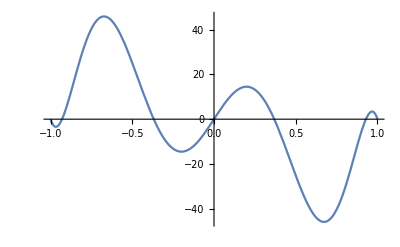

45.835

0.+113.938 x-1270.26 x^3+3843.64 x^5-4416.09 x^7+1730.58 x^9

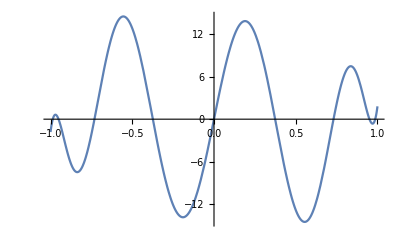

14.5038

```mathematica
(*Some tests and demos for the above*)
poly=8.1634015068251439828372895135544240474700927734375`30. x-93.53523368853274178036372177302837371826171875`30. x^3+301.21804475280686119731399230659008026123046875`30. x^5-363.1742884165829536868841387331485748291015625`30. x^7+147.482519204062327844440005719661712646484375`30. x^9
singularValues={0.99507773624,0.936608339348,0.350378108138067994,0.09909742093286229}
%//fitOddPoly
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
optPoly1=fitOptimizedPoly[%%%%,1,100]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
(*fitOptimizedPoly[%%%%%%%,2,10000]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs*)
```

```mathematica
(*Computes the pair of polynomials that correspond to the given real part, see more in https://arxiv.org/abs/1806.01838 *)
getPolyPairs[poly_,precision_]:=Module[{polyTry,K,roots,Qp,Zp,SRp,LRp,Ip,Wp,genRoots,zeroRoots,smallRealRoots,largeRealRoots,imgRoots,parityTrick,Bp,Cp},
polyTry=SetPrecision[poly,precision];
degree = (CoefficientList[polyTry,x]//Length)-1;
(K=Sqrt[-Coefficient[(1-polyTry^2//Expand),x^(2 degree)]])//Precision;
roots=x/.NSolve[(1-polyTry^2//Expand)==0,x,WorkingPrecision->precision];
(*p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]*)
(genRoots=Select[roots,(Re[#]>0&& Im[#]>0)&]);
zeroRoots=(Select[roots,(#==0)&]);
smallRealRoots=(Select[roots,(#!=0&&Re[#]>-1&&Re[#]<1&& Im[#]==0)&]);
(smallRealRoots=Table[smallRealRoots[[4i-3]],{i,1,(smallRealRoots//Length)/4}]);
(largeRealRoots=Select[roots,(Re[#]≥1&& Im[#]==0)&]);
(imgRoots=Select[roots,(Re[#]==0&& Im[#]>0)&]);
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@genRoots) ;
Zp=x^((zeroRoots//Length)/2);
SRp=(x^2-#^2)&/@smallRealRoots;
LRp=(Sqrt[#^2-1]x+I # Sqrt[1-x^2])&/@largeRealRoots;
Ip=(Sqrt[Abs[#]^2+1]x-I Abs[#]Sqrt[1-x^2])&/@imgRoots;
Wp=K*(Times@@Qp)*Zp*(Times@@SRp)*(Times@@LRp)*(Times@@Ip)//Expand//Simplify;
parityTrick=SetPrecision[Wp/.{Sqrt[1-x^2]->-I},precision];
Bp=SetPrecision[(parityTrick+(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
Cp=SetPrecision[(parityTrick-(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
{Bp,Cp}
]
```

True

8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

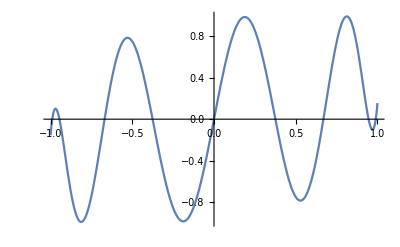

True

```mathematica
(*Some tests and demos for the above*)
{Bp,Cp}=getPolyPairs[ChebyshevT[5,x] ,110];
Bp^2+(1-x^2)Cp^2+ChebyshevT[5,x]^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
poly=8.163401506825144 x-93.53523368853274 x^3+301.21804475280686 x^5-363.17428841658295 x^7+147.48251920406233 x^9
Plot[%,{x,-1,1}]
{Bp,Cp}=getPolyPairs[poly,30];
poly=SetPrecision[poly,30];
Bp^2+(1-x^2)Cp^2+poly^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
```

```mathematica
(*Computes the sequence of angles for a given polynomial, see more in https://arxiv.org/abs/1806.01838 *)
getAngles[poly_,precision_Integer:10]:=Module[{tmpPoly,agreement,tmpprecision,Bp,Cp,Mat,carved,phs,phaseGates,W,NewMat},
agreement=1;
tmpprecision=MachinePrecision;
phs={};
While[ ((agreement//Accuracy) <precision) ||(agreement>10^-precision),
tmpPoly=SetPrecision[poly,tmpprecision];
{Bp,Cp}=getPolyPairs[tmpPoly,tmpprecision];
(Mat={{tmpPoly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,tmpPoly-I Bp}})//MatrixForm;
carved=NestList[carveLastAngle[#[[1]]]&,{Mat,{}},(tmpPoly//CoefficientList[#,x]&//Length)-1];
phs=Join[{(carved//Last)[[1]][[1]][[1]]},(#[[2]]&/@ carved)//Reverse//Most];
NewMat=getWMatrix[phs];
agreement=(NewMat[[1,1]]-tmpPoly-I Bp)//Expand//CoefficientList[#,x]&//Abs//Total;
Print[tmpprecision];
tmpprecision=2tmpprecision];
phs//Arg
];
carveLastAngle[Mat_]:=Module[{phase,outMat},
phase=(Coefficient[Mat[[1,1]],x,Exponent[Mat[[1,1]],x]]/(Coefficient[Mat[[1,2]]/.{Sqrt[1-x^2]->-I},x,(Exponent[Mat[[1,1]],x]-1)]))//Sqrt;
outMat=Mat.{{Conjugate[phase],0},{0,phase}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand;
outMat=outMat/.x^b_/;b≥Exponent[Mat[[1,1]],x]+1->0;
outMat=outMat/.Sqrt[1-x^2]x^b_/;b≥Exponent[Mat[[1,1]],x]->0;
{outMat, phase}
];
getWMatrix[phs_]:=Module[{phaseGates,W},
phaseGates=Table[{{phs[[i]],0},{0,Conjugate[phs[[i]]]}},{i,1,Length[phs]}];
(W={{x,I Sqrt[1-x^2]},{I Sqrt[1-x^2],x}})//MatrixForm;
(Dot@@((phaseGates//Most).W)).(phaseGates//Last)//Expand
];
WAnglesToRAngles[angles_]:=Module[{tmpAngles=angles},
tmpAngles[[1]]+=Last[angles]+((Mod[(Length[angles]),4])-1)Pi/2;
Mod[#,2 Pi]&/@Drop[tmpAngles,-1]-Pi/2];
getRMatrix[angles_]:=Module[{phaseGates,R},
phaseGates=Table[{{Exp[I angles[[i]]],0},{0,Exp[-I angles[[i]]]}},{i,1,Length[angles]}];
(R={{x, Sqrt[1-x^2]},{ Sqrt[1-x^2],-x}})//MatrixForm;
(Dot@@(phaseGates.R))//Expand
];
```

```mathematica
(*Some tests and demos for the above*)
angles=getAngles[ChebyshevT[10,x],20]//Chop
(getWMatrix[Exp[I%]])[[1,1]]-ChebyshevT[10,x]//Chop
(getRMatrix[%%//WAnglesToRAngles])[[1,1]]-ChebyshevT[10,x]//Expand//Chop
tmpPoly=poly/findPolyMaxAbs[poly]//Expand
angles=getAngles[%,20]
((getWMatrix[Exp[I%]//Reverse])[[1,1]]-%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
((getRMatrix[%%//WAnglesToRAngles])[[1,1]]-%%%)//CoefficientList[#,x]&//Re//Abs//Total//Chop
(*This is what we need to feed to the QSVT circuit*)
%%%//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.785398163397448309615660845819875721049292349843776,0,0,0,0,0,0,0,0,0,0.785398163397448309615660845819875721049292349843776455243736148}

0

0

8.27720505405564551123137 x-94.8391805023565269774823 x^3+305.417235733924878686473 x^5-368.237192923995131082338 x^7+149.538529045778466957024 x^9

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{-0.408901635471894571772110507561051468532631544752781,0.3584552943894671048461378497305384989146988780925645,0.13603714837731554333554206592563397208622491414361709,0.0886809496145304613134064710023385996384743201663036807,-0.2528935548135681432431437582642864394177341833368914951,-0.252893554813568143243143758264286439417734183336891495115,0.08868094961453046131340647100233859963847432016630368068608,0.13603714837731554333554206592563397208622491414361708991167,0.358455294389467104846137849730538498914698878092564541323801,1.16189469132300204745921118407869997356595315493477190490618146}

0

0

{-1.21234,-1.43476,-1.48212,4.4595,4.4595,-1.48212,-1.43476,-1.21234,0.752993}

```mathematica
Clear[anglesForCircuit];
anglesForCircuit[vqe_Association,verbose_Symbol:False]:=Module[{
U=vqe["U"],
blockEncoding,
SVs,
interPolys, interPolysMaxAbs,
objectiveFunction, optimumDeg,
interPoly,
subnormalisation,
print=If[verbose,Print,Identity]
},
blockEncoding=U[[-Length[U]/2;;,-Length[U]/2;;]];
blockEncoding//MatrixForm//print;
If[verbose&&False,MatPlot[U,Length[blockEncoding]]//print,False];
blockEncoding//Inverse//MatrixForm//print;
If[verbose&&False,MatInvPlot[blockEncoding]//print,False];
blockEncoding.Inverse[blockEncoding]//MatrixForm//Chop//print;
SVs=SingularValueList[blockEncoding];
SVs=DeleteDuplicatesBy[SVs,Round[500*#]&];
print[SVs];
print[DeleteDuplicates[SVs]];
interPolys=Table[fitOptimizedPoly[SVs,i,100^i],{i,0,1}];
interPolysMaxAbs=findPolyMaxAbs/@interPolys;
For[i=1,i≤Length[interPolys],i++,Plot[interPolys[[i]],{ x,-1,1}]//print];
objectiveFunction=1/interPolysMaxAbs/(Length[CoefficientList[#,x]]&/@interPolys);
optimumDeg=(Position[objectiveFunction,Max[objectiveFunction]]//Flatten)[[1]];
print[optimumDeg];
interPoly=interPolys[[optimumDeg]];
subnormalisation=0.9999/findPolyMaxAbs[interPoly];
interPoly=subnormalisation*interPoly//Expand;
print[interPoly];
{subnormalisation,getAngles[interPoly,8]//WAnglesToRAngles//Reverse//SetPrecision[#,MachinePrecision]&}
];
Clear[MatInvPlot];
MatInvPlot[mat_]:=
BarChart3D[MyEcho[(Abs[#])^2&/@Inverse[mat]]//Transpose,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"FaceGrids"->None,"Canvas"->False]⟦1⟧//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&;
```

(-0.0128184-0.0935834 ⅈ | -0.0741066+0.0481372 ⅈ | 0.091358-0.0165472 ⅈ | 0.0706429-0.0625706 ⅈ | -0.0125076+0.0395785 ⅈ | 0.00642896-0.00479117 ⅈ | -0.0089574+0.0245279 ⅈ | -0.0538683+0.0195202 ⅈ | -0.0179756-0.014298 ⅈ | -0.00710892-0.00196633 ⅈ | -0.0100284+0.0055594 ⅈ | -0.00460345-0.0324333 ⅈ | -0.00603182+0.0701537 ⅈ | 0.100973-0.0470236 ⅈ | -0.132605-0.0237257 ⅈ | -0.0502172+0.0137324 ⅈ | 0.0636168+0.172937 ⅈ | 0.127525-0.159021 ⅈ | -0.213377+0.0965499 ⅈ | -0.114333+0.131229 ⅈ | 0.0806155-0.0331422 ⅈ | -0.0383492-0.0848214 ⅈ | -0.0174634+0.0814763 ⅈ | 0.0746578+0.0301548 ⅈ | -0.0900145+0.00726928 ⅈ | 0.0429306+0.0859602 ⅈ | 0.00222417-0.100952 ⅈ | -0.0525035-0.0653918 ⅈ | 0.0880799-0.132121 ⅈ | -0.218552-0.0222292 ⅈ | 0.200163+0.160526 ⅈ | 0.126971+0.017128 ⅈ | -0.0416266-0.0835392 ⅈ | -0.0541263+0.06852 ⅈ | 0.0802755-0.0444124 ⅈ | 0.0463147-0.0809336 ⅈ | 0.000822861+0.0410067 ⅈ | 0.00450087-0.00652009 ⅈ | -0.000619014+0.0257949 ⅈ | -0.0442427+0.0353261 ⅈ | -0.0213525-0.00769247 ⅈ | -0.00727673+0.000410104 ⅈ | -0.00762685+0.00837875 ⅈ | -0.0145773-0.0289013 ⅈ | 0.0165644+0.067576 ⅈ | 0.0796268-0.0759834 ⅈ | -0.131635+0.0197741 ⅈ | -0.0426575+0.0287526 ⅈ | -0.0318382+0.0857277 ⅈ | 0.0994029-0.0187851 ⅈ | -0.111603-0.0324764 ⅈ | -0.085459+0.0125664 ⅈ | 0.0410879+0.0135271 ⅈ | 0.0129217-0.0443542 ⅈ | -0.0328821+0.025078 ⅈ | 0.0184111+0.0354657 ⅈ | -0.0362799-0.0263144 ⅈ | -0.0115622+0.0462622 ⅈ | 0.0334236-0.0373388 ⅈ | 0.0013144-0.0415983 ⅈ | 0.0758501-0.0213764 ⅈ | -0.0752142-0.0789239 ⅈ | 0.023643+0.125123 ⅈ | 0.0423366+0.0474403 ⅈ
0.0567387-0.00780949 ⅈ | -0.0929076-0.0203131 ⅈ | -0.0997154-0.0619996 ⅈ | -0.0406202-0.080591 ⅈ | -0.0243169-0.0145823 ⅈ | 0.0233357-0.015853 ⅈ | 0.0236297+0.0545654 ⅈ | 0.0232229+0.0087748 ⅈ | 0.0136551-0.0115426 ⅈ | 0.00925239+0.00263725 ⅈ | -0.0361941+0.00343004 ⅈ | 0.00268634+0.0067304 ⅈ | -0.0369686+0.00477655 ⅈ | 0.106824+0.0737853 ⅈ | 0.0593803+0.0444734 ⅈ | 0.0117412+0.11973 ⅈ | -0.0968491+0.0398049 ⅈ | 0.234354-0.00225664 ⅈ | 0.204257+0.0690769 ⅈ | 0.141184+0.168323 ⅈ | 0.0268037+0.053433 ⅈ | 0.0414661-0.0680186 ⅈ | 0.0249442-0.115153 ⅈ | 0.0755993-0.0131129 ⅈ | -0.00720893-0.0542871 ⅈ | -0.0404555+0.0924414 ⅈ | -0.0599512+0.0933381 ⅈ | -0.0918182+0.0264337 ⅈ | 0.0797052+0.037674 ⅈ | -0.114603-0.221875 ⅈ | -0.0665731-0.164287 ⅈ | 0.0894402-0.214861 ⅈ | 0.050637-0.0252732 ⅈ | -0.0933958+0.0104004 ⅈ | -0.112966-0.0264643 ⅈ | -0.0635368-0.0625758 ⅈ | -0.0273782-0.00595093 ⅈ | 0.016824-0.022227 ⅈ | 0.0393934+0.0435941 ⅈ | 0.0245155+0.000861251 ⅈ | 0.00912729-0.0151274 ⅈ | 0.00949551-0.000460709 ⅈ | -0.0327931+0.0146696 ⅈ | 0.00464533+0.00544941 ⅈ | -0.0330916+0.0161751 ⅈ | 0.123351+0.0352458 ⅈ | 0.0696622+0.0228291 ⅈ | 0.0488962+0.108354 ⅈ | -0.0493582-0.0162553 ⅈ | 0.0890748+0.0747938 ⅈ | 0.054704+0.0919705 ⅈ | -0.00110812+0.109025 ⅈ | -0.00714263+0.0287947 ⅈ | 0.0375868-0.0122572 ⅈ | 0.0465723-0.0353586 ⅈ | 0.0327319+0.0194586 ⅈ | 0.0148051-0.022792 ⅈ | -0.045089+0.0217903 ⅈ | -0.0527279+0.0158355 ⅈ | -0.0431457-0.019672 ⅈ | 0.0178868+0.0399295 ⅈ | 0.0284138-0.120634 ⅈ | 0.0279319-0.0834212 ⅈ | 0.10307-0.0521285 ⅈ
-0.123568-0.0291888 ⅈ | 0.00971226-0.0394375 ⅈ | -0.0632897+0.0230985 ⅈ | 0.0600968-0.00353914 ⅈ | 0.00808755+0.0167602 ⅈ | -0.0544526-0.000998166 ⅈ | -0.0165403+0.0166474 ⅈ | 0.0144695+0.00031092 ⅈ | -0.0158087-0.0107989 ⅈ | 0.00313601-0.0402873 ⅈ | -0.0199018-0.0173649 ⅈ | 0.0049765+0.0177482 ⅈ | 0.142142+0.0375087 ⅈ | 0.050609+0.0134359 ⅈ | 0.0961971-0.0575737 ⅈ | -0.099859+0.0089759 ⅈ | 0.275732-0.0323017 ⅈ | 0.0240935+0.0336771 ⅈ | 0.105152-0.125472 ⅈ | -0.132975+0.073731 ⅈ | 0.038635-0.137319 ⅈ | 0.0810194-0.0299616 ⅈ | -0.0162707-0.103186 ⅈ | -0.0192997+0.0817094 ⅈ | -0.0407265+0.130869 ⅈ | -0.0419754+0.00605647 ⅈ | 0.0252812+0.0795065 ⅈ | 0.00292439-0.0732166 ⅈ | -0.201729-0.216054 ⅈ | -0.0397556-0.0735876 ⅈ | -0.208743-0.0120106 ⅈ | 0.166369+0.0867197 ⅈ | -0.124905+0.0117992 ⅈ | -0.00339474-0.0399898 ⅈ | -0.0519285+0.0416583 ⅈ | 0.0551323-0.0223392 ⅈ | 0.0128764+0.0131277 ⅈ | -0.0512856+0.0163052 ⅈ | -0.0102118+0.0208191 ⅈ | 0.0136424-0.00428996 ⅈ | -0.0182164-0.00510314 ⅈ | -0.00981938-0.0387032 ⅈ | -0.0241265-0.00995333 ⅈ | 0.0102772+0.0150374 ⅈ | 0.144925-0.00989195 ⅈ | 0.0516256-0.00344616 ⅈ | 0.0718163-0.0843467 ⅈ | -0.0906298+0.0400167 ⅈ | 0.114371+0.0768233 ⅈ | -0.00178754+0.0204724 ⅈ | 0.0801397-0.0133596 ⅈ | -0.0739277-0.0151266 ⅈ | 0.0588883-0.0392958 ⅈ | 0.0402135+0.0148565 ⅈ | 0.0271725-0.0441507 ⅈ | -0.0336497+0.0245732 ⅈ | -0.0575948+0.0361892 ⅈ | -0.0177787-0.0112656 ⅈ | -0.0161325+0.0381325 ⅈ | 0.0247352-0.0266572 ⅈ | -0.00630986-0.146561 ⅈ | 0.00876549-0.0405732 ⅈ | -0.0748149-0.0719056 ⅈ | 0.0347263+0.0863919 ⅈ
-0.0416058-0.00639329 ⅈ | -0.0200109-0.105791 ⅈ | 0.0560392+0.00292964 ⅈ | -0.0970471-0.00161499 ⅈ | -0.0230703-0.0388178 ⅈ | -0.0229115+0.0236864 ⅈ | 0.00834133-0.0086216 ⅈ | -0.00786091+0.0272366 ⅈ | 0.0244861-0.0244609 ⅈ | -0.00615297-0.0243713 ⅈ | 0.00991355+0.0127485 ⅈ | -0.0260104-0.016424 ⅈ | 0.112841+0.0436622 ⅈ | 0.02703+0.0993138 ⅈ | -0.0795496+0.00709354 ⅈ | 0.120909-0.0272594 ⅈ | 0.145765-0.0379456 ⅈ | 0.109742+0.185585 ⅈ | -0.117973+0.0511381 ⅈ | 0.186129-0.0914087 ⅈ | 0.0679241-0.0399607 ⅈ | 0.117785-0.0372033 ⅈ | -0.0132575+0.0762693 ⅈ | 0.00316645-0.135282 ⅈ | -0.0268469+0.0557178 ⅈ | -0.110525+0.0183442 ⅈ | 0.00627845-0.0652907 ⅈ | -0.00230364+0.110583 ⅈ | -0.129211-0.165676 ⅈ | 0.0689443-0.205264 ⅈ | 0.134313+0.0740946 ⅈ | -0.223702-0.0931811 ⅈ | -0.0409686+0.00718789 ⅈ | -0.052224-0.0926891 ⅈ | 0.0533822-0.0149995 ⅈ | -0.0913508+0.029213 ⅈ | -0.0338842-0.0290308 ⅈ | -0.0139469+0.029425 ⅈ | 0.00507821-0.010711 ⅈ | 0.0012649+0.0279831 ⅈ | 0.0151756-0.0306485 ⅈ | -0.0134752-0.0208644 ⅈ | 0.0133156+0.00879449 ⅈ | -0.0295465-0.00713869 ⅈ | 0.119446+0.00514442 ⅈ | 0.0567434+0.0844037 ⅈ | -0.0722155+0.0318249 ⅈ | 0.104545-0.0637952 ⅈ | 0.0671982+0.0327451 ⅈ | -0.0185324+0.105384 ⅈ | -0.0609795-0.0188012 ⅈ | 0.0996716+0.0256195 ⅈ | 0.0385044+0.00686017 ⅈ | 0.0564108+0.0239937 ⅈ | -0.0296159+0.0244727 ⅈ | 0.0448599-0.0499764 ⅈ | -0.0281052+0.0123388 ⅈ | -0.0475867-0.0287597 ⅈ | 0.0234413-0.0225866 ⅈ | -0.0365622+0.0409438 ⅈ | 0.00476678-0.104163 ⅈ | 0.0922456-0.0551266 ⅈ | 0.0267168+0.0712854 ⅈ | -0.054254-0.107334 ⅈ
-0.00707145+0.0410511 ⅈ | -0.0316061+0.056718 ⅈ | 0.0637369+0.0727734 ⅈ | -0.0155771-0.024375 ⅈ | -0.0293264-0.0798099 ⅈ | -0.0324899-0.127763 ⅈ | -0.0803538-0.0941167 ⅈ | 0.11501-0.0267963 ⅈ | -0.00447921-0.0217814 ⅈ | 0.0000662882-0.0283018 ⅈ | -0.0321837-0.0472484 ⅈ | 0.014368-0.0111216 ⅈ | 0.00466211+0.0157183 ⅈ | 0.012381+0.0174485 ⅈ | -0.00971805+0.0492494 ⅈ | -0.0292604+0.0317124 ⅈ | 0.0618039-0.0699727 ⅈ | 0.118099-0.0894717 ⅈ | 0.00397528-0.152077 ⅈ | 0.0474335+0.0941123 ⅈ | 0.0164341+0.148589 ⅈ | 0.00235958+0.221739 ⅈ | 0.0993391+0.230472 ⅈ | -0.19507+0.0210694 ⅈ | 0.109169+0.0424858 ⅈ | 0.150332+0.0825132 ⅈ | 0.210605-0.000589553 ⅈ | -0.051088+0.128293 ⅈ | 0.038143-0.0536715 ⅈ | 0.0585631-0.0777113 ⅈ | 0.0567392-0.0927713 ⅈ | 0.0889258+0.0515833 ⅈ | 0.0063775+0.0406641 ⅈ | -0.0116278+0.0630964 ⅈ | 0.0826998+0.0479396 ⅈ | -0.0222978-0.0178842 ⅈ | -0.052718-0.0654203 ⅈ | -0.0708611-0.109305 ⅈ | -0.105011-0.0626568 ⅈ | 0.09917-0.0614941 ⅈ | -0.0110886-0.0189701 ⅈ | -0.0088982-0.0265125 ⅈ | -0.0450837-0.0340369 ⅈ | 0.00992793-0.014959 ⅈ | 0.00934024+0.0132368 ⅈ | 0.0171132+0.0124126 ⅈ | 0.00649572+0.0491759 ⅈ | -0.0173488+0.0389477 ⅈ | 0.0458845-0.00642919 ⅈ | 0.0734002+0.00439083 ⅈ | 0.0505857-0.0560465 ⅈ | -0.0124961+0.0507889 ⅈ | -0.041766+0.0613193 ⅈ | -0.0706833+0.0843526 ⅈ | -0.0369427+0.118947 ⅈ | -0.0803381-0.0550218 ⅈ | 0.0274409+0.0512537 ⅈ | 0.0300386+0.0796298 ⅈ | 0.0795839+0.0677566 ⅈ | -0.0606694+0.0318736 ⅈ | 0.0317031-0.00792126 ⅈ | 0.0471606-0.0103926 ⅈ | 0.0513341-0.0166586 ⅈ | 0.0168731+0.0481492 ⅈ
-0.0362228+0.059163 ⅈ | 0.00210853+0.0571911 ⅈ | -0.00990034-0.0455532 ⅈ | 0.00304258+0.0766567 ⅈ | 0.0132666-0.115659 ⅈ | -0.0331405-0.10086 ⅈ | 0.106908+0.126198 ⅈ | -0.0274476-0.0305971 ⅈ | 0.0125655-0.0334985 ⅈ | -0.00739807-0.0332556 ⅈ | 0.0308674+0.0232537 ⅈ | 0.0107983-0.0290341 ⅈ | -0.0119009+0.0166823 ⅈ | -0.00266111+0.0261834 ⅈ | -0.0424641-0.0326809 ⅈ | -0.0315785-0.0112827 ⅈ | 0.124125-0.059171 ⅈ | 0.0700591-0.0935976 ⅈ | -0.0617812+0.136596 ⅈ | 0.0306065-0.0944954 ⅈ | -0.0802691+0.192951 ⅈ | 0.012555+0.195408 ⅈ | -0.150111-0.250917 ⅈ | -0.00240571+0.0741005 ⅈ | 0.108941+0.129065 ⅈ | 0.14482+0.0590868 ⅈ | -0.216362+0.0182185 ⅈ | 0.0695404+0.03981 ⅈ | 0.080332-0.0342683 ⅈ | 0.0580486-0.0636271 ⅈ | -0.0261892+0.142242 ⅈ | 0.0152338+0.00154803 ⅈ | -0.0151751+0.0668467 ⅈ | 0.0200801+0.0528654 ⅈ | -0.023689-0.039505 ⅈ | 0.0271172+0.0707901 ⅈ | -0.0241991-0.112461 ⅈ | -0.0629527-0.0839167 ⅈ | 0.140023+0.0842788 ⅈ | -0.0353788-0.0199501 ⅈ | 0.00115626-0.0353339 ⅈ | -0.0174535-0.0287863 ⅈ | 0.036255+0.0119938 ⅈ | 0.000915525-0.0305957 ⅈ | -0.00585811+0.019383 ⅈ | 0.00579868+0.0253511 ⅈ | -0.0500946-0.0171465 ⅈ | -0.0331307-0.000563375 ⅈ | 0.0658917+0.0177589 ⅈ | 0.0566221-0.0126707 ⅈ | -0.0673804+0.031552 ⅈ | 0.0420391-0.0257436 ⅈ | -0.0925403+0.0468292 ⅈ | -0.0583407+0.0777173 ⅈ | 0.0244022-0.143043 ⅈ | -0.024825+0.0271578 ⅈ | -0.000590872+0.0838186 ⅈ | 0.035522+0.0690192 ⅈ | -0.0874444-0.0629691 ⅈ | 0.0133654+0.0374537 ⅈ | 0.0413445+0.0130111 ⅈ | 0.0424206-0.00524916 ⅈ | -0.0557855+0.0451688 ⅈ | 0.00524315+0.00550073 ⅈ
0.0305335+0.0105673 ⅈ | 0.0446191-0.0293659 ⅈ | 0.011068+0.0115013 ⅈ | -0.0582289-0.0167573 ⅈ | 0.0895776+0.0379865 ⅈ | -0.131891+0.0366449 ⅈ | 0.0193144+0.0436794 ⅈ | 0.121352+0.0835298 ⅈ | 0.0143987-0.0210431 ⅈ | -0.0414501+0.0266458 ⅈ | 0.0101772-0.00284674 ⅈ | 0.0516949+0.016787 ⅈ | -0.0656477+0.0155798 ⅈ | 0.0615983-0.004998 ⅈ | -0.0281816-0.0133375 ⅈ | -0.0455997-0.049367 ⅈ | -0.0321513+0.0468182 ⅈ | -0.097143-0.0608834 ⅈ | -0.0312535+0.00736554 ⅈ | 0.0197183+0.123228 ⅈ | -0.156279-0.05556 ⅈ | 0.265877-0.0288028 ⅈ | -0.0349714-0.0705207 ⅈ | -0.207912-0.201577 ⅈ | -0.0676107+0.0777429 ⅈ | 0.0570608-0.197085 ⅈ | -0.0483339+0.00246353 ⅈ | -0.204344+0.0896644 ⅈ | 0.0556908+0.0927398 ⅈ | -0.0994271-0.0913643 ⅈ | -0.00948427+0.049925 ⅈ | -0.00854658+0.145507 ⅈ | 0.031926+0.000224525 ⅈ | 0.0324679-0.0416137 ⅈ | 0.0140013+0.00726155 ⅈ | -0.0598096+0.00274967 ⅈ | 0.0958742+0.00719676 ⅈ | -0.111853+0.076057 ⅈ | 0.0319077+0.0347706 ⅈ | 0.140035+0.0397674 ⅈ | 0.00681554-0.0242557 ⅈ | -0.0303628+0.0380644 ⅈ | 0.00862496-0.00588671 ⅈ | 0.0537029-0.000653163 ⅈ | -0.0565161+0.0353671 ⅈ | 0.0560759-0.0241801 ⅈ | -0.0306016-0.00356224 ⅈ | -0.0583123-0.0317726 ⅈ | -0.0272323+0.00727169 ⅈ | -0.0169689-0.0543075 ⅈ | -0.0141593-0.00731132 ⅈ | -0.0323419+0.0528188 ⅈ | -0.0409803-0.0713886 ⅈ | 0.109527+0.0749616 ⅈ | 0.00957913-0.0378728 ⅈ | -0.0133135-0.1431 ⅈ | -0.0505815+0.00748411 ⅈ | 0.0851257-0.0558788 ⅈ | -0.019016-0.0146725 ⅈ | -0.105975-0.0321564 ⅈ | -0.00894022+0.0529368 ⅈ | -0.00799142-0.0665354 ⅈ | -0.0196901+0.0157593 ⅈ | -0.0501885+0.0520944 ⅈ
-0.0464334-0.0472994 ⅈ | 0.0255902-0.031394 ⅈ | 0.0140904+0.000116159 ⅈ | -0.00613211+0.0394144 ⅈ | 0.0778238+0.129317 ⅈ | -0.0115964-0.0742059 ⅈ | 0.076736-0.0467967 ⅈ | 0.00271037-0.125233 ⅈ | 0.038826+0.039835 ⅈ | -0.0328141-0.00723974 ⅈ | 0.000597386-0.0254007 ⅈ | -0.00734714-0.0349442 ⅈ | -0.0173322-0.0627916 ⅈ | 0.03237+0.0588789 ⅈ | -0.0318287+0.0459122 ⅈ | -0.00116114+0.0444988 ⅈ | -0.0362837+0.129537 ⅈ | 0.0134555+0.000665389 ⅈ | 0.031643+0.0359947 ⅈ | 0.0955594-0.0571633 ⅈ | -0.103974-0.276953 ⅈ | 0.0377611+0.14347 ⅈ | -0.138834+0.0842426 ⅈ | -0.044122+0.226375 ⅈ | -0.229729-0.00801261 ⅈ | 0.0986548+0.000201198 ⅈ | 0.0189228+0.107257 ⅈ | 0.14173+0.101637 ⅈ | -0.0701796+0.128026 ⅈ | 0.0547176-0.0828672 ⅈ | 0.0963076+0.0194634 ⅈ | 0.0938174-0.064271 ⅈ | -0.0584381-0.0295733 ⅈ | 0.0140141-0.0374876 ⅈ | 0.0132259-0.00435224 ⅈ | 0.00673858+0.0388347 ⅈ | 0.113787+0.0964065 ⅈ | -0.034348-0.065788 ⅈ | 0.0570119-0.0680977 ⅈ | -0.0371114-0.118081 ⅈ | 0.0489541+0.0249948 ⅈ | -0.0330072+0.00361215 ⅈ | -0.00748257-0.023965 ⅈ | -0.0179404-0.0303829 ⅈ | -0.0361031-0.0532878 ⅈ | 0.0489403+0.0448646 ⅈ | -0.0152571+0.0530523 ⅈ | 0.0130013+0.04202 ⅈ | -0.0554901+0.0371212 ⅈ | 0.00485765+0.00459398 ⅈ | 0.000310418+0.0237829 ⅈ | 0.054475+0.00929523 ⅈ | 0.0501985-0.137966 ⅈ | -0.0320739+0.0662735 ⅈ | -0.0795293-0.0130551 ⅈ | -0.089702+0.0710968 ⅈ | -0.0840166-0.0771723 ⅈ | 0.0371258+0.0319196 ⅈ | -0.0274868+0.0465415 ⅈ | 0.0206229+0.0840626 ⅈ | -0.0677801+0.0256104 ⅈ | 0.0473752-0.0135775 ⅈ | 0.0300235+0.0384233 ⅈ | 0.0561125+0.00605349 ⅈ
-0.0716334+0.105527 ⅈ | 0.119164+0.0599447 ⅈ | -0.0620729-0.106029 ⅈ | -0.116809+0.0169568 ⅈ | -0.0433481-0.0635859 ⅈ | 0.042561+0.0986552 ⅈ | 0.0271237-0.167161 ⅈ | 0.0725693-0.0743408 ⅈ | 0.151137+0.0139872 ⅈ | -0.0458194-0.0785692 ⅈ | 0.0511035+0.094756 ⅈ | 0.0866942+0.156945 ⅈ | -0.0479731-0.0448278 ⅈ | -0.0576269+0.114701 ⅈ | 0.140586-0.0586749 ⅈ | 0.00716682-0.030507 ⅈ | 0.0757733+0.00515741 ⅈ | -0.0193358-0.102461 ⅈ | -0.0481006+0.101389 ⅈ | 0.0318129+0.0482449 ⅈ | 0.0442361+0.0312077 ⅈ | -0.0253818-0.0907999 ⅈ | -0.0421102+0.120911 ⅈ | -0.026394+0.0443123 ⅈ | -0.116065-0.024268 ⅈ | 0.031269+0.0799141 ⅈ | -0.0172978-0.0949616 ⅈ | -0.0485709-0.123599 ⅈ | 0.0517148-0.0121115 ⅈ | -0.0252906-0.0669468 ⅈ | -0.0221372+0.0703147 ⅈ | 0.0344133+0.0225468 ⅈ | -0.0336419+0.121456 ⅈ | 0.13052+0.0183836 ⅈ | -0.0916709-0.0795953 ⅈ | -0.103969+0.0528533 ⅈ | -0.0607064-0.0457948 ⅈ | 0.0710725+0.0788702 ⅈ | -0.0275339-0.165056 ⅈ | 0.0443914-0.0925608 ⅈ | 0.145898-0.034757 ⅈ | -0.0677633-0.0590373 ⅈ | 0.0778341+0.0725158 ⅈ | 0.130837+0.119459 ⅈ | -0.0590969-0.0267723 ⅈ | -0.0176269+0.125609 ⅈ | 0.113017-0.0994307 ⅈ | -0.00294999-0.0308246 ⅈ | 0.0269002+0.0264023 ⅈ | 0.0257832-0.0448669 ⅈ | -0.0508592+0.0226957 ⅈ | -0.00357967+0.0284558 ⅈ | 0.00660289+0.0260431 ⅈ | 0.0197399-0.0424223 ⅈ | -0.0549022+0.0319886 ⅈ | -0.0242531+0.00818535 ⅈ | -0.0359207-0.0466117 ⅈ | -0.0140068+0.0402189 ⅈ | 0.0241307-0.0413818 ⅈ | 0.0215849-0.0622717 ⅈ | 0.0234047+0.0121267 ⅈ | 0.012075-0.0334008 ⅈ | -0.0310414+0.0193617 ⅈ | 0.00569543+0.0196076 ⅈ
-0.0730578-0.0428141 ⅈ | 0.0217595+0.117884 ⅈ | 0.058672+0.157574 ⅈ | -0.0723792+0.0896459 ⅈ | 0.0310829-0.00873118 ⅈ | -0.0997583+0.131929 ⅈ | -0.0715331-0.0313792 ⅈ | -0.149683+0.00565276 ⅈ | -0.0204279+0.0925982 ⅈ | -0.00479233-0.11888 ⅈ | 0.152759-0.126775 ⅈ | 0.0866794-0.0705735 ⅈ | 0.0145767-0.0371984 ⅈ | -0.14299-0.00421344 ⅈ | -0.0668145+0.0316123 ⅈ | -0.0835574-0.102332 ⅈ | 0.00488801+0.0471093 ⅈ | 0.0799627-0.0718907 ⅈ | 0.0533682-0.0756988 ⅈ | 0.100111+0.0129349 ⅈ | -0.0101905+0.0190633 ⅈ | 0.0879677-0.0870397 ⅈ | 0.046005-0.0113717 ⅈ | 0.112828+0.0107348 ⅈ | 0.0208371-0.0693657 ⅈ | -0.0253065+0.100446 ⅈ | -0.124278+0.0859749 ⅈ | -0.0896182+0.0391505 ⅈ | 0.0135326+0.0323714 ⅈ | 0.0443276-0.0539448 ⅈ | 0.0204974-0.0649141 ⅈ | 0.0657705-0.00192206 ⅈ | -0.0819395-0.0169457 ⅈ | 0.0576894+0.103455 ⅈ | 0.104806+0.12892 ⅈ | -0.0393679+0.106827 ⅈ | 0.0263304-0.0180134 ⅈ | -0.0516091+0.155073 ⅈ | -0.0768921-0.00672495 ⅈ | -0.138319+0.0526803 ⅈ | 0.010195+0.0931426 ⅈ | -0.0421229-0.109759 ⅈ | 0.102851-0.167029 ⅈ | 0.0587917-0.0935017 ⅈ | 0.00186748-0.039434 ⅈ | -0.135177+0.0413261 ⅈ | -0.0525324+0.0507435 ⅈ | -0.110611-0.0693328 ⅈ | -0.0133632+0.019337 ⅈ | 0.053349-0.00129099 ⅈ | 0.0445527-0.0113107 ⅈ | 0.0335646+0.0371899 ⅈ | -0.00999486+0.00389718 ⅈ | 0.0612565-0.00441797 ⅈ | 0.0210135+0.0105626 ⅈ | 0.0390687+0.0404652 ⅈ | 0.0302449-0.0194236 ⅈ | -0.041962+0.0296977 ⅈ | -0.0746012-0.00770372 ⅈ | -0.0464211-0.014168 ⅈ | -0.00534733+0.0165714 ⅈ | 0.0341228-0.00602801 ⅈ | 0.02868-0.0178551 ⅈ | 0.0254145+0.0205047 ⅈ
0.07526+0.187139 ⅈ | -0.0634354+0.0869105 ⅈ | 0.103499+0.0930005 ⅈ | -0.0513245-0.101296 ⅈ | -0.0347974+0.109573 ⅈ | 0.081304+0.0547432 ⅈ | 0.0914789+0.0596479 ⅈ | -0.0411936-0.0951934 ⅈ | 0.0617577-0.120856 ⅈ | 0.0353033+0.104452 ⅈ | 0.0134508-0.0293846 ⅈ | -0.00112644+0.0278791 ⅈ | -0.15457+0.0779713 ⅈ | -0.0910447+0.0313045 ⅈ | -0.0564512+0.137404 ⅈ | 0.0966308-0.0835422 ⅈ | 0.0711911-0.1287 ⅈ | 0.0555505-0.0314574 ⅈ | -0.0136345-0.108552 ⅈ | -0.0269611+0.0897136 ⅈ | 0.0465493-0.105136 ⅈ | -0.0134883-0.0517695 ⅈ | -0.0512252-0.0802761 ⅈ | 0.00579669+0.087584 ⅈ | -0.0642908+0.106227 ⅈ | -0.0216633-0.0629824 ⅈ | -0.00299485+0.0419158 ⅈ | 0.00505401-0.0404589 ⅈ | 0.0321079-0.0983131 ⅈ | 0.0434712-0.0315253 ⅈ | -0.0199148-0.0768703 ⅈ | -0.0109286+0.0655553 ⅈ | 0.129694+0.151342 ⅈ | -0.0318623+0.101435 ⅈ | 0.126322+0.0542845 ⅈ | -0.0801116-0.0785678 ⅈ | 0.00211865+0.113581 ⅈ | 0.0934349+0.0255011 ⅈ | 0.104512+0.0268707 ⅈ | -0.0686966-0.0760627 ⅈ | 0.0195448-0.132678 ⅈ | 0.0661143+0.086594 ⅈ | 0.00328735-0.0317634 ⅈ | 0.00777202+0.0264525 ⅈ | -0.119998+0.12192 ⅈ | -0.0753102+0.0581265 ⅈ | -0.00933889+0.146487 ⅈ | 0.0640007-0.108791 ⅈ | 0.0683793-0.0255383 ⅈ | 0.0310951+0.00607179 ⅈ | 0.0298985-0.0453228 ⅈ | -0.0391214+0.0251177 ⅈ | 0.0514838-0.0246089 ⅈ | 0.0116253-0.0238697 ⅈ | 0.00660064-0.0467968 ⅈ | -0.026085+0.0348883 ⅈ | -0.0585242+0.0192938 ⅈ | 0.0121628-0.0307355 ⅈ | -0.0146585+0.0148347 ⅈ | 0.0149645-0.0136208 ⅈ | 0.0438374-0.0266982 ⅈ | 0.0265634+0.00214722 ⅈ | 0.0173046-0.0354065 ⅈ | -0.0252797+0.0211854 ⅈ
-0.0265173+0.094748 ⅈ | -0.103674+0.138974 ⅈ | -0.0503842-0.0923928 ⅈ | 0.107882+0.148535 ⅈ | 0.00386902+0.176145 ⅈ | -0.0520311-0.00280933 ⅈ | -0.0281834-0.0610144 ⅈ | 0.0515444+0.0676625 ⅈ | -0.0569106+0.00592543 ⅈ | 0.135631+0.0272719 ⅈ | -0.0214648+0.0349493 ⅈ | 0.054862-0.0727621 ⅈ | -0.158052+0.0210139 ⅈ | -0.109135-0.0563915 ⅈ | 0.0738576-0.071474 ⅈ | -0.0952879+0.132167 ⅈ | 0.075629-0.0644189 ⅈ | 0.113866-0.00611586 ⅈ | -0.0214125+0.0768961 ⅈ | 0.0176345-0.12999 ⅈ | 0.042034-0.116098 ⅈ | 0.0691353-0.00437737 ⅈ | 0.00445358+0.0643217 ⅈ | -0.0205682-0.0907237 ⅈ | 0.0248318+0.0221228 ⅈ | -0.112263-0.0263868 ⅈ | 0.0188528-0.0394246 ⅈ | -0.0415698+0.0723801 ⅈ | 0.0513051-0.0480129 ⅈ | 0.0794375-0.0222628 ⅈ | -0.00690518+0.0571356 ⅈ | -0.00298872-0.0961148 ⅈ | 0.0051757+0.0970828 ⅈ | -0.053044+0.162908 ⅈ | -0.0764126-0.0705315 ⅈ | 0.148007+0.104879 ⅈ | 0.0593883+0.163653 ⅈ | -0.0495924+0.0138432 ⅈ | -0.0456976-0.0481889 ⅈ | 0.069669+0.0470158 ⅈ | -0.0513944+0.0235641 ⅈ | 0.135589-0.0174127 ⅈ | -0.009027+0.0395095 ⅈ | 0.0283166-0.085477 ⅈ | -0.141289+0.0697084 ⅈ | -0.120008-0.0182327 ⅈ | 0.046505-0.0902853 ⅈ | -0.0473492+0.153881 ⅈ | 0.0493036+0.000126889 ⅈ | 0.0448993+0.0344481 ⅈ | -0.0328925+0.0220767 ⅈ | 0.0486058-0.0433113 ⅈ | 0.0533198-0.0301986 ⅈ | 0.0274755+0.0206653 ⅈ | -0.0190828+0.0256854 ⅈ | 0.0215299-0.0408399 ⅈ | 0.00222028+0.016355 ⅈ | -0.0338038-0.0461835 ⅈ | 0.0198325-0.00877693 ⅈ | -0.0390337+0.0138679 ⅈ | 0.0348385-0.00153962 ⅈ | 0.0371322+0.0172481 ⅈ | -0.0210453+0.0193101 ⅈ | 0.0298971-0.0371979 ⅈ
0.0304282+0.0319098 ⅈ | 0.0141442+0.0444032 ⅈ | 0.160235+0.0503078 ⅈ | 0.0272568+0.0192534 ⅈ | -0.0353895-0.0799928 ⅈ | -0.0433432-0.140211 ⅈ | -0.0783528-0.052215 ⅈ | 0.135601-0.0119039 ⅈ | 0.116382-0.0440363 ⅈ | 0.184548-0.0291856 ⅈ | 0.134706-0.191339 ⅈ | 0.0167893+0.119466 ⅈ | 0.0434208-0.0206795 ⅈ | 0.0834265-0.0466475 ⅈ | 0.0116252+0.0326325 ⅈ | 0.0219109+0.131145 ⅈ | -0.0343534+0.00105335 ⅈ | -0.0421259+0.00229757 ⅈ | -0.0882064+0.00178912 ⅈ | -0.0292762-0.0459014 ⅈ | 0.0052484+0.00127665 ⅈ | 0.0071614+0.0128438 ⅈ | 0.00597832-0.0368725 ⅈ | -0.0151939-0.0167684 ⅈ | -0.109392-0.00288404 ⅈ | -0.160879-0.0332258 ⅈ | -0.171943+0.0947743 ⅈ | 0.0219549-0.114211 ⅈ | -0.040473+0.0245665 ⅈ | -0.0737045+0.0427468 ⅈ | -0.0216559+0.0105431 ⅈ | -0.026256-0.0960534 ⅈ | 0.0385844+0.0202353 ⅈ | 0.0272974+0.037085 ⅈ | 0.165913-0.00363978 ⅈ | 0.0316089+0.00939249 ⅈ | -0.0584513-0.0636719 ⅈ | -0.084961-0.11752 ⅈ | -0.0898721-0.0240689 ⅈ | 0.123159-0.0540732 ⅈ | 0.0949958-0.0780656 ⅈ | 0.163503-0.0857459 ⅈ | 0.0655128-0.221748 ⅈ | 0.0535378+0.106509 ⅈ | 0.0340964-0.0331037 ⅈ | 0.0633217-0.0700762 ⅈ | 0.0212129+0.0268647 ⅈ | 0.0620295+0.11582 ⅈ | -0.0132905-0.0106915 ⅈ | -0.0166222-0.0127312 ⅈ | -0.0338294-0.0277967 ⅈ | 0.00377952-0.0267536 ⅈ | 0.00156646+0.00217534 ⅈ | -0.00144603+0.0071534 ⅈ | 0.0141554-0.0119705 ⅈ | -0.000315296-0.0112256 ⅈ | -0.0403077-0.0363968 ⅈ | -0.0499232-0.0644537 ⅈ | -0.0954101-0.0197718 ⅈ | 0.0451414-0.0359684 ⅈ | -0.023187-0.00380277 ⅈ | -0.0415828-0.00767563 ⅈ | -0.0115669-0.00301551 ⅈ | 0.0211061-0.044685 ⅈ
0.0139579+0.0836294 ⅈ | 0.0615476+0.0524542 ⅈ | -0.0658349+0.0277783 ⅈ | 0.020794+0.119034 ⅈ | -0.00354959-0.116323 ⅈ | -0.0402127-0.0908011 ⅈ | 0.0974808+0.137794 ⅈ | -0.0677644-0.0098169 ⅈ | 0.187387+0.0159909 ⅈ | 0.150653-0.0685047 ⅈ | -0.140884+0.140062 ⅈ | 0.118052-0.0595243 ⅈ | 0.0445949-0.00627393 ⅈ | 0.041008-0.00484854 ⅈ | -0.123109+0.0643268 ⅈ | -0.0776381-0.0356877 ⅈ | -0.0392077-0.0305617 ⅈ | -0.0526548-0.00682656 ⅈ | 0.0622422-0.0535771 ⅈ | -0.00765553-0.0401889 ⅈ | 0.0145274+0.00367783 ⅈ | 0.00801481-0.00746007 ⅈ | 0.0103498-0.0083656 ⅈ | 0.0389524-0.0106737 ⅈ | -0.143181-0.0753297 ⅈ | -0.144186+0.00158278 ⅈ | 0.17115-0.0701109 ⅈ | -0.0990555+0.00679784 ⅈ | -0.0534481+0.00958798 ⅈ | -0.043762+0.0189871 ⅈ | 0.0881319-0.0696499 ⅈ | 0.0356287+0.0297488 ⅈ | 0.0395419+0.073861 ⅈ | 0.0742175+0.0296132 ⅈ | -0.0528293+0.0468446 ⅈ | 0.0571495+0.104836 ⅈ | -0.0401501-0.107759 ⅈ | -0.0663878-0.0722619 ⅈ | 0.134871+0.0981185 ⅈ | -0.0665379+0.012265 ⅈ | 0.180464-0.044358 ⅈ | 0.119329-0.111819 ⅈ | -0.0875289+0.175706 ⅈ | 0.0916558-0.0930917 ⅈ | 0.0397561-0.0199912 ⅈ | 0.03685-0.0175214 ⅈ | -0.0948685+0.0991879 ⅈ | -0.0839706-0.00882503 ⅈ | -0.00491577-0.0241765 ⅈ | -0.0176463-0.0195693 ⅈ | 0.0407576-0.000106961 ⅈ | 0.0100861-0.0176214 ⅈ | 0.00428939+0.0060756 ⅈ | 0.00542937-0.000225276 ⅈ | 0.00660191+0.000187058 ⅈ | 0.0181295+0.00854925 ⅈ | -0.0296612-0.0746134 ⅈ | -0.054866-0.0459436 ⅈ | 0.0871504+0.0288134 ⅈ | -0.039536-0.0294104 ⅈ | -0.0232436-0.0136375 ⅈ | -0.022626-0.00696774 ⅈ | 0.0557054+0.00219063 ⅈ | 0.00382898+0.0227149 ⅈ
0.0671565+0.0906137 ⅈ | 0.0129753-0.132414 ⅈ | 0.000577193+0.0498601 ⅈ | -0.124383+0.0805373 ⅈ | 0.0841143+0.0892355 ⅈ | -0.110243+0.0164966 ⅈ | 0.00313013+0.0616838 ⅈ | 0.0887717+0.0774346 ⅈ | -0.0130205+0.038001 ⅈ | -0.107461-0.149864 ⅈ | -0.0220009+0.00539967 ⅈ | -0.0485922+0.196368 ⅈ | -0.114201+0.135691 ⅈ | 0.0543193-0.0922695 ⅈ | -0.0833623+0.0170449 ⅈ | -0.112372+0.0137558 ⅈ | -0.0171543-0.0764833 ⅈ | 0.00857786+0.0956045 ⅈ | 0.016208-0.031484 ⅈ | 0.075561-0.07257 ⅈ | 0.0142035-0.0436401 ⅈ | -0.022572+0.0135635 ⅈ | 0.0174172-0.0127026 ⅈ | 0.0272597+0.0113138 ⅈ | 0.0347675-0.046385 ⅈ | 0.0249802+0.165935 ⅈ | 0.0295524-0.00125437 ⅈ | 0.12046-0.137966 ⅈ | 0.0644326-0.0956906 ⅈ | -0.0097409+0.0773702 ⅈ | 0.0536709-0.0162999 ⅈ | 0.0698028-0.0426864 ⅈ | 0.0915488+0.0635561 ⅈ | -0.0297765-0.128052 ⅈ | 0.0163258+0.0464881 ⅈ | -0.0909291+0.114765 ⅈ | 0.106986+0.0568973 ⅈ | -0.0979684+0.0503438 ⅈ | 0.0224587+0.0567472 ⅈ | 0.107609+0.0443768 ⅈ | -0.000156696+0.0396925 ⅈ | -0.148033-0.106256 ⅈ | -0.0188841+0.0120197 ⅈ | 0.0166852+0.199191 ⅈ | -0.0639374+0.163167 ⅈ | 0.0216327-0.103565 ⅈ | -0.0726337+0.0423468 ⅈ | -0.100829+0.0484525 ⅈ | 0.0182204-0.0343696 ⅈ | -0.0276255+0.0388096 ⅈ | 0.0162725-0.00663721 ⅈ | 0.0519089-0.00296782 ⅈ | 0.0194405-0.0118668 ⅈ | -0.0128871-0.00217261 ⅈ | 0.010666+0.000833291 ⅈ | 0.00662449+0.0130639 ⅈ | 0.0280787-0.00626397 ⅈ | -0.0441434+0.0706172 ⅈ | 0.0115455+0.00906602 ⅈ | 0.0899434-0.013128 ⅈ | 0.0551766-0.0152758 ⅈ | -0.0286456+0.0260228 ⅈ | 0.025494+0.0111791 ⅈ | 0.0400924+0.00643902 ⅈ
-0.14906+0.00885883 ⅈ | 0.0917088-0.096578 ⅈ | 0.0854032+0.0325422 ⅈ | 0.0733108+0.0332284 ⅈ | 0.0548672+0.107823 ⅈ | 0.0400428-0.0737619 ⅈ | 0.0972475-0.0155654 ⅈ | 0.012265-0.116725 ⅈ | -0.13779+0.164092 ⅈ | 0.00999788-0.0444263 ⅈ | 0.0475102+0.0372449 ⅈ | 0.157301-0.0261017 ⅈ | -0.0993498-0.0314011 ⅈ | 0.13797+0.0728727 ⅈ | 0.0148519+0.136739 ⅈ | 0.0846579+0.041077 ⅈ | 0.0997545-0.0300119 ⅈ | -0.069613+0.0446026 ⅈ | -0.0561506-0.0413901 ⅈ | -0.0703487-0.00925046 ⅈ | 0.0160384+0.0229553 ⅈ | -0.044905-0.00990283 ⅈ | -0.0121139-0.0309877 ⅈ | -0.00675584-0.00917291 ⅈ | 0.176762-0.0757034 ⅈ | -0.0441494+0.0245068 ⅈ | -0.0293252-0.0632203 ⅈ | -0.141808-0.0380442 ⅈ | 0.0772363-0.0122326 ⅈ | -0.0894174-0.0316507 ⅈ | -0.0239297-0.0877279 ⅈ | -0.075394-0.0128336 ⅈ | -0.136721+0.055484 ⅈ | 0.0552665-0.119435 ⅈ | 0.0902432+0.00342233 ⅈ | 0.0791415+0.00789304 ⅈ | 0.085494+0.0835556 ⅈ | 0.0141287-0.0817211 ⅈ | 0.0860991-0.045358 ⅈ | -0.0254743-0.113142 ⅈ | -0.0770257+0.19722 ⅈ | -0.00470683-0.0447499 ⅈ | 0.0562629+0.019821 ⅈ | 0.138975-0.0742329 ⅈ | -0.102936+0.00206119 ⅈ | 0.152216+0.0245307 ⅈ | 0.0571928+0.12329 ⅈ | 0.0922476+0.0116472 ⅈ | 0.0472925+0.0208848 ⅈ | -0.0406394-0.00565537 ⅈ | -0.00780772-0.0337274 ⅈ | -0.0235341-0.0261943 ⅈ | -0.00136333+0.0138305 ⅈ | -0.0137318-0.0182275 ⅈ | 0.0054355-0.0155918 ⅈ | 0.000414015-0.00563863 ⅈ | 0.0910709+0.0285164 ⅈ | -0.0245537-0.00501197 ⅈ | 0.00935121-0.0332983 ⅈ | -0.0411786-0.0601144 ⅈ | 0.0330649+0.0203188 ⅈ | -0.0234923-0.0407937 ⅈ | 0.0192957-0.0407956 ⅈ | -0.0242795-0.0291736 ⅈ
0.0120415-0.0718009 ⅈ | -0.074904+0.0295894 ⅈ | 0.0921275+0.00866139 ⅈ | 0.0649339-0.0226368 ⅈ | -0.0341533-0.00441674 ⅈ | -0.00345379+0.0366163 ⅈ | 0.02195-0.0245372 ⅈ | -0.0197119-0.0249695 ⅈ | 0.0323111+0.0151356 ⅈ | 0.00210477-0.0379044 ⅈ | -0.0205353+0.0342048 ⅈ | 0.00520851+0.0327215 ⅈ | -0.0561003+0.0280846 ⅈ | 0.0706396+0.0504325 ⅈ | -0.0372435-0.0942856 ⅈ | -0.0402137-0.0307453 ⅈ | -0.0861227+0.00427373 ⅈ | 0.037932+0.071196 ⅈ | -0.00784058-0.084393 ⅈ | -0.051332-0.0691848 ⅈ | 0.0350085+0.0144982 ⅈ | -0.00385014-0.006225 ⅈ | 0.0216006+0.0100819 ⅈ | 0.0135025+0.0505319 ⅈ | -0.014422+0.0152201 ⅈ | -0.00234925+0.0063102 ⅈ | 0.00426482+0.00955919 ⅈ | -0.0298604+0.00162755 ⅈ | 0.0633268+0.0110212 ⅈ | -0.0347993-0.0955423 ⅈ | -0.032041+0.118728 ⅈ | 0.00852681+0.0467546 ⅈ | -0.0747916-0.116981 ⅈ | -0.0681287+0.137658 ⅈ | 0.141416-0.10557 ⅈ | 0.0629152-0.115071 ⅈ | -0.0539674+0.0374306 ⅈ | 0.041943+0.0562204 ⅈ | -0.000327139-0.0627865 ⅈ | -0.0598214-0.0101159 ⅈ | 0.0650695-0.01991 ⅈ | -0.0454988-0.0563174 ⅈ | 0.0146926+0.0746545 ⅈ | 0.0492169+0.0396318 ⅈ | -0.0434505+0.111481 ⅈ | 0.164437-0.0189923 ⅈ | -0.173274-0.0857601 ⅈ | -0.0962134+0.00793287 ⅈ | -0.00386569-0.0528367 ⅈ | -0.0431835+0.0243242 ⅈ | 0.0517228-0.0060316 ⅈ | 0.0417551-0.0325258 ⅈ | -0.00840073+0.0217118 ⅈ | 0.00376805-0.00245451 ⅈ | -0.00588129+0.0134127 ⅈ | -0.0308431+0.00902147 ⅈ | -0.00955624-0.00863901 ⅈ | -0.00390969-0.00135205 ⅈ | -0.00581+0.00275724 ⅈ | -0.00142984-0.0183174 ⅈ | -0.00585717+0.0390553 ⅈ | 0.0581826-0.0227508 ⅈ | -0.0733867-0.0179698 ⅈ | -0.0285947+0.00591088 ⅈ
0.0410286+0.00530999 ⅈ | -0.0808576-0.0451254 ⅈ | -0.0565592-0.063708 ⅈ | -0.0154781-0.0854098 ⅈ | 0.00126785-0.0235845 ⅈ | -0.0275505+0.0152183 ⅈ | -0.0311127+0.0346277 ⅈ | -0.0285092-0.0103071 ⅈ | -0.00815883+0.0200399 ⅈ | 0.031987-0.0237966 ⅈ | 0.0388524-0.020286 ⅈ | 0.0366835+0.0089128 ⅈ | -0.0199712-0.0285381 ⅈ | -0.00413118+0.0985794 ⅈ | -0.00933302+0.0694119 ⅈ | -0.0727722+0.0562094 ⅈ | -0.00262552-0.0522184 ⅈ | -0.025805+0.0828938 ⅈ | -0.0642548+0.0857961 ⅈ | -0.0765002+0.0305838 ⅈ | -0.0151809+0.0209649 ⅈ | -0.0125765-0.022474 ⅈ | 0.0514901-0.017185 ⅈ | 0.00981282-0.0204281 ⅈ | -0.00942015-0.0133296 ⅈ | 0.00312856-0.00820668 ⅈ | 0.000263616+0.0331881 ⅈ | 0.00633307-0.00191208 ⅈ | 0.00142712+0.0339987 ⅈ | 0.0755345-0.0913309 ⅈ | 0.0451326-0.0504955 ⅈ | 0.109817-0.00123099 ⅈ | 0.0648366-0.0449598 ⅈ | -0.172106+0.0395685 ⅈ | -0.161495-0.017797 ⅈ | -0.13113-0.101039 ⅈ | -0.0283689-0.0349879 ⅈ | -0.0195143+0.056765 ⅈ | 0.00026898+0.0887804 ⅈ | -0.0535156+0.0218788 ⅈ | 0.0140865+0.038786 ⅈ | 0.01482-0.0745753 ⅈ | 0.0290227-0.0783888 ⅈ | 0.063297-0.0343056 ⅈ | -0.0647523-0.0148332 ⅈ | 0.12023+0.14475 ⅈ | 0.0755681+0.110137 ⅈ | -0.031068+0.172592 ⅈ | 0.0320357-0.00236491 ⅈ | -0.0512867-0.0146558 ⅈ | -0.0536232-0.0382306 ⅈ | -0.0198872-0.0465473 ⅈ | -0.0130957-0.00902238 ⅈ | 0.0136228-0.00804851 ⅈ | 0.0112971+0.0313786 ⅈ | 0.0126887+0.00573293 ⅈ | 0.00805161-0.00597807 ⅈ | 0.00508577+0.0018034 ⅈ | -0.020381+0.000640028 ⅈ | 0.00126567+0.00386234 ⅈ | -0.0208621+0.00136635 ⅈ | 0.0571853+0.045079 ⅈ | 0.0316654+0.0269939 ⅈ | 0.00233813+0.067434 ⅈ
-0.10094-0.0429199 ⅈ | -0.00167149-0.0162748 ⅈ | -0.060656+0.0224596 ⅈ | 0.0600695+0.000744186 ⅈ | -0.040152+0.0395524 ⅈ | -0.033669-0.00558724 ⅈ | -0.0146265+0.0385936 ⅈ | 0.0226258-0.0242576 ⅈ | 0.0396064-0.0369296 ⅈ | 0.0155895+0.00614296 ⅈ | 0.00689693-0.0322332 ⅈ | -0.0153434+0.0245506 ⅈ | 0.0269052+0.113646 ⅈ | -0.000770952+0.0330371 ⅈ | 0.0692752+0.045005 ⅈ | -0.0401028-0.0623412 ⅈ | -0.0362965+0.110078 ⅈ | -0.0351009-0.0119448 ⅈ | 0.0160135+0.0593827 ⅈ | 0.00152321-0.0549355 ⅈ | 0.0158811-0.00603292 ⅈ | -0.00520439+0.0494442 ⅈ | 0.0138352+0.0163564 ⅈ | 0.00142449-0.0131351 ⅈ | -0.0110686+0.0135254 ⅈ | -0.0363926-0.00603098 ⅈ | -0.0173632+0.0167299 ⅈ | 0.0165341-0.00312555 ⅈ | 0.0453288-0.126314 ⅈ | 0.0162128-0.0449672 ⅈ | -0.0447711-0.0920313 ⅈ | 0.000283925+0.091527 ⅈ | -0.197697+0.068373 ⅈ | -0.0231788-0.0208872 ⅈ | -0.0570897+0.109349 ⅈ | 0.0859357-0.0757711 ⅈ | -0.00622115+0.107308 ⅈ | -0.0547791+0.0351552 ⅈ | 0.0286651+0.0733068 ⅈ | 0.000986593-0.0632552 ⅈ | 0.00880362-0.1029 ⅈ | 0.0299118-0.0112469 ⅈ | -0.031466-0.0544228 ⅈ | 0.00969094+0.0543562 ⅈ | 0.183408+0.126372 ⅈ | 0.0411609+0.0477255 ⅈ | 0.155565-0.0249261 ⅈ | -0.136465-0.0369096 ⅈ | -0.0681348-0.0207082 ⅈ | 0.00683107-0.0217317 ⅈ | -0.0362433+0.0106913 ⅈ | 0.0337644+0.000144178 ⅈ | 0.00393432+0.00966753 ⅈ | -0.0304446-0.00248434 ⅈ | -0.00984713+0.00873348 ⅈ | 0.00808833+0.000685725 ⅈ | -0.00846704-0.00660371 ⅈ | 0.00318007-0.0224399 ⅈ | -0.010526-0.0104238 ⅈ | 0.00215797+0.0101106 ⅈ | 0.0782374+0.0260221 ⅈ | 0.0278533+0.00931043 ⅈ | 0.0558824-0.0288251 ⅈ | -0.0562135+0.00149294 ⅈ
-0.0574492-0.0155284 ⅈ | -0.00130868-0.0851749 ⅈ | 0.0504966+0.00555835 ⅈ | -0.081771-0.00508891 ⅈ | -0.0311339+0.000408615 ⅈ | -0.0477029-0.0103031 ⅈ | 0.019487-0.0235743 ⅈ | -0.0275824+0.0458002 ⅈ | 0.0201249-0.0138607 ⅈ | 0.0415181+0.0153524 ⅈ | -0.014942+0.021174 ⅈ | 0.0224488-0.0374939 ⅈ | 0.0118886+0.0821565 ⅈ | -0.0638598+0.0569308 ⅈ | -0.0315758-0.0517306 ⅈ | 0.0585105+0.0757875 ⅈ | -0.00909741+0.0373348 ⅈ | -0.097793+0.00985179 ⅈ | 0.0070862-0.0507348 ⅈ | -0.00912629+0.088134 ⅈ | -0.037124+0.0179188 ⅈ | 0.0197342+0.0227063 ⅈ | -0.00718292-0.00826647 ⅈ | 0.0241506+0.00929837 ⅈ | -0.0203144-0.0241995 ⅈ | -0.0226504+0.00367292 ⅈ | 0.0123766-0.00801015 ⅈ | -0.0169895+0.0223598 ⅈ | 0.0486132-0.0991802 ⅈ | 0.0924558-0.0167466 ⅈ | 0.000174495+0.0729077 ⅈ | -0.0152512-0.112114 ⅈ | -0.101136+0.0515038 ⅈ | -0.110783-0.118828 ⅈ | 0.0785492-0.0567172 ⅈ | -0.122195+0.0973787 ⅈ | -0.0435244+0.0403957 ⅈ | -0.080665+0.0464317 ⅈ | -0.00258017-0.0582742 ⅈ | 0.0195522+0.100072 ⅈ | 0.0107451-0.0453476 ⅈ | 0.0783726-0.0313782 ⅈ | 0.00594049+0.0490657 ⅈ | -0.0161919-0.0817551 ⅈ | 0.121891+0.101027 ⅈ | -0.0175365+0.162215 ⅈ | -0.110831-0.0328036 ⅈ | 0.179704+0.032391 ⅈ | -0.0230628-0.00504996 ⅈ | -0.00745997-0.0599244 ⅈ | 0.0312644+0.00362159 ⅈ | -0.054265-0.00433588 ⅈ | -0.0115409-0.0225441 ⅈ | -0.0136623+0.0124483 ⅈ | 0.00497395-0.00453097 ⅈ | -0.00536332+0.0149677 ⅈ | 0.0145711-0.0128261 ⅈ | -0.00258228-0.0138594 ⅈ | 0.00509829+0.00748657 ⅈ | -0.0139785-0.0101132 ⅈ | 0.0616187+0.0284303 ⅈ | 0.011618+0.0565468 ⅈ | -0.0447788+0.00115749 ⅈ | 0.0686431-0.0109827 ⅈ
-0.0349119+0.0119055 ⅈ | -0.0580477+0.00757071 ⅈ | -0.0311493+0.0514046 ⅈ | 0.00215631-0.0415836 ⅈ | 0.0234629-0.0542051 ⅈ | 0.0426194-0.0765492 ⅈ | 0.0110524-0.0985397 ⅈ | 0.0710625+0.0309761 ⅈ | -0.0291389-0.0359599 ⅈ | -0.0354239-0.0577569 ⅈ | -0.0723819-0.0410461 ⅈ | 0.0426572-0.0340162 ⅈ | -0.0236002+0.0109462 ⅈ | -0.0353155+0.0151957 ⅈ | -0.0376392+0.0207206 ⅈ | -0.0204108-0.0351169 ⅈ | 0.0367768+0.00967042 ⅈ | 0.0490894+0.0332202 ⅈ | 0.0712144-0.0522246 ⅈ | -0.0233975+0.0122436 ⅈ | -0.0748987+0.020374 ⅈ | -0.118761+0.0194674 ⅈ | -0.0919366+0.0656531 ⅈ | -0.0152956-0.106713 ⅈ | -0.020163+0.00235504 ⅈ | -0.0257344-0.00229345 ⅈ | -0.0455104+0.0255419 ⅈ | -0.00898102-0.0139448 ⅈ | 0.0146631-0.0029998 ⅈ | 0.0168458-0.00988342 ⅈ | 0.044024+0.0127243 ⅈ | 0.0265327+0.0291138 ⅈ | -0.0341657+0.0614928 ⅈ | -0.0724412+0.0849489 ⅈ | 0.0216735+0.112562 ⅈ | -0.0501313-0.0615886 ⅈ | -0.0361294-0.106694 ⅈ | -0.0376038-0.162805 ⅈ | -0.110388-0.153545 ⅈ | 0.140152-0.0470593 ⅈ | -0.0872142-0.0136085 ⅈ | -0.123983-0.0364079 ⅈ | -0.154898+0.0345002 ⅈ | 0.0168458-0.10268 ⅈ | -0.0193894+0.0456689 ⅈ | -0.0305289+0.0666638 ⅈ | -0.0267506+0.077452 ⅈ | -0.073788-0.0235782 ⅈ | -0.00540995+0.0227283 ⅈ | -0.0196973+0.0306302 ⅈ | 0.0331033+0.0429889 ⅈ | -0.00785733-0.0141948 ⅈ | -0.0135931-0.0457107 ⅈ | -0.0136681-0.0726646 ⅈ | -0.0416498-0.0555234 ⅈ | 0.0653246-0.0109321 ⅈ | -0.00173698-0.0123506 ⅈ | 0.00103795-0.0158396 ⅈ | -0.016344-0.0275854 ⅈ | 0.0084358-0.00571721 ⅈ | 0.00205377+0.00896317 ⅈ | 0.00631326+0.0102046 ⅈ | -0.00718129+0.0272237 ⅈ | -0.0175+0.0167163 ⅈ
-0.0541811-0.00400699 ⅈ | -0.0423716+0.0183953 ⅈ | 0.0479526-0.0347708 ⅈ | -0.0290098+0.0264304 ⅈ | 0.0653341-0.0504875 ⅈ | 0.0339639-0.0695109 ⅈ | 0.00236489+0.115499 ⅈ | 0.0153386-0.0249555 ⅈ | -0.0121036-0.0656238 ⅈ | -0.0381205-0.0486388 ⅈ | 0.0778101+0.0361244 ⅈ | -0.0160649-0.0272803 ⅈ | -0.0342766-0.00397482 ⅈ | -0.0323804+0.0104636 ⅈ | 0.0368455-0.0436792 ⅈ | -0.0049241-0.00351483 ⅈ | 0.0509488+0.0376118 ⅈ | 0.05218+0.00259503 ⅈ | -0.0422104+0.00540968 ⅈ | 0.069957+0.00328147 ⅈ | -0.104141-0.0211916 ⅈ | -0.0943444+0.0221819 ⅈ | 0.123209-0.0872721 ⅈ | -0.0299929+0.0225485 ⅈ | -0.0294744-0.0140711 ⅈ | -0.0308288+0.00410429 ⅈ | 0.0235841-0.0262381 ⅈ | -0.0255536-0.0121117 ⅈ | 0.014233+0.0121398 ⅈ | 0.0236031+0.00448621 ⅈ | -0.033073+0.0360412 ⅈ | -0.012753+0.0278294 ⅈ | -0.0817778+0.0636242 ⅈ | -0.0364196+0.0802147 ⅈ | 0.0233724-0.11052 ⅈ | -0.00723953+0.0744938 ⅈ | 0.0278627-0.154985 ⅈ | -0.0408479-0.141778 ⅈ | 0.151059+0.160379 ⅈ | -0.0102156-0.0549228 ⅈ | -0.101051-0.0773624 ⅈ | -0.116136-0.0200592 ⅈ | 0.156283-0.0484053 ⅈ | -0.0576171-0.0180494 ⅈ | -0.0535766+0.0382135 ⅈ | -0.0324284+0.0562154 ⅈ | -0.00373456-0.108918 ⅈ | -0.0114616+0.00132488 ⅈ | -0.0223679+0.0318356 ⅈ | -0.00084221+0.0320873 ⅈ | -0.00393082-0.0258485 ⅈ | -0.00100774+0.0430162 ⅈ | 0.011516-0.0642709 ⅈ | -0.0149837-0.0576286 ⅈ | 0.0553791+0.0744198 ⅈ | -0.0142818-0.0180974 ⅈ | 0.00821815-0.0183064 ⅈ | -0.00296505-0.0188765 ⅈ | 0.0164557+0.0141078 ⅈ | 0.00707111-0.01587 ⅈ | -0.00725146+0.00891706 ⅈ | -0.00241549+0.0145621 ⅈ | -0.0226136-0.0197948 ⅈ | -0.0172771-0.00743221 ⅈ
0.0202019-0.00976803 ⅈ | 0.021409+0.0399175 ⅈ | 0.0121668+0.00359381 ⅈ | 0.0173688-0.046146 ⅈ | 0.0427435+0.049673 ⅈ | -0.0968737-0.0421905 ⅈ | -0.00181195+0.0310477 ⅈ | 0.0318622+0.109889 ⅈ | 0.0384262-0.0134345 ⅈ | -0.0581801+0.0564516 ⅈ | 0.0170677+0.00862117 ⅈ | 0.0876795+0.0092549 ⅈ | -0.000945905-0.0427299 ⅈ | 0.0162229+0.050824 ⅈ | 0.0130326-0.0152736 ⅈ | 0.0314312-0.048255 ⅈ | 0.0120199-0.0269355 ⅈ | -0.0231867-0.0428969 ⅈ | 0.0113334-0.0091585 ⅈ | -0.0198348+0.0516352 ⅈ | 0.0416157-0.0784708 ⅈ | 0.0229206+0.122842 ⅈ | 0.0412491-0.0141193 ⅈ | 0.0855431-0.103775 ⅈ | -0.018002-0.0147556 ⅈ | 0.020963+0.0398001 ⅈ | -0.00178599-0.00948049 ⅈ | 0.0193463-0.0456904 ⅈ | 0.00898946+0.060934 ⅈ | 0.000314888-0.0564162 ⅈ | -0.0143538+0.0245779 ⅈ | -0.0484959+0.0375762 ⅈ | 0.0160884-0.039656 ⅈ | 0.0813397+0.0290933 ⅈ | 0.0218093-0.010476 ⅈ | -0.0344442-0.0874987 ⅈ | 0.123999+0.01561 ⅈ | -0.191011+0.064204 ⅈ | 0.0371439+0.0462423 ⅈ | 0.185617+0.114718 ⅈ | 0.0371822-0.0681505 ⅈ | -0.010114+0.154273 ⅈ | 0.0351724-0.00963123 ⅈ | 0.135882-0.0990413 ⅈ | -0.0559863-0.0592428 ⅈ | 0.0879511+0.051156 ⅈ | -0.00109573-0.038276 ⅈ | -0.0172466-0.108467 ⅈ | 0.0167175+0.00699479 ⅈ | 0.026014-0.0148597 ⅈ | 0.0057886+0.00682926 ⅈ | -0.0320011-0.011439 ⅈ | 0.0487978+0.0244307 ⅈ | -0.0751217+0.0158479 ⅈ | 0.00926661+0.0251326 ⅈ | 0.0649728+0.0510472 ⅈ | 0.00880384-0.0112697 ⅈ | -0.024144+0.0134492 ⅈ | 0.00579737-0.00123356 ⅈ | 0.0283426+0.0112246 ⅈ | -0.0372973+0.00639931 ⅈ | 0.0346564-0.000619325 ⅈ | -0.015303-0.00846229 ⅈ | -0.0237787-0.0292458 ⅈ
0.037821-0.0373428 ⅈ | -0.00448675-0.00286366 ⅈ | -0.00380811-0.0185486 ⅈ | -0.0439858+0.000898932 ⅈ | -0.0185656+0.115397 ⅈ | 0.0151422-0.0566256 ⅈ | 0.0641387-0.0017152 ⅈ | 0.0594769-0.0690361 ⅈ | 0.0772593+0.0477433 ⅈ | -0.0338128-0.0193912 ⅈ | 0.0145139-0.0405101 ⅈ | -0.0287266-0.0626343 ⅈ | 0.0491559-0.0301852 ⅈ | -0.0350058+0.017718 ⅈ | -0.0292347-0.0255411 ⅈ | -0.0447802+0.00367904 ⅈ | -0.0466812+0.0384976 ⅈ | -0.0265327-0.0257506 ⅈ | 0.00121745-0.0128056 ⅈ | 0.0353624+0.00868696 ⅈ | 0.123751-0.0605747 ⅈ | -0.0684031+0.00469137 ⅈ | -0.0365053-0.0734816 ⅈ | -0.113682-0.0123466 ⅈ | 0.0392923-0.0321679 ⅈ | -0.00917353+0.0292722 ⅈ | -0.023054-0.00254755 ⅈ | -0.0323604+0.00392473 ⅈ | -0.0584747+0.0108086 ⅈ | 0.0561028-0.0247937 ⅈ | 0.0392443+0.0325699 ⅈ | 0.0403787+0.00456721 ⅈ | 0.0057494-0.101201 ⅈ | -0.0100101+0.00168679 ⅈ | -0.0291097-0.0213716 ⅈ | -0.0610797+0.057526 ⅈ | 0.121318+0.187003 ⅈ | -0.0509968-0.0994772 ⅈ | 0.0885473-0.0844547 ⅈ | -0.00414591-0.173735 ⅈ | 0.170363-0.0312629 ⅈ | -0.0726367+0.0158098 ⅈ | -0.0312754-0.075874 ⅈ | -0.120745-0.0518735 ⅈ | 0.0309394-0.105571 ⅈ | -0.0268648+0.0698362 ⅈ | -0.074025+0.00125428 ⅈ | -0.058648+0.0624751 ⅈ | -0.0243184-0.0281179 ⅈ | 0.0154343-0.0166679 ⅈ | 0.007883+0.000563301 ⅈ | -0.00482627+0.0218454 ⅈ | 0.0389889+0.0751373 ⅈ | -0.00386695-0.0419469 ⅈ | 0.0446079-0.0234808 ⅈ | 0.00594578-0.0700036 ⅈ | 0.0203242+0.0236706 ⅈ | -0.0181117-0.00521286 ⅈ | 0.00123263-0.0141969 ⅈ | -0.00287683-0.0198198 ⅈ | -0.00748122-0.0357605 ⅈ | 0.016037+0.0341022 ⅈ | -0.0194397+0.0245738 ⅈ | -0.00222357+0.0248671 ⅈ
0.0249906+0.0166104 ⅈ | 0.0134329-0.0389454 ⅈ | -0.0363629+0.0253696 ⅈ | 0.00146711+0.0227854 ⅈ | 0.00906684+0.0193724 ⅈ | 0.00907429-0.036128 ⅈ | -0.0381308+0.0332416 ⅈ | -0.0177356+0.0100358 ⅈ | -0.0350731-0.0310593 ⅈ | -0.00492213+0.0335458 ⅈ | 0.0126633-0.0359728 ⅈ | 0.00754113-0.0519243 ⅈ | 0.0201174+0.00597279 ⅈ | 0.00443383-0.0279253 ⅈ | -0.0213677+0.0197919 ⅈ | 0.00739255+0.0144767 ⅈ | -0.0903216-0.0734751 ⅈ | -0.0639205+0.103646 ⅈ | 0.101328-0.0480872 ⅈ | -0.0062049-0.107572 ⅈ | 0.0612499-0.0344066 ⅈ | -0.0930823+0.0309235 ⅈ | 0.149888+0.0378581 ⅈ | 0.0618847+0.0718654 ⅈ | -0.0246465+0.136351 ⅈ | 0.0750717-0.0354719 ⅈ | -0.0902101+0.0390004 ⅈ | -0.149577+0.066462 ⅈ | 0.0445548-0.040093 ⅈ | -0.0997703-0.0614605 ⅈ | 0.0422701+0.132488 ⅈ | 0.0271797+0.00892517 ⅈ | 0.056599-0.00846112 ⅈ | -0.0308036-0.0722779 ⅈ | -0.0189991+0.082397 ⅈ | 0.0312163+0.0303596 ⅈ | 0.0376031+0.0158116 ⅈ | -0.0333668-0.0627177 ⅈ | -0.0114327+0.095795 ⅈ | -0.0122567+0.0368806 ⅈ | -0.0893423+0.000914186 ⅈ | 0.0359386+0.0537542 ⅈ | -0.0280906-0.0670882 ⅈ | -0.0557379-0.0831048 ⅈ | 0.0361-0.0172784 ⅈ | -0.0294413-0.0451781 ⅈ | -0.00491792+0.0553283 ⅈ | 0.0289732+0.0110266 ⅈ | 0.0438286-0.0565357 ⅈ | -0.0645822-0.0377681 ⅈ | 0.0309958+0.0615451 ⅈ | 0.0659833-0.00536085 ⅈ | 0.0220155+0.0371252 ⅈ | -0.0203348-0.0567274 ⅈ | -0.0210939+0.0926095 ⅈ | -0.0432496+0.039046 ⅈ | -0.0841047-0.0131741 ⅈ | 0.022869+0.0455995 ⅈ | -0.0252543-0.0548469 ⅈ | -0.0429771-0.0909156 ⅈ | 0.0252677+0.0267889 ⅈ | 0.0363129-0.0621662 ⅈ | -0.0807679+0.0278717 ⅈ | -0.00509045+0.0168229 ⅈ
-0.00754941+0.0171223 ⅈ | 0.0415185-0.00900719 ⅈ | 0.0331387-0.0155226 ⅈ | 0.0318185+0.0240458 ⅈ | -0.00723043+0.00454546 ⅈ | 0.0472323-0.0126375 ⅈ | 0.0180133+0.00510832 ⅈ | 0.0366129+0.0257816 ⅈ | 0.0207357-0.0197209 ⅈ | -0.0283567+0.0295105 ⅈ | -0.0594833+0.0051605 ⅈ | -0.0384192-0.00411831 ⅈ | -0.00169662+0.0137583 ⅈ | 0.0257759-0.00982863 ⅈ | 0.0197473-0.0182599 ⅈ | 0.0229448+0.012222 ⅈ | 0.0447028-0.0630657 ⅈ | -0.108929+0.0104879 ⅈ | -0.147938+0.040927 ⅈ | -0.0758191-0.0729002 ⅈ | 0.00548814+0.0289579 ⅈ | -0.112114-0.101137 ⅈ | 0.0341828-0.0625812 ⅈ | 0.00666975-0.136578 ⅈ | -0.0826034-0.025885 ⅈ | 0.108496+0.0050218 ⅈ | 0.103245+0.148933 ⅈ | 0.057345+0.084401 ⅈ | 0.0326806+0.0161923 ⅈ | 0.0151146-0.129712 ⅈ | -0.0234785-0.0632602 ⅈ | 0.0996614-0.0679184 ⅈ | 0.0112174+0.033879 ⅈ | 0.0472192-0.0658417 ⅈ | 0.0270313-0.0643424 ⅈ | 0.0757681-0.0066741 ⅈ | -0.00441606+0.0156779 ⅈ | 0.05066-0.0782853 ⅈ | 0.0320176-0.0158104 ⅈ | 0.084771-0.0103502 ⅈ | 0.00411465-0.0544195 ⅈ | -0.00237646+0.0780161 ⅈ | -0.0775547+0.0833751 ⅈ | -0.0596209+0.0433086 ⅈ | 0.0151954+0.0216345 ⅈ | 0.0238967-0.0468704 ⅈ | 0.00458473-0.0510885 ⅈ | 0.0480923-0.0120532 ⅈ | 0.0393801+0.0265488 ⅈ | -0.00801112-0.0667553 ⅈ | -0.0272694-0.090277 ⅈ | 0.0436844-0.0476198 ⅈ | -0.0177074+0.00378809 ⅈ | 0.0605052-0.0703196 ⅈ | 0.038931+0.0200942 ⅈ | 0.0839851+0.00212913 ⅈ | 0.0147091-0.0511095 ⅈ | -0.00152148+0.0667129 ⅈ | -0.0899902+0.0655604 ⅈ | -0.0510146+0.0364383 ⅈ | -0.00947479+0.0203063 ⅈ | 0.0798896+0.00741504 ⅈ | 0.0385174-0.0153322 ⅈ | 0.0431525+0.0602355 ⅈ
0.0496352-0.0302187 ⅈ | 0.0252226+0.0000857348 ⅈ | 0.0165822-0.0399187 ⅈ | -0.0268223+0.0255036 ⅈ | 0.0365644-0.0269592 ⅈ | 0.00551105-0.0204058 ⅈ | -0.00185468-0.0375785 ⅈ | -0.0151648+0.0311887 ⅈ | -0.0428659+0.0238588 ⅈ | 0.00490203-0.0258545 ⅈ | -0.00923713+0.0137963 ⅈ | 0.00965836-0.0128931 ⅈ | 0.0302727-0.0274464 ⅈ | 0.021091-0.0023034 ⅈ | 0.00822203-0.0302775 ⅈ | -0.0165894+0.0203541 ⅈ | -0.176136+0.0536805 ⅈ | -0.0740371-0.0645503 ⅈ | -0.0927477+0.0867906 ⅈ | 0.0961758-0.0386853 ⅈ | -0.0969074-0.0402931 ⅈ | -0.0562026+0.069624 ⅈ | -0.0614661+0.0784908 ⅈ | 0.0898259-0.0299531 ⅈ | 0.105042+0.065703 ⅈ | -0.0977817+0.0238655 ⅈ | 0.025663+0.0145516 ⅈ | -0.0252663-0.00322427 ⅈ | -0.0587162-0.146729 ⅈ | -0.0212866-0.0852725 ⅈ | -0.12051-0.0621826 ⅈ | 0.0683545+0.0944747 ⅈ | 0.0315746-0.106231 ⅈ | 0.0357936-0.0321363 ⅈ | -0.027593-0.0776826 ⅈ | -0.00533018+0.070385 ⅈ | 0.0172513-0.0849036 ⅈ | -0.0183005-0.0359175 ⅈ | -0.0506838-0.0507926 ⅈ | 0.0184331+0.063519 ⅈ | -0.0301315+0.0885765 ⅈ | -0.0261306-0.0428472 ⅈ | 0.00457603+0.031332 ⅈ | -0.00282495-0.0305929 ⅈ | 0.00772696-0.0775463 ⅈ | 0.0268929-0.0302324 ⅈ | -0.0270902-0.0533507 ⅈ | 0.00256109+0.0500126 ⅈ | -0.035509-0.107413 ⅈ | 0.0385814-0.0464049 ⅈ | -0.0546446-0.0557171 ⅈ | 0.0251468+0.0585157 ⅈ | 0.0233527-0.0601028 ⅈ | -0.0435741-0.0335177 ⅈ | -0.049096-0.0366229 ⅈ | 0.0196918+0.0547413 ⅈ | -0.0388428+0.0654654 ⅈ | -0.0160673-0.0597156 ⅈ | -0.0085682+0.0159724 ⅈ | 0.00161642-0.0155655 ⅈ | 0.0892781-0.0381784 ⅈ | 0.0520693-0.0143031 ⅈ | 0.0364576-0.0749155 ⅈ | -0.0570434+0.0433456 ⅈ
0.038568-0.00729212 ⅈ | 0.0402696+0.0202029 ⅈ | -0.022408+0.0221921 ⅈ | 0.0315104-0.0411505 ⅈ | 0.0371619-0.0316048 ⅈ | 0.0245803+0.0120386 ⅈ | -0.0110696+0.0229434 ⅈ | 0.0107111-0.0351591 ⅈ | 0.00418782+0.0124546 ⅈ | -0.0333538-0.0310418 ⅈ | 0.0141907-0.00983561 ⅈ | -0.0284403+0.0166946 ⅈ | 0.0270084-0.00642658 ⅈ | 0.0316183+0.00791915 ⅈ | -0.0135598+0.018253 ⅈ | 0.0177992-0.0335659 ⅈ | -0.0840781-0.0315928 ⅈ | -0.118213-0.105254 ⅈ | 0.088004-0.0385326 ⅈ | -0.1436+0.0863957 ⅈ | -0.160504-0.01038 ⅈ | 0.00666052-0.047099 ⅈ | 0.0577146-0.0208176 ⅈ | -0.0656041+0.0415391 ⅈ | -0.000898463-0.052226 ⅈ | -0.0355049+0.1212 ⅈ | -0.0300917-0.0222793 ⅈ | 0.0618461+0.0556366 ⅈ | -0.00664042-0.145402 ⅈ | 0.0598977-0.0948054 ⅈ | 0.0591758+0.072811 ⅈ | -0.112684-0.0970902 ⅈ | 0.0452385-0.0596419 ⅈ | 0.0828097-0.0229193 ⅈ | -0.00332009+0.0600546 ⅈ | -0.00804845-0.0985173 ⅈ | 0.0121552-0.0922402 ⅈ | 0.0501715-0.0144044 ⅈ | 0.0136819+0.0466166 ⅈ | -0.0298119-0.0634403 ⅈ | 0.0218532+0.0122644 ⅈ | -0.0868875-0.00126003 ⅈ | 0.00749746-0.0320637 ⅈ | -0.0188851+0.0599916 ⅈ | 0.0299913-0.0436335 ⅈ | 0.0548602-0.0292335 ⅈ | 0.00416014+0.0431654 ⅈ | -0.0177465-0.0702514 ⅈ | 0.0181937-0.0520975 ⅈ | 0.0629463-0.0741247 ⅈ | 0.0249353+0.0534987 ⅈ | -0.0551346-0.0869575 ⅈ | 0.00406334-0.0987339 ⅈ | 0.0290251+0.00341251 ⅈ | 0.013618+0.0351495 ⅈ | -0.0264592-0.0396969 ⅈ | 0.0320653-0.00130422 ⅈ | -0.0749549-0.0200618 ⅈ | 0.0132508-0.0188038 ⅈ | -0.0332821+0.0387885 ⅈ | 0.0892127-0.00617334 ⅈ | 0.0590942+0.0354245 ⅈ | -0.0438694+0.0373958 ⅈ | 0.0580113-0.0706111 ⅈ
-0.0119942-0.00636689 ⅈ | -0.014905-0.00746225 ⅈ | -0.0306173-0.0166619 ⅈ | -0.00105566-0.0214844 ⅈ | 0.00155088+0.001466 ⅈ | -0.0000582066+0.00580981 ⅈ | 0.0092731-0.0114814 ⅈ | -0.0019294-0.00872967 ⅈ | -0.0369717-0.0224148 ⅈ | -0.048696-0.0429102 ⅈ | -0.0775624-0.00115561 ⅈ | 0.0299025-0.03489 ⅈ | -0.0186993+0.0005028 ⅈ | -0.033663+0.000232524 ⅈ | -0.00949588-0.000623691 ⅈ | 0.00980327-0.0381019 ⅈ | -0.031422+0.0251557 ⅈ | -0.0414995+0.00936009 ⅈ | -0.0583968+0.141759 ⅈ | -0.0196611+0.0232701 ⅈ | 0.0755435-0.0258739 ⅈ | 0.130937-0.028356 ⅈ | 0.0536704-0.0671395 ⅈ | 0.000126634+0.124264 ⅈ | 0.0308666+0.10932 ⅈ | 0.0119817+0.170144 ⅈ | 0.163388+0.137609 ⅈ | -0.109975+0.00584292 ⅈ | 0.0153813+0.0411217 ⅈ | 0.0358417+0.0795546 ⅈ | -0.0305956+0.00799791 ⅈ | -0.121002+0.00957929 ⅈ | -0.0251117+0.00633201 ⅈ | -0.0306306+0.00850493 ⅈ | -0.0646254+0.0155845 ⅈ | -0.0289703-0.0290452 ⅈ | 0.00406901+0.0000905854 ⅈ | 0.00734792+0.00829393 ⅈ | -0.0015646-0.028103 ⅈ | -0.0138942-0.00988285 ⅈ | -0.0809728+0.0155722 ⅈ | -0.123772+0.00157057 ⅈ | -0.11121+0.0975609 ⅈ | -0.00231655-0.0876037 ⅈ | -0.025812+0.0246262 ⅈ | -0.0473277+0.0433812 ⅈ | -0.014232+0.0112621 ⅈ | -0.0348599-0.0664426 ⅈ | -0.0159038-0.0189376 ⅈ | -0.00634699-0.0253549 ⅈ | -0.0879124-0.0338262 ⅈ | -0.0145762-0.011741 ⅈ | 0.0169805+0.0460275 ⅈ | 0.0193031+0.0800158 ⅈ | 0.0420115+0.0319982 ⅈ | -0.0763237+0.00186794 ⅈ | -0.066702+0.0205337 ⅈ | -0.104333+0.00981048 ⅈ | -0.0821684+0.102339 ⅈ | -0.00517314-0.0674647 ⅈ | -0.0250361+0.0100399 ⅈ | -0.0483476+0.0231608 ⅈ | -0.00535323-0.0186772 ⅈ | -0.00762694-0.0741835 ⅈ
-0.00746791-0.0181659 ⅈ | -0.0167308-0.0126552 ⅈ | 0.0318511-0.00619378 ⅈ | 0.00524435-0.0152897 ⅈ | 0.00426456+0.00410729 ⅈ | 0.00421129-0.000990078 ⅈ | 0.00518988-0.000843468 ⅈ | 0.0154565+0.00396653 ⅈ | -0.0343769-0.0538913 ⅈ | -0.0497857-0.0276967 ⅈ | 0.0724598+0.00946325 ⅈ | -0.0353211-0.0170681 ⅈ | -0.0202179-0.00717817 ⅈ | -0.0187351-0.0020559 ⅈ | 0.0438828-0.00663826 ⅈ | 0.00639906+0.0171861 ⅈ | -0.0771598+0.00609555 ⅈ | -0.0525619+0.0518368 ⅈ | -0.0200689-0.0620667 ⅈ | -0.109898+0.00951918 ⅈ | 0.106073+0.00595027 ⅈ | 0.0857539-0.0294076 ⅈ | -0.133012+0.0777832 ⅈ | 0.0142751-0.0608551 ⅈ | -0.0293291+0.169161 ⅈ | 0.0504156+0.14242 ⅈ | -0.116266-0.139181 ⅈ | 0.0448206+0.112062 ⅈ | 0.00218718+0.0410528 ⅈ | 0.00117385+0.0376782 ⅈ | -0.0487894-0.117039 ⅈ | 0.0385829-0.0677936 ⅈ | -0.033798-0.0161496 ⅈ | -0.0398551+0.0034932 ⅈ | 0.0371403-0.0494976 ⅈ | -0.0121347-0.0283383 ⅈ | 0.0112862+0.0003568 ⅈ | 0.00469173-0.00678661 ⅈ | 0.0062637-0.00783073 ⅈ | 0.0269401-0.0141559 ⅈ | -0.117558-0.0322781 ⅈ | -0.105857+0.0244876 ⅈ | 0.114616-0.0792818 ⅈ | -0.0717995+0.0210255 ⅈ | -0.0377838+0.0157017 ⅈ | -0.029135+0.0210521 ⅈ | 0.0535938-0.0655139 ⅈ | 0.0310327+0.0161303 ⅈ | -0.00485557-0.0473052 ⅈ | -0.0325964-0.0315378 ⅈ | 0.0378335-0.0132208 ⅈ | -0.00743006-0.0673644 ⅈ | -0.00212668+0.0652376 ⅈ | 0.0192981+0.052248 ⅈ | -0.0496921-0.0805778 ⅈ | 0.037584+0.00789137 ⅈ | -0.104325-0.0155775 ⅈ | -0.0867508+0.0330179 ⅈ | 0.0838126-0.0734177 ⅈ | -0.0681847+0.0291441 ⅈ | -0.0251839+0.00193482 ⅈ | -0.0231257+0.0012638 ⅈ | 0.0711849-0.0316535 ⅈ | 0.0421959+0.0227217 ⅈ
0.00909348-0.0296041 ⅈ | -0.0157814+0.0344855 ⅈ | 0.0117279-0.00762891 ⅈ | 0.0401411-0.0101024 ⅈ | 0.013421-0.0121927 ⅈ | -0.0104018+0.000233271 ⅈ | 0.00846436-0.000947468 ⅈ | 0.00713796+0.00922117 ⅈ | 0.0210148-0.00910701 ⅈ | -0.0239279+0.0618312 ⅈ | 0.0103862+0.00535761 ⅈ | 0.068356-0.0237483 ⅈ | 0.0408509-0.0202155 ⅈ | -0.0184959+0.0246408 ⅈ | 0.0216089+0.0049187 ⅈ | 0.0323124-0.000975964 ⅈ | -0.0877094+0.053927 ⅈ | 0.119403+0.0222488 ⅈ | -0.0453918-0.00340928 ⅈ | -0.0634318-0.119477 ⅈ | -0.087794+0.0694583 ⅈ | -0.00630445-0.101564 ⅈ | -0.0563465-0.00202041 ⅈ | -0.077429+0.0746252 ⅈ | -0.0335333-0.0148402 ⅈ | 0.144776-0.0859074 ⅈ | -0.00317486-0.0204352 ⅈ | -0.174756-0.0596876 ⅈ | -0.114396-0.11457 ⅈ | 0.0796303+0.0566823 ⅈ | -0.00892408-0.0771604 ⅈ | -0.00364371-0.103285 ⅈ | -0.0249961-0.0535125 ⅈ | 0.0217773+0.0689718 ⅈ | 0.00683546-0.0257921 ⅈ | 0.0438699-0.0656296 ⅈ | 0.00339398-0.0344141 ⅈ | -0.0144177+0.013633 ⅈ | 0.0107633-0.0121657 ⅈ | 0.0218916+0.00391688 ⅈ | 0.0180838-0.0397605 ⅈ | 0.0452247+0.118078 ⅈ | 0.0215459-0.00570338 ⅈ | 0.0663352-0.12102 ⅈ | 0.0319403-0.0808449 ⅈ | 0.00534624+0.0585156 ⅈ | 0.0368621-0.0206772 ⅈ | 0.044466-0.0427056 ⅈ | -0.0343865-0.0530959 ⅈ | -0.0119455+0.0736601 ⅈ | 0.00144013-0.0279296 ⅈ | 0.0724715-0.0406822 ⅈ | -0.0439274-0.0529241 ⅈ | 0.0622918-0.00533545 ⅈ | 0.000429242-0.0346382 ⅈ | -0.0469517-0.0464833 ⅈ | 0.00863206-0.0208106 ⅈ | 0.0548516+0.0876865 ⅈ | 0.0125059-0.00224445 ⅈ | 0.0341437-0.108199 ⅈ | 0.0687228-0.0719146 ⅈ | -0.0336682+0.049727 ⅈ | 0.0472648-0.00659292 ⅈ | 0.0633869-0.00372596 ⅈ
0.0401075+0.00923934 ⅈ | -0.0326225+0.00167067 ⅈ | -0.0111609-0.0252 ⅈ | -0.0223275-0.0169524 ⅈ | 0.00100745+0.011018 ⅈ | -0.013469-0.012193 ⅈ | 0.00191241-0.0130056 ⅈ | -0.000521608-0.00447074 ⅈ | 0.0754806+0.00864326 ⅈ | -0.0199491-0.000237755 ⅈ | 0.00231954-0.0274368 ⅈ | -0.0412083-0.0408284 ⅈ | 0.0288985+0.0109298 ⅈ | -0.0244835-0.0283735 ⅈ | 0.00897091-0.0347895 ⅈ | -0.023357-0.0191701 ⅈ | 0.00370475-0.136265 ⅈ | 0.0805985+0.0910269 ⅈ | -0.0363349+0.0751039 ⅈ | -0.0360048+0.0640521 ⅈ | -0.102391+0.0413923 ⅈ | 0.0639246+0.0422379 ⅈ | 0.00648297+0.0896719 ⅈ | 0.10519+0.0203648 ⅈ | -0.138365-0.138264 ⅈ | 0.0396155+0.0125982 ⅈ | -0.0376219+0.0402703 ⅈ | 0.0113269+0.14512 ⅈ | 0.0363976-0.0878779 ⅈ | -0.077162+0.119729 ⅈ | -0.125531+0.00271798 ⅈ | -0.0440383+0.0737526 ⅈ | 0.0685589-0.0382228 ⅈ | -0.0440164+0.0440851 ⅈ | -0.0480186-0.0213781 ⅈ | -0.0532688+0.00457142 ⅈ | 0.0155165+0.0142994 ⅈ | -0.0346493-0.0000243221 ⅈ | -0.0139275-0.0208457 ⅈ | -0.00645566-0.00565793 ⅈ | 0.117841-0.0843053 ⅈ | -0.0285273+0.0251769 ⅈ | -0.0318078-0.0417829 ⅈ | -0.110516-0.0050603 ⅈ | 0.0548627-0.0214958 ⅈ | -0.0709256-0.0088294 ⅈ | -0.0318012-0.0606919 ⅈ | -0.0575615+0.00275055 ⅈ | 0.0837496+0.000312493 ⅈ | -0.0547494+0.0508165 ⅈ | -0.0466537-0.0212356 ⅈ | -0.0398607-0.0211921 ⅈ | -0.026899-0.0622943 ⅈ | -0.0250224+0.0398722 ⅈ | -0.0549848+0.00527378 ⅈ | -0.0109931+0.0649032 ⅈ | 0.082931-0.0869779 ⅈ | -0.00716737+0.0245141 ⅈ | -0.0252768-0.022528 ⅈ | -0.0889722+0.0090478 ⅈ | 0.0545006+0.0210901 ⅈ | -0.0746517-0.0456696 ⅈ | -0.00347785-0.0770647 ⅈ | -0.0459347-0.0259867 ⅈ
-0.034082-0.0216928 ⅈ | -0.00478242+0.037492 ⅈ | 0.0198607-0.0343868 ⅈ | -0.000885101-0.0403525 ⅈ | 0.00945675+0.0150248 ⅈ | 0.000214165-0.00342262 ⅈ | 0.00552712+0.00970486 ⅈ | -0.00852477+0.0229754 ⅈ | -0.0096359+0.00191234 ⅈ | -0.00260725+0.00177606 ⅈ | -0.000958716+0.00480959 ⅈ | -0.0118563-0.00746559 ⅈ | 0.0212245+0.0213657 ⅈ | 0.0125743-0.045951 ⅈ | -0.0444071+0.036711 ⅈ | -0.00940388+0.0201836 ⅈ | -0.127747+0.0965537 ⅈ | 0.164424+0.0659028 ⅈ | -0.134147-0.153062 ⅈ | -0.137983-0.0619479 ⅈ | 0.0479085+0.0586698 ⅈ | 0.0608529-0.0533 ⅈ | -0.0721596+0.00604483 ⅈ | -0.0062298+0.0696933 ⅈ | -0.0287664-0.0730164 ⅈ | -0.0606434+0.0573971 ⅈ | 0.0845079-0.0236331 ⅈ | 0.0411233-0.0601656 ⅈ | 0.132098+0.0398924 ⅈ | -0.0366828-0.187348 ⅈ | -0.082959+0.206966 ⅈ | 0.0178075+0.109906 ⅈ | -0.0865392+0.0517968 ⅈ | 0.0783239+0.0526135 ⅈ | -0.0545266-0.0827913 ⅈ | -0.091048-0.0431648 ⅈ | 0.0441107-0.00429793 ⅈ | -0.00739895-0.00430667 ⅈ | 0.027842-0.00147901 ⅈ | 0.0417397+0.0447267 ⅈ | -0.00651125+0.0236444 ⅈ | 0.00104719+0.00780558 ⅈ | 0.00966146+0.00751986 ⅈ | -0.0299246+0.0181094 ⅈ | 0.071426-0.0234676 ⅈ | -0.0884862-0.0794659 ⅈ | 0.0322548+0.140173 ⅈ | 0.0345258+0.0435657 ⅈ | 0.0350125-0.0382035 ⅈ | -0.0561883-0.0113587 ⅈ | 0.0516496+0.040871 ⅈ | 0.0475414+0.0116464 ⅈ | -0.0186802-0.0158715 ⅈ | -0.016251+0.0205239 ⅈ | 0.0226137-0.00614462 ⅈ | -0.00209354-0.0225467 ⅈ | 0.0134267+0.0215575 ⅈ | 0.0159447-0.0218157 ⅈ | -0.0255153+0.0124649 ⅈ | -0.00956983+0.0215551 ⅈ | -0.0443782-0.00497067 ⅈ | 0.0226336+0.0574843 ⅈ | 0.0142991-0.0707263 ⅈ | -0.0120963-0.0339397 ⅈ
0.0131398-0.020674 ⅈ | -0.0323173+0.0247006 ⅈ | -0.0478026+0.0153959 ⅈ | -0.0375295-0.00902825 ⅈ | -0.011482+0.003903 ⅈ | 0.00127918-0.0119981 ⅈ | 0.0243391+0.00737651 ⅈ | 0.00928444-0.00515177 ⅈ | 9.08601×10^-6-0.00764736 ⅈ | 0.00341885-0.00229 ⅈ | -0.00888834+0.0127591 ⅈ | 0.002939+0.000984351 ⅈ | -0.00866308+0.0133841 ⅈ | 0.0536139-0.0144567 ⅈ | 0.0309309-0.0070799 ⅈ | 0.0423161+0.0292737 ⅈ | -0.0575466-0.070487 ⅈ | 0.0610327+0.194307 ⅈ | -0.00588161+0.187286 ⅈ | -0.104331+0.15989 ⅈ | -0.0376662+0.0357762 ⅈ | 0.0670278+0.0173116 ⅈ | 0.102051-0.00832483 ⅈ | 0.029987+0.0595545 ⅈ | 0.0433226-0.0196979 ⅈ | -0.0870814-0.0103064 ⅈ | -0.0927482-0.0262917 ⅈ | -0.0451579-0.0696788 ⅈ | -0.0112083+0.0757885 ⅈ | 0.155572-0.151304 ⅈ | 0.119808-0.0968286 ⅈ | 0.201244+0.0201381 ⅈ | -0.0314411-0.052452 ⅈ | 0.0189748+0.0997562 ⅈ | -0.0191139+0.123907 ⅈ | -0.0621313+0.0736581 ⅈ | -0.00413369+0.0299914 ⅈ | -0.0253462-0.0162765 ⅈ | 0.0436895-0.0460677 ⅈ | -0.0011116-0.0264838 ⅈ | -0.017057-0.00857496 ⅈ | -0.0012863-0.0101918 ⅈ | 0.0185326+0.0341097 ⅈ | 0.00548455-0.00545806 ⅈ | 0.0201794+0.0343061 ⅈ | 0.0277108-0.135826 ⅈ | 0.0188-0.0769508 ⅈ | 0.112669-0.0616932 ⅈ | 0.022439+0.019069 ⅈ | -0.0307909-0.0582751 ⅈ | -0.00908241-0.0599544 ⅈ | 0.023855-0.0569928 ⅈ | 0.00989603-0.0135901 ⅈ | -0.0223465-0.00158955 ⅈ | -0.0319945+0.00861869 ⅈ | -0.0130278-0.0172014 ⅈ | -0.0126368+0.00880349 ⅈ | 0.0283195-0.00181306 ⅈ | 0.0310582+0.00294337 ⅈ | 0.0184486+0.0195364 ⅈ | -0.000865459-0.0247779 ⅈ | -0.0406663+0.0572572 ⅈ | -0.0324696+0.0378267 ⅈ | -0.0652307+0.00536118 ⅈ
-0.043691+0.0322514 ⅈ | -0.0101836-0.0140737 ⅈ | -0.00996211+0.0270391 ⅈ | 0.0154618-0.0205891 ⅈ | 0.00770531+0.00199507 ⅈ | -0.0153818+0.0174927 ⅈ | 0.000858951+0.0100003 ⅈ | 0.00410226-0.00463566 ⅈ | -0.00789491+0.00217275 ⅈ | -0.0122793-0.0121627 ⅈ | -0.0111693+0.00169291 ⅈ | 0.00716751+0.00328344 ⅈ | 0.0515416-0.0360119 ⅈ | 0.0183776-0.0127995 ⅈ | 0.00781115-0.0473096 ⅈ | -0.0246819+0.0350674 ⅈ | 0.0964614+0.22113 ⅈ | -0.0219224+0.0285358 ⅈ | 0.130879+0.0557666 ⅈ | -0.0948769-0.0919639 ⅈ | 0.12394-0.00253555 ⅈ | 0.0453656+0.0598086 ⅈ | 0.0816968-0.0395763 ⅈ | -0.072817+0.00457667 ⅈ | -0.119104-0.000831673 ⅈ | -0.0156318-0.0333758 ⅈ | -0.0597319+0.0410918 ⅈ | 0.0616213-0.0160498 ⅈ | 0.128738-0.222284 ⅈ | 0.0511564-0.0516339 ⅈ | -0.0427042-0.176612 ⅈ | -0.0301163+0.160234 ⅈ | 0.0231031+0.133586 ⅈ | -0.0428012+0.00698418 ⅈ | 0.0492012+0.0524804 ⅈ | -0.028654-0.0575392 ⅈ | 0.0130721-0.0149647 ⅈ | 0.0218331+0.0538968 ⅈ | 0.0232794+0.00926983 ⅈ | -0.00575679-0.014341 ⅈ | -0.0039825+0.0200502 ⅈ | -0.0408806+0.0137988 ⅈ | -0.00871625+0.0268211 ⅈ | 0.0153458-0.0123233 ⅈ | -0.0227137-0.155314 ⅈ | -0.00800758-0.0553329 ⅈ | -0.0968466-0.0703555 ⅈ | 0.0506522+0.0943123 ⅈ | -0.0436362-0.0647404 ⅈ | 0.00530851-0.0103648 ⅈ | -0.0449185-0.0100945 ⅈ | 0.0355769+0.0237213 ⅈ | -0.0392998+0.0080563 ⅈ | -0.0179374-0.0163827 ⅈ | -0.023688+0.017375 ⅈ | 0.0229089-0.00571578 ⅈ | 0.0379578-0.00670174 ⅈ | 0.00692752+0.0097087 ⅈ | 0.0166083-0.0165726 ⅈ | -0.0186744+0.00871265 ⅈ | -0.0279739+0.0782795 ⅈ | -0.0132622+0.0194264 ⅈ | 0.0239222+0.0537151 ⅈ | 0.000213416-0.0527615 ⅈ
-0.0135902+0.0118089 ⅈ | -0.0400543-0.0227213 ⅈ | 0.0164507-0.0174764 ⅈ | -0.0273603+0.0312214 ⅈ | -0.0190457-0.00320484 ⅈ | 0.00139426+0.0140256 ⅈ | -0.000507-0.00510576 ⅈ | 0.00671418+0.010096 ⅈ | -0.0012116-0.0147536 ⅈ | -0.00965401-0.0047308 ⅈ | 0.00690112+0.000290001 ⅈ | -0.0125513+0.00394638 ⅈ | 0.045448-0.0247492 ⅈ | 0.0398814+0.0186398 ⅈ | -0.0196806+0.0279196 ⅈ | 0.0245361-0.0469918 ⅈ | 0.0683479+0.111632 ⅈ | -0.126621+0.138102 ⅈ | -0.0723028-0.0851916 ⅈ | 0.122994+0.131702 ⅈ | 0.0503748+0.0463952 ⅈ | 0.0606679+0.0885529 ⅈ | -0.0667681+0.00822787 ⅈ | 0.113293-0.0315152 ⅈ | -0.0531088-0.00826002 ⅈ | -0.0431531-0.0872763 ⅈ | 0.0558772-0.01126 ⅈ | -0.0925365+0.025998 ⅈ | 0.105152-0.149266 ⅈ | 0.18809+0.00551706 ⅈ | -0.0277097+0.130391 ⅈ | 0.0210171-0.20954 ⅈ | 0.0111522+0.0435402 ⅈ | -0.0955154+0.0639752 ⅈ | -0.0206009-0.0562642 ⅈ | 0.0390727+0.0959879 ⅈ | -0.0284579+0.0389208 ⅈ | 0.0328617+0.012578 ⅈ | -0.0119621-0.00458003 ⅈ | 0.0300428-0.00369071 ⅈ | -0.0342821-0.0138 ⅈ | -0.0213575+0.0162535 ⅈ | 0.00836713-0.0150774 ⅈ | -0.00523296+0.0324262 ⅈ | -0.0043945-0.129115 ⅈ | 0.086213-0.0681551 ⅈ | 0.0402947+0.0751548 ⅈ | -0.077428-0.107326 ⅈ | -0.0282835-0.0315331 ⅈ | 0.0322241-0.0513619 ⅈ | 0.0279958+0.0228862 ⅈ | -0.0468504-0.0347248 ⅈ | -0.0187472-0.0118205 ⅈ | -0.0244892-0.0246366 ⅈ | 0.02077-0.0065241 ⅈ | -0.0342161+0.0166574 ⅈ | 0.0173869-0.00047731 ⅈ | 0.0188398+0.0252547 ⅈ | -0.0171263+0.00685217 ⅈ | 0.0279323-0.0136873 ⅈ | -0.0247376+0.0536594 ⅈ | -0.060189+0.00924547 ⅈ | 0.00119299-0.0431221 ⅈ | 0.00556665+0.0679228 ⅈ
0.0114404+0.0136581 ⅈ | 0.00976892+0.025996 ⅈ | 0.0413703-0.000676625 ⅈ | -0.012261-0.00165659 ⅈ | -0.0341519-0.0124977 ⅈ | -0.0506746-0.0247244 ⅈ | -0.0529294+0.000197597 ⅈ | 0.0230561-0.0449387 ⅈ | -0.00834612-0.0045609 ⅈ | -0.009217-0.00784704 ⅈ | -0.0243166-0.00256207 ⅈ | 0.000343591-0.0077636 ⅈ | 0.00641818+0.00282475 ⅈ | 0.00911705+0.000784351 ⅈ | 0.0133838+0.0167885 ⅈ | 0.00225778+0.0183166 ⅈ | 0.0737864+0.0337303 ⅈ | 0.104211+0.07562 ⅈ | 0.127462-0.035082 ⅈ | -0.0662857+0.0631993 ⅈ | -0.11941+0.0511729 ⅈ | -0.183791+0.0579342 ⅈ | -0.166573+0.140782 ⅈ | -0.0667604-0.156892 ⅈ | -0.00777226+0.101504 ⅈ | -0.0306664+0.145837 ⅈ | 0.0536517+0.174979 ⅈ | -0.119578-0.0100981 ⅈ | 0.0542586+0.0181698 ⅈ | 0.0794034+0.029082 ⅈ | 0.0914661+0.0237638 ⅈ | -0.0204472+0.0869669 ⅈ | 0.0432795-0.0102538 ⅈ | 0.0689452+0.00727825 ⅈ | 0.0447686-0.093086 ⅈ | -0.0174129+0.0255107 ⅈ | -0.0660958+0.0622389 ⅈ | -0.111866+0.0854365 ⅈ | -0.0587683+0.118348 ⅈ | -0.0745017-0.101726 ⅈ | -0.0195152+0.0135246 ⅈ | -0.0278234+0.0117922 ⅈ | -0.0329196+0.0514032 ⅈ | -0.0169423-0.00945153 ⅈ | 0.0134839-0.011164 ⅈ | 0.0119492-0.0194698 ⅈ | 0.05244-0.0110893 ⅈ | 0.0434041+0.0154509 ⅈ | -0.025458-0.00642004 ⅈ | -0.0375917-0.0179734 ⅈ | -0.0385174+0.0186214 ⅈ | 0.0174012-0.0239925 ⅈ | 0.0350134-0.0232719 ⅈ | 0.0551094-0.0291896 ⅈ | 0.0447833-0.0545515 ⅈ | 0.0304255+0.0460315 ⅈ | -0.00346319-0.0327617 ⅈ | 0.0012306-0.0482113 ⅈ | -0.0273111-0.0525552 ⅈ | 0.0386504-0.00378007 ⅈ | -0.0183325-0.00260958 ⅈ | -0.0269739-0.00461202 ⅈ | -0.0305022-0.00221379 ⅈ | 0.0014213-0.0288762 ⅈ
0.00929026+0.0281785 ⅈ | 0.0192454+0.0151252 ⅈ | -0.0176021-0.00936474 ⅈ | 0.0258555+0.0202026 ⅈ | -0.0340731-0.0363086 ⅈ | -0.0420756-0.0170734 ⅈ | 0.0707402+7.67773×10^-6 ⅈ | -0.0175735+0.000496537 ⅈ | -0.00745673-0.0133626 ⅈ | -0.0128974-0.00678102 ⅈ | 0.0161228-0.0036429 ⅈ | -0.00648857-0.0115515 ⅈ | 0.00215311+0.00849607 ⅈ | 0.00780827+0.00810804 ⅈ | -0.0224056+0.00482048 ⅈ | -0.0124131+0.00718491 ⅈ | 0.0805356+0.0882801 ⅈ | 0.0955155+0.0346314 ⅈ | -0.129181-0.0168942 ⅈ | 0.0863033+0.00159798 ⅈ | -0.18071-0.0180424 ⅈ | -0.159322+0.0597656 ⅈ | 0.170758-0.188161 ⅈ | -0.0622254+0.0167042 ⅈ | -0.0798243+0.123169 ⅈ | -0.0125778+0.135339 ⅈ | -0.0697642-0.175317 ⅈ | -0.0155504+0.0678751 ⅈ | 0.0487733+0.0581498 ⅈ | 0.0675618+0.0322093 ⅈ | -0.124892+0.0141275 ⅈ | 0.0025581+0.0130584 ⅈ | 0.0732807+0.010788 ⅈ | 0.0552848-0.0260316 ⅈ | -0.0405905+0.0288082 ⅈ | 0.0740109-0.0351042 ⅈ | -0.119148+0.0354271 ⅈ | -0.0851717+0.0748041 ⅈ | 0.0791503-0.157868 ⅈ | -0.0185504+0.0397756 ⅈ | -0.0381637+0.00169377 ⅈ | -0.0295613+0.0211985 ⅈ | 0.00990556-0.0400576 ⅈ | -0.0330389+0.00155894 ⅈ | 0.0213699+0.00469882 ⅈ | 0.02683-0.00835629 ⅈ | -0.0143056+0.0553966 ⅈ | 0.00214923+0.0357407 ⅈ | -0.0307968-0.0233877 ⅈ | -0.0324267-0.00543591 ⅈ | 0.0421044-0.00217866 ⅈ | -0.0275625+0.00453929 ⅈ | 0.0585725-0.00482715 ⅈ | 0.0472142-0.0283413 ⅈ | -0.0433441+0.0698766 ⅈ | 0.0188284-0.00895627 ⅈ | 0.0182027-0.0438717 ⅈ | -0.00391273-0.0438122 ⅈ | 0.0324592+0.0517201 ⅈ | 0.000979418-0.0225132 ⅈ | -0.018925-0.0156554 ⅈ | -0.0233878-0.00630003 ⅈ | 0.0389248-0.0118015 ⅈ | -0.001578-0.00400667 ⅈ
0.0118907-0.00704174 ⅈ | 0.00275456-0.0226795 ⅈ | 0.00681334-0.000431567 ⅈ | -0.0215684+0.0143677 ⅈ | 0.0371636-0.0187274 ⅈ | -0.0245097+0.0531702 ⅈ | 0.0195937+0.00577469 ⅈ | 0.0608106-0.0165031 ⅈ | -0.00288548-0.0105169 ⅈ | -0.00276592+0.0208933 ⅈ | 0.00188505-0.0041081 ⅈ | 0.0197714-0.0122273 ⅈ | -0.0130675+0.0257297 ⅈ | 0.0154009-0.0214824 ⅈ | -0.0121444+0.00550828 ⅈ | -0.0287175+0.00122998 ⅈ | -0.0470473-0.0149174 ⅈ | 0.0261064-0.0961474 ⅈ | -0.0140139-0.0241296 ⅈ | -0.0974923+0.0475022 ⅈ | 0.00675237-0.143978 ⅈ | 0.0910644+0.213819 ⅈ | 0.0498138-0.0468814 ⅈ | 0.115139-0.223771 ⅈ | -0.0817134-0.0365975 ⅈ | 0.178289-0.00229992 ⅈ | -0.0142491-0.0395701 ⅈ | -0.126141-0.147289 ⅈ | -0.06306+0.0697193 ⅈ | 0.0508762-0.105741 ⅈ | -0.0439091+0.00471558 ⅈ | -0.123154+0.0296224 ⅈ | -0.00241408-0.0344147 ⅈ | -0.0475342-0.0315179 ⅈ | 0.00665855-0.0156886 ⅈ | 0.00793805+0.0642081 ⅈ | -0.000222382-0.10389 ⅈ | 0.0912463+0.114179 ⅈ | 0.0348062-0.0372688 ⅈ | 0.0311943-0.154177 ⅈ | -0.0266992-0.00532495 ⅈ | 0.0435352+0.0295451 ⅈ | -0.00705966-0.00880251 ⅈ | -0.00517132-0.0578033 ⅈ | 0.0428049+0.0579462 ⅈ | -0.0307158-0.0584026 ⅈ | -0.00129204+0.0332654 ⅈ | -0.0293796+0.0654668 ⅈ | 0.015847+0.00199616 ⅈ | -0.00268557+0.0321292 ⅈ | 0.00587176+0.00686039 ⅈ | 0.0282519-0.0208216 ⅈ | 0.00627216+0.0462211 ⅈ | -0.0414908-0.0627291 ⅈ | -0.0131129+0.0178353 ⅈ | -0.0235586+0.0779575 ⅈ | 0.0281487+0.00686897 ⅈ | -0.0566122+0.0111602 ⅈ | 0.00684974+0.0117611 ⅈ | 0.0487639+0.0395017 ⅈ | 0.0159931-0.025879 ⅈ | -0.0100083+0.0366315 ⅈ | 0.0136998-0.00406915 ⅈ | 0.0374653-0.0166317 ⅈ
-0.0282733+0.00207372 ⅈ | -0.00316871-0.0170309 ⅈ | 0.00393388-0.0045658 ⅈ | 0.011166+0.012899 ⅈ | 0.0637163+0.0103608 ⅈ | -0.0274209-0.0167337 ⅈ | 0.00594688-0.0379793 ⅈ | -0.0401162-0.0355113 ⅈ | 0.0237341-0.00165523 ⅈ | -0.0114355+0.00870597 ⅈ | -0.00812345-0.00721817 ⅈ | -0.0134343-0.00726452 ⅈ | -0.0252822-0.011706 ⅈ | 0.0281634+0.0057171 ⅈ | 0.00618129+0.0230808 ⅈ | 0.0141996+0.0126827 ⅈ | -0.116875+0.00252656 ⅈ | 0.00284316+0.0113568 ⅈ | -0.0219439+0.0353986 ⅈ | 0.0716554+0.0650329 ⅈ | 0.204054-0.156369 ⅈ | -0.10977+0.0676151 ⅈ | -0.105097-0.0941827 ⅈ | -0.199379+0.0204525 ⅈ | -0.0513259-0.193053 ⅈ | 0.0247354+0.082087 ⅈ | -0.0844128+0.0428093 ⅈ | -0.0487403+0.143511 ⅈ | -0.124174-0.0260412 ⅈ | 0.0827201+0.0245828 ⅈ | 0.00812549+0.0849974 ⅈ | 0.0771261+0.0617902 ⅈ | -0.0269997+0.0654194 ⅈ | -0.0415537-0.0119796 ⅈ | -0.00578923-0.013887 ⅈ | 0.0412785-0.0104906 ⅈ | 0.0943989-0.13061 ⅈ | -0.0680202+0.0424783 ⅈ | -0.078109-0.0557575 ⅈ | -0.124129+0.0498059 ⅈ | 0.0228559-0.0548208 ⅈ | 0.00663752+0.0352603 ⅈ | -0.0251966+0.0100551 ⅈ | -0.031241+0.0218559 ⅈ | -0.054407+0.0433294 ⅈ | 0.0442641-0.0564589 ⅈ | 0.0584259+0.012024 ⅈ | 0.0441893-0.0175028 ⅈ | 0.0370519-0.00764025 ⅈ | -0.0015692-0.00344841 ⅈ | 0.00491393-0.0125503 ⅈ | -0.0266106-0.0165079 ⅈ | -0.0558014+0.0617051 ⅈ | 0.0309834-0.0279414 ⅈ | 0.0389595+0.0238298 ⅈ | 0.062263-0.0181715 ⅈ | 0.027628+0.0584439 ⅈ | -0.0126742-0.0246803 ⅈ | 0.0243634-0.0185629 ⅈ | 0.00711928-0.0485282 ⅈ | 0.041046+0.00102551 ⅈ | -0.0277664-0.002986 ⅈ | -0.00755775-0.0265781 ⅈ | -0.0281622-0.0151558 ⅈ
0.0146287+0.0525532 ⅈ | 0.0525095-0.0223104 ⅈ | -0.0517621-0.00906162 ⅈ | -0.0267641+0.042805 ⅈ | -0.0327347-0.00343623 ⅈ | 0.0439608+0.0133897 ⅈ | -0.0470477-0.0550707 ⅈ | -0.00419329-0.0442356 ⅈ | 0.0463535-0.0454511 ⅈ | -0.0383073-0.00677265 ⅈ | 0.0450504+0.00952401 ⅈ | 0.0751843+0.0151053 ⅈ | -0.0278925+0.00325957 ⅈ | 0.021495+0.0505193 ⅈ | 0.0197252-0.0620988 ⅈ | -0.00797329-0.0107738 ⅈ | 0.0148383+0.064311 ⅈ | 0.0803208-0.0419422 ⅈ | -0.0964517-0.014405 ⅈ | -0.0320877+0.0386321 ⅈ | -0.0147845+0.044662 ⅈ | 0.0690975-0.0440262 ⅈ | -0.111173-0.00449593 ⅈ | -0.0435103-0.0107625 ⅈ | -0.00911739-0.102639 ⅈ | -0.0585594+0.0461739 ⅈ | 0.0745988-0.0383544 ⅈ | 0.0905179-0.0715881 ⅈ | 0.0231253+0.0399462 ⅈ | 0.0492856-0.0379292 ⅈ | -0.064058-0.000659073 ⅈ | -0.0100621+0.0343077 ⅈ | 0.133651+0.0261405 ⅈ | 0.00894766-0.142147 ⅈ | -0.0781269+0.105385 ⅈ | 0.0655916+0.107615 ⅈ | -0.0442875+0.0692127 ⅈ | 0.0790593-0.0831323 ⅈ | -0.175535+0.0433953 ⅈ | -0.103415-0.0401255 ⅈ | -0.0495835-0.154294 ⅈ | -0.0579674+0.0779172 ⅈ | 0.0716509-0.0898884 ⅈ | 0.117816-0.150897 ⅈ | -0.0239272+0.0658961 ⅈ | 0.136793+0.00854103 ⅈ | -0.116525-0.113489 ⅈ | -0.0329639+0.00574257 ⅈ | -0.00848437-0.0196013 ⅈ | -0.0231117+0.0180476 ⅈ | 0.0315417-0.00105659 ⅈ | 0.00795343-0.0141728 ⅈ | 0.00209338-0.01508 ⅈ | -0.0194176+0.0180544 ⅈ | 0.0356477-0.00507156 ⅈ | 0.0144782+0.000880603 ⅈ | 0.00890532+0.0321352 ⅈ | 0.0159379-0.0181216 ⅈ | -0.0215003+0.0165709 ⅈ | -0.0246233+0.0280798 ⅈ | -0.00969688-0.0113617 ⅈ | -0.0134684+0.014955 ⅈ | 0.0204272-0.003537 ⅈ | 0.00119594-0.0115081 ⅈ
-0.0341713+0.0120019 ⅈ | 0.044484+0.0254944 ⅈ | 0.0676416+0.0244234 ⅈ | 0.00924012+0.0484054 ⅈ | 0.00574525-0.012557 ⅈ | 0.0154675+0.0690308 ⅈ | -0.0300183+0.0146661 ⅈ | -0.0395425+0.0504069 ⅈ | 0.024568+0.0322692 ⅈ | -0.0401176-0.0313064 ⅈ | 0.000868963-0.0849008 ⅈ | 0.000937486-0.0477983 ⅈ | -0.00810797-0.0150419 ⅈ | -0.0409113+0.0454948 ⅈ | -0.00815851+0.0305434 ⅈ | -0.0564961-0.00102867 ⅈ | -0.0379398+0.0159561 ⅈ | 0.079965+0.048346 ⅈ | 0.0764186+0.0252702 ⅈ | 0.0145143+0.0865122 ⅈ | -0.0184244-0.00366191 ⅈ | 0.0945828+0.0511786 ⅈ | 0.0210688+0.0353849 ⅈ | 0.0195538+0.0965314 ⅈ | 0.0629406-0.000182451 ⅈ | -0.089914+0.00431137 ⅈ | -0.102863-0.0816414 ⅈ | -0.0551772-0.0646394 ⅈ | -0.0235025+0.0194243 ⅈ | 0.056047+0.0232436 ⅈ | 0.0591532+0.000658778 ⅈ | 0.0182002+0.0542062 ⅈ | -0.01144+0.0896885 ⅈ | 0.106659-0.0707591 ⅈ | 0.130174-0.12364 ⅈ | 0.118366+0.0335266 ⅈ | -0.0215975-0.0268689 ⅈ | 0.171364+0.042701 ⅈ | -0.000848457+0.0834003 ⅈ | 0.0682628+0.144638 ⅈ | 0.0995004-0.0187324 ⅈ | -0.114746+0.0545127 ⅈ | -0.188507-0.0969132 ⅈ | -0.105626-0.0555616 ⅈ | -0.0426401+0.00126861 ⅈ | 0.0557689+0.142197 ⅈ | 0.0590395+0.0523752 ⅈ | -0.0654949+0.124936 ⅈ | 0.0111424-0.00729769 ⅈ | -0.0282794-0.0107106 ⅈ | -0.0258009-0.00357336 ⅈ | -0.00967981-0.0266866 ⅈ | 0.00607839+0.0000878801 ⅈ | -0.0330977-0.0107572 ⅈ | -0.00877557-0.0100302 ⅈ | -0.0118698-0.0295808 ⅈ | -0.0200224+0.00373949 ⅈ | 0.0283661-0.00663134 ⅈ | 0.037515+0.0199687 ⅈ | 0.0213428+0.0173464 ⅈ | 0.00634435-0.00755712 ⅈ | -0.0191984-0.00411989 ⅈ | -0.0188661+0.00325021 ⅈ | -0.0089634-0.0161885 ⅈ
0.0818757+0.0271851 ⅈ | 0.0108205+0.0447306 ⅈ | 0.0589647-0.0080587 ⅈ | -0.0472457-0.0112603 ⅈ | 0.0261338+0.0416516 ⅈ | 0.040344-0.0113944 ⅈ | 0.0447578-0.0133584 ⅈ | -0.0424531-0.0128787 ⅈ | -0.0223614-0.0535691 ⅈ | 0.0438457+0.0173608 ⅈ | -0.00586953-0.012514 ⅈ | 0.00878592+0.0080761 ⅈ | -0.0172952+0.0719976 ⅈ | -0.0149586+0.0383649 ⅈ | 0.0292283+0.0564128 ⅈ | -0.000542889-0.0546314 ⅈ | 0.124991+0.0267119 ⅈ | 0.0401805+0.0382524 ⅈ | 0.0868247-0.0387388 ⅈ | -0.0814068+0.000226337 ⅈ | 0.0991759+0.0121693 ⅈ | 0.0396441-0.024284 ⅈ | 0.0538231-0.0628597 ⅈ | -0.0713671+0.0269284 ⅈ | -0.104562-0.0266467 ⅈ | 0.0469046-0.0339123 ⅈ | -0.035611+0.00809014 ⅈ | 0.0349193-0.00601009 ⅈ | 0.0898569+0.00188282 ⅈ | 0.0371879+0.0281907 ⅈ | 0.0588944-0.0359639 ⅈ | -0.057271+0.00746002 ⅈ | 0.152261-0.152318 ⅈ | 0.111933+0.0258888 ⅈ | 0.0479753-0.140611 ⅈ | -0.0779816+0.0928456 ⅈ | 0.122192-0.0117315 ⅈ | 0.0197009-0.102785 ⅈ | 0.020255-0.114833 ⅈ | -0.0762323+0.080339 ⅈ | -0.144569-0.0100192 ⅈ | 0.0877932-0.0784331 ⅈ | -0.0344943-0.000899226 ⅈ | 0.0278524-0.0105739 ⅈ | 0.141335+0.119139 ⅈ | 0.0688886+0.0763009 ⅈ | 0.158597-0.00212508 ⅈ | -0.122532-0.0599016 ⅈ | -0.0413451-0.00119124 ⅈ | -0.0150263-0.00982499 ⅈ | -0.0253692+0.0174084 ⅈ | 0.0258973-0.00483355 ⅈ | -0.032278+0.00192754 ⅈ | -0.0111977+0.010048 ⅈ | -0.0134544+0.0231554 ⅈ | 0.02114-0.0127452 ⅈ | 0.034839+0.00236539 ⅈ | -0.0129455+0.0135372 ⅈ | 0.0108612-0.00465787 ⅈ | -0.0107627+0.00395536 ⅈ | -0.0287102+0.00465649 ⅈ | -0.0134852-0.00679754 ⅈ | -0.0166416+0.0148915 ⅈ | 0.0177922-0.00572421 ⅈ
0.0235857+0.0348507 ⅈ | 0.0166837+0.0722567 ⅈ | -0.0440803-0.00910531 ⅈ | 0.0782985+0.00586594 ⅈ | 0.0585485+0.0474412 ⅈ | -0.0153032+0.0162018 ⅈ | -0.0277026-0.00767371 ⅈ | 0.0363312+0.00188884 ⅈ | -0.0138021+0.0202092 ⅈ | 0.0464009-0.0367178 ⅈ | 0.00546952+0.0166677 ⅈ | -0.00857416-0.0380209 ⅈ | -0.0368439+0.0573851 ⅈ | -0.0485771+0.0200203 ⅈ | -0.00290158-0.0438633 ⅈ | 0.0167813+0.067638 ⅈ | 0.0726579+0.0466284 ⅈ | 0.0338281+0.0931416 ⅈ | -0.0693478+0.00160475 ⅈ | 0.112544-0.0181484 ⅈ | 0.107151+0.00564763 ⅈ | 0.0210913+0.0563844 ⅈ | -0.0523624+0.0199396 ⅈ | 0.0702492-0.0400042 ⅈ | -0.012128+0.0262331 ⅈ | -0.00639594-0.100013 ⅈ | 0.0375423+0.00572536 ⅈ | -0.0706807-0.0162969 ⅈ | 0.0528756+0.0305432 ⅈ | 0.0385644+0.0604365 ⅈ | -0.0492541+0.00868034 ⅈ | 0.0791697-0.0267468 ⅈ | 0.104163-0.0136526 ⅈ | 0.179924+0.0435952 ⅈ | -0.0696313+0.0881918 ⅈ | 0.10068-0.168183 ⅈ | 0.171373-0.0775973 ⅈ | 0.0190398+0.0522774 ⅈ | -0.0481154+0.0532419 ⅈ | 0.0448573-0.0789703 ⅈ | 0.0296627+0.0534102 ⅈ | -0.0300397-0.144631 ⅈ | 0.0433171+0.00643852 ⅈ | -0.0944456-0.0233963 ⅈ | 0.0868554+0.146421 ⅈ | -0.00965969+0.130809 ⅈ | -0.101139-0.0425919 ⅈ | 0.169725+0.0382108 ⅈ | -0.0258532-0.0105913 ⅈ | -0.0162148-0.0276669 ⅈ | 0.0219785-0.00456694 ⅈ | -0.0347596+0.0123591 ⅈ | -0.0344349+0.00446975 ⅈ | -0.010011-0.0167127 ⅈ | 0.0154999-0.00940917 ⅈ | -0.0200194+0.0168416 ⅈ | 0.00232579-0.00905897 ⅈ | 0.00788553+0.0314585 ⅈ | -0.012284+0.000373566 ⅈ | 0.0234498+0.00105291 ⅈ | -0.018616-0.00662871 ⅈ | -0.0158094-0.0169804 ⅈ | 0.0151691-0.00564371 ⅈ | -0.0236341+0.0131438 ⅈ
0.018826-0.0011062 ⅈ | 0.0184003+0.00766194 ⅈ | 0.0607208-0.038377 ⅈ | 0.0138192-0.00357078 ⅈ | -0.035888-0.0105697 ⅈ | -0.0577373-0.0246245 ⅈ | -0.038703+0.0111304 ⅈ | 0.033609-0.0475401 ⅈ | 0.0178096-0.0501532 ⅈ | 0.0415034-0.0682906 ⅈ | -0.0251908-0.0968618 ⅈ | 0.0436257+0.0275535 ⅈ | 0.00525773-0.0198868 ⅈ | 0.00784547-0.0401213 ⅈ | 0.0138628+0.00522934 ⅈ | 0.0488531+0.0291116 ⅈ | -0.00954748-0.0283006 ⅈ | -0.0125441-0.0344498 ⅈ | -0.0237531-0.0728963 ⅈ | 0.0307793-0.0359311 ⅈ | 0.000263221+0.00468655 ⅈ | -0.00887258+0.00919713 ⅈ | 0.0321703-0.00433619 ⅈ | 0.0101084-0.0168672 ⅈ | -0.0252149-0.091693 ⅈ | -0.0129805-0.142165 ⅈ | -0.122212-0.119056 ⅈ | 0.100514-0.0105728 ⅈ | -0.0306446-0.0274541 ⅈ | -0.0541508-0.0504986 ⅈ | -0.0142336-0.0153466 ⅈ | 0.0732454-0.0460792 ⅈ | 0.0185909-0.0432529 ⅈ | 0.0376832-0.0324944 ⅈ | -0.0177239-0.178446 ⅈ | 0.00748955-0.0348357 ⅈ | -0.0637352+0.0682703 ⅈ | -0.119544+0.101311 ⅈ | -0.0184544+0.0988274 ⅈ | -0.0685023-0.128188 ⅈ | -0.092008-0.0958507 ⅈ | -0.105982-0.169019 ⅈ | -0.244353-0.0521337 ⅈ | 0.110295-0.0665403 ⅈ | -0.0385013-0.0339803 ⅈ | -0.0807655-0.0623909 ⅈ | 0.0271783-0.025089 ⅈ | 0.11962-0.0764637 ⅈ | 0.00469413+0.00844922 ⅈ | 0.00600757+0.0102311 ⅈ | 0.011824+0.0218125 ⅈ | -0.00769495+0.0132366 ⅈ | -0.000357897-0.00147626 ⅈ | 0.00228606-0.00344627 ⅈ | -0.0099857+0.0032618 ⅈ | -0.00223079+0.00595981 ⅈ | 0.0133887+0.0277097 ⅈ | 0.0124468+0.0444898 ⅈ | 0.0458618+0.0307455 ⅈ | -0.0313736+0.00924424 ⅈ | 0.0113595+0.00694581 ⅈ | 0.020189+0.0129056 ⅈ | 0.00542795+0.00405205 ⅈ | -0.0206177+0.0189505 ⅈ
0.0311489+0.0185687 ⅈ | 0.0341344-0.00558045 ⅈ | -0.00913874+0.0291636 ⅈ | 0.044592+0.0261272 ⅈ | -0.0389396-0.0310049 ⅈ | -0.0407486-0.0119843 ⅈ | 0.0719178+0.00629044 ⅈ | -0.0219402+0.0193982 ⅈ | 0.0570304-0.0567259 ⅈ | 0.0193013-0.068102 ⅈ | 0.00675039+0.0846994 ⅈ | 0.0132175-0.0549806 ⅈ | 0.0102831-0.0162867 ⅈ | 0.0097565-0.0147222 ⅈ | -0.0130485+0.0579585 ⅈ | -0.0331123+0.0154669 ⅈ | 0.0155166-0.0403175 ⅈ | -0.00761466-0.0455082 ⅈ | 0.0602633+0.0382333 ⅈ | 0.0314865-0.0165105 ⅈ | 0.000608747+0.0130086 ⅈ | 0.00822653+0.00478161 ⅈ | 0.00956894+0.00649473 ⅈ | 0.0187082+0.0296965 ⅈ | 0.0264982-0.138077 ⅈ | -0.037712-0.119498 ⅈ | 0.101503+0.124622 ⅈ | -0.0306566-0.0806535 ⅈ | -0.0214644-0.0420245 ⅈ | -0.0268352-0.0315975 ⅈ | 0.0801637+0.0557048 ⅈ | -0.0157441+0.0371363 ⅈ | 0.0762857-0.0487456 ⅈ | 0.02573-0.0824229 ⅈ | 0.0548637+0.0530194 ⅈ | 0.108193-0.0702923 ⅈ | -0.112756+0.0522209 ⅈ | -0.0723295+0.0775354 ⅈ | 0.0944893-0.153468 ⅈ | 0.0187492+0.0706652 ⅈ | -0.0628028-0.190735 ⅈ | -0.130397-0.119258 ⅈ | 0.196581+0.0796832 ⅈ | -0.107919-0.0910023 ⅈ | -0.0248452-0.0411688 ⅈ | -0.0219425-0.0382432 ⅈ | 0.114754+0.0939564 ⅈ | -0.00252214+0.0912012 ⅈ | -0.00258052+0.01374 ⅈ | 0.00508542+0.0140392 ⅈ | -0.0214172-0.00864426 ⅈ | -0.00905598+0.00709671 ⅈ | -0.000954632-0.00410483 ⅈ | -0.00289806-0.00104074 ⅈ | -0.00342553-0.00150748 ⅈ | -0.00769148-0.0083577 ⅈ | -0.000357831+0.0454976 ⅈ | 0.0189927+0.0358287 ⅈ | -0.039596-0.0337284 ⅈ | 0.014475+0.0238777 ⅈ | 0.00928981+0.0121203 ⅈ | 0.0103894+0.00848739 ⅈ | -0.0287731-0.0130412 ⅈ | 0.00283898-0.0127408 ⅈ
0.0481373+0.00314032 ⅈ | -0.0396212-0.0408463 ⅈ | 0.0164297+0.0135979 ⅈ | -0.00811112+0.0628565 ⅈ | 0.0523764-0.00277436 ⅈ | -0.0250988+0.0405352 ⅈ | 0.0209938+0.016034 ⅈ | 0.0498133-0.00755704 ⅈ | 0.00880016+0.014756 ⅈ | -0.0786156-0.00637098 ⅈ | -0.00432121+0.00867222 ⅈ | 0.0506422+0.0701517 ⅈ | 0.0127016+0.074784 ⅈ | -0.0150898-0.0432376 ⅈ | -0.0174875+0.0319153 ⅈ | -0.026582+0.0404723 ⅈ | 0.0592694-0.0335708 ⅈ | -0.0773345+0.0312657 ⅈ | 0.0302718+0.00553045 ⅈ | 0.0794187+0.0445143 ⅈ | 0.0398742+0.000795159 ⅈ | -0.0169764-0.0153459 ⅈ | 0.0149593+0.0112768 ⅈ | -0.00252696+0.0255236 ⅈ | 0.0473475+0.0172022 ⅈ | -0.131678+0.0626581 ⅈ | 0.00850277+0.0242576 ⅈ | 0.145132+0.0653429 ⅈ | 0.0958356+0.0294244 ⅈ | -0.0667959+0.01143 ⅈ | 0.0271019+0.0405155 ⅈ | 0.0531156+0.0472694 ⅈ | 0.0608571-0.103919 ⅈ | -0.135482+0.0427331 ⅈ | 0.0487265-0.0214562 ⅈ | 0.131208+0.0884163 ⅈ | 0.0523989-0.119996 ⅈ | 0.0623888+0.10136 ⅈ | 0.0592691-0.0289171 ⅈ | 0.0388578-0.119626 ⅈ | 0.0427763-0.00313326 ⅈ | -0.102162+0.168326 ⅈ | 0.0145206+0.0193451 ⅈ | 0.213214-0.034547 ⅈ | 0.18111+0.0553097 ⅈ | -0.113377-0.0146906 ⅈ | 0.0516654+0.0747301 ⅈ | 0.0605892+0.104599 ⅈ | -0.016901+0.0141518 ⅈ | 0.0227857-0.0144747 ⅈ | -0.00995852+0.000010347 ⅈ | -0.0278814-0.009523 ⅈ | -0.0127379+0.00207917 ⅈ | 0.0063009+0.00389143 ⅈ | -0.0054209-0.00271426 ⅈ | -0.000688591-0.00827159 ⅈ | -0.0160762-0.00270582 ⅈ | 0.0382461-0.027645 ⅈ | -0.00412514-0.0072235 ⅈ | -0.0500153-0.0123088 ⅈ | -0.0322241-0.00375987 ⅈ | 0.0205916-0.0075449 ⅈ | -0.0109959-0.0113103 ⅈ | -0.0196707-0.0119384 ⅈ
-0.038324+0.05109 ⅈ | -0.00615758-0.0566297 ⅈ | 0.0342329-0.0188705 ⅈ | 0.0311133-0.0147349 ⅈ | 0.0503551+0.0119089 ⅈ | -0.0129979-0.0334616 ⅈ | 0.0218095-0.0360372 ⅈ | -0.034698-0.0362765 ⅈ | 0.015447+0.0903343 ⅈ | -0.0117326-0.0155463 ⅈ | 0.0252901-0.00520518 ⅈ | 0.034976-0.0585467 ⅈ | -0.0377167+0.023737 ⅈ | 0.0619279-0.0248726 ⅈ | 0.0487264+0.0329616 ⅈ | 0.0368118-0.0162674 ⅈ | 0.0501367+0.075375 ⅈ | -0.0546611-0.0466278 ⅈ | 0.0202442-0.0571398 ⅈ | -0.0100654-0.0608334 ⅈ | -0.0150399+0.0191312 ⅈ | -0.00310036-0.0398404 ⅈ | 0.02271-0.0178953 ⅈ | 0.00592239-0.00793326 ⅈ | 0.10757+0.127877 ⅈ | -0.0315229-0.0305263 ⅈ | 0.0451684-0.0403435 ⅈ | -0.00415987-0.127523 ⅈ | 0.0296682+0.0611379 ⅈ | 0.00374811-0.0823442 ⅈ | 0.0669096-0.0420432 ⅈ | -0.00835942-0.0659333 ⅈ | 0.0711505+0.142682 ⅈ | -0.133273-0.0496062 ⅈ | -0.00382037-0.0975095 ⅈ | 0.00191979-0.085921 ⅈ | 0.0829075-0.0990594 ⅈ | -0.0892188-0.0084233 ⅈ | -0.0560298-0.0889868 ⅈ | -0.119776+0.0368575 ⅈ | 0.218886+0.0665778 ⅈ | -0.0478204+0.00879379 ⅈ | 0.0166739-0.0622646 ⅈ | -0.0915375-0.143552 ⅈ | 0.0107841+0.110729 ⅈ | 0.0137654-0.166033 ⅈ | 0.12807-0.0718742 ⅈ | 0.00487408-0.100353 ⅈ | -0.0203664-0.0210582 ⅈ | 0.0201251+0.0116438 ⅈ | -0.0031013+0.0193708 ⅈ | 0.00676183+0.0187736 ⅈ | 0.003668-0.00696885 ⅈ | 0.00331707+0.0124992 ⅈ | -0.00618154+0.00702412 ⅈ | -0.00142099+0.00287144 ⅈ | -0.0417174-0.0344094 ⅈ | 0.0118187+0.00787227 ⅈ | -0.0120167+0.0154827 ⅈ | 0.0087829+0.0403454 ⅈ | -0.0130189-0.017724 ⅈ | 0.00362337+0.0264282 ⅈ | -0.0188372+0.0172953 ⅈ | 0.00651713+0.0204966 ⅈ
-0.126541-0.016329 ⅈ | 0.0567836+0.129216 ⅈ | 0.00906225-0.161914 ⅈ | -0.0439469-0.112216 ⅈ | -0.00547122+0.0601043 ⅈ | 0.0643539+0.0036216 ⅈ | -0.0444261-0.036814 ⅈ | -0.0424217+0.0361758 ⅈ | 0.0243649-0.0575885 ⅈ | -0.0665202-0.00117374 ⅈ | 0.0612628+0.0336957 ⅈ | 0.0569589-0.0112903 ⅈ | 0.0529019+0.0963851 ⅈ | 0.0836388-0.127051 ⅈ | -0.162651+0.0714726 ⅈ | -0.0511778+0.0724628 ⅈ | -0.0173108-0.124647 ⅈ | -0.0986104+0.0643166 ⅈ | 0.121673-0.022273 ⅈ | 0.0939599-0.0835372 ⅈ | -0.0165649+0.0527606 ⅈ | 0.00855321-0.00639917 ⅈ | -0.0118726+0.0327002 ⅈ | -0.0717188+0.0261404 ⅈ | -0.0239841-0.0190042 ⅈ | -0.00947594-0.00260198 ⅈ | -0.0133467+0.00743164 ⅈ | -0.00621386-0.0431987 ⅈ | -0.00786128+0.0934791 ⅈ | 0.134407-0.0629 ⅈ | -0.176726-0.0312788 ⅈ | -0.066869+0.0184204 ⅈ | -0.140325+0.0509728 ⅈ | 0.12842+0.103847 ⅈ | -0.0775221-0.173199 ⅈ | -0.105946-0.0930664 ⅈ | 0.0265864+0.0654249 ⅈ | 0.0688498-0.0307912 ⅈ | -0.0659554-0.0144177 ⅈ | -0.024678+0.0603892 ⅈ | -0.00559279-0.0729548 ⅈ | -0.0697875+0.0344994 ⅈ | 0.0817852+0.00213498 ⅈ | 0.0531543-0.0423233 ⅈ | 0.106755+0.0717991 ⅈ | 0.0187311-0.177 ⅈ | -0.13072+0.161645 ⅈ | -0.014296+0.102817 ⅈ | 0.0029233-0.0150538 ⅈ | -0.0139071+0.00352356 ⅈ | 0.0149068+0.00223383 ⅈ | 0.0141295-0.00592304 ⅈ | -0.00399193+0.0054291 ⅈ | 0.00123865-0.000400222 ⅈ | -0.00265929+0.0033015 ⅈ | -0.00930014+0.000183438 ⅈ | -0.00201517-0.00313752 ⅈ | -0.000989805-0.000673944 ⅈ | -0.00183204+0.000330084 ⅈ | 0.000988394-0.00522564 ⅈ | -0.0045954+0.0104671 ⅈ | 0.0179782-0.00194756 ⅈ | -0.0191405-0.0105805 ⅈ | -0.00843633-0.000515212 ⅈ
0.00657986-0.072204 ⅈ | -0.0736675+0.144594 ⅈ | -0.107821+0.103273 ⅈ | -0.14855+0.0327672 ⅈ | -0.0413868-0.000657179 ⅈ | 0.0284774+0.0472396 ⅈ | 0.0627045+0.0521915 ⅈ | -0.0161609+0.0506104 ⅈ | 0.0356359+0.0129601 ⅈ | -0.0437944-0.0544406 ⅈ | -0.0381013-0.0666964 ⅈ | 0.0131773-0.0648333 ⅈ | -0.0486542+0.0368663 ⅈ | 0.172913+0.00070101 ⅈ | 0.122177+0.011744 ⅈ | 0.103261+0.123718 ⅈ | 0.0755722-0.0105457 ⅈ | -0.123829-0.0268312 ⅈ | -0.133003-0.0823521 ⅈ | -0.0543181-0.107268 ⅈ | -0.0324331-0.0193671 ⅈ | 0.03105-0.0211787 ⅈ | 0.0316171+0.0726372 ⅈ | 0.0309611+0.0116326 ⅈ | 0.0181635-0.0154119 ⅈ | 0.0123333+0.0034905 ⅈ | -0.048212+0.00465993 ⅈ | 0.00359571+0.00896006 ⅈ | -0.0492404+0.00645577 ⅈ | 0.142502+0.0980363 ⅈ | 0.0792217+0.0591029 ⅈ | 0.0159408+0.159484 ⅈ | -0.031931-0.0785996 ⅈ | 0.00105547+0.189884 ⅈ | -0.0566406+0.165264 ⅈ | -0.136843+0.113833 ⅈ | -0.0433804+0.0215404 ⅈ | 0.0549727+0.0338206 ⅈ | 0.0932158+0.0205899 ⅈ | 0.0103749+0.0612947 ⅈ | 0.0440078-0.00566173 ⅈ | -0.0747637-0.0330824 ⅈ | -0.0754259-0.048881 ⅈ | -0.0211141-0.0744794 ⅈ | -0.0307868+0.0644539 ⅈ | 0.180144-0.0921209 ⅈ | 0.133327-0.0533965 ⅈ | 0.173788+0.0731741 ⅈ | 0.00912897+0.00176656 ⅈ | -0.0132175-0.00798019 ⅈ | -0.0120841-0.0147433 ⅈ | -0.00202915-0.0145107 ⅈ | -0.00297494-0.00351279 ⅈ | 0.00441559-0.00121635 ⅈ | 0.000778608+0.00962216 ⅈ | 0.00311047+0.00256299 ⅈ | 0.00270231-0.00106004 ⅈ | 0.00128417+0.000889145 ⅈ | -0.00574231-0.0013654 ⅈ | 0.0000609521+0.00117492 ⅈ | -0.00593174-0.00119894 ⅈ | 0.0125603+0.0169264 ⅈ | 0.00680111+0.00994045 ⅈ | -0.00445605+0.0190161 ⅈ
-0.068474+0.179618 ⅈ | -0.0283907+0.00400591 ⅈ | 0.043353+0.104736 ⅈ | -0.00267811-0.105247 ⅈ | 0.071928+0.0676953 ⅈ | -0.0075532+0.0593337 ⅈ | 0.0685572+0.023057 ⅈ | -0.0439812-0.038016 ⅈ | -0.0672987-0.0669137 ⅈ | 0.00972469-0.0277086 ⅈ | -0.056906-0.00994198 ⅈ | 0.0440116+0.0252432 ⅈ | 0.197241-0.0546505 ⅈ | 0.0579078-0.000839534 ⅈ | 0.0742242-0.124302 ⅈ | -0.106518+0.0743627 ⅈ | -0.164699-0.0385797 ⅈ | 0.0128412-0.0525658 ⅈ | -0.0842618+0.0309312 ⅈ | 0.0800567-0.00486482 ⅈ | 0.0108166+0.0223091 ⅈ | -0.0725483-0.00119418 ⅈ | -0.0219947+0.0222201 ⅈ | 0.0192782+0.000378184 ⅈ | -0.0210884-0.0143477 ⅈ | 0.00407767-0.0536816 ⅈ | -0.026558-0.0230853 ⅈ | 0.00667429+0.0236331 ⅈ | 0.189465+0.0496179 ⅈ | 0.0674586+0.0177742 ⅈ | 0.128018-0.0769437 ⅈ | -0.133017+0.0122071 ⅈ | 0.0252619+0.223508 ⅈ | -0.0273651+0.0194098 ⅈ | 0.101312+0.0856088 ⅈ | -0.0592992-0.107981 ⅈ | 0.11113+0.0317554 ⅈ | 0.024008+0.0657417 ⅈ | 0.083656-0.0128425 ⅈ | -0.0661383-0.0159063 ⅈ | -0.105897-0.0334287 ⅈ | -0.00476859-0.034029 ⅈ | -0.0645005+0.0202209 ⅈ | 0.0593113+0.00261083 ⅈ | 0.175714-0.16273 ⅈ | 0.0597526-0.0319678 ⅈ | 0.0104195-0.169087 ⅈ | -0.07081+0.134508 ⅈ | -0.0174658-0.0109476 ⅈ | 0.00355493-0.0055536 ⅈ | -0.0109353+0.000240774 ⅈ | 0.0094218+0.0025985 ⅈ | 0.000366649+0.0029989 ⅈ | -0.00831704-0.00300073 ⅈ | -0.00341269+0.00169378 ⅈ | 0.00220767+0.000804396 ⅈ | -0.00186509-0.00248639 ⅈ | 0.00258861-0.00602808 ⅈ | -0.00215086-0.00370961 ⅈ | -0.000163174+0.00298808 ⅈ | 0.0198855+0.0131976 ⅈ | 0.00707593+0.0047114 ⅈ | 0.0177958-0.00381881 ⅈ | -0.0158174-0.00384203 ⅈ
-0.0233867+0.101638 ⅈ | -0.149077+0.0079372 ⅈ | 0.00638727-0.0888015 ⅈ | -0.0034923+0.14354 ⅈ | 0.00277913+0.0544966 ⅈ | -0.0148818+0.0842235 ⅈ | -0.0425765-0.0325644 ⅈ | 0.0820366+0.0452686 ⅈ | -0.0256077-0.0343253 ⅈ | 0.0241344-0.0737268 ⅈ | 0.0380717+0.024764 ⅈ | -0.0671498-0.0368288 ⅈ | 0.14309-0.0262653 ⅈ | 0.103934+0.108062 ⅈ | -0.0885013+0.0587263 ⅈ | 0.128846-0.107491 ⅈ | -0.0554463-0.00841397 ⅈ | -0.0269235-0.140893 ⅈ | 0.0746669+0.00376348 ⅈ | -0.129297-0.00190984 ⅈ | -0.0308327-0.0516585 ⅈ | -0.0304654+0.0316139 ⅈ | 0.0110915-0.0115071 ⅈ | -0.010405+0.0363062 ⅈ | 0.0325613-0.0326497 ⅈ | -0.00825816-0.0324539 ⅈ | 0.0132393+0.0169599 ⅈ | -0.034694-0.0218165 ⅈ | 0.150444+0.057889 ⅈ | 0.0362589+0.132246 ⅈ | -0.105964+0.00964873 ⅈ | 0.161017-0.0366182 ⅈ | 0.0302632+0.118225 ⅈ | -0.150725+0.0883025 ⅈ | -0.0410436-0.0957516 ⅈ | 0.0734466+0.151106 ⅈ | 0.0321526+0.0551647 ⅈ | 0.0297541+0.0955534 ⅈ | -0.0617506-0.0109929 ⅈ | 0.109597+0.00301164 ⅈ | -0.0450547-0.0219354 ⅈ | -0.0144982-0.0896091 ⅈ | 0.0528786+0.0053022 ⅈ | -0.089588-0.00223113 ⅈ | 0.134659-0.104142 ⅈ | 0.16608+0.0565364 ⅈ | -0.0604753+0.108577 ⅈ | 0.0762342-0.180939 ⅈ | -0.00606041-0.00315819 ⅈ | 0.00245619-0.0173062 ⅈ | 0.0084599+0.00338056 ⅈ | -0.0148315-0.00532279 ⅈ | -0.00151608-0.00717254 ⅈ | -0.00476+0.00244251 ⅈ | 0.00173286-0.000888953 ⅈ | -0.0026324+0.00377515 ⅈ | 0.00504251-0.00247921 ⅈ | 0.000328672-0.00406754 ⅈ | 0.000857071+0.0024778 ⅈ | -0.00313893-0.00388442 ⅈ | 0.0150603+0.0126112 ⅈ | -0.00103865+0.0166777 ⅈ | -0.0125975-0.00306937 ⅈ | 0.0200089+0.00213263 ⅈ
0.0231637+0.0603509 ⅈ | 0.0171057+0.101155 ⅈ | 0.0920878+0.0511436 ⅈ | -0.072967-0.00102014 ⅈ | -0.0964827-0.0374971 ⅈ | -0.136883-0.0695644 ⅈ | -0.173302-0.0128246 ⅈ | 0.0495374-0.126502 ⅈ | -0.0610442+0.0534133 ⅈ | -0.0988+0.0658649 ⅈ | -0.0670852+0.129481 ⅈ | -0.0623988-0.0724496 ⅈ | 0.0207339+0.0406048 ⅈ | 0.0289524+0.0608397 ⅈ | 0.0387819+0.064543 ⅈ | -0.0601462+0.0380723 ⅈ | -0.00931885+0.054709 ⅈ | -0.0419667+0.0756427 ⅈ | 0.0850964+0.0967954 ⅈ | -0.0208138-0.0324355 ⅈ | -0.0392696-0.106256 ⅈ | -0.0436038-0.170135 ⅈ | -0.107288-0.125189 ⅈ | 0.153158-0.0359866 ⅈ | -0.0060218-0.0290077 ⅈ | 0.0000178067-0.037706 ⅈ | -0.0429952-0.0628677 ⅈ | 0.0191144-0.0148528 ⅈ | 0.00625037+0.0209294 ⅈ | 0.0165384+0.0232154 ⅈ | -0.0128244+0.0656379 ⅈ | -0.038904+0.0423225 ⅈ | 0.0564889+0.0503051 ⅈ | 0.0721015+0.09598 ⅈ | 0.123201+0.00372235 ⅈ | -0.0764074+0.0381208 ⅈ | -0.120442+0.0128251 ⅈ | -0.179664+0.00118049 ⅈ | -0.187059+0.0797257 ⅈ | -0.0164274-0.158118 ⅈ | -0.0347825+0.0883099 ⅈ | -0.0673489+0.121529 ⅈ | -0.000216894+0.170637 ⅈ | -0.103776-0.0418152 ⅈ | 0.0433595+0.0310809 ⅈ | 0.0627695+0.0477048 ⅈ | 0.0749773+0.0462767 ⅈ | -0.0420867+0.0718786 ⅈ | -0.00323342+0.0059397 ⅈ | -0.00782356+0.00706474 ⅈ | 0.00599091+0.0145179 ⅈ | -0.0011196-0.00456091 ⅈ | -0.000334147-0.0138001 ⅈ | 0.00168711-0.0213358 ⅈ | -0.00742885-0.0186672 ⅈ | 0.019078+0.00189533 ⅈ | 0.000450504-0.00358197 ⅈ | 0.00149009-0.00434646 ⅈ | -0.00247594-0.00894484 ⅈ | 0.00278987-0.000958058 ⅈ | -0.00010535+0.00265964 ⅈ | 0.000990559+0.0033292 ⅈ | -0.00406888+0.00706136 ⅈ | -0.0061555+0.0033441 ⅈ
-0.00342622+0.0951511 ⅈ | 0.0350235+0.0729848 ⅈ | -0.0640713-0.0816732 ⅈ | 0.0482095+0.0490521 ⅈ | -0.0927474-0.111071 ⅈ | -0.123983-0.0548727 ⅈ | 0.202113-0.0117968 ⅈ | -0.0447204-0.0252079 ⅈ | -0.114123+0.0255462 ⅈ | -0.0826529+0.069983 ⅈ | 0.0581064-0.138661 ⅈ | -0.0467103+0.029942 ⅈ | -0.00468914+0.0602909 ⅈ | 0.0204708+0.0560133 ⅈ | -0.0789361-0.0616313 ⅈ | -0.00582904+0.00885638 ⅈ | -0.0481114+0.0789116 ⅈ | 0.00295161+0.0761891 ⅈ | -0.0133035-0.0606647 ⅈ | 0.00424452+0.10212 ⅈ | 0.0173866-0.154122 ⅈ | -0.0444035-0.134291 ⅈ | 0.142745+0.167864 ⅈ | -0.036644-0.0406953 ⅈ | 0.0166572-0.0446605 ⅈ | -0.00993912-0.0442872 ⅈ | 0.0411817+0.0309034 ⅈ | 0.014314-0.0387084 ⅈ | -0.0158137+0.022255 ⅈ | -0.0034801+0.0348902 ⅈ | -0.0566553-0.0434342 ⅈ | -0.0420994-0.014953 ⅈ | 0.0475317+0.100763 ⅈ | 0.0756029+0.0570714 ⅈ | -0.110468-0.0505063 ⅈ | 0.0764604+0.0251094 ⅈ | -0.156067-0.0656713 ⅈ | -0.158364+0.0095278 ⅈ | 0.203791-0.120794 ⅈ | -0.0600292-0.00219351 ⅈ | -0.104929+0.0878398 ⅈ | -0.0483505+0.11714 ⅈ | -0.0140473-0.175359 ⅈ | -0.0324839+0.0562112 ⅈ | 0.0274996+0.0651989 ⅈ | 0.05136+0.0472415 ⅈ | -0.11516-0.0216879 ⅈ | -0.00130447+0.0123375 ⅈ | -0.00866098+0.00719913 ⅈ | -0.00266644+0.0089004 ⅈ | 0.000860308-0.0075191 ⅈ | -0.00354073+0.011941 ⅈ | 0.00808682-0.0170828 ⅈ | 0.00018035-0.0172349 ⅈ | 0.00983267+0.0249865 ⅈ | -0.00261871-0.00613793 ⅈ | 0.00368292-0.00449159 ⅈ | 0.000601865-0.00549816 ⅈ | 0.00352831+0.00518808 ⅈ | 0.00317787-0.00389783 ⅈ | -0.00270145+0.00194173 ⅈ | -0.00177813+0.00388518 ⅈ | -0.00481776-0.00724342 ⅈ | -0.00426357-0.00338536 ⅈ
-0.0184454-0.0347316 ⅈ | 0.0684872-0.0401386 ⅈ | 0.0054873-0.0215456 ⅈ | -0.0819651-0.0273589 ⅈ | 0.0841577-0.0781475 ⅈ | -0.0674662+0.172448 ⅈ | 0.0544929+0.00111538 ⅈ | 0.190334-0.0630826 ⅈ | -0.0260743-0.0664041 ⅈ | 0.102718+0.0981474 ⅈ | 0.0139667-0.0304614 ⅈ | 0.0103965-0.154164 ⅈ | -0.0747688+0.00448865 ⅈ | 0.0879311-0.0317792 ⅈ | -0.0276119-0.0218112 ⅈ | -0.0865907-0.0518461 ⅈ | 0.0407054+0.0140024 ⅈ | 0.0593718-0.0392346 ⅈ | 0.0147743+0.0152953 ⅈ | -0.0776187-0.0221802 ⅈ | 0.119437+0.0503853 ⅈ | -0.175623+0.0491496 ⅈ | 0.0258409+0.0581448 ⅈ | 0.161882+0.110982 ⅈ | 0.0191306-0.0280711 ⅈ | -0.0551565+0.0356029 ⅈ | 0.0135517-0.00381799 ⅈ | 0.0689136+0.0222361 ⅈ | -0.087422+0.0209202 ⅈ | 0.0820535-0.00681217 ⅈ | -0.0375789-0.0176991 ⅈ | -0.0608743-0.0656569 ⅈ | -0.0378266-0.0262037 ⅈ | 0.0496488-0.0785056 ⅈ | -0.00586458-0.0253462 ⅈ | -0.0999055+0.0155696 ⅈ | 0.0455307-0.126436 ⅈ | 0.0224595+0.215512 ⅈ | 0.057252-0.0281017 ⅈ | 0.164006-0.167788 ⅈ | -0.0627652-0.0550353 ⅈ | 0.159493+0.0468813 ⅈ | -0.00183658-0.0391688 ⅈ | -0.0719733-0.165858 ⅈ | -0.0753226+0.0448155 ⅈ | 0.0743523-0.0802557 ⅈ | -0.0404186-0.00784892 ⅈ | -0.117863-0.00740441 ⅈ | 0.00414037+0.00322076 ⅈ | 0.00839339-0.00218034 ⅈ | 0.00109972+0.00234647 ⅈ | -0.00807342-0.00562033 ⅈ | 0.0117816+0.0105224 ⅈ | -0.0221874-0.00126431 ⅈ | 0.000684591+0.00772337 ⅈ | 0.0142837+0.0191838 ⅈ | 0.00331339-0.00248137 ⅈ | -0.00776408+0.00192799 ⅈ | 0.00171307+0.0000946277 ⅈ | 0.00706759+0.00528324 ⅈ | -0.0109046-0.00103812 ⅈ | 0.00972886+0.00245278 ⅈ | -0.00363403-0.00352356 ⅈ | -0.00442717-0.00997199 ⅈ
-0.0679039-0.0637597 ⅈ | -0.00471766+0.00804731 ⅈ | -0.0322312+0.00789841 ⅈ | 0.00448962+0.0769713 ⅈ | 0.203322+0.0248648 ⅈ | -0.10017-0.022765 ⅈ | -0.00725485-0.11221 ⅈ | -0.124843-0.0995842 ⅈ | 0.0784907-0.138466 ⅈ | -0.0317181+0.0605004 ⅈ | -0.0719059-0.0227327 ⅈ | -0.107785+0.0544594 ⅈ | -0.0561204-0.0840844 ⅈ | 0.0333492+0.0601301 ⅈ | -0.0427916+0.0528906 ⅈ | 0.00941098+0.0781782 ⅈ | -0.0619798-0.0629002 ⅈ | 0.0340149-0.0418892 ⅈ | 0.0187726+0.000119653 ⅈ | -0.00807146+0.0525261 ⅈ | 0.104005+0.172092 ⅈ | -0.0156345-0.0988339 ⅈ | 0.102117-0.0625373 ⅈ | 0.00329897-0.166852 ⅈ | 0.0518262+0.0529744 ⅈ | -0.0437354-0.00956358 ⅈ | 0.000732603-0.0338422 ⅈ | -0.00987547-0.046537 ⅈ | -0.0232477-0.0836125 ⅈ | 0.0432724+0.0783623 ⅈ | -0.0422901+0.0612469 ⅈ | -0.00143611+0.0592875 ⅈ | -0.104833-0.0298247 ⅈ | -0.000583481+0.0108996 ⅈ | -0.0292677+0.0255188 ⅈ | 0.0459992+0.0776119 ⅈ | 0.224734-0.083328 ⅈ | -0.116365+0.0301213 ⅈ | -0.0677965-0.112763 ⅈ | -0.183266-0.0364947 ⅈ | 0.00724954-0.186103 ⅈ | -0.000488369+0.0799307 ⅈ | -0.0869633+0.0149777 ⅈ | -0.082815+0.114496 ⅈ | -0.103496-0.0572825 ⅈ | 0.0669596+0.0446062 ⅈ | -0.0160871+0.0779654 ⅈ | 0.0517637+0.0762239 ⅈ | -0.00466342-0.0096978 ⅈ | 0.00557473-0.00348708 ⅈ | 0.00215959+0.000754638 ⅈ | -0.00300346+0.00573725 ⅈ | 0.00519938+0.0239451 ⅈ | 0.00209787-0.0120117 ⅈ | 0.0142411-0.00318003 ⅈ | 0.00696501-0.0191064 ⅈ | 0.0038845+0.00815274 ⅈ | -0.00466488-0.00282857 ⅈ | 0.00142001-0.00387278 ⅈ | 0.000697987-0.00575502 ⅈ | 0.000619438-0.0105572 ⅈ | 0.00189642+0.0107422 ⅈ | -0.00729273+0.00539228 ⅈ | -0.0025053+0.00677864 ⅈ
0.0274329-0.0448661 ⅈ | -0.0690941-0.0209433 ⅈ | 0.0468391+0.0619996 ⅈ | 0.0398061-0.0040795 ⅈ | 0.0333254-0.0171625 ⅈ | -0.0638713-0.013497 ⅈ | 0.0607422+0.064574 ⅈ | 0.0187508+0.0303947 ⅈ | -0.0520685+0.063481 ⅈ | 0.0590739+0.00639656 ⅈ | -0.0638372-0.0197926 ⅈ | -0.0914331-0.00976503 ⅈ | 0.00912658-0.0356268 ⅈ | -0.0491985-0.00591395 ⅈ | 0.0360772+0.0361087 ⅈ | 0.0248627-0.0139058 ⅈ | 0.0951725-0.14077 ⅈ | -0.158908-0.079566 ⅈ | 0.0829623+0.141106 ⅈ | 0.155579-0.0228821 ⅈ | 0.05791+0.0846059 ⅈ | -0.0569487-0.13133 ⅈ | -0.0357198+0.222772 ⅈ | -0.096497+0.0992233 ⅈ | -0.201392-0.0182583 ⅈ | 0.0612399+0.104562 ⅈ | -0.06832-0.126114 ⅈ | -0.115892-0.208877 ⅈ | 0.0640251+0.0596034 ⅈ | 0.0764892-0.152957 ⅈ | -0.187153+0.0785213 ⅈ | -0.00947218+0.0406616 ⅈ | 0.00442849-0.0613754 ⅈ | -0.0830792+0.0153282 ⅈ | 0.0819881+0.0393061 ⅈ | 0.0391935-0.0256161 ⅈ | 0.0254307-0.0357377 ⅈ | -0.0736508+0.0202652 ⅈ | 0.0978248+0.0345169 ⅈ | 0.0358153+0.0215309 ⅈ | -0.020045+0.093957 ⅈ | 0.0648505-0.025071 ⅈ | -0.076996+0.0137017 ⅈ | -0.100301+0.0389451 ⅈ | -0.0096423-0.0419399 ⅈ | -0.0543245+0.0202699 ⅈ | 0.0568968+0.0181677 ⅈ | 0.0183812-0.0278077 ⅈ | 0.0165279-0.0124736 ⅈ | -0.0151807-0.0154444 ⅈ | 0.00399619+0.0195423 ⅈ | 0.0188399+0.00350168 ⅈ | 0.00333761+0.0120397 ⅈ | -0.00138286-0.0173886 ⅈ | -0.0129097+0.024274 ⅈ | -0.015041+0.00763138 ⅈ | -0.0224981-0.0100528 ⅈ | 0.00293397+0.0144718 ⅈ | -0.00289971-0.017236 ⅈ | -0.00511809-0.0286552 ⅈ | 0.00502932+0.00939843 ⅈ | 0.0148548-0.014616 ⅈ | -0.0246758+0.00166699 ⅈ | -0.00269673+0.0043141 ⅈ
0.0304861+0.0120862 ⅈ | -0.0185258-0.072113 ⅈ | -0.0293806-0.057006 ⅈ | 0.0400018-0.0573164 ⅈ | 0.00843954+0.0123612 ⅈ | -0.0252622-0.0818788 ⅈ | 0.00775213-0.0318846 ⅈ | 0.0427238-0.0658278 ⅈ | -0.0359109-0.0350066 ⅈ | 0.0535602+0.0477042 ⅈ | 0.0129799+0.103829 ⅈ | -0.00466585+0.0675553 ⅈ | 0.0242069+0.00205934 ⅈ | -0.018921-0.044489 ⅈ | -0.0332868-0.0333725 ⅈ | 0.0198833-0.0409925 ⅈ | 0.0974398+0.0568582 ⅈ | -0.0292833-0.157 ⅈ | -0.0785598-0.209786 ⅈ | 0.0962056-0.119613 ⅈ | -0.0413892+0.0117098 ⅈ | 0.132577-0.176014 ⅈ | 0.09538+0.0416275 ⅈ | 0.199405-0.00790393 ⅈ | 0.0269849-0.123417 ⅈ | 0.00668086+0.15837 ⅈ | -0.203201+0.16928 ⅈ | -0.115305+0.0942393 ⅈ | -0.0193276+0.0495948 ⅈ | 0.190512+0.00525723 ⅈ | 0.0889366-0.0422828 ⅈ | 0.111576+0.136127 ⅈ | 0.0381847-0.00380496 ⅈ | -0.057983-0.0650238 ⅈ | -0.0611561-0.0434892 ⅈ | 0.0108101-0.0810684 ⅈ | 0.0154117+0.00831936 ⅈ | -0.0702305-0.0715596 ⅈ | -0.00906178-0.0373113 ⅈ | 0.00906959-0.091379 ⅈ | -0.0561322-0.0171112 ⅈ | 0.0812994+0.0208349 ⅈ | 0.0692481+0.100975 ⅈ | 0.0314246+0.0727388 ⅈ | 0.0262724-0.0108575 ⅈ | -0.0435605-0.0360926 ⅈ | -0.0525266-0.0168213 ⅈ | -0.00134037-0.0532944 ⅈ | 0.00899008+0.0104006 ⅈ | 0.00281977-0.0192563 ⅈ | -0.000778231-0.0272867 ⅈ | 0.0158121-0.00999366 ⅈ | -0.00523392-0.000283358 ⅈ | 0.0222312-0.0150608 ⅈ | 0.00935366+0.00856336 ⅈ | 0.0233015+0.00695809 ⅈ | 0.00798166-0.013164 ⅈ | -0.00547967+0.0185222 ⅈ | -0.0301078+0.0114973 ⅈ | -0.0170127+0.00631453 ⅈ | -0.00418551+0.00495509 ⅈ | 0.0217569+0.0081245 ⅈ | 0.0119222-0.00136502 ⅈ | 0.00749163+0.0200975 ⅈ
-0.0562108-0.0849216 ⅈ | -0.0015216-0.0441772 ⅈ | -0.0710074-0.026394 ⅈ | 0.0464414+0.0452827 ⅈ | -0.0496362-0.0622472 ⅈ | -0.0361013-0.00829884 ⅈ | -0.0656871+0.00573873 ⅈ | 0.0556248+0.0244905 ⅈ | 0.0446243+0.0734883 ⅈ | -0.0456031-0.00687113 ⅈ | 0.0247733+0.0152623 ⅈ | -0.0232194-0.0160598 ⅈ | -0.0500724-0.0511965 ⅈ | -0.00543176-0.0367834 ⅈ | -0.053569-0.0123922 ⅈ | 0.0367449+0.0277035 ⅈ | -0.100733-0.249133 ⅈ | 0.0842969-0.115947 ⅈ | -0.13812-0.123644 ⅈ | 0.0686307+0.134827 ⅈ | 0.0460868-0.146068 ⅈ | -0.108456-0.0727305 ⅈ | -0.122024-0.0792395 ⅈ | 0.0551184+0.126721 ⅈ | -0.0819772+0.161168 ⅈ | -0.047294-0.139071 ⅈ | -0.0178469+0.0391818 ⅈ | 0.00143128-0.0371454 ⅈ | 0.205736-0.104264 ⅈ | 0.121219-0.041933 ⅈ | 0.0748663-0.1832 ⅈ | -0.128531+0.111542 ⅈ | -0.10404-0.0581043 ⅈ | -0.0253039-0.0451115 ⅈ | -0.0879952+0.0106888 ⅈ | 0.0725981+0.02214 ⅈ | -0.085029-0.0380615 ⅈ | -0.0419887+0.0107577 ⅈ | -0.0652096+0.0412385 ⅈ | 0.0709807-0.0044077 ⅈ | 0.0858547+0.0524395 ⅈ | -0.0511005+0.0173441 ⅈ | 0.0339508+0.0025647 ⅈ | -0.0327636-0.00422825 ⅈ | -0.0795486-0.0263384 ⅈ | -0.0253988-0.0353249 ⅈ | -0.0623469+0.0158817 ⅈ | 0.0530776+0.00907064 ⅈ | -0.00178182-0.0326982 ⅈ | 0.0142944-0.0100409 ⅈ | -0.0110445-0.0197059 ⅈ | 0.00259169+0.0182528 ⅈ | 0.0110778-0.0150215 ⅈ | -0.00963372-0.0126653 ⅈ | -0.0109411-0.0139512 ⅈ | 0.00135372+0.016785 ⅈ | -0.0158116+0.015346 ⅈ | 0.0000357465-0.0179001 ⅈ | -0.00360386+0.003813 ⅈ | 0.00163092-0.00422605 ⅈ | 0.0278342-0.00390156 ⅈ | 0.0156303-0.0000507101 ⅈ | 0.0158612-0.0181668 ⅈ | -0.0192203+0.00778744 ⅈ
-0.0153267-0.0670596 ⅈ | 0.0327116-0.071862 ⅈ | 0.0403496+0.0377716 ⅈ | -0.0741541-0.0524557 ⅈ | -0.0578115-0.0629857 ⅈ | 0.0194536-0.0438445 ⅈ | 0.0409138+0.0178652 ⅈ | -0.0622829-0.0164277 ⅈ | 0.0215338-0.00815948 ⅈ | -0.0521519+0.0604688 ⅈ | -0.0181653-0.0241998 ⅈ | 0.0311218+0.0487 ⅈ | -0.0130448-0.0468729 ⅈ | 0.0117729-0.055897 ⅈ | 0.0328645+0.0225371 ⅈ | -0.0599627-0.0289464 ⅈ | 0.0350923-0.126296 ⅈ | 0.137776-0.18541 ⅈ | 0.0673558+0.122967 ⅈ | -0.144099-0.197621 ⅈ | -0.00559342-0.234664 ⅈ | 0.0693267+0.00361318 ⅈ | 0.0377001+0.0812178 ⅈ | -0.0688398-0.0900167 ⅈ | 0.0758058-0.00803608 ⅈ | -0.180765-0.0359958 ⅈ | 0.02851-0.0466156 ⅈ | -0.07291+0.0970758 ⅈ | 0.210516-0.0283901 ⅈ | 0.145538+0.0748571 ⅈ | -0.0982206+0.0954071 ⅈ | 0.12662-0.176321 ⅈ | -0.0519436-0.061488 ⅈ | -0.00457962-0.092276 ⅈ | 0.0622315+0.0176023 ⅈ | -0.105261-0.0147164 ⅈ | -0.093925-0.0344393 ⅈ | -0.0033186-0.0560287 ⅈ | 0.0521289-0.00339622 ⅈ | -0.0735732+0.0163654 ⅈ | 0.018006-0.020046 ⅈ | -0.0217491+0.0908701 ⅈ | -0.0318801-0.0154048 ⅈ | 0.0585062+0.033919 ⅈ | -0.0387314-0.0417264 ⅈ | -0.0177756-0.0644346 ⅈ | 0.0462692+0.00578309 ⅈ | -0.0778832+0.00210451 ⅈ | 0.00903-0.013176 ⅈ | 0.0232014-0.0159389 ⅈ | 0.00291273+0.0168351 ⅈ | -0.00881441-0.0284706 ⅈ | 0.00861592-0.0272753 ⅈ | 0.00785015+0.00315248 ⅈ | 0.00114129+0.0108515 ⅈ | -0.00438419-0.0130948 ⅈ | 0.00905686+0.00206512 ⅈ | -0.0194201-0.0112837 ⅈ | 0.00512658-0.00424924 ⅈ | -0.0122369+0.00831464 ⅈ | 0.025391+0.00503472 ⅈ | 0.0138251+0.0143739 ⅈ | -0.0150891+0.00712339 ⅈ | 0.0215565-0.0153312 ⅈ
-0.0103552+0.0214271 ⅈ | -0.0120805+0.0265972 ⅈ | -0.0271501+0.0547235 ⅈ | -0.037555+0.00327272 ⅈ | 0.00246456-0.00281317 ⅈ | 0.0101784-0.000283136 ⅈ | -0.0207217-0.0154787 ⅈ | -0.0151601+0.00395749 ⅈ | -0.0368039+0.066233 ⅈ | -0.0719196+0.0881238 ⅈ | 0.00311702+0.135909 ⅈ | -0.0630836-0.0500547 ⅈ | 0.00211992+0.0327142 ⅈ | 0.00263838+0.0589376 ⅈ | -0.000462868+0.0166712 ⅈ | -0.0673764-0.0146428 ⅈ | -0.0406183-0.0424369 ⅈ | -0.0189546-0.0591221 ⅈ | -0.213602-0.0666247 ⅈ | -0.0363615-0.025583 ⅈ | 0.0473479+0.106484 ⅈ | 0.0580944+0.186691 ⅈ | 0.104518+0.0693695 ⅈ | -0.180628+0.0161971 ⅈ | -0.154943+0.0589585 ⅈ | -0.245796+0.039343 ⅈ | -0.178989+0.255252 ⅈ | -0.0226656-0.159119 ⅈ | -0.057797+0.027659 ⅈ | -0.111031+0.0623552 ⅈ | -0.0155693-0.0434465 ⅈ | -0.0295181-0.174667 ⅈ | 0.000740139+0.027837 ⅈ | 0.00172259+0.0341385 ⅈ | 0.00115867+0.0714718 ⅈ | -0.0372864+0.0235685 ⅈ | 0.00105166-0.0042481 ⅈ | 0.0104299-0.00575989 ⅈ | -0.0298548-0.00496531 ⅈ | -0.013636+0.012255 ⅈ | -0.00269745+0.0886214 ⅈ | -0.0274505+0.130236 ⅈ | 0.0762202+0.139623 ⅈ | -0.0924625-0.0181648 ⅈ | 0.0197706+0.0328727 ⅈ | 0.0343909+0.0598573 ⅈ | 0.00847077+0.0175806 ⅈ | -0.0779102+0.0209562 ⅈ | -0.00300819-0.00649555 ⅈ | 0.000147906-0.00756427 ⅈ | -0.0219971-0.0161108 ⅈ | -0.00318255-0.00438446 ⅈ | 0.00125648+0.0141452 ⅈ | -0.000669843+0.0238165 ⅈ | 0.00931233+0.0121224 ⅈ | -0.021464-0.00526095 ⅈ | -0.0201903+0.000682697 ⅈ | -0.0298907-0.00516421 ⅈ | -0.0307092+0.0223646 ⅈ | 0.00366636-0.0192395 ⅈ | -0.00775501+0.000907929 ⅈ | -0.0152616+0.00280726 ⅈ | -0.0000804203-0.00562342 ⅈ | 0.00348991-0.0213025 ⅈ
-0.0313185+0.0142823 ⅈ | -0.0210538+0.0301389 ⅈ | -0.012958-0.0553692 ⅈ | -0.0271239-0.00817087 ⅈ | 0.0069103-0.00774062 ⅈ | -0.00201301-0.00730947 ⅈ | -0.00182112-0.00903296 ⅈ | 0.005922-0.0273314 ⅈ | -0.0920997+0.063775 ⅈ | -0.0452046+0.0890238 ⅈ | 0.0117701-0.127524 ⅈ | -0.0275497+0.0629879 ⅈ | -0.0112309+0.0358827 ⅈ | -0.00235868+0.0329465 ⅈ | -0.0145339-0.0764104 ⅈ | 0.0296733-0.0123455 ⅈ | -0.0188042-0.111383 ⅈ | -0.082129-0.0697301 ⅈ | 0.087641-0.0371724 ⅈ | -0.0279999-0.158534 ⅈ | 0.00501882+0.154966 ⅈ | 0.0538006+0.120872 ⅈ | -0.130215-0.183337 ⅈ | 0.0903053+0.01291 ⅈ | -0.249691-0.0208375 ⅈ | -0.200541+0.0916424 ⅈ | 0.187347-0.186952 ⅈ | -0.15713+0.0795968 ⅈ | -0.0593971+0.00846969 ⅈ | -0.0546219+0.00656175 ⅈ | 0.163854-0.0860077 ⅈ | 0.103524+0.0473524 ⅈ | -0.0248908+0.0316657 ⅈ | -0.00570461+0.042639 ⅈ | -0.0432036-0.0506061 ⅈ | -0.0325867+0.00607006 ⅈ | 0.00302773-0.0117581 ⅈ | -0.00601781-0.0065183 ⅈ | -0.00674378-0.00841316 ⅈ | -0.0085195-0.0315949 ⅈ | -0.0615052+0.115758 ⅈ | 0.000806869+0.116827 ⅈ | -0.0562402-0.138899 ⅈ | 0.00518102+0.0802784 ⅈ | 0.00759203+0.0433359 ⅈ | 0.0152392+0.0355191 ⅈ | -0.0561405-0.0716352 ⅈ | 0.0242203-0.0287687 ⅈ | 0.00222766-0.0135835 ⅈ | -0.0067169-0.0112804 ⅈ | 0.0115712-0.000826968 ⅈ | 0.00302825-0.0193825 ⅈ | -0.00553697+0.0180642 ⅈ | 0.00143262+0.0160586 ⅈ | -0.00777732-0.0262759 ⅈ | 0.00990191+0.00505222 ⅈ | -0.0279648-0.0122562 ⅈ | -0.0267372+0.00265137 ⅈ | 0.0289773-0.0141604 ⅈ | -0.0212568+0.00297582 ⅈ | -0.0071822-0.00136757 ⅈ | -0.00655637-0.00139909 ⅈ | 0.0222852-0.00344955 ⅈ | 0.0100667+0.0095448 ⅈ
-0.0524474-0.013963 ⅈ | 0.0614394+0.0253517 ⅈ | -0.0141376-0.0200331 ⅈ | -0.0203525-0.0696282 ⅈ | -0.0222422-0.0226956 ⅈ | 0.00109794+0.0182008 ⅈ | -0.00222028-0.0147606 ⅈ | 0.0156756-0.0131116 ⅈ | -0.0173417-0.036199 ⅈ | 0.109869+0.037806 ⅈ | 0.00869421-0.0185441 ⅈ | -0.0461201-0.118136 ⅈ | -0.0381103-0.0702009 ⅈ | 0.0443785+0.0307581 ⅈ | 0.00718174-0.038169 ⅈ | -0.00385082-0.0565229 ⅈ | -0.0896967-0.120555 ⅈ | -0.0169567+0.176445 ⅈ | -0.000893195-0.0664259 ⅈ | 0.165512-0.107608 ⅈ | -0.112286-0.118677 ⅈ | 0.146833-0.0222527 ⅈ | -0.00432386-0.082172 ⅈ | -0.118461-0.102943 ⅈ | 0.0172522-0.0506602 ⅈ | 0.143541+0.199392 ⅈ | 0.0292978-0.00724866 ⅈ | 0.064249-0.261737 ⅈ | 0.15181-0.181062 ⅈ | -0.0721384+0.123064 ⅈ | 0.111019-0.0229161 ⅈ | 0.149676-0.0186064 ⅈ | -0.0620243+0.0136464 ⅈ | 0.0774882-0.00663459 ⅈ | -0.0254553-0.0132357 ⅈ | -0.0585478-0.0614597 ⅈ | -0.0353109-0.0116518 ⅈ | 0.0109148+0.0183328 ⅈ | -0.0102343-0.0141535 ⅈ | 0.00925644-0.0220488 ⅈ | -0.0374671-0.028322 ⅈ | 0.134525-0.019692 ⅈ | -0.000918847-0.0239478 ⅈ | -0.111384-0.0980534 ⅈ | -0.0773172-0.0525197 ⅈ | 0.0626541+0.00814735 ⅈ | -0.0130293-0.0435385 ⅈ | -0.0343548-0.0566958 ⅈ | -0.00558363-0.0174387 ⅈ | -0.00891818+0.0196733 ⅈ | 0.00251846-0.00769356 ⅈ | 0.0233286-0.00587443 ⅈ | -0.00826207-0.0181136 ⅈ | 0.0178067+0.00322908 ⅈ | 0.00274434-0.00964432 ⅈ | -0.00959496-0.0165434 ⅈ | 0.00398828-0.00515982 ⅈ | 0.00868012+0.0286528 ⅈ | 0.00366383+0.000320505 ⅈ | 0.0177365-0.0276404 ⅈ | 0.0246478-0.0148838 ⅈ | -0.0131735+0.0113413 ⅈ | 0.0137039+0.00173924 ⅈ | 0.0179906+0.0037617 ⅈ
0.0135223-0.0708514 ⅈ | 0.005088+0.05702 ⅈ | -0.0433922+0.0212159 ⅈ | -0.0282084+0.0402251 ⅈ | 0.0192288-0.00249459 ⅈ | -0.0204604+0.024396 ⅈ | -0.0229031-0.00248714 ⅈ | -0.0077949+0.00120979 ⅈ | 0.0101338-0.13276 ⅈ | 0.000905845+0.034952 ⅈ | -0.0482029-0.00224364 ⅈ | -0.0687701+0.0748729 ⅈ | 0.0172255-0.0513334 ⅈ | -0.0480669+0.0447577 ⅈ | -0.0615203-0.0134046 ⅈ | -0.0320239+0.0421749 ⅈ | 0.198567-0.0121737 ⅈ | -0.121941+0.128897 ⅈ | -0.113862-0.0431424 ⅈ | -0.097753-0.0440868 ⅈ | -0.0733668-0.143513 ⅈ | -0.0531642+0.0983708 ⅈ | -0.129522+0.0209797 ⅈ | -0.0160495+0.155541 ⅈ | 0.183166-0.218959 ⅈ | -0.0132093+0.059213 ⅈ | -0.0633895-0.0495021 ⅈ | -0.209503+0.0351665 ⅈ | 0.132439+0.0415874 ⅈ | -0.183995-0.0967427 ⅈ | -0.0201275-0.182136 ⅈ | -0.11289-0.054515 ⅈ | -0.0239871-0.0809212 ⅈ | 0.035908+0.0565483 ⅈ | -0.03372+0.0453574 ⅈ | -0.00772684+0.0569669 ⅈ | 0.0186515-0.0129188 ⅈ | -0.00817148+0.0363499 ⅈ | -0.0251466+0.00971265 ⅈ | -0.00745428+0.00544341 ⅈ | -0.0607529-0.143464 ⅈ | 0.0197101+0.0358512 ⅈ | -0.0513185+0.0235511 ⅈ | -0.0312916+0.114769 ⅈ | -0.0096563-0.0626181 ⅈ | -0.0259387+0.0723427 ⅈ | -0.0711571+0.0190988 ⅈ | -0.0106466+0.0610428 ⅈ | 0.0233734+0.00643273 ⅈ | -0.0191455+0.0100484 ⅈ | -0.0114246-0.00946738 ⅈ | -0.0095302-0.00894054 ⅈ | -0.0027949-0.0194412 ⅈ | -0.0100115+0.00924319 ⅈ | -0.0157606-0.00269268 ⅈ | -0.00798863+0.017299 ⅈ | 0.0297584-0.0180155 ⅈ | -0.0038597+0.00630544 ⅈ | -0.00535468-0.00820876 ⅈ | -0.0255416-0.00421345 ⅈ | 0.0136279+0.0100213 ⅈ | -0.0173952-0.0184148 ⅈ | 0.00486733-0.021793 ⅈ | -0.0108638-0.0107402 ⅈ)

(-0.414538+0.139511 ⅈ | 0.0877701+0.235645 ⅈ | -0.288316-0.480002 ⅈ | -0.00679433-0.256344 ⅈ | 0.180015-0.244347 ⅈ | 0.0972909-0.469223 ⅈ | 0.0262739+0.0103909 ⅈ | -0.502003+0.134926 ⅈ | -0.163755-0.646751 ⅈ | -0.426002+0.0730177 ⅈ | 0.765852-0.757725 ⅈ | 0.144854-0.51438 ⅈ | 0.128569-0.0427358 ⅈ | 0.16079-0.241268 ⅈ | 0.489474-0.233733 ⅈ | -0.487322-0.332334 ⅈ | 0.312892-1.03047 ⅈ | -0.567572-0.201877 ⅈ | 1.66147+0.143101 ⅈ | 0.95411+0.212063 ⅈ | 0.473702+0.366477 ⅈ | 0.848695+0.201841 ⅈ | -0.165876-0.339653 ⅈ | -0.459859-0.812721 ⅈ | -0.397781+0.380337 ⅈ | 0.197195+0.258418 ⅈ | -0.84672-0.431345 ⅈ | -0.541757-0.169334 ⅈ | 0.153853+0.0654566 ⅈ | 0.197825-0.0199529 ⅈ | -0.12533-0.345649 ⅈ | -0.338792-0.0885658 ⅈ | 0.169692+0.432852 ⅈ | 0.248171-0.102983 ⅈ | -0.499633+0.350598 ⅈ | -0.265994+0.0515764 ⅈ | -0.247237-0.158617 ⅈ | -0.45779-0.0695837 ⅈ | 0.0367209-0.0324304 ⅈ | 0.150915+0.459775 ⅈ | -0.60036+0.138125 ⅈ | 0.0573292+0.396537 ⅈ | -0.697061-0.724596 ⅈ | -0.49192-0.138745 ⅈ | -0.0250061-0.134634 ⅈ | -0.215695-0.183474 ⅈ | -0.209868-0.474065 ⅈ | -0.35896+0.458563 ⅈ | -1.03963-0.052146 ⅈ | -0.0544851+0.580295 ⅈ | -0.253173-1.57991 ⅈ | -0.0144222-0.928898 ⅈ | 0.248883-0.524152 ⅈ | 0.0172798-0.848316 ⅈ | -0.265916+0.226851 ⅈ | -0.679337+0.58982 ⅈ | 0.423231+0.339036 ⅈ | 0.230783-0.226783 ⅈ | -0.29708+0.901482 ⅈ | -0.0627776+0.567905 ⅈ | 0.0107756-0.153345 ⅈ | -0.0858152-0.15617 ⅈ | -0.336858+0.194642 ⅈ | 0.0304106+0.372646 ⅈ
0.119509-0.393556 ⅈ | -0.237939-0.433582 ⅈ | -0.0402442+0.104097 ⅈ | -0.446863+0.0889075 ⅈ | 0.166977-0.422804 ⅈ | 0.282183-0.302668 ⅈ | 0.207066+0.384983 ⅈ | 0.0872892+0.12716 ⅈ | 0.726411-0.0389513 ⅈ | 0.382791-0.571706 ⅈ | -0.0911863-0.498978 ⅈ | -0.22059-0.877289 ⅈ | 0.0639515-0.0951469 ⅈ | 0.277985-0.0614787 ⅈ | -0.234088+0.480034 ⅈ | 0.166087+0.580992 ⅈ | 0.809663+0.934371 ⅈ | 1.43571-0.0670887 ⅈ | 0.169045-0.143948 ⅈ | 0.616091-1.11161 ⅈ | 0.829245+0.431449 ⅈ | 0.574429+0.494284 ⅈ | -0.568641+0.577104 ⅈ | 0.151869+0.083919 ⅈ | -0.246302-0.637507 ⅈ | -0.714523-0.179958 ⅈ | -0.28134+0.0545979 ⅈ | -0.60597+0.417586 ⅈ | 0.248629+0.111276 ⅈ | 0.191044+0.0426331 ⅈ | -0.000822955+0.335056 ⅈ | 0.317024-0.00327065 ⅈ | -0.43493-0.0943702 ⅈ | -0.435505+0.29273 ⅈ | 0.103793+0.0586546 ⅈ | 0.122361+0.481356 ⅈ | -0.424505-0.135438 ⅈ | -0.304572-0.253623 ⅈ | 0.344206-0.211865 ⅈ | 0.119364-0.0633908 ⅈ | -0.0297131-0.677886 ⅈ | -0.530901-0.355898 ⅈ | -0.476873+0.0694191 ⅈ | -0.821645+0.189602 ⅈ | -0.0752395-0.0835718 ⅈ | -0.0329741-0.279943 ⅈ | 0.459435+0.259515 ⅈ | 0.563726-0.136152 ⅈ | 0.683468-0.969112 ⅈ | -0.388401-1.32397 ⅈ | -0.174566-0.111276 ⅈ | -1.18157-0.312279 ⅈ | 0.232819-0.875346 ⅈ | 0.35286-0.645106 ⅈ | 0.651497+0.425377 ⅈ | 0.0451767-0.140123 ⅈ | -0.587459+0.34185 ⅈ | -0.0581466+0.722493 ⅈ | 0.102953+0.290775 ⅈ | 0.500468+0.541461 ⅈ | 0.0349893-0.241508 ⅈ | -0.0327878-0.185151 ⅈ | 0.340155-0.111171 ⅈ | -0.0689928-0.344677 ⅈ
0.0373599+0.481114 ⅈ | -0.456882-0.258976 ⅈ | 0.0644696-0.26127 ⅈ | 0.058342+0.222093 ⅈ | 0.615991-0.149792 ⅈ | -0.379334+0.202248 ⅈ | 0.0206248+0.0152082 ⅈ | 0.0131716-0.0724227 ⅈ | -0.573473+0.407315 ⅈ | 0.559563-0.65236 ⅈ | 0.705267-0.196551 ⅈ | -0.448669+0.327655 ⅈ | 0.646015+0.0937312 ⅈ | -0.106415-0.252269 ⅈ | 0.115855-0.215552 ⅈ | 0.422299+0.0725155 ⅈ | -1.3436-0.524481 ⅈ | 1.15295-0.460844 ⅈ | 0.652467+0.772991 ⅈ | -0.722122-0.303673 ⅈ | 0.293016+0.928287 ⅈ | -0.548696-0.842282 ⅈ | -0.194285-0.0660121 ⅈ | 0.250762-0.267435 ⅈ | 0.599534+0.45467 ⅈ | -0.639235-0.12829 ⅈ | -0.262082-0.584395 ⅈ | 0.359809+0.320635 ⅈ | 0.189049+0.0428139 ⅈ | -0.307789-0.258781 ⅈ | -0.152597-0.0876901 ⅈ | 0.146472-0.271272 ⅈ | 0.505706-0.088008 ⅈ | -0.256864+0.496439 ⅈ | -0.301423-0.0420484 ⅈ | 0.241644-0.0859295 ⅈ | -0.163052-0.581131 ⅈ | 0.226377+0.342966 ⅈ | 0.0222094-0.03119 ⅈ | -0.0512532+0.00199193 ⅈ | 0.379524+0.534401 ⅈ | -0.589854-0.533553 ⅈ | -0.176626-0.667916 ⅈ | 0.301998+0.425989 ⅈ | 0.140687-0.616081 ⅈ | -0.266815+0.100909 ⅈ | -0.202567-0.115539 ⅈ | 0.0821211-0.406207 ⅈ | -0.184185+1.37089 ⅈ | -0.70569-0.973186 ⅈ | 0.563793-0.781292 ⅈ | -0.113672+0.739571 ⅈ | 0.831722-0.463165 ⅈ | -0.676839+0.686902 ⅈ | -0.0144536+0.191446 ⅈ | -0.292508-0.171832 ⅈ | 0.34281-0.658398 ⅈ | -0.0480724+0.644682 ⅈ | -0.539782+0.359752 ⅈ | 0.261429-0.409975 ⅈ | -0.0614019-0.211004 ⅈ | -0.162512+0.361878 ⅈ | -0.0631755+0.17292 ⅈ | -0.313686-0.0926491 ⅈ
-0.0852584+0.445104 ⅈ | -0.456671-0.0807964 ⅈ | 0.0169136+0.265015 ⅈ | -0.10526-0.36299 ⅈ | -0.229481-0.0660269 ⅈ | 0.277365-0.308317 ⅈ | -0.47404-0.10294 ⅈ | 0.181844-0.308816 ⅈ | -0.539686-0.264864 ⅈ | -0.178383-0.632291 ⅈ | -0.488156+0.365417 ⅈ | 0.833476-0.467571 ⅈ | 0.195867+0.0301237 ⅈ | 0.259804-0.435098 ⅈ | -0.259449-0.53441 ⅈ | 0.302554+0.063546 ⅈ | -0.718053-0.702383 ⅈ | 0.805823-1.07609 ⅈ | -0.831767-0.441431 ⅈ | 1.12208+0.544881 ⅈ | 0.250911-0.640546 ⅈ | 0.300787+0.465876 ⅈ | -0.0718001-0.877104 ⅈ | 0.713679+0.264606 ⅈ | 0.0950016+0.455558 ⅈ | -0.561473+0.404679 ⅈ | 0.411469+0.387443 ⅈ | -0.531638-0.57973 ⅈ | 0.111208-0.303595 ⅈ | -0.0669142+0.015366 ⅈ | -0.277911-0.225093 ⅈ | 0.294381-0.0384669 ⅈ | 0.469283+0.0700205 ⅈ | -0.0428588+0.49094 ⅈ | 0.289663-0.0499614 ⅈ | -0.398499+0.145342 ⅈ | -0.0372618+0.235099 ⅈ | -0.305813-0.268135 ⅈ | -0.0708242+0.443279 ⅈ | -0.30315-0.147575 ⅈ | -0.257531+0.487964 ⅈ | -0.587581+0.164536 ⅈ | 0.339857+0.463106 ⅈ | -0.425369-0.790282 ⅈ | 0.0228839-0.193267 ⅈ | -0.3915-0.272642 ⅈ | -0.542+0.222995 ⅈ | 0.082279-0.301845 ⅈ | -0.494142+0.841019 ⅈ | -1.18702-0.507001 ⅈ | -0.218324+0.871451 ⅈ | 0.241472-1.16772 ⅈ | -0.650807-0.0964985 ⅈ | 0.388265-0.393644 ⅈ | -0.812911+0.234182 ⅈ | 0.106164-0.722961 ⅈ | 0.429529-0.143199 ⅈ | 0.483583+0.479791 ⅈ | 0.314946-0.473486 ⅈ | -0.496966+0.621882 ⅈ | -0.314987-0.0417669 ⅈ | -0.0110656+0.0885317 ⅈ | -0.134448+0.359498 ⅈ | -0.126653-0.272499 ⅈ
0.100126-0.303642 ⅈ | -0.195401-0.0475831 ⅈ | 0.33216-0.0401586 ⅈ | -0.00784969+0.0418701 ⅈ | -0.458278+0.173105 ⅈ | -0.462133+0.509716 ⅈ | 0.401712+0.250864 ⅈ | 0.88298-0.0842625 ⅈ | -0.263417+0.122503 ⅈ | 0.0789931+0.0692109 ⅈ | 0.179441-0.500618 ⅈ | 0.415502-0.728018 ⅈ | -0.215422+0.291407 ⅈ | -0.112552+0.451154 ⅈ | 0.518986-0.294736 ⅈ | 0.289933-0.446933 ⅈ | 0.578824+0.0944752 ⅈ | 0.0999899-0.368115 ⅈ | 0.365117+0.933225 ⅈ | 0.429164+0.353539 ⅈ | -0.0555233-0.878556 ⅈ | -0.673398-1.04457 ⅈ | -0.849542+0.402885 ⅈ | -0.372089+1.72991 ⅈ | -0.163889+0.0924505 ⅈ | 0.00235824+0.0969763 ⅈ | -0.333216-0.432374 ⅈ | -0.436167-0.352111 ⅈ | 0.0904683-0.186972 ⅈ | -0.0451281-0.275898 ⅈ | -0.382378-0.106254 ⅈ | -0.297417+0.436791 ⅈ | -0.291285-0.0777665 ⅈ | -0.0347841+0.191355 ⅈ | -0.0813296-0.300002 ⅈ | 0.0106514+0.0369285 ⅈ | 0.191068+0.449807 ⅈ | 0.52587+0.437 ⅈ | 0.246394-0.423426 ⅈ | -0.130868-0.881781 ⅈ | 0.101274+0.270016 ⅈ | 0.077909-0.068822 ⅈ | -0.492655-0.187208 ⅈ | -0.68553-0.419081 ⅈ | 0.247372+0.21697 ⅈ | 0.398468+0.140084 ⅈ | -0.251127-0.486492 ⅈ | -0.373446-0.282219 ⅈ | -0.0244006-0.566177 ⅈ | -0.369777-0.0188936 ⅈ | 0.789416-0.528708 ⅈ | 0.219419-0.460891 ⅈ | -0.8261+0.246463 ⅈ | -0.849315+0.870214 ⅈ | 0.580875+0.710881 ⅈ | 1.72338-0.0293322 ⅈ | 0.148841+0.12429 ⅈ | 0.0815801-0.0331089 ⅈ | -0.348468+0.436864 ⅈ | -0.283619+0.524516 ⅈ | -0.157604-0.0593425 ⅈ | -0.211237+0.0636604 ⅈ | -0.0692729+0.376737 ⅈ | 0.415779+0.201426 ⅈ
0.154984+0.156 ⅈ | 0.239433+0.0555523 ⅈ | -0.115285-0.174165 ⅈ | 0.0763541-0.313373 ⅈ | -0.659824+0.345676 ⅈ | -0.582808+0.232278 ⅈ | -0.279188-0.745099 ⅈ | -0.355311+0.128758 ⅈ | 0.415249-0.263222 ⅈ | -0.0767121-0.74011 ⅈ | 0.473448-0.0961625 ⅈ | -0.162928-0.159952 ⅈ | -0.321115+0.523476 ⅈ | -0.226588+0.33305 ⅈ | -0.485394-0.131389 ⅈ | 0.0901093+0.432623 ⅈ | -0.225865+0.643595 ⅈ | 0.38337+0.525328 ⅈ | 0.451624+0.161951 ⅈ | 0.814335+0.146136 ⅈ | -0.216358-1.27394 ⅈ | -0.122191-1.16022 ⅈ | 1.59427-0.0569449 ⅈ | 0.150108-0.858114 ⅈ | -0.009804-0.420681 ⅈ | -0.460656-0.197604 ⅈ | -0.164075-0.267318 ⅈ | -0.360808+0.0117997 ⅈ | 0.127933-0.259878 ⅈ | 0.0842097-0.275633 ⅈ | 0.45549+0.178465 ⅈ | 0.24397-0.303701 ⅈ | 0.116349-0.156409 ⅈ | 0.030292-0.200402 ⅈ | -0.188299+0.125845 ⅈ | -0.307935-0.040222 ⅈ | 0.368068+0.645369 ⅈ | 0.257886+0.569753 ⅈ | -0.734971+0.319674 ⅈ | 0.153456+0.363296 ⅈ | -0.247314-0.414774 ⅈ | -0.722663+0.0481258 ⅈ | -0.0760222-0.445429 ⅈ | -0.165543+0.167203 ⅈ | 0.454148+0.330618 ⅈ | 0.27971+0.230205 ⅈ | -0.143315+0.419055 ⅈ | 0.396557-0.0729592 ⅈ | 0.637752+0.0791734 ⅈ | 0.406805-0.448156 ⅈ | 0.0397807-0.462386 ⅈ | -0.0325459-0.791042 ⅈ | -1.1704+0.488503 ⅈ | -1.07804+0.370513 ⅈ | -0.407645-1.49949 ⅈ | -0.842441+0.0566234 ⅈ | -0.424131+0.113036 ⅈ | -0.0933754+0.530461 ⅈ | -0.251471+0.19953 ⅈ | 0.100988+0.342299 ⅈ | -0.213327-0.0948487 ⅈ | -0.233329-0.03743 ⅈ | 0.0996059-0.419573 ⅈ | -0.320606-0.195218 ⅈ
-0.180698-0.133441 ⅈ | 0.378639-0.173647 ⅈ | 0.127686+0.018203 ⅈ | -0.124825+0.0152169 ⅈ | -0.779088-0.0235727 ⅈ | 0.920611+0.0223841 ⅈ | 0.2262-0.0507079 ⅈ | 0.024866+0.463146 ⅈ | -0.287825+0.714348 ⅈ | -0.27175-0.00983424 ⅈ | 0.547354-0.0173354 ⅈ | -0.28763+0.176597 ⅈ | -0.298104+0.163558 ⅈ | 0.547989-0.502348 ⅈ | 0.102387-0.277782 ⅈ | 0.440794+0.193266 ⅈ | -0.173899-0.649632 ⅈ | 0.314252+0.684797 ⅈ | -0.111086+0.700052 ⅈ | -0.109129-0.518242 ⅈ | 0.366195-1.48746 ⅈ | -0.639711+1.58195 ⅈ | -0.152885+0.415198 ⅈ | -0.852219-0.392551 ⅈ | 0.352379+0.397783 ⅈ | -0.13293-0.116385 ⅈ | 0.0670322-0.480064 ⅈ | 0.0955875+0.315136 ⅈ | 0.172031-0.3699 ⅈ | -0.395674+0.270462 ⅈ | -0.165169+0.0787738 ⅈ | -0.178315-0.310861 ⅈ | -0.0928751+0.154794 ⅈ | -0.186396-0.354974 ⅈ | -0.0207788-0.133327 ⅈ | 0.0420017+0.116212 ⅈ | 0.0199312+0.7731 ⅈ | -0.0146983-0.926642 ⅈ | -0.0585814-0.231756 ⅈ | 0.474232-0.0447751 ⅈ | 0.68439+0.303663 ⅈ | -0.0385048+0.264127 ⅈ | -0.00872155-0.527358 ⅈ | 0.168342+0.280961 ⅈ | 0.108621+0.27839 ⅈ | -0.419223-0.5248 ⅈ | -0.25096-0.105006 ⅈ | 0.191866-0.392728 ⅈ | -0.557018+0.282506 ⅈ | 0.586712-0.43842 ⅈ | 0.66509-0.0505079 ⅈ | -0.453443+0.210931 ⅈ | -1.49068-0.0260801 ⅈ | 1.65009+0.255533 ⅈ | 0.430266+0.0477035 ⅈ | -0.176077+0.897853 ⅈ | 0.330861-0.462672 ⅈ | -0.0495582+0.155939 ⅈ | -0.49844+0.0294543 ⅈ | 0.295057-0.162832 ⅈ | -0.336877-0.0767452 ⅈ | 0.262053+0.323006 ⅈ | 0.0882464+0.153337 ⅈ | -0.274121+0.195924 ⅈ
-0.212071-0.288674 ⅈ | 0.181071-0.148922 ⅈ | -0.105945-0.0090731 ⅈ | 0.246555-0.032548 ⅈ | 0.28094+0.56217 ⅈ | -0.281236+0.056766 ⅈ | 0.811288+0.286621 ⅈ | -0.551988+0.449567 ⅈ | 0.136172+0.391095 ⅈ | -0.559994-0.372198 ⅈ | -0.414071+0.288919 ⅈ | 0.428918-0.135544 ⅈ | 0.574782+0.207251 ⅈ | -0.243543-0.0835495 ⅈ | 0.4342-0.304048 ⅈ | -0.0377399+0.515305 ⅈ | 0.390568-0.32356 ⅈ | 0.616543+0.0491253 ⅈ | -0.134942-0.576193 ⅈ | 0.0702275+0.898859 ⅈ | -1.121+0.0496287 ⅈ | -0.134503-0.463567 ⅈ | -1.05688+1.37005 ⅈ | -0.458801-1.27983 ⅈ | 0.0467787+0.0801017 ⅈ | -0.412966+0.202644 ⅈ | 0.144666+0.39789 ⅈ | -0.0554758-0.504468 ⅈ | -0.253863-0.215854 ⅈ | -0.100819-0.0584245 ⅈ | -0.460926+0.262337 ⅈ | 0.0610422-0.385264 ⅈ | -0.269489+0.209062 ⅈ | -0.136383-0.139851 ⅈ | 0.0246803+0.0953349 ⅈ | -0.0753741-0.238632 ⅈ | 0.558488-0.302004 ⅈ | 0.0662154+0.264778 ⅈ | 0.245329-0.830845 ⅈ | 0.476749+0.534432 ⅈ | 0.385434-0.102414 ⅈ | -0.382513+0.53206 ⅈ | 0.271328+0.406025 ⅈ | -0.131895-0.415913 ⅈ | 0.220799-0.512198 ⅈ | -0.101775+0.230373 ⅈ | -0.241401-0.3983 ⅈ | 0.457977+0.0657923 ⅈ | -0.387792-0.313198 ⅈ | -0.0713951-0.572482 ⅈ | -0.497094+0.245451 ⅈ | 0.816137-0.258425 ⅈ | 0.301876+1.0588 ⅈ | -0.414866+0.219904 ⅈ | 1.53339+0.698706 ⅈ | -1.11498+0.721203 ⅈ | 0.0624468-0.101599 ⅈ | 0.314034+0.38049 ⅈ | 0.374301-0.231552 ⅈ | -0.485975+0.160278 ⅈ | -0.184024+0.236507 ⅈ | -0.00992911+0.120089 ⅈ | 0.28706+0.368756 ⅈ | -0.338008-0.0159461 ⅈ
-0.16305+0.207501 ⅈ | 0.143518+0.110912 ⅈ | -0.348475+0.0170324 ⅈ | -0.0422881+0.134797 ⅈ | -0.0416546-0.147151 ⅈ | -0.143258-0.143041 ⅈ | -0.150738+0.172963 ⅈ | 0.0522948+0.303863 ⅈ | 0.606203+0.307163 ⅈ | 0.139711-0.394083 ⅈ | -0.0913676+0.603443 ⅈ | -0.255926-0.135852 ⅈ | 0.375797+0.491142 ⅈ | 0.835681+0.416383 ⅈ | 0.0897347-0.202475 ⅈ | -0.166894-1.08112 ⅈ | -0.706416+0.0160203 ⅈ | 0.002398+0.431199 ⅈ | -0.395577-0.904928 ⅈ | -0.162127-0.315269 ⅈ | 0.748731-0.296305 ⅈ | 0.751176-0.882523 ⅈ | -0.490966-0.470357 ⅈ | -1.53399+0.0645724 ⅈ | 0.418529-0.249912 ⅈ | -0.16384-0.236363 ⅈ | 0.394547+0.391425 ⅈ | -0.0206507+0.209678 ⅈ | 0.496302-0.232921 ⅈ | 0.495231-0.63957 ⅈ | -0.251572-0.213309 ⅈ | -1.00864+0.0231974 ⅈ | 0.189364+0.120328 ⅈ | 0.0855106-0.131188 ⅈ | 0.0566054+0.311355 ⅈ | 0.147492+0.0415179 ⅈ | -0.12841+0.0829632 ⅈ | -0.0915124+0.184749 ⅈ | 0.189285+0.125466 ⅈ | 0.300387-0.133648 ⅈ | 0.321255-0.581305 ⅈ | -0.379848-0.151768 ⅈ | 0.593994+0.106949 ⅈ | -0.132844+0.235127 ⅈ | 0.480014-0.355341 ⅈ | 0.415071-0.798912 ⅈ | -0.201712-0.0842067 ⅈ | -1.04117+0.148134 ⅈ | 0.149643+0.644808 ⅈ | 0.396431-0.0830448 ⅈ | -0.75791+0.546989 ⅈ | -0.255698+0.227341 ⅈ | -0.432309-0.621682 ⅈ | -0.96918-0.496008 ⅈ | -0.333063+0.557188 ⅈ | 0.395186+1.39404 ⅈ | -0.364388-0.370418 ⅈ | -0.202757+0.232248 ⅈ | 0.293293-0.495601 ⅈ | 0.212308-0.00649981 ⅈ | -0.338307-0.453302 ⅈ | -0.74935-0.370587 ⅈ | -0.150968+0.289603 ⅈ | 0.223966+1.00867 ⅈ
-0.162643-0.137844 ⅈ | -0.160365+0.00893429 ⅈ | -0.0622768+0.244797 ⅈ | -0.157528+0.29044 ⅈ | -0.0749285-0.220867 ⅈ | -0.0702085-0.180209 ⅈ | 0.259329-0.117474 ⅈ | -0.0749835-0.183311 ⅈ | -0.386913+0.173318 ⅈ | -0.328769+0.468438 ⅈ | 0.340539-0.319838 ⅈ | 0.559808+0.232777 ⅈ | 0.693552+0.605934 ⅈ | 0.464737+0.684782 ⅈ | -0.870753+0.368779 ⅈ | -0.0733859+0.259289 ⅈ | 0.253801-0.636013 ⅈ | -0.305031-0.653105 ⅈ | -0.313907+0.0826566 ⅈ | -0.831767-0.0234591 ⅈ | 1.03827-0.58315 ⅈ | 0.986387-0.401727 ⅈ | 0.39532+1.30961 ⅈ | 0.621232-0.0374078 ⅈ | -0.0369752+0.399515 ⅈ | 0.287386+0.399237 ⅈ | -0.00800877-0.199922 ⅈ | 0.425981-0.221703 ⅈ | 0.667117-0.462454 ⅈ | 0.668121-0.294892 ⅈ | 0.238729+0.853297 ⅈ | 0.320801+0.035646 ⅈ | -0.100537+0.166839 ⅈ | 0.0445538+0.137017 ⅈ | 0.223829+0.0543792 ⅈ | 0.271989+0.112903 ⅈ | -0.183308+0.131593 ⅈ | -0.156614+0.124887 ⅈ | -0.185999-0.238214 ⅈ | -0.181747+0.10063 ⅈ | 0.162575+0.38444 ⅈ | 0.448578+0.32878 ⅈ | -0.291019-0.346471 ⅈ | 0.249589-0.543199 ⅈ | 0.597498-0.660981 ⅈ | 0.666762-0.437571 ⅈ | 0.34554+0.840964 ⅈ | 0.24494+0.0665379 ⅈ | -0.63855-0.104522 ⅈ | -0.533922+0.415218 ⅈ | 0.129932+0.284385 ⅈ | 0.1398+0.774251 ⅈ | -0.755254-0.825766 ⅈ | -0.58167-0.815722 ⅈ | 1.11663-0.649846 ⅈ | -0.173102-0.569615 ⅈ | 0.409736-0.058806 ⅈ | 0.34189-0.379989 ⅈ | -0.221177+0.0700383 ⅈ | -0.338962-0.374771 ⅈ | -0.608595-0.57745 ⅈ | -0.433949-0.615181 ⅈ | 0.808231-0.409296 ⅈ | -0.0236439-0.318002 ⅈ
0.153761+0.033795 ⅈ | -0.363928+0.00210425 ⅈ | -0.229344-0.0473486 ⅈ | 0.178967-0.0110635 ⅈ | -0.0281967-0.22548 ⅈ | -0.0351073+0.322771 ⅈ | 0.00184297+0.109522 ⅈ | -0.207409-0.00340005 ⅈ | 0.460794-0.251853 ⅈ | 0.278599+0.833417 ⅈ | -0.0501285+0.110565 ⅈ | 0.0279093-0.172103 ⅈ | 0.0980231+1.1696 ⅈ | -0.214972-0.977174 ⅈ | -0.0640732-0.0960539 ⅈ | 0.32816-0.0150944 ⅈ | 0.0341323+0.708429 ⅈ | -0.566868-0.672502 ⅈ | 0.0886348-0.546334 ⅈ | 0.104535+0.438607 ⅈ | 1.41423+0.0280802 ⅈ | -1.47674-0.0894504 ⅈ | -0.323837+0.0144134 ⅈ | 0.0823522-0.713884 ⅈ | -0.0910192-0.461273 ⅈ | 0.578773+0.166196 ⅈ | 0.0156959+0.21722 ⅈ | -0.110033-0.174386 ⅈ | 1.00152+0.0450988 ⅈ | -0.947496-0.00156551 ⅈ | -0.157373+0.0269856 ⅈ | 0.0427632-0.389097 ⅈ | -0.00603204-0.146858 ⅈ | 0.0268663+0.310909 ⅈ | -0.0246401+0.224275 ⅈ | -0.0285565-0.166649 ⅈ | -0.22988+0.107525 ⅈ | 0.321949-0.0443339 ⅈ | 0.105549-0.0161993 ⅈ | 0.030123+0.20787 ⅈ | -0.23677-0.451723 ⅈ | 0.824547-0.24044 ⅈ | 0.115919+0.05637 ⅈ | -0.173585-0.0329934 ⅈ | 1.12435-0.0754587 ⅈ | -0.947659+0.196741 ⅈ | -0.0950164+0.0645916 ⅈ | -0.0166441-0.317615 ⅈ | 0.642057-0.180442 ⅈ | -0.511755+0.646944 ⅈ | -0.530541+0.0299774 ⅈ | 0.387892-0.1867 ⅈ | -0.285672-1.29894 ⅈ | 0.235121+1.37575 ⅈ | 0.0816624+0.298071 ⅈ | -0.679129+0.0779974 ⅈ | -0.44633+0.19239 ⅈ | 0.0230113-0.645458 ⅈ | 0.200243-0.0713203 ⅈ | -0.140749+0.153072 ⅈ | -0.151413-1.02346 ⅈ | 0.196249+0.951184 ⅈ | 0.06208+0.146649 ⅈ | -0.390556+0.038433 ⅈ
0.0389095+0.274523 ⅈ | -0.095984+0.128065 ⅈ | 0.175293-0.0243866 ⅈ | -0.331234-0.0263713 ⅈ | -0.225535+0.0657527 ⅈ | -0.00676705-0.0276274 ⅈ | -0.0795994+0.29584 ⅈ | -0.153312-0.196769 ⅈ | 0.694868-0.401335 ⅈ | 0.164109+0.509677 ⅈ | 0.0987949-0.0984717 ⅈ | 0.000791818+0.378186 ⅈ | 0.402662-0.444668 ⅈ | 0.358316+0.530974 ⅈ | 0.309962-0.989489 ⅈ | 0.605071+0.537063 ⅈ | -0.37714+0.578422 ⅈ | -0.663626-0.168893 ⅈ | 0.0726047+0.481814 ⅈ | -0.139359-0.764008 ⅈ | -0.388958-0.868491 ⅈ | 0.501617-0.234597 ⅈ | -1.36729-0.584046 ⅈ | 0.945617-0.70291 ⅈ | 0.00168311-0.530199 ⅈ | 0.461591+0.0203863 ⅈ | -0.0621574-0.215011 ⅈ | 0.21462+0.287845 ⅈ | -0.301217-0.50342 ⅈ | 0.427826-0.200693 ⅈ | -0.879864-0.401031 ⅈ | 0.59882-0.469571 ⅈ | 0.225668-0.0479036 ⅈ | 0.131634+0.0557715 ⅈ | -0.0441078-0.166756 ⅈ | 0.00480302+0.308299 ⅈ | 0.109086+0.198917 ⅈ | -0.0149487+0.041152 ⅈ | 0.326414+0.00777705 ⅈ | -0.157185+0.2021 ⅈ | -0.364709-0.690869 ⅈ | 0.499157-0.149296 ⅈ | -0.101189-0.0982269 ⅈ | 0.379171+0.0148254 ⅈ | -0.428017-0.396832 ⅈ | 0.517964-0.330876 ⅈ | -0.94771-0.308376 ⅈ | 0.524822-0.577799 ⅈ | 0.597908+0.236716 ⅈ | -0.0169102+0.642587 ⅈ | 0.433967-0.169062 ⅈ | -0.685449+0.281837 ⅈ | -0.716787+0.541823 ⅈ | -0.322553-0.400997 ⅈ | -0.236891+1.38391 ⅈ | -0.850359-0.716252 ⅈ | -0.556308+0.130366 ⅈ | -0.0823908-0.473038 ⅈ | -0.192033+0.109708 ⅈ | 0.223846-0.292828 ⅈ | -0.438513+0.41086 ⅈ | -0.290995-0.402133 ⅈ | -0.227633+0.962397 ⅈ | -0.593806-0.504896 ⅈ
0.34419-0.370792 ⅈ | -0.165145-0.22732 ⅈ | 0.889252+0.494568 ⅈ | 0.728436+0.272856 ⅈ | 0.159957-0.0957051 ⅈ | 0.0846965-0.20654 ⅈ | -0.394862-0.290237 ⅈ | -0.414965+0.289183 ⅈ | -0.180059+0.0563801 ⅈ | -0.0229168+0.119689 ⅈ | -0.369091-0.450724 ⅈ | -0.513962-0.2875 ⅈ | 0.0887143+0.182558 ⅈ | 0.12519+0.158302 ⅈ | -0.133607-0.718223 ⅈ | -0.364302-0.091794 ⅈ | 0.704392+0.726693 ⅈ | 0.462694-0.333568 ⅈ | -0.970022+1.60326 ⅈ | -0.543523+1.1806 ⅈ | 0.316797+0.33125 ⅈ | 0.569288+0.163997 ⅈ | 0.194336-0.761563 ⅈ | -0.632706-0.734078 ⅈ | -0.231604-0.165023 ⅈ | -0.107299+0.134015 ⅈ | 0.106304-0.423326 ⅈ | 0.0220786-0.202675 ⅈ | 0.195281+0.0869289 ⅈ | 0.273437+0.0113 ⅈ | -0.257567-0.253855 ⅈ | -0.284481-0.0978699 ⅈ | -0.381613-0.31034 ⅈ | -0.208044+0.174313 ⅈ | 0.430604-0.88534 ⅈ | 0.23466-0.716396 ⅈ | -0.104427-0.139267 ⅈ | -0.205403-0.0573468 ⅈ | -0.25235+0.372055 ⅈ | 0.299175+0.376227 ⅈ | 0.0265275+0.188746 ⅈ | 0.119671+0.0390744 ⅈ | -0.4812+0.304377 ⅈ | -0.323165+0.461053 ⅈ | 0.186762-0.0830984 ⅈ | 0.162013-0.125426 ⅈ | -0.708207+0.0889402 ⅈ | -0.122831+0.35618 ⅈ | 0.540824-0.818049 ⅈ | -0.410647-0.368313 ⅈ | 1.72348+0.590895 ⅈ | 1.24111+0.275697 ⅈ | 0.245188-0.362023 ⅈ | 0.035306-0.564544 ⅈ | -0.754555-0.0455858 ⅈ | -0.56728+0.745117 ⅈ | -0.0774984+0.245978 ⅈ | 0.150755+0.0559497 ⅈ | -0.385137+0.0546523 ⅈ | -0.148684+0.0706999 ⅈ | 0.0325009-0.215194 ⅈ | -0.0572039-0.267492 ⅈ | -0.183177+0.360545 ⅈ | 0.00679239+0.298927 ⅈ
0.269865+0.708076 ⅈ | 0.844923+0.153787 ⅈ | 0.332604+0.113366 ⅈ | 0.630853-0.377013 ⅈ | 0.252729-0.117841 ⅈ | 0.17098-0.176011 ⅈ | 0.354381+0.32368 ⅈ | 0.378849-0.262109 ⅈ | -0.0323086-0.433583 ⅈ | -0.466894-0.152293 ⅈ | -0.262536-0.268896 ⅈ | -0.406388+0.00650463 ⅈ | 0.1756+0.375005 ⅈ | 0.100591+0.124614 ⅈ | -0.00573596+0.395802 ⅈ | 0.634766+0.00591258 ⅈ | -1.31808+0.419952 ⅈ | -0.417901+1.49713 ⅈ | -0.115362+0.533042 ⅈ | 0.697431+1.1986 ⅈ | 0.495545+0.494725 ⅈ | 0.44947+0.363746 ⅈ | -0.516841+0.740147 ⅈ | 0.540584+0.431485 ⅈ | 0.259889-0.163846 ⅈ | 0.0403386-0.321952 ⅈ | -0.0973587-0.0876272 ⅈ | -0.268045-0.231823 ⅈ | 0.346943+0.118162 ⅈ | 0.21647+0.088492 ⅈ | -0.00331858+0.285479 ⅈ | 0.233612-0.129508 ⅈ | 0.671719-0.297804 ⅈ | 0.107722-0.829388 ⅈ | 0.0957549-0.318701 ⅈ | -0.39897-0.586381 ⅈ | -0.131443-0.217673 ⅈ | -0.182934-0.146711 ⅈ | 0.285381-0.353442 ⅈ | -0.254508-0.343732 ⅈ | -0.42094-0.0207774 ⅈ | -0.200051+0.424175 ⅈ | -0.280255+0.234194 ⅈ | -0.0421648+0.400807 ⅈ | 0.378489-0.161236 ⅈ | 0.133196-0.100025 ⅈ | 0.393189+0.0373221 ⅈ | 0.0453969-0.616551 ⅈ | 0.672413+1.16641 ⅈ | 1.51254+0.084963 ⅈ | 0.531984+0.00686645 ⅈ | 0.99354-0.907785 ⅈ | 0.3616-0.557958 ⅈ | 0.248587-0.49565 ⅈ | 0.802426+0.341807 ⅈ | 0.311697-0.593431 ⅈ | -0.217526-0.154815 ⅈ | -0.259584+0.0665591 ⅈ | -0.0416787+0.141652 ⅈ | -0.10978+0.306329 ⅈ | 0.0252435-0.37962 ⅈ | 0.0260057-0.229533 ⅈ | 0.271682-0.0979545 ⅈ | -0.228198-0.203833 ⅈ
-0.734668-0.502318 ⅈ | 0.547409+0.104785 ⅈ | 0.228477+0.722388 ⅈ | -0.370781-0.401391 ⅈ | 0.215327-0.255504 ⅈ | -0.489625+0.0498517 ⅈ | -0.228917+0.0142918 ⅈ | -0.0624709-0.412528 ⅈ | 0.386995+0.35898 ⅈ | -0.114786-0.183028 ⅈ | 0.0145901-0.530233 ⅈ | 0.133471+0.334908 ⅈ | 0.0419618-0.0924071 ⅈ | -0.264992-0.491426 ⅈ | -0.264417-0.232533 ⅈ | 0.328253-0.450565 ⅈ | 1.01328-1.23471 ⅈ | -0.234314+1.11968 ⅈ | -1.26875+0.368215 ⅈ | 0.728843-0.643323 ⅈ | 0.443132+0.510145 ⅈ | -0.375676-0.945935 ⅈ | -0.170135-0.332468 ⅈ | 0.621059-0.31665 ⅈ | -0.16083+0.282794 ⅈ | -0.0103609-0.347519 ⅈ | 0.204292-0.173166 ⅈ | -0.093072+0.187927 ⅈ | 0.116046+0.149065 ⅈ | -0.363996-0.242472 ⅈ | -0.179051-0.014702 ⅈ | 0.0389265-0.284807 ⅈ | -0.452425+0.738372 ⅈ | 0.0639802-0.53581 ⅈ | 0.685325-0.253775 ⅈ | -0.368616+0.376993 ⅈ | -0.26483-0.196214 ⅈ | 0.0798922+0.448858 ⅈ | 0.0211999+0.208577 ⅈ | -0.378076+0.0744959 ⅈ | 0.385639-0.325541 ⅈ | -0.205445+0.092549 ⅈ | -0.509949-0.0684272 ⅈ | 0.338334-0.0933472 ⅈ | -0.0728611-0.0530931 ⅈ | -0.503783+0.23718 ⅈ | -0.241746+0.24495 ⅈ | -0.420859-0.348483 ⅈ | -1.38724-0.707437 ⅈ | 1.10611-0.0106734 ⅈ | 0.610503+1.13355 ⅈ | -0.761654-0.5618 ⅈ | 0.388498-0.528618 ⅈ | -0.813659+0.536398 ⅈ | -0.282703+0.220442 ⅈ | -0.414648-0.528196 ⅈ | 0.266165+0.0337659 ⅈ | -0.305492+0.108304 ⅈ | -0.221297-0.0953304 ⅈ | 0.188848+0.00531464 ⅈ | 0.100748-0.13034 ⅈ | -0.128776+0.436857 ⅈ | 0.0435537+0.195371 ⅈ | -0.311373+0.059611 ⅈ
-0.14133-0.350422 ⅈ | 0.617103-0.506988 ⅈ | -0.455139-0.495629 ⅈ | 0.499327+0.701844 ⅈ | -0.129384-0.359595 ⅈ | -0.133548-0.0100664 ⅈ | -0.511069+0.0812483 ⅈ | 0.21905-0.31748 ⅈ | -0.0150995+0.0530924 ⅈ | -0.387385+0.231389 ⅈ | 0.199197+0.406598 ⅈ | -0.103788-0.560549 ⅈ | 0.366759-0.411054 ⅈ | -0.385099-0.00619546 ⅈ | -0.327388-0.256 ⅈ | 0.359802+0.0526651 ⅈ | 0.780801-0.234633 ⅈ | 0.817145+1.1984 ⅈ | 0.901478-0.761422 ⅈ | -1.26397+0.889711 ⅈ | 0.555183-0.506371 ⅈ | 0.0203751-0.000724234 ⅈ | -0.265097-0.933758 ⅈ | 0.719478+0.305151 ⅈ | -0.245141+0.0928522 ⅈ | -0.209822-0.223964 ⅈ | -0.116146+0.205287 ⅈ | 0.179771-0.302597 ⅈ | 0.0357335-0.363716 ⅈ | -0.0226834+0.167009 ⅈ | -0.227853-0.19492 ⅈ | 0.295748-0.0502727 ⅈ | -0.332316+0.163848 ⅈ | -0.523843-0.574668 ⅈ | -0.457252+0.462764 ⅈ | 0.649743-0.515569 ⅈ | -0.31928+0.138772 ⅈ | -0.0194566+0.126839 ⅈ | 0.106131+0.478953 ⅈ | -0.311455-0.183328 ⅈ | 0.0532341+0.0359459 ⅈ | 0.172753+0.395426 ⅈ | 0.411878-0.14842 ⅈ | -0.556452+0.0416959 ⅈ | -0.386185-0.382454 ⅈ | -0.0228132+0.366436 ⅈ | -0.281436+0.304448 ⅈ | 0.0754023-0.356928 ⅈ | -0.386309-0.686955 ⅈ | 0.969881-1.02802 ⅈ | -0.91097-0.702333 ⅈ | 1.10415+1.02027 ⅈ | -0.578521-0.423971 ⅈ | -0.0174406-0.0237978 ⅈ | -0.830571+0.436546 ⅈ | 0.145102-0.736741 ⅈ | 0.141512+0.194979 ⅈ | -0.109601+0.230399 ⅈ | 0.205932+0.0130854 ⅈ | -0.321992-0.0373346 ⅈ | -0.383781+0.0750393 ⅈ | 0.19118-0.00280307 ⅈ | -0.102317+0.283934 ⅈ | -0.143344-0.27208 ⅈ
-0.09186-0.168194 ⅈ | -0.0966188+0.0497797 ⅈ | 0.210503-0.186268 ⅈ | 0.129456-0.0751458 ⅈ | 0.104299+0.0091817 ⅈ | 0.148988-0.0494201 ⅈ | -0.0474016-0.00640762 ⅈ | -0.128641-0.0884871 ⅈ | 0.0846749-0.0849708 ⅈ | -0.0466942-0.0603781 ⅈ | 0.205366+0.0635795 ⅈ | 0.128115-0.0151108 ⅈ | -0.0133554+0.0281176 ⅈ | 0.0188157+0.0451278 ⅈ | 0.0713876+0.0842447 ⅈ | 0.0848996-0.0908168 ⅈ | 0.0316948-0.204145 ⅈ | -0.117497-0.0215379 ⅈ | 0.299955-0.0342906 ⅈ | 0.148192+0.00373661 ⅈ | 0.0650595+0.070327 ⅈ | 0.130371+0.0621922 ⅈ | -0.0513484-0.0268699 ⅈ | -0.023166-0.125748 ⅈ | -0.100746-0.0450942 ⅈ | -0.0388663+0.0628836 ⅈ | -0.0332523-0.19977 ⅈ | -0.0860244-0.0947532 ⅈ | 0.0458425-0.0228351 ⅈ | 0.0356473-0.0792066 ⅈ | 0.0410909-0.11628 ⅈ | -0.171499-0.0146691 ⅈ | -0.127966-0.216379 ⅈ | -0.126665+0.0661291 ⅈ | 0.278457-0.274332 ⅈ | 0.168003-0.140887 ⅈ | 0.118051-0.0206943 ⅈ | 0.14425-0.0940006 ⅈ | -0.0940398-0.00893476 ⅈ | -0.169304-0.0306195 ⅈ | 0.000991217-0.0574438 ⅈ | -0.0298517-0.0071759 ⅈ | 0.11879-0.0202922 ⅈ | 0.0944635-0.0286743 ⅈ | -0.0468957+0.0306931 ⅈ | -0.0351541+0.0739698 ⅈ | 0.0342316+0.0525823 ⅈ | 0.122609-0.0285665 ⅈ | -0.0327821+0.186653 ⅈ | 0.113793+0.0159966 ⅈ | -0.228663+0.0412172 ⅈ | -0.0589693-0.0157258 ⅈ | -0.00668814-0.115534 ⅈ | -0.088886-0.169364 ⅈ | 0.0408599-0.0413101 ⅈ | -0.145937+0.151093 ⅈ | 0.249974+0.2441 ⅈ | 0.170394-0.152999 ⅈ | -0.115365+0.537311 ⅈ | 0.0966746+0.241468 ⅈ | -0.045626+0.0864556 ⅈ | 0.0206082+0.195406 ⅈ | -0.131265+0.257114 ⅈ | 0.348227-0.0491939 ⅈ
0.206477+0.0130392 ⅈ | 0.165879-0.173887 ⅈ | -0.015093-0.0339534 ⅈ | -0.0691702-0.207926 ⅈ | 0.162765-0.0206408 ⅈ | 0.131654+0.023877 ⅈ | -0.0427543+0.124941 ⅈ | 0.0014284+0.00269355 ⅈ | 0.079979+0.12607 ⅈ | 0.148307+0.00240533 ⅈ | 0.0862671-0.0398628 ⅈ | 0.129495-0.113948 ⅈ | -0.0172588+0.0253007 ⅈ | -0.0126839+0.0543619 ⅈ | -0.0970276-0.0624032 ⅈ | -0.106011+0.0490666 ⅈ | 0.171319+0.136461 ⅈ | 0.243812-0.047064 ⅈ | 0.00881424-0.054016 ⅈ | 0.0712362-0.228849 ⅈ | 0.127782+0.0862363 ⅈ | 0.0701243+0.0973214 ⅈ | -0.0941579+0.0476782 ⅈ | -0.00366663-0.0210909 ⅈ | 0.0683253-0.119446 ⅈ | -0.0626675-0.112958 ⅈ | -0.0857908-0.0671919 ⅈ | -0.151553-0.0676374 ⅈ | 0.0430665-0.0304613 ⅈ | 0.0775277-0.0437268 ⅈ | 0.0147626+0.155272 ⅈ | 0.11552+0.0814025 ⅈ | 0.286738-0.00286468 ⅈ | 0.200267-0.258509 ⅈ | -0.00569187-0.0656004 ⅈ | -0.102261-0.283778 ⅈ | 0.180366-0.065521 ⅈ | 0.146157-0.0170561 ⅈ | 0.0176697+0.148327 ⅈ | 0.0240403-0.0341309 ⅈ | 0.0788678+0.0454754 ⅈ | 0.0916344-0.0523732 ⅈ | 0.0428023-0.00863038 ⅈ | 0.0297534-0.0793221 ⅈ | -0.0598237+0.04952 ⅈ | -0.0638191+0.0459002 ⅈ | -0.0500082-0.101537 ⅈ | -0.0679052+0.00134596 ⅈ | -0.12679-0.0998284 ⅈ | -0.179614+0.0108651 ⅈ | 0.0419132+0.0741802 ⅈ | -0.0404874+0.198771 ⅈ | -0.0620801-0.159483 ⅈ | 0.0161904-0.163082 ⅈ | 0.14782+0.0938657 ⅈ | 0.0892826+0.051967 ⅈ | -0.29595+0.215809 ⅈ | -0.0097769+0.336841 ⅈ | 0.201006+0.189113 ⅈ | 0.344209+0.319086 ⅈ | 0.00613636+0.101547 ⅈ | -0.108269+0.151479 ⅈ | -0.0895152-0.300927 ⅈ | -0.270355-0.196227 ⅈ
-0.22114+0.0912996 ⅈ | 0.0835941-0.20851 ⅈ | 0.160862+0.00714876 ⅈ | -0.116241+0.0530164 ⅈ | 0.128138+0.129502 ⅈ | -0.148727-0.0656981 ⅈ | -0.0236161+0.0165362 ⅈ | 0.00319734-0.0424438 ⅈ | -0.141729-0.0596879 ⅈ | 0.147164+0.030959 ⅈ | 0.0980646+0.118888 ⅈ | -0.100334-0.0546962 ⅈ | -0.0372446+0.103843 ⅈ | 0.0846685-0.0226134 ⅈ | 0.0491223+0.00983047 ⅈ | 0.00141151+0.0929847 ⅈ | -0.240904-0.0538995 ⅈ | 0.212202-0.123875 ⅈ | 0.141769+0.0983986 ⅈ | -0.136137-0.0210733 ⅈ | -0.00955087+0.163761 ⅈ | -0.066038-0.126672 ⅈ | -0.0329886+0.00564436 ⅈ | 0.0116259-0.034347 ⅈ | 0.0185438+0.134769 ⅈ | -0.0200761-0.142889 ⅈ | 0.0540157-0.142673 ⅈ | -0.000156835+0.111537 ⅈ | 0.164602-0.0403098 ⅈ | -0.0967777-0.0499191 ⅈ | -0.0174035-0.0515981 ⅈ | 0.0882987-0.0605412 ⅈ | -0.288441+0.156754 ⅈ | 0.106107-0.27321 ⅈ | 0.237951-0.00681418 ⅈ | -0.16334+0.0863948 ⅈ | 0.159373+0.0831253 ⅈ | -0.201837-0.0217105 ⅈ | -0.04053+0.0304454 ⅈ | -0.0241996-0.076546 ⅈ | -0.109135+0.0101724 ⅈ | 0.0524493-0.0309742 ⅈ | 0.0749708+0.0534843 ⅈ | -0.0646507-0.0112515 ⅈ | -0.108839+0.0336706 ⅈ | 0.108411-0.00378829 ⅈ | 0.027357+0.00636237 ⅈ | -0.0124236+0.0628011 ⅈ | 0.162393+0.0580378 ⅈ | -0.202886+0.123374 ⅈ | -0.0999577-0.0402433 ⅈ | 0.0953467-0.00182461 ⅈ | 0.175349-0.208995 ⅈ | -0.063601+0.129842 ⅈ | 0.0105951-0.0233316 ⅈ | 0.0225543-0.0313804 ⅈ | 0.128288-0.318763 ⅈ | -0.0690156+0.450547 ⅈ | -0.235463+0.287771 ⅈ | 0.0941231-0.266914 ⅈ | -0.345814+0.20607 ⅈ | 0.150266+0.0402309 ⅈ | 0.0193954+0.127368 ⅈ | -0.19864+0.113479 ⅈ
-0.184348+0.00017532 ⅈ | -0.027538-0.223528 ⅈ | -0.143637+0.0469782 ⅈ | 0.190323-0.0786454 ⅈ | -0.0318337-0.104803 ⅈ | 0.108711+0.0476624 ⅈ | -0.0723639-0.125202 ⅈ | 0.121749-0.0211446 ⅈ | -0.0101721-0.0982889 ⅈ | 0.0929986-0.104896 ⅈ | -0.115686-0.0606071 ⅈ | 0.154778+0.112456 ⅈ | 0.015091+0.0610105 ⅈ | 0.0617303+0.0320966 ⅈ | 0.119542-0.041081 ⅈ | -0.0302854+0.0729557 ⅈ | -0.153982-0.124407 ⅈ | 0.111122-0.20525 ⅈ | -0.154227-0.0406894 ⅈ | 0.221482+0.0437494 ⅈ | 0.0323133-0.0977763 ⅈ | 0.03761+0.115681 ⅈ | 0.0296779-0.112011 ⅈ | 0.0897679+0.0535195 ⅈ | -0.0851096+0.0332651 ⅈ | -0.119765-0.0256901 ⅈ | 0.00578576+0.126134 ⅈ | 0.02831-0.186927 ⅈ | 0.0321438-0.0527387 ⅈ | 0.0128459-0.102221 ⅈ | -0.143888-0.0941418 ⅈ | 0.0980454-0.0373575 ⅈ | -0.232245+0.007528 ⅈ | -0.0672514-0.299016 ⅈ | -0.201389+0.0861587 ⅈ | 0.270871-0.123302 ⅈ | -0.0732001-0.127983 ⅈ | 0.106776+0.0364536 ⅈ | -0.133381-0.0907408 ⅈ | 0.12786-0.0754522 ⅈ | -0.038942-0.0156626 ⅈ | 0.0178579-0.0961921 ⅈ | -0.0809524-0.0139672 ⅈ | 0.0973696+0.030804 ⅈ | 0.0255891+0.0606652 ⅈ | -0.0175992+0.0390256 ⅈ | 0.12019+0.0282795 ⅈ | -0.0649277+0.0632896 ⅈ | 0.144341+0.136206 ⅈ | -0.0981531+0.139571 ⅈ | 0.0974572+0.0149125 ⅈ | -0.169102+0.0035954 ⅈ | -0.0576321+0.0361008 ⅈ | -0.00178813-0.193347 ⅈ | -0.187342+0.0586212 ⅈ | -0.00417795-0.130071 ⅈ | 0.321395-0.0250115 ⅈ | 0.239764+0.216743 ⅈ | 0.0965414-0.290492 ⅈ | -0.218654+0.440772 ⅈ | -0.070421+0.0480392 ⅈ | 0.0214767+0.30214 ⅈ | 0.325153+0.130052 ⅈ | -0.15074+0.103961 ⅈ
0.0948545-0.0324794 ⅈ | -0.0198039-0.0646587 ⅈ | 0.121401+0.0825763 ⅈ | 0.0615592-0.0160025 ⅈ | -0.109666-0.127092 ⅈ | -0.219871-0.0832465 ⅈ | -0.0643303+0.167003 ⅈ | 0.143566+0.292118 ⅈ | -0.0111118-0.0606013 ⅈ | -0.0198808+0.00313924 ⅈ | 0.135454+0.0300217 ⅈ | 0.165052+0.0485504 ⅈ | -0.0273259-0.00923947 ⅈ | -0.0313132-0.00270143 ⅈ | 0.0760676+0.0455102 ⅈ | 0.0398642-0.0183729 ⅈ | 0.0774451+0.0366685 ⅈ | 0.0271759-0.0557666 ⅈ | 0.0487582+0.11443 ⅈ | 0.0751599-0.00086582 ⅈ | 0.00685551-0.16866 ⅈ | -0.102824-0.209942 ⅈ | -0.169486+0.091386 ⅈ | -0.085297+0.314843 ⅈ | -0.0563642+0.0686914 ⅈ | 0.0291882+0.0191173 ⅈ | -0.0737397-0.141065 ⅈ | -0.0488983-0.188684 ⅈ | -0.0252532+0.0476747 ⅈ | -0.0143689+0.0724013 ⅈ | 0.0308225-0.0836388 ⅈ | 0.0234801-0.0404628 ⅈ | 0.085281-0.0708317 ⅈ | -0.0400686-0.064376 ⅈ | 0.200427+0.0513943 ⅈ | 0.126771-0.0494213 ⅈ | -0.13811-0.125989 ⅈ | -0.254737-0.0582304 ⅈ | -0.0736587+0.203358 ⅈ | 0.209766+0.317404 ⅈ | 0.0298328-0.0639858 ⅈ | -0.0306232-0.0183118 ⅈ | 0.118482+0.0462042 ⅈ | 0.0912482+0.0452335 ⅈ | 0.0473532+0.00465219 ⅈ | 0.0680431-0.0290072 ⅈ | 0.0145206-0.0228079 ⅈ | -0.0790961-0.0592994 ⅈ | -0.033736-0.122074 ⅈ | -0.070622+0.0342398 ⅈ | 0.0780415-0.0458314 ⅈ | 0.00133894+0.0878441 ⅈ | -0.0797846+0.191005 ⅈ | 0.0181674+0.286759 ⅈ | 0.196754-0.0806724 ⅈ | 0.210295-0.290678 ⅈ | 0.0673225-0.165603 ⅈ | -0.0733835+0.000071812 ⅈ | 0.113603+0.252177 ⅈ | 0.0639162+0.443429 ⅈ | 0.026581-0.223182 ⅈ | -0.080569-0.284358 ⅈ | -0.163539+0.286373 ⅈ | -0.0453632+0.320909 ⅈ
0.0222206+0.0914984 ⅈ | 0.0707027+0.0358041 ⅈ | 0.0755509-0.0459257 ⅈ | 0.119509-0.0546064 ⅈ | -0.182616-0.171255 ⅈ | -0.14928-0.160017 ⅈ | 0.222586-0.191544 ⅈ | -0.0866324-0.130841 ⅈ | 0.0745373+0.091192 ⅈ | 0.157845-0.0338339 ⅈ | 0.0478158+0.0710574 ⅈ | 0.0501383-0.0571705 ⅈ | -0.0543842-0.0166597 ⅈ | -0.0239091-0.0049483 ⅈ | -0.0299026-0.0356159 ⅈ | -0.0499866+0.0557801 ⅈ | -0.0209039+0.0720483 ⅈ | 0.0313128+0.0389243 ⅈ | 0.101856+0.0110426 ⅈ | 0.114345+0.0248488 ⅈ | -0.014123-0.253198 ⅈ | -0.00148509-0.218022 ⅈ | 0.295555+0.00253793 ⅈ | 0.0146634-0.16493 ⅈ | 0.0313144-0.134088 ⅈ | -0.141563-0.133232 ⅈ | 0.0499443-0.0748517 ⅈ | -0.0867002+0.00879811 ⅈ | -0.0301107+0.0920023 ⅈ | -0.0318025+0.0472406 ⅈ | -0.0429547-0.00331163 ⅈ | 0.0570894+0.0276337 ⅈ | 0.084074+0.111522 ⅈ | 0.127642-0.0159493 ⅈ | 0.1061-0.054764 ⅈ | 0.128269-0.112266 ⅈ | -0.219361-0.165533 ⅈ | -0.191146-0.156344 ⅈ | 0.232168-0.254583 ⅈ | -0.119394-0.159016 ⅈ | 0.0443859+0.0879664 ⅈ | 0.119625+0.0140192 ⅈ | 0.0224466+0.0186012 ⅈ | 0.0641745-0.0601604 ⅈ | 0.0660675-0.00716435 ⅈ | 0.0670295+0.00942054 ⅈ | -0.0352893+0.0788006 ⅈ | 0.014522+0.0396888 ⅈ | 0.0541519+0.0376989 ⅈ | 0.108471+0.0119598 ⅈ | -0.108378+0.0101851 ⅈ | -0.0400126-0.0916307 ⅈ | -0.0876977+0.308441 ⅈ | -0.0959132+0.241148 ⅈ | -0.302822-0.111865 ⅈ | -0.0344329+0.15417 ⅈ | -0.069558+0.252268 ⅈ | 0.294583+0.280337 ⅈ | -0.182696+0.184188 ⅈ | 0.114852-0.0146798 ⅈ | 0.00547817-0.376293 ⅈ | 0.0257508-0.253712 ⅈ | 0.29634-0.0520245 ⅈ | -0.153984-0.175407 ⅈ
-0.0564048-0.0568827 ⅈ | 0.111467+0.0760416 ⅈ | 0.0558594+0.0820855 ⅈ | -0.0597609-0.0466239 ⅈ | -0.106409-0.257597 ⅈ | 0.0935337+0.311057 ⅈ | 0.0336798+0.0785311 ⅈ | -0.167998+0.0521108 ⅈ | -0.162263-0.0423763 ⅈ | 0.0252216-0.0415736 ⅈ | 0.0391747+0.119411 ⅈ | -0.0599595-0.0563123 ⅈ | 0.00262485+0.00236795 ⅈ | 0.0690242+0.0211091 ⅈ | 0.0426593-0.00550146 ⅈ | 0.013291+0.0659916 ⅈ | -0.0224572-0.0488571 ⅈ | 0.024732+0.12037 ⅈ | 0.0129836+0.095916 ⅈ | -0.0278539-0.0646218 ⅈ | 0.0902104-0.256145 ⅈ | -0.143611+0.299184 ⅈ | -0.0284128+0.0877567 ⅈ | -0.169843-0.0733618 ⅈ | 0.0677099+0.187695 ⅈ | -0.0806543+0.0156623 ⅈ | 0.0817662-0.106783 ⅈ | -0.0100135+0.0876892 ⅈ | -0.056551+0.00046871 ⅈ | 0.0478718-0.0835962 ⅈ | -0.0137377-0.0429974 ⅈ | 0.0607045-0.0170953 ⅈ | -0.132639-0.0328027 ⅈ | 0.139655+0.047114 ⅈ | 0.115536+0.11038 ⅈ | -0.106398-0.0460449 ⅈ | -0.170679-0.27168 ⅈ | 0.139659+0.342451 ⅈ | 0.0412657+0.0930749 ⅈ | -0.198102+0.07367 ⅈ | -0.104771-0.0645039 ⅈ | 0.0722615-0.0163311 ⅈ | 0.027619+0.0849819 ⅈ | -0.0466375-0.044904 ⅈ | 0.0866512+0.0577485 ⅈ | -0.0614513-0.0480598 ⅈ | -0.00282876-0.0100374 ⅈ | 0.0321337-0.0129711 ⅈ | -0.0822023-0.0578769 ⅈ | 0.0752191-0.14846 ⅈ | -0.00736267-0.00574924 ⅈ | -0.0107673+0.0100455 ⅈ | -0.222175+0.214209 ⅈ | 0.265799-0.28717 ⅈ | 0.0428192-0.0963242 ⅈ | 0.166051+0.110902 ⅈ | -0.131771-0.396721 ⅈ | 0.141568-0.112587 ⅈ | -0.212153+0.182068 ⅈ | 0.0531748-0.161561 ⅈ | 0.136416-0.192314 ⅈ | -0.142329+0.42066 ⅈ | 0.0308144+0.162053 ⅈ | -0.266459+0.0253893 ⅈ
0.0404058-0.0897001 ⅈ | 0.0711934-0.0297376 ⅈ | -0.064168-0.0457378 ⅈ | 0.0951058+0.0966528 ⅈ | -0.161613+0.146823 ⅈ | -0.0608082-0.0620066 ⅈ | 0.00522492+0.317881 ⅈ | -0.217137-0.134098 ⅈ | -0.0667754+0.0139009 ⅈ | 0.0684561-0.130113 ⅈ | -0.0862501-0.0763982 ⅈ | 0.0683632+0.0939811 ⅈ | 0.00676552+0.0698149 ⅈ | 0.0271026-0.0383566 ⅈ | 0.0483102-0.00209509 ⅈ | -0.0383792+0.0258294 ⅈ | 0.0863915-0.0247423 ⅈ | 0.049827+0.00314971 ⅈ | -0.0372523-0.0629505 ⅈ | 0.0288191+0.124751 ⅈ | -0.227358-0.00194211 ⅈ | 0.00214419-0.0769492 ⅈ | -0.206313+0.243897 ⅈ | -0.0728214-0.248284 ⅈ | 0.0696803+0.0751758 ⅈ | -0.175845+0.0222737 ⅈ | -0.0151647+0.126318 ⅈ | 0.0323034-0.115276 ⅈ | 0.0876688-0.00781765 ⅈ | -0.072444+0.00268045 ⅈ | 0.0317599-0.0301913 ⅈ | 0.00988345+0.0589315 ⅈ | 0.0113923-0.091149 ⅈ | 0.0686563-0.10084 ⅈ | -0.123362-0.0448225 ⅈ | 0.166298+0.105654 ⅈ | -0.171713+0.177196 ⅈ | -0.0808631-0.0414194 ⅈ | 0.0520523+0.369661 ⅈ | -0.265086-0.126446 ⅈ | -0.0447153-0.0433558 ⅈ | 0.080847-0.0768435 ⅈ | -0.0570895-0.0602394 ⅈ | 0.0636563+0.0744435 ⅈ | 0.00620306-0.0397981 ⅈ | 0.054259-0.00792879 ⅈ | -0.0417777-0.0853924 ⅈ | 0.0676183+0.000390775 ⅈ | -0.152041-0.0471273 ⅈ | 0.0683891-0.0734444 ⅈ | -0.0058423-0.0147822 ⅈ | 0.0241848-0.0431644 ⅈ | 0.267474+0.0679042 ⅈ | -0.0802614+0.0872127 ⅈ | 0.302411-0.172102 ⅈ | -0.0112289+0.296561 ⅈ | -0.212311-0.135177 ⅈ | 0.364692-0.0454189 ⅈ | 0.0701811-0.252373 ⅈ | -0.116266+0.184413 ⅈ | -0.351776+0.0644713 ⅈ | 0.150071-0.0593588 ⅈ | -0.160038+0.274922 ⅈ | -0.123116-0.285241 ⅈ
-0.0800419+0.0454639 ⅈ | 0.0254606+0.0518141 ⅈ | -0.117643-0.0795072 ⅈ | -0.0614022-0.0154797 ⅈ | 0.0494582-0.0999975 ⅈ | -0.0070014-0.159365 ⅈ | -0.106072-0.0108043 ⅈ | -0.154081+0.158622 ⅈ | -0.0556724+0.141251 ⅈ | 0.0889779+0.0250007 ⅈ | -0.151201-0.00959482 ⅈ | 0.00225896-0.0524169 ⅈ | -0.0868152+0.113968 ⅈ | -0.0408278+0.209494 ⅈ | 0.0673379+0.00612435 ⅈ | 0.226525-0.113586 ⅈ | -0.0635139+0.000684395 ⅈ | -0.00476886+0.038309 ⅈ | -0.0450079-0.105355 ⅈ | -0.0446642-0.0550791 ⅈ | 0.0842386-0.0646498 ⅈ | 0.0602633-0.141606 ⅈ | -0.0754485-0.064203 ⅈ | -0.207399+0.0664239 ⅈ | 0.177299-0.0450659 ⅈ | -0.0389975-0.106364 ⅈ | 0.103713+0.145842 ⅈ | -0.0492666+0.017953 ⅈ | 0.154748+0.00644585 ⅈ | 0.211871-0.0915894 ⅈ | -0.0428075-0.0539345 ⅈ | -0.233192-0.128555 ⅈ | -0.0695026+0.121044 ⅈ | 0.0708205+0.0429127 ⅈ | -0.196112-0.0391692 ⅈ | -0.0826868-0.022224 ⅈ | 0.0396267-0.175205 ⅈ | -0.0693736-0.251092 ⅈ | -0.143841+0.020046 ⅈ | -0.189378+0.290387 ⅈ | -0.0760446+0.0922026 ⅈ | 0.0596846+0.0436842 ⅈ | -0.129615-0.0388611 ⅈ | -0.00877906-0.0190087 ⅈ | -0.0656677+0.0809562 ⅈ | -0.0336034+0.147895 ⅈ | 0.0684511-0.000335018 ⅈ | 0.158646-0.0886824 ⅈ | -0.0504879+0.0908489 ⅈ | 0.067414+0.0296813 ⅈ | -0.099043+0.0388682 ⅈ | 0.0491957+0.0465333 ⅈ | 0.00154903-0.000444696 ⅈ | 0.0118208+0.0029381 ⅈ | 0.00505153+0.0618102 ⅈ | 0.035834-0.0186793 ⅈ | -0.359215+0.0918028 ⅈ | 0.0856572+0.214096 ⅈ | -0.186092-0.267836 ⅈ | 0.152766-0.0137749 ⅈ | -0.308088-0.0726517 ⅈ | -0.467943+0.104115 ⅈ | 0.0343107+0.0940841 ⅈ | 0.405937+0.374911 ⅈ
-0.0217906-0.094849 ⅈ | -0.086726-0.0428186 ⅈ | -0.0494739+0.0260963 ⅈ | -0.105049+0.0546613 ⅈ | 0.0543269-0.154127 ⅈ | 0.0622917-0.134854 ⅈ | 0.171636+0.0991076 ⅈ | 0.070124-0.0720427 ⅈ | -0.0566686-0.0894073 ⅈ | -0.122965-0.0523574 ⅈ | 0.0614463+0.0645476 ⅈ | -0.0482709+0.134018 ⅈ | -0.0962873+0.191253 ⅈ | -0.121602+0.14608 ⅈ | -0.144849-0.166233 ⅈ | -0.0634105+0.0160181 ⅈ | 0.024886-0.0776058 ⅈ | -0.0531312-0.0668017 ⅈ | -0.0363592-0.0213469 ⅈ | -0.0886314-0.010872 ⅈ | 0.108485-0.107541 ⅈ | 0.112188-0.0904698 ⅈ | 0.101862+0.165998 ⅈ | 0.0988038-0.0200504 ⅈ | -0.0395272+0.114617 ⅈ | 0.0328571+0.145697 ⅈ | 0.0286994-0.114388 ⅈ | 0.165067-0.0539806 ⅈ | 0.230949-0.0343637 ⅈ | 0.203156+0.0188604 ⅈ | -0.0567217+0.223715 ⅈ | 0.0450349+0.0383804 ⅈ | -0.0784387-0.118573 ⅈ | -0.154476-0.0223171 ⅈ | -0.019034+0.0457181 ⅈ | -0.0953367+0.132476 ⅈ | 0.0216636-0.262809 ⅈ | 0.051404-0.234075 ⅈ | 0.291624+0.0998899 ⅈ | 0.0816139-0.112931 ⅈ | -0.0359476-0.084091 ⅈ | -0.0880836-0.0503074 ⅈ | 0.00819763+0.0660737 ⅈ | -0.076175+0.0980545 ⅈ | -0.078348+0.136918 ⅈ | -0.0878836+0.103227 ⅈ | -0.111286-0.114609 ⅈ | -0.043271+0.0305038 ⅈ | -0.0505343-0.0227249 ⅈ | -0.0287992-0.00813745 ⅈ | 0.029535+0.116706 ⅈ | -0.0216821+0.114916 ⅈ | 0.00495822-0.0131379 ⅈ | 0.000480846+0.0109584 ⅈ | -0.021586-0.0323931 ⅈ | -0.0615118-0.00367204 ⅈ | 0.0869931-0.203667 ⅈ | -0.0277045-0.296222 ⅈ | -0.0344601+0.266997 ⅈ | -0.312083+0.114441 ⅈ | -0.472883-0.0124797 ⅈ | -0.404711-0.123062 ⅈ | 0.227316-0.418249 ⅈ | -0.0406914-0.120043 ⅈ
0.0654354+0.0721008 ⅈ | -0.106009-0.0470346 ⅈ | -0.0377302-0.0819465 ⅈ | 0.0506282+0.0484275 ⅈ | 0.142812-0.137208 ⅈ | -0.166517+0.128952 ⅈ | -0.0386634+0.0318794 ⅈ | -0.0607738-0.0915375 ⅈ | 0.0827469+0.0926349 ⅈ | -0.178542+0.074908 ⅈ | -0.0372066-0.0230565 ⅈ | 0.0490121+0.0080529 ⅈ | -0.244287+0.0973387 ⅈ | 0.210239-0.113308 ⅈ | 0.0233315-0.0254165 ⅈ | 0.0337808+0.079658 ⅈ | 0.023942+0.0846404 ⅈ | -0.0428469-0.063446 ⅈ | 0.0191859-0.0782681 ⅈ | 0.00985007+0.05907 ⅈ | 0.189564-0.0606961 ⅈ | -0.19609+0.0335382 ⅈ | -0.0453565+0.00412082 ⅈ | -0.00221558-0.104532 ⅈ | 0.0289844-0.133807 ⅈ | 0.201398+0.124024 ⅈ | 0.0167033+0.0505176 ⅈ | -0.0336984-0.0492134 ⅈ | 0.230342+0.160457 ⅈ | -0.229767-0.111111 ⅈ | -0.0367558+0.000454955 ⅈ | 0.0412304-0.0769374 ⅈ | 0.132116+0.0800831 ⅈ | -0.167484+0.0266801 ⅈ | -0.074346-0.0848832 ⅈ | 0.0830461+0.0374776 ⅈ | 0.189442-0.262771 ⅈ | -0.204216+0.255679 ⅈ | -0.0395146+0.0559908 ⅈ | -0.112994-0.10923 ⅈ | 0.05744+0.0757193 ⅈ | -0.15284+0.0068679 ⅈ | -0.0428484-0.0375314 ⅈ | 0.0493936+0.0194644 ⅈ | -0.165364+0.0672808 ⅈ | 0.159945-0.0858163 ⅈ | 0.0231148-0.025805 ⅈ | 0.0372219+0.0646726 ⅈ | 0.0189785+0.0077317 ⅈ | -0.14565+0.0337606 ⅈ | -0.0700986+0.0346426 ⅈ | 0.0467415-0.0325829 ⅈ | -0.0124095+0.0423523 ⅈ | 0.0182911+0.0184026 ⅈ | 0.0191535+0.0218215 ⅈ | -0.0270965+0.0378388 ⅈ | -0.0969362+0.252327 ⅈ | -0.417484-0.244344 ⅈ | -0.0356045-0.0579524 ⅈ | 0.0586116+0.0735312 ⅈ | -0.410794-0.439877 ⅈ | 0.39872+0.310998 ⅈ | 0.053839+0.0104026 ⅈ | -0.115186+0.105658 ⅈ
-0.0111572+0.084075 ⅈ | -0.0842867+0.0370944 ⅈ | 0.0542535+0.0544524 ⅈ | -0.0784117-0.0908159 ⅈ | -0.121411-0.0607271 ⅈ | 0.0196079-0.0674456 ⅈ | -0.202048+0.0744103 ⅈ | 0.0329134-0.165396 ⅈ | 0.101033+0.140678 ⅈ | -0.109504+0.0616369 ⅈ | 0.0384624+0.0250164 ⅈ | -0.0968866-0.00440139 ⅈ | 0.130215+0.0690526 ⅈ | -0.0900611+0.102073 ⅈ | 0.241034-0.00317855 ⅈ | -0.0800398+0.17349 ⅈ | -0.0288769+0.0427917 ⅈ | -0.080218-0.00260785 ⅈ | 0.0112223+0.0689627 ⅈ | -0.00467533-0.0983279 ⅈ | -0.0703776-0.102073 ⅈ | 0.0438643-0.0603778 ⅈ | -0.209929-0.0301714 ⅈ | 0.102758-0.125376 ⅈ | 0.0707876-0.197582 ⅈ | 0.128182+0.0586874 ⅈ | -0.0110389-0.0480122 ⅈ | 0.0763263+0.0943345 ⅈ | -0.0254566-0.157598 ⅈ | 0.148766+0.024912 ⅈ | -0.145979-0.20582 ⅈ | 0.199046-0.0372137 ⅈ | 0.0631851+0.118932 ⅈ | -0.108762+0.0994484 ⅈ | 0.0886267+0.050945 ⅈ | -0.136298-0.0691433 ⅈ | -0.202821-0.0395635 ⅈ | 0.0154593-0.129749 ⅈ | -0.287037+0.1737 ⅈ | -0.00595235-0.262746 ⅈ | 0.0354919+0.124705 ⅈ | -0.0894133+0.0364593 ⅈ | 0.0423545+0.0270821 ⅈ | -0.0926582-0.03543 ⅈ | 0.102358+0.0589495 ⅈ | -0.0624137+0.0578906 ⅈ | 0.173365-0.0117329 ⅈ | -0.0569465+0.1302 ⅈ | 0.0365838+0.118662 ⅈ | -0.0245736+0.020807 ⅈ | 0.0339068-0.0384696 ⅈ | -0.104799+0.0454493 ⅈ | -0.0241178+0.0218754 ⅈ | 0.0404695+0.0250604 ⅈ | 0.0429267+0.00228121 ⅈ | -0.0187148+0.0102865 ⅈ | -0.146749+0.415044 ⅈ | -0.237589-0.145735 ⅈ | 0.00421216+0.0648299 ⅈ | -0.151559-0.147838 ⅈ | -0.00768562+0.303231 ⅈ | -0.321029-0.103534 ⅈ | 0.187797+0.487471 ⅈ | -0.407916-0.0173375 ⅈ
0.173123+0.0382788 ⅈ | 0.0360589-0.0914989 ⅈ | 0.00504513+0.336362 ⅈ | 0.0288543+0.242091 ⅈ | 0.0683941+0.0176574 ⅈ | 0.0875465-0.0291927 ⅈ | -0.01542-0.129594 ⅈ | -0.15641-0.0549195 ⅈ | 0.0275505-0.0352843 ⅈ | -0.0211799-0.0249239 ⅈ | 0.0986464-0.00445776 ⅈ | 0.0622939-0.0510762 ⅈ | -0.049516+0.0230239 ⅈ | -0.0451202+0.0416902 ⅈ | 0.145175-0.0178617 ⅈ | 0.0472206-0.0698444 ⅈ | 0.0955367+0.133125 ⅈ | 0.0796527-0.0403213 ⅈ | -0.210488+0.227853 ⅈ | -0.143154+0.179137 ⅈ | 0.0367467+0.0462522 ⅈ | 0.0772777+0.0244126 ⅈ | 0.0677013-0.0744604 ⅈ | -0.0669817-0.128241 ⅈ | -0.0719396+0.0239851 ⅈ | 0.0023482+0.0499994 ⅈ | -0.130348-0.120861 ⅈ | -0.140283-0.0442146 ⅈ | 0.0615863+0.0256628 ⅈ | 0.0704724+0.00313415 ⅈ | -0.132217-0.146374 ⅈ | -0.122114+0.0197778 ⅈ | 0.20432-0.00593039 ⅈ | 0.0118673-0.113604 ⅈ | 0.0985131+0.358078 ⅈ | 0.0868747+0.240243 ⅈ | 0.0910142-0.0102581 ⅈ | 0.0985968-0.0716876 ⅈ | -0.0823243-0.108225 ⅈ | -0.187325-0.00152549 ⅈ | 0.0828905-0.0367545 ⅈ | -0.0136204-0.0531296 ⅈ | 0.124425+0.120806 ⅈ | 0.103434+0.0545311 ⅈ | -0.0556688+0.00980056 ⅈ | -0.0536342+0.0387986 ⅈ | 0.112099+0.0594732 ⅈ | 0.0994595-0.0419872 ⅈ | 0.00695967-0.191907 ⅈ | -0.101582-0.0269197 ⅈ | 0.397051-0.0744299 ⅈ | 0.30639-0.109111 ⅈ | 0.0306277-0.0527588 ⅈ | -0.014222-0.0653397 ⅈ | -0.210752-0.0285949 ⅈ | -0.0660648+0.183611 ⅈ | 0.0715379-0.125389 ⅈ | -0.0513455-0.0700907 ⅈ | 0.392437+0.0761916 ⅈ | 0.378508-0.0514802 ⅈ | -0.106099-0.0337139 ⅈ | -0.103173-0.00537891 ⅈ | 0.332735+0.266209 ⅈ | 0.20565-0.119253 ⅈ
-0.1609+0.191607 ⅈ | 0.0847558+0.271367 ⅈ | 0.0243423+0.0972703 ⅈ | 0.216825+0.114986 ⅈ | 0.100268+0.025896 ⅈ | 0.0927766+0.00948389 ⅈ | -0.0157084+0.153381 ⅈ | 0.116497+0.0353969 ⅈ | 0.0563622+0.0370906 ⅈ | 0.0533272-0.0347854 ⅈ | 0.0555369-0.0368125 ⅈ | 0.0457068-0.0646471 ⅈ | -0.0916274+0.045747 ⅈ | -0.043363+0.0271092 ⅈ | -0.0823108-0.0264507 ⅈ | -0.0116504+0.120601 ⅈ | -0.231022+0.0253875 ⅈ | -0.119025+0.239677 ⅈ | -0.0495351+0.0732582 ⅈ | 0.0725806+0.211917 ⅈ | 0.0527103+0.0633072 ⅈ | 0.0585935+0.0571822 ⅈ | -0.101088+0.0866024 ⅈ | 0.0384922+0.0918031 ⅈ | -0.0225121-0.125027 ⅈ | -0.127165-0.0354469 ⅈ | -0.0925085-0.0374117 ⅈ | -0.13142+0.0263361 ⅈ | 0.114251+0.0503513 ⅈ | 0.0621073+0.011457 ⅈ | 0.0508722+0.114795 ⅈ | 0.147528-0.0808064 ⅈ | -0.121049+0.247033 ⅈ | 0.156406+0.269584 ⅈ | 0.0551968+0.0828285 ⅈ | 0.267763+0.0599678 ⅈ | 0.136705-0.0226196 ⅈ | 0.11436-0.0240998 ⅈ | 0.0417599+0.167568 ⅈ | 0.117091-0.0209855 ⅈ | 0.0123924+0.123779 ⅈ | 0.118052+0.0583249 ⅈ | 0.0651676+0.0175796 ⅈ | 0.128281-0.03396 ⅈ | -0.0943489+0.0163759 ⅈ | -0.0590396+0.0208894 ⅈ | -0.064496-0.0822703 ⅈ | -0.076056+0.0743687 ⅈ | 0.265103+0.146435 ⅈ | 0.297177-0.177974 ⅈ | 0.144468-0.0423873 ⅈ | 0.0986331-0.269781 ⅈ | 0.0628941-0.0690817 ⅈ | 0.0120836-0.0811207 ⅈ | 0.185475+0.0259117 ⅈ | 0.0827481-0.184745 ⅈ | 0.202974+0.219073 ⅈ | 0.320002-0.106832 ⅈ | 0.228833+0.0240777 ⅈ | 0.205773-0.189281 ⅈ | -0.211852-0.0806962 ⅈ | -0.0901492+0.00139789 ⅈ | -0.167476-0.180913 ⅈ | -0.288885+0.239594 ⅈ
0.0338237-0.290769 ⅈ | 0.0715413+0.183724 ⅈ | -0.163766+0.17698 ⅈ | 0.052308-0.168148 ⅈ | 0.117153+0.0281741 ⅈ | -0.123432-0.104443 ⅈ | -0.0453691-0.040859 ⅈ | 0.0746546-0.0897517 ⅈ | -0.0682405+0.0132237 ⅈ | 0.0609267+0.0113379 ⅈ | 0.0745322+0.0397412 ⅈ | -0.0587005-0.00785427 ⅈ | -0.0109414+0.00644562 ⅈ | 0.121927-0.0492498 ⅈ | 0.0496982-0.0509226 ⅈ | 0.0843217+0.0750492 ⅈ | 0.21261-0.174807 ⅈ | -0.0618606+0.168832 ⅈ | -0.221885+0.00948557 ⅈ | 0.142461-0.0769105 ⅈ | 0.0661122+0.0943555 ⅈ | -0.0194983-0.129277 ⅈ | 0.000597228-0.0462713 ⅈ | 0.0926727-0.00460693 ⅈ | 0.109853+0.0885538 ⅈ | -0.0653658-0.0681019 ⅈ | -0.0275706-0.145267 ⅈ | 0.0567658+0.0870808 ⅈ | 0.0262711-0.013696 ⅈ | -0.153014-0.0803715 ⅈ | -0.0939983-0.0151301 ⅈ | 0.0150361-0.15361 ⅈ | -0.0348097-0.317493 ⅈ | 0.136701+0.185237 ⅈ | -0.121016+0.228038 ⅈ | 0.00790285-0.190513 ⅈ | 0.139987+0.00544065 ⅈ | -0.186294-0.0545691 ⅈ | -0.0635977-0.0118963 ⅈ | 0.026353-0.121006 ⅈ | -0.0891412-0.103587 ⅈ | 0.0893954+0.0605258 ⅈ | 0.01745+0.125448 ⅈ | -0.0482527-0.0792249 ⅈ | -0.0485677+0.0167474 ⅈ | 0.134446+0.00760908 ⅈ | 0.0599226-0.012632 ⅈ | 0.023477+0.101296 ⅈ | -0.357823+0.0418367 ⅈ | 0.181523-0.100109 ⅈ | 0.257915+0.170148 ⅈ | -0.218348-0.0313592 ⅈ | -0.0094852-0.128112 ⅈ | -0.151781+0.105068 ⅈ | -0.0848827+0.0518121 ⅈ | -0.109195-0.138247 ⅈ | -0.357662-0.0383541 ⅈ | 0.156437+0.0275571 ⅈ | 0.211923+0.277468 ⅈ | -0.210127-0.115939 ⅈ | 0.00427083+0.0812862 ⅈ | 0.30911+0.0971304 ⅈ | 0.204539+0.00160226 ⅈ | 0.0296733+0.326852 ⅈ
0.0869564-0.110445 ⅈ | 0.244137+0.102555 ⅈ | 0.0678825-0.204871 ⅈ | -0.112222+0.254285 ⅈ | 0.0444027-0.107652 ⅈ | 0.0040421-0.0204652 ⅈ | -0.117927-0.117496 ⅈ | 0.127014-0.0133617 ⅈ | 0.00256833-0.0334972 ⅈ | 0.00912822-0.0588996 ⅈ | -0.0691229-0.00293426 ⅈ | 0.0942148+0.031144 ⅈ | 0.0864227+0.0857953 ⅈ | -0.0103021-0.0683676 ⅈ | 0.0747511-0.0503566 ⅈ | -0.0282286+0.0820263 ⅈ | 0.128795-0.0260806 ⅈ | 0.0993419+0.22828 ⅈ | 0.178046-0.0910503 ⅈ | -0.235352+0.0948436 ⅈ | 0.0801374-0.0376162 ⅈ | 0.0304044-0.00992192 ⅈ | -0.00377646-0.144382 ⅈ | 0.0865955+0.0624377 ⅈ | -0.0203541+0.0415099 ⅈ | -0.102758+0.0673305 ⅈ | 0.0744061+0.100429 ⅈ | -0.0668512-0.155457 ⅈ | 0.019581-0.157429 ⅈ | -0.0691364+0.0496761 ⅈ | -0.12811-0.0322533 ⅈ | 0.10817-0.0454912 ⅈ | 0.0713197-0.152255 ⅈ | 0.286446+0.0500549 ⅈ | 0.0164352-0.231396 ⅈ | -0.0437993+0.299098 ⅈ | -0.0141732-0.138353 ⅈ | 0.0180313-0.00537325 ⅈ | -0.168017-0.0798702 ⅈ | 0.132789-0.0699582 ⅈ | 0.0123013-0.0685979 ⅈ | 0.11341-0.04865 ⅈ | -0.0577714-0.0933546 ⅈ | 0.0614482+0.138072 ⅈ | 0.0350404+0.106561 ⅈ | 0.0130655-0.0312865 ⅈ | 0.110904+0.00145826 ⅈ | -0.0691091+0.0672676 ⅈ | -0.124633-0.0583928 ⅈ | 0.0525992-0.31711 ⅈ | -0.271497-0.0375538 ⅈ | 0.332377+0.0950016 ⅈ | -0.108258-0.106178 ⅈ | -0.0683234+0.0447489 ⅈ | -0.145747+0.140092 ⅈ | 0.00739516-0.144632 ⅈ | -0.0355549-0.0506919 ⅈ | 0.118725-0.287346 ⅈ | -0.271367-0.129169 ⅈ | 0.292808+0.239919 ⅈ | 0.00425275+0.31602 ⅈ | 0.174457-0.126798 ⅈ | 0.259228-0.0250231 ⅈ | -0.173885+0.129225 ⅈ
0.262593+0.225155 ⅈ | 0.129334-0.149234 ⅈ | -0.224618+0.42993 ⅈ | -0.166662+0.174877 ⅈ | -0.198405+0.0233113 ⅈ | -0.265044+0.154256 ⅈ | 0.0541551-0.0239415 ⅈ | 0.27204+0.143143 ⅈ | -0.193256+0.246138 ⅈ | 0.145642+0.140688 ⅈ | -0.527586-0.0752426 ⅈ | -0.275753+0.100041 ⅈ | -0.0242205-0.0643006 ⅈ | -0.120472-0.0529749 ⅈ | -0.231188-0.15244 ⅈ | -0.0762922+0.29833 ⅈ | -0.73277+0.696655 ⅈ | 0.373914+0.429794 ⅈ | -1.28995-0.861383 ⅈ | -0.663503-0.580088 ⅈ | -0.184726-0.502449 ⅈ | -0.54234-0.562302 ⅈ | 0.00903272+0.340237 ⅈ | -0.0453604+0.804167 ⅈ | 0.432-0.0172518 ⅈ | 0.0267863-0.254921 ⅈ | 0.299604+0.73611 ⅈ | 0.29448+0.424181 ⅈ | -0.127441-0.11507 ⅈ | -0.220336-0.0285355 ⅈ | -0.145058+0.322205 ⅈ | 0.299091+0.309181 ⅈ | -0.0697544-0.320582 ⅈ | -0.188192+0.0485947 ⅈ | 0.353991-0.193869 ⅈ | 0.140055+0.00810917 ⅈ | 0.124542+0.177148 ⅈ | 0.302264+0.177126 ⅈ | -0.018579+0.0631604 ⅈ | 0.0543474-0.377793 ⅈ | 0.561204+0.0909521 ⅈ | 0.0851721-0.361159 ⅈ | 0.343954+0.836438 ⅈ | 0.355832+0.253311 ⅈ | 0.00689785+0.141814 ⅈ | 0.179227+0.229964 ⅈ | 0.0465054+0.465342 ⅈ | 0.424186-0.343089 ⅈ | 0.350059+0.304122 ⅈ | 0.17686-0.185011 ⅈ | -0.367474+0.624076 ⅈ | -0.280841+0.345005 ⅈ | -0.245389+0.143705 ⅈ | -0.235175+0.342664 ⅈ | 0.16794+0.0205242 ⅈ | 0.463498-0.0592262 ⅈ | -0.150881-0.29502 ⅈ | -0.184411+0.0758482 ⅈ | 0.358339-0.402322 ⅈ | 0.147229-0.242431 ⅈ | -0.0545195+0.0227576 ⅈ | -0.0540035+0.0352421 ⅈ | 0.187021-0.052051 ⅈ | 0.0221957-0.0831429 ⅈ
-0.341463+0.100757 ⅈ | -0.176352+0.37698 ⅈ | 0.0633796+0.0278716 ⅈ | 0.248414+0.292973 ⅈ | -0.290208+0.107282 ⅈ | -0.261117+0.00177118 ⅈ | 0.0582157-0.250658 ⅈ | 0.019145-0.0381127 ⅈ | -0.238701-0.274269 ⅈ | -0.34692+0.0379773 ⅈ | -0.188251+0.163538 ⅈ | -0.278811+0.339229 ⅈ | -0.0245043-0.0412223 ⅈ | -0.059054-0.127577 ⅈ | 0.281326+0.0251973 ⅈ | 0.217269-0.210951 ⅈ | -0.237359-1.12002 ⅈ | -1.18279-0.593462 ⅈ | -0.207959+0.0676985 ⅈ | -1.00842+0.634658 ⅈ | -0.431262-0.724034 ⅈ | -0.192452-0.644423 ⅈ | 0.677182-0.156288 ⅈ | -0.0861576-0.0923264 ⅈ | -0.184089+0.542779 ⅈ | 0.378777+0.485851 ⅈ | 0.215876+0.165662 ⅈ | 0.60194+0.0805823 ⅈ | -0.17916-0.171542 ⅈ | -0.196065-0.121655 ⅈ | 0.217921-0.337343 ⅈ | -0.231436-0.243172 ⅈ | 0.270744+0.0980233 ⅈ | 0.308674-0.131802 ⅈ | -0.102743-0.0641253 ⅈ | -0.0499831-0.339505 ⅈ | 0.252246+0.200128 ⅈ | 0.13785+0.267848 ⅈ | -0.318258+0.0232415 ⅈ | -0.151943+0.0174796 ⅈ | -0.200739+0.57169 ⅈ | 0.309346+0.471042 ⅈ | 0.436326+0.0777752 ⅈ | 0.759042+0.111141 ⅈ | 0.0818217+0.112327 ⅈ | -0.0216031+0.27872 ⅈ | -0.360326-0.331386 ⅈ | -0.532309-0.032363 ⅈ | -0.521827+0.144103 ⅈ | -0.242359+0.589113 ⅈ | 0.00571894+0.0843036 ⅈ | 0.317703+0.442733 ⅈ | -0.332875+0.283212 ⅈ | -0.322931+0.170971 ⅈ | -0.156832-0.375624 ⅈ | -0.0950618+0.036043 ⅈ | 0.379854-0.0374194 ⅈ | 0.21149-0.343375 ⅈ | -0.0262321-0.1641 ⅈ | -0.150214-0.402215 ⅈ | -0.108946+0.0510212 ⅈ | -0.0411314+0.0216437 ⅈ | -0.0934617-0.000585555 ⅈ | 0.0161309+0.164657 ⅈ
0.310735-0.2698 ⅈ | -0.00242195+0.409448 ⅈ | -0.250068+0.0838615 ⅈ | 0.148899-0.153491 ⅈ | -0.30792-0.214592 ⅈ | 0.285814+0.0705674 ⅈ | 0.0189987-0.0362932 ⅈ | -0.00223269+0.0523046 ⅈ | 0.347997+0.0931035 ⅈ | -0.399394-0.0286307 ⅈ | -0.29173-0.234863 ⅈ | 0.266984+0.0856667 ⅈ | -0.0588284-0.302202 ⅈ | -0.131745+0.120458 ⅈ | -0.12464+0.00842879 ⅈ | -0.0758303-0.213397 ⅈ | 0.842708+1.0239 ⅈ | -1.16251-0.158173 ⅈ | -0.195137-0.911169 ⅈ | 0.455454+0.564605 ⅈ | 0.246171-0.82586 ⅈ | 0.0316188+0.886087 ⅈ | 0.133702+0.131333 ⅈ | -0.293137+0.107851 ⅈ | -0.162338-0.613731 ⅈ | 0.296503+0.414065 ⅈ | -0.162561+0.537921 ⅈ | -0.0515593-0.41239 ⅈ | -0.249081-0.185988 ⅈ | 0.145483+0.382363 ⅈ | 0.0468016+0.157763 ⅈ | -0.293182+0.108243 ⅈ | -0.323669-0.00398203 ⅈ | 0.237253-0.326941 ⅈ | 0.180863+0.0303283 ⅈ | -0.155891+0.0458559 ⅈ | -0.0562269+0.479565 ⅈ | -0.0381182-0.285036 ⅈ | -0.00370234+0.0299393 ⅈ | 0.0193591+0.0501706 ⅈ | -0.127589-0.56107 ⅈ | 0.326024+0.662288 ⅈ | -0.0598458+0.610475 ⅈ | -0.117102-0.451283 ⅈ | -0.280989+0.549517 ⅈ | 0.238692-0.0516725 ⅈ | 0.1392+0.156689 ⅈ | -0.17556+0.325881 ⅈ | 0.464765-0.440206 ⅈ | -0.0197623+0.528582 ⅈ | -0.432015+0.101213 ⅈ | 0.258809-0.222502 ⅈ | -0.478028-0.0174414 ⅈ | 0.474855-0.0780202 ⅈ | 0.0687095-0.0582872 ⅈ | 0.0505727+0.171729 ⅈ | -0.331453+0.23874 ⅈ | 0.181738-0.357946 ⅈ | 0.340701-0.0706081 ⅈ | -0.217991+0.153906 ⅈ | 0.0184606-0.00958819 ⅈ | 0.131627-0.0698117 ⅈ | 0.0559799-0.075701 ⅈ | 0.124001+0.0766001 ⅈ
0.320077-0.118519 ⅈ | 0.169716+0.35153 ⅈ | 0.196834-0.154784 ⅈ | -0.246541+0.244831 ⅈ | 0.0947609+0.162525 ⅈ | -0.248765-0.0333852 ⅈ | 0.166608+0.229888 ⅈ | -0.218758+0.0714025 ⅈ | 0.0529938+0.2655 ⅈ | -0.187299+0.273834 ⅈ | 0.300308+0.0902143 ⅈ | -0.431845-0.202024 ⅈ | -0.0604289-0.1109 ⅈ | -0.219922-0.0210295 ⅈ | -0.213843+0.22702 ⅈ | -0.0206326-0.176343 ⅈ | 0.252843+0.911975 ⅈ | -1.133+0.501353 ⅈ | 0.47958+0.720901 ⅈ | -0.681172-0.940819 ⅈ | -0.480756+0.385537 ⅈ | 0.0164524-0.519754 ⅈ | -0.353397+0.667009 ⅈ | -0.409569-0.523223 ⅈ | 0.172298-0.299859 ⅈ | 0.576966+0.0236853 ⅈ | -0.0567324-0.488951 ⅈ | 0.00546131+0.674921 ⅈ | -0.238263+0.177452 ⅈ | -0.0316225+0.0702049 ⅈ | 0.135907+0.412196 ⅈ | -0.302353-0.121532 ⅈ | -0.32471-0.113859 ⅈ | 0.0844768-0.30493 ⅈ | -0.175603+0.015064 ⅈ | 0.266617-0.0855904 ⅈ | 0.075376-0.126422 ⅈ | 0.171071+0.282725 ⅈ | 0.210347-0.287387 ⅈ | 0.150474+0.198249 ⅈ | 0.398711-0.332961 ⅈ | 0.535308+0.0672426 ⅈ | -0.135196-0.488972 ⅈ | 0.107019+0.799933 ⅈ | -0.0646137+0.136299 ⅈ | 0.28705+0.371414 ⅈ | 0.538618-0.0865333 ⅈ | -0.124606+0.255524 ⅈ | 0.399324-0.166135 ⅈ | 0.280504+0.524572 ⅈ | 0.337853-0.241402 ⅈ | -0.426626+0.328026 ⅈ | 0.220372+0.230859 ⅈ | -0.24412+0.0717398 ⅈ | 0.421476+0.135944 ⅈ | -0.256208+0.268682 ⅈ | -0.291329-0.0333427 ⅈ | -0.120224-0.361013 ⅈ | -0.255866+0.166774 ⅈ | 0.383546-0.221643 ⅈ | 0.115489+0.0951758 ⅈ | -0.0174815-0.109398 ⅈ | 0.0588921-0.077038 ⅈ | -0.0162149+0.0916774 ⅈ
-0.173712+0.0903327 ⅈ | 0.062913+0.114371 ⅈ | -0.218807-0.108458 ⅈ | -0.0475503+0.0447405 ⅈ | 0.275022+0.179097 ⅈ | 0.457331+0.0412778 ⅈ | 0.00595506-0.340407 ⅈ | -0.417468-0.457064 ⅈ | 0.10148+0.112289 ⅈ | 0.0284835-0.0405078 ⅈ | -0.306181+0.0445832 ⅈ | -0.430234+0.00538609 ⅈ | 0.130716+0.0179879 ⅈ | 0.160242-0.0344431 ⅈ | -0.235809-0.108772 ⅈ | -0.177856+0.016755 ⅈ | -0.381385-0.342417 ⅈ | -0.25184+0.230301 ⅈ | 0.125736-0.863726 ⅈ | -0.217026-0.439179 ⅈ | -0.390716+0.715817 ⅈ | 0.0100865+1.14604 ⅈ | 0.887023+0.0832971 ⅈ | 1.12792-1.18091 ⅈ | 0.228395-0.0101685 ⅈ | 0.026465-0.0995933 ⅈ | 0.0222376+0.550939 ⅈ | 0.0686621+0.545549 ⅈ | -0.0744212+0.0817848 ⅈ | -0.00303972+0.164314 ⅈ | 0.14055+0.235532 ⅈ | 0.306036-0.182213 ⅈ | 0.17824+0.149388 ⅈ | 0.0775542-0.122832 ⅈ | -0.0646403+0.189706 ⅈ | -0.0597655-0.0796533 ⅈ | -0.0387734-0.366557 ⅈ | -0.277836-0.433138 ⅈ | -0.245921+0.271381 ⅈ | -0.0927017+0.644116 ⅈ | -0.0410503-0.271036 ⅈ | -0.0919333+0.0562355 ⅈ | 0.367381+0.262887 ⅈ | 0.473116+0.548827 ⅈ | -0.164482-0.300864 ⅈ | -0.348279-0.280279 ⅈ | 0.0512044+0.522814 ⅈ | 0.241643+0.433093 ⅈ | -0.149347+0.246769 ⅈ | 0.145421+0.108444 ⅈ | -0.481135-0.0386559 ⅈ | -0.24601+0.0749776 ⅈ | 0.381134+0.115107 ⅈ | 0.553219-0.120636 ⅈ | -0.0246207-0.402991 ⅈ | -0.664076-0.443275 ⅈ | -0.00851181-0.0393037 ⅈ | -0.0208981-0.0253623 ⅈ | 0.20398-0.100519 ⅈ | 0.194085-0.214437 ⅈ | 0.0646998+0.139239 ⅈ | 0.163574+0.112219 ⅈ | 0.152059-0.220264 ⅈ | -0.123153-0.306412 ⅈ
-0.0471302-0.144232 ⅈ | -0.106848-0.070091 ⅈ | -0.0900085+0.134788 ⅈ | -0.189387+0.133367 ⅈ | 0.441064+0.222352 ⅈ | 0.362624+0.219872 ⅈ | -0.302244+0.46873 ⅈ | 0.229405+0.173673 ⅈ | -0.237104-0.136641 ⅈ | -0.330474+0.215186 ⅈ | -0.163121-0.160967 ⅈ | -0.0481439+0.144845 ⅈ | 0.233265+0.0133675 ⅈ | 0.13654+0.0131677 ⅈ | 0.0709738+0.159592 ⅈ | 0.12474-0.155401 ⅈ | 0.438974-0.38761 ⅈ | -0.0698187-0.533516 ⅈ | -0.306925-0.344913 ⅈ | -0.554777-0.477051 ⅈ | -0.465589+1.10765 ⅈ | -0.472807+0.966628 ⅈ | -1.28415-0.724476 ⅈ | -0.524537+0.623259 ⅈ | -0.255076+0.351645 ⅈ | 0.238741+0.480419 ⅈ | -0.0679954+0.249365 ⅈ | 0.309936+0.172828 ⅈ | -0.0896498+0.0925177 ⅈ | -0.0967424+0.148624 ⅈ | -0.219581-0.243768 ⅈ | -0.286133+0.0613955 ⅈ | -0.131795+0.0293821 ⅈ | -0.14076+0.117374 ⅈ | 0.153309-0.0831203 ⅈ | 0.173201+0.11418 ⅈ | -0.12685-0.551957 ⅈ | -0.0568903-0.463111 ⅈ | 0.579903-0.0731499 ⅈ | -0.0543838-0.274265 ⅈ | 0.112984+0.408421 ⅈ | 0.6377+0.135789 ⅈ | -0.0768656+0.411323 ⅈ | 0.157037-0.107046 ⅈ | -0.325017-0.476691 ⅈ | -0.193284-0.334024 ⅈ | 0.315039-0.339638 ⅈ | -0.368603-0.0841028 ⅈ | -0.231174-0.241023 ⅈ | -0.329687+0.0455565 ⅈ | -0.138085+0.139664 ⅈ | -0.222881+0.323548 ⅈ | 0.573106+0.1047 ⅈ | 0.512349+0.135526 ⅈ | -0.240656+0.676179 ⅈ | 0.317846+0.207781 ⅈ | 0.17632+0.0173323 ⅈ | 0.0859432-0.199936 ⅈ | 0.181924-0.0693733 ⅈ | 0.0453295-0.139098 ⅈ | 0.102205+0.209816 ⅈ | 0.104734+0.164255 ⅈ | -0.248687+0.181203 ⅈ | 0.123343+0.203238 ⅈ
0.0757185+0.0939244 ⅈ | -0.243299-0.102995 ⅈ | -0.110295-0.0954716 ⅈ | 0.105198+0.0507219 ⅈ | 0.321905+0.42391 ⅈ | -0.350117-0.523276 ⅈ | -0.112658-0.119374 ⅈ | 0.269236-0.196251 ⅈ | 0.4066-0.0410284 ⅈ | 0.0207444+0.126222 ⅈ | -0.165958-0.24476 ⅈ | 0.168479+0.0837861 ⅈ | 0.0699014+0.054879 ⅈ | -0.271238-0.0699475 ⅈ | -0.124163+0.0321498 ⅈ | -0.0474467-0.196374 ⅈ | -0.1269+0.545256 ⅈ | 0.0944866-0.665567 ⅈ | 0.376163-0.505084 ⅈ | -0.133125+0.4487 ⅈ | -1.00152+0.977839 ⅈ | 1.28402-0.937042 ⅈ | 0.327479-0.263809 ⅈ | 0.496852+0.72761 ⅈ | -0.00954165-0.560364 ⅈ | 0.113413+0.171898 ⅈ | -0.34054+0.311046 ⅈ | 0.113708-0.29512 ⅈ | -0.20579+0.230241 ⅈ | 0.267991-0.0258101 ⅈ | 0.116327+0.0417619 ⅈ | -0.0388508+0.238106 ⅈ | 0.161401-0.0379775 ⅈ | 0.0291499+0.303303 ⅈ | -0.0106698+0.0397113 ⅈ | 0.0125439-0.0555707 ⅈ | 0.16581-0.54157 ⅈ | -0.179023+0.670656 ⅈ | 0.00625153+0.180628 ⅈ | -0.347374-0.0481629 ⅈ | -0.514816-0.431958 ⅈ | 0.0918903-0.253957 ⅈ | -0.135832+0.439978 ⅈ | -0.0653451-0.273906 ⅈ | -0.0067683-0.345186 ⅈ | 0.202548+0.655708 ⅈ | 0.188294+0.182145 ⅈ | -0.318978+0.280695 ⅈ | 0.330617+0.0817494 ⅈ | -0.360332+0.022251 ⅈ | -0.260467-0.198991 ⅈ | 0.238941+0.0661542 ⅈ | 0.574146+0.406821 ⅈ | -0.559246-0.51768 ⅈ | -0.141554-0.125967 ⅈ | 0.297711-0.281392 ⅈ | -0.179513+0.153062 ⅈ | 0.0471581+0.0104123 ⅈ | 0.226195+0.0709931 ⅈ | -0.153669+0.0160457 ⅈ | 0.0906372+0.212256 ⅈ | -0.0142313-0.342952 ⅈ | -0.0149126-0.125999 ⅈ | 0.235754-0.0291876 ⅈ
-0.0483322+0.20188 ⅈ | -0.119834+0.0384201 ⅈ | 0.101385+0.0455981 ⅈ | -0.185795-0.116064 ⅈ | 0.212251-0.370585 ⅈ | 0.141592+0.101259 ⅈ | -0.179754-0.575944 ⅈ | 0.474218+0.126789 ⅈ | 0.147931-0.125114 ⅈ | -0.0411311+0.355409 ⅈ | 0.248836+0.111739 ⅈ | -0.201461-0.160275 ⅈ | -0.0536462-0.23867 ⅈ | -0.00438093+0.124813 ⅈ | -0.175364-0.0485967 ⅈ | 0.161631-0.0945871 ⅈ | -0.448495+0.037459 ⅈ | -0.428461-0.28309 ⅈ | -0.128341+0.502267 ⅈ | 0.332897-0.731536 ⅈ | 0.918891+0.517122 ⅈ | -0.125701+0.407084 ⅈ | 1.49315-0.569631 ⅈ | -0.262516+1.23406 ⅈ | 0.00464721-0.169275 ⅈ | 0.478635+0.117641 ⅈ | 0.1403-0.389243 ⅈ | -0.24026+0.410765 ⅈ | 0.0337573+0.174668 ⅈ | 0.0970281+0.124402 ⅈ | 0.358085-0.0211829 ⅈ | -0.137677+0.192764 ⅈ | 0.267019-0.0766038 ⅈ | 0.0092341+0.171344 ⅈ | 0.0271626-0.0235837 ⅈ | -0.0141641+0.131018 ⅈ | -0.469103+0.111882 ⅈ | 0.0338632-0.210938 ⅈ | -0.342385+0.530009 ⅈ | -0.229397-0.478849 ⅈ | -0.387905-0.000650104 ⅈ | 0.460608-0.367424 ⅈ | -0.120856-0.41128 ⅈ | -0.00388472+0.36672 ⅈ | -0.388771+0.399356 ⅈ | 0.147385-0.196935 ⅈ | 0.0603902+0.485368 ⅈ | -0.412925-0.241816 ⅈ | 0.0900421+0.233954 ⅈ | -0.169351+0.266224 ⅈ | 0.26878+0.0752467 ⅈ | -0.387901-0.156416 ⅈ | 0.151561-0.471064 ⅈ | 0.235325+0.0185931 ⅈ | -0.39766-0.670152 ⅈ | 0.60956+0.0147701 ⅈ | 0.0220715+0.0230836 ⅈ | -0.0855687-0.17772 ⅈ | -0.196874+0.0431134 ⅈ | 0.237695+0.0319041 ⅈ | 0.233395-0.0972159 ⅈ | 0.0104685-0.00271608 ⅈ | 0.017954-0.330545 ⅈ | 0.19636+0.1773 ⅈ
0.134335-0.0707847 ⅈ | -0.0412051-0.0917899 ⅈ | 0.209281+0.113608 ⅈ | 0.112396-0.0176851 ⅈ | -0.0367485+0.159245 ⅈ | 0.0657552+0.22083 ⅈ | 0.180067-0.0217897 ⅈ | 0.159316-0.293972 ⅈ | 0.000486561-0.365521 ⅈ | -0.222401+0.0253687 ⅈ | 0.329107-0.107796 ⅈ | 0.0177412+0.136796 ⅈ | 0.119037-0.314181 ⅈ | -0.0472234-0.501545 ⅈ | -0.136398+0.0264104 ⅈ | -0.440891+0.395536 ⅈ | 0.523078+0.277495 ⅈ | 0.17741-0.312716 ⅈ | -0.0914138+0.846527 ⅈ | -0.0097707+0.336148 ⅈ | -0.707561-0.0764849 ⅈ | -0.950596+0.384862 ⅈ | 0.171806+0.581799 ⅈ | 1.23824+0.590114 ⅈ | -0.515994-0.0738902 ⅈ | -0.0220821+0.313038 ⅈ | -0.0937572-0.569161 ⅈ | 0.131139-0.11033 ⅈ | -0.510705-0.129505 ⅈ | -0.757746+0.167565 ⅈ | 0.0851338+0.296191 ⅈ | 0.746842+0.58317 ⅈ | -0.0539912-0.17713 ⅈ | -0.122984+0.0443204 ⅈ | 0.0949879-0.197602 ⅈ | -0.103876-0.0412681 ⅈ | 0.0505132+0.00403207 ⅈ | 0.0500104-0.0262967 ⅈ | -0.0753742-0.116021 ⅈ | -0.122864+0.0177469 ⅈ | -0.415979+0.425124 ⅈ | 0.29441+0.221426 ⅈ | -0.478563-0.221029 ⅈ | 0.191639-0.158552 ⅈ | -0.493191+0.167348 ⅈ | -0.560254+0.553803 ⅈ | 0.132847+0.111322 ⅈ | 0.899045+0.164796 ⅈ | 0.156535-0.320888 ⅈ | -0.197333-0.0974763 ⅈ | 0.482268+0.0203486 ⅈ | 0.149011-0.00601224 ⅈ | -0.043942+0.372871 ⅈ | 0.193162+0.502985 ⅈ | 0.295864-0.113762 ⅈ | 0.303659-0.636461 ⅈ | 0.0991816+0.178519 ⅈ | 0.0961221-0.066037 ⅈ | -0.180464+0.13401 ⅈ | -0.121016-0.0408439 ⅈ | 0.0725394+0.253652 ⅈ | 0.270139+0.285408 ⅈ | 0.127651-0.0787992 ⅈ | 0.08039-0.491112 ⅈ
0.0536808+0.147965 ⅈ | 0.134931+0.0429749 ⅈ | 0.108794-0.064129 ⅈ | 0.176995-0.103567 ⅈ | -0.0302401+0.236752 ⅈ | -0.0386781+0.214074 ⅈ | -0.292496-0.0750538 ⅈ | -0.0781178+0.151394 ⅈ | 0.191308+0.146368 ⅈ | 0.31214+0.0265292 ⅈ | -0.215711-0.0892592 ⅈ | -0.0173888-0.334234 ⅈ | 0.0848299-0.494521 ⅈ | 0.179423-0.409668 ⅈ | 0.426891+0.285406 ⅈ | 0.133668-0.0588657 ⅈ | -0.461774+0.37366 ⅈ | -0.0326887+0.626503 ⅈ | 0.248157+0.0924532 ⅈ | 0.601978+0.372822 ⅈ | -1.04787+0.0275915 ⅈ | -0.940665-0.0905164 ⅈ | 0.237307-1.19942 ⅈ | -0.510076-0.246538 ⅈ | 0.27064-0.302673 ⅈ | 0.0272568-0.486468 ⅈ | -0.164455+0.191419 ⅈ | -0.509732-0.080818 ⅈ | -0.783813-0.0619191 ⅈ | -0.670386-0.189839 ⅈ | 0.330882-0.761914 ⅈ | -0.205509-0.191841 ⅈ | 0.115955-0.0444081 ⅈ | 0.0430385-0.0605404 ⅈ | -0.157276-0.12857 ⅈ | -0.117749-0.18941 ⅈ | 0.0815336+0.0138714 ⅈ | 0.0591074-0.0115295 ⅈ | 0.0440697+0.111398 ⅈ | 0.120003-0.0330735 ⅈ | -0.047314-0.358131 ⅈ | -0.292214-0.388894 ⅈ | 0.176271+0.384622 ⅈ | -0.335935+0.412594 ⅈ | -0.670552+0.392967 ⅈ | -0.671851+0.18321 ⅈ | -0.0523216-0.786762 ⅈ | -0.171742-0.130632 ⅈ | 0.219938+0.247094 ⅈ | 0.343498+0.0191096 ⅈ | 0.0196831-0.17598 ⅈ | 0.191151-0.368064 ⅈ | 0.00985832+0.558566 ⅈ | -0.0535837+0.490572 ⅈ | -0.616796-0.119525 ⅈ | -0.105159+0.26006 ⅈ | -0.165187-0.0435594 ⅈ | -0.200059+0.106437 ⅈ | 0.0750438-0.0321764 ⅈ | 0.0719662+0.17252 ⅈ | 0.168654+0.347415 ⅈ | 0.089028+0.344707 ⅈ | -0.435008+0.0357004 ⅈ | -0.0665791+0.152848 ⅈ
-0.114796-0.088207 ⅈ | 0.178795+0.0896307 ⅈ | 0.094615+0.132772 ⅈ | -0.101166-0.071103 ⅈ | -0.140711+0.250548 ⅈ | 0.201719-0.248219 ⅈ | 0.053401-0.0660671 ⅈ | 0.132789+0.121542 ⅈ | -0.248928-0.14681 ⅈ | 0.333648-0.330508 ⅈ | 0.0847181+0.00700059 ⅈ | -0.103047+0.0274025 ⅈ | 0.497792-0.379278 ⅈ | -0.392125+0.387712 ⅈ | -0.02968+0.06559 ⅈ | -0.115766-0.149926 ⅈ | 0.266005-0.561202 ⅈ | 0.132613+0.720045 ⅈ | -0.31648+0.37464 ⅈ | 0.116588-0.376923 ⅈ | -1.10996-0.602198 ⅈ | 1.11565+0.687455 ⅈ | 0.255571+0.131651 ⅈ | -0.374811+0.52216 ⅈ | -0.212639+0.408406 ⅈ | -0.374781-0.536955 ⅈ | 0.0896048-0.196661 ⅈ | 0.000682421+0.211656 ⅈ | -0.693735-0.645489 ⅈ | 0.707478+0.564947 ⅈ | 0.13957+0.0621261 ⅈ | -0.244949+0.267829 ⅈ | -0.0475584+0.0489212 ⅈ | 0.143-0.221119 ⅈ | 0.080557-0.13376 ⅈ | -0.0379753+0.110096 ⅈ | 0.0632159-0.0260919 ⅈ | -0.124156-0.0523808 ⅈ | -0.0626162-0.0195701 ⅈ | 0.0265741-0.111658 ⅈ | 0.0815538+0.436149 ⅈ | -0.773245+0.0130154 ⅈ | -0.08994-0.0577732 ⅈ | 0.139402+0.0583387 ⅈ | -0.957918-0.248129 ⅈ | 0.831537+0.0885239 ⅈ | 0.0880722-0.029524 ⅈ | -0.0717594+0.255075 ⅈ | -0.303817-0.143044 ⅈ | 0.437345-0.102995 ⅈ | 0.220903+0.143027 ⅈ | -0.213258-0.0420948 ⅈ | -0.323053+0.562175 ⅈ | 0.3564-0.58998 ⅈ | 0.0589889-0.140578 ⅈ | 0.279455+0.179446 ⅈ | 0.218139-0.00889517 ⅈ | -0.0689866+0.237575 ⅈ | -0.0793014-0.0285209 ⅈ | 0.0753978-0.0222272 ⅈ | -0.101209+0.489998 ⅈ | 0.0832596-0.444121 ⅈ | 0.00869083-0.0696854 ⅈ | 0.173667+0.0676931 ⅈ
0.0351074-0.136736 ⅈ | 0.115767-0.0716911 ⅈ | -0.110954-0.073461 ⅈ | 0.159573+0.145565 ⅈ | 0.20267+0.0553535 ⅈ | 0.00559928+0.087408 ⅈ | 0.265107-0.192421 ⅈ | 0.0131845+0.255357 ⅈ | -0.355507-0.231673 ⅈ | 0.197343-0.217859 ⅈ | -0.0894283-0.0219882 ⅈ | 0.201322-0.0848191 ⅈ | -0.33044-0.0621363 ⅈ | 0.140243-0.302949 ⅈ | -0.540724+0.153942 ⅈ | 0.0685714-0.43762 ⅈ | 0.50255-0.266843 ⅈ | 0.439199+0.401437 ⅈ | 0.159171-0.402476 ⅈ | -0.236719+0.629895 ⅈ | -0.0644009+0.835834 ⅈ | -0.490517-0.00675161 ⅈ | 0.835009+1.03436 ⅈ | -1.03579+0.155865 ⅈ | -0.371966+0.434494 ⅈ | -0.345244-0.303106 ⅈ | -0.0594628+0.205444 ⅈ | -0.0274357-0.384173 ⅈ | -0.067185+0.563813 ⅈ | -0.436321-0.135402 ⅈ | 0.40163+0.812183 ⅈ | -0.721494-0.00881151 ⅈ | -0.184783-0.0974435 ⅈ | -0.0208039-0.0749713 ⅈ | -0.019522+0.108553 ⅈ | 0.108302-0.195843 ⅈ | 0.012377-0.110161 ⅈ | -0.0373431+0.00122859 ⅈ | -0.122747-0.0372523 ⅈ | 0.0898786-0.0457762 ⅈ | 0.147528+0.689172 ⅈ | -0.45547-0.000271407 ⅈ | 0.0581697+0.0942127 ⅈ | -0.32491-0.0849386 ⅈ | 0.250681+0.434318 ⅈ | -0.531006+0.138436 ⅈ | 0.694649+0.51548 ⅈ | -0.587219+0.334094 ⅈ | -0.171831-0.311341 ⅈ | 0.22082-0.242256 ⅈ | -0.220154-0.0640324 ⅈ | 0.368995+0.0922879 ⅈ | 0.447158+0.0245475 ⅈ | -0.0267675+0.253697 ⅈ | 0.529801-0.430037 ⅈ | 0.0841446+0.539171 ⅈ | 0.228258-0.00205928 ⅈ | -0.0375276+0.2076 ⅈ | 0.0964939+0.00504081 ⅈ | -0.115448+0.0535629 ⅈ | 0.254766-0.0933584 ⅈ | 0.0799142+0.225747 ⅈ | 0.276294-0.389099 ⅈ | 0.169767+0.326596 ⅈ
-0.336957-0.00144708 ⅈ | -0.0326584+0.183186 ⅈ | -0.145406-0.638596 ⅈ | -0.162522-0.460099 ⅈ | -0.12436-0.0149391 ⅈ | -0.141476+0.0762583 ⅈ | 0.0515685+0.263554 ⅈ | 0.314503+0.0543601 ⅈ | 0.0214699+0.0903281 ⅈ | 0.0675214+0.00906078 ⅈ | -0.176066+0.195171 ⅈ | -0.0570956+0.245887 ⅈ | 0.0780477-0.091556 ⅈ | 0.054058-0.116028 ⅈ | -0.31278+0.203443 ⅈ | 0.000581893+0.199788 ⅈ | -0.190829-0.887275 ⅈ | -0.507305+0.0344111 ⅈ | 1.50608-0.743029 ⅈ | 0.994498-0.621835 ⅈ | -0.0900417-0.388652 ⅈ | -0.359759-0.377815 ⅈ | -0.490636+0.445774 ⅈ | 0.124889+0.843845 ⅈ | 0.163409+0.226879 ⅈ | 0.15279-0.0876623 ⅈ | -0.21903+0.421187 ⅈ | -0.0247689+0.258694 ⅈ | -0.123327-0.18679 ⅈ | -0.22398-0.154439 ⅈ | 0.0671015+0.450282 ⅈ | 0.251857+0.238718 ⅈ | 0.175639+0.314319 ⅈ | 0.18958-0.0586995 ⅈ | -0.54758+0.500343 ⅈ | -0.365297+0.454618 ⅈ | 0.0151796+0.121676 ⅈ | 0.102849+0.0967395 ⅈ | 0.326807-0.181105 ⅈ | -0.0881596-0.352092 ⅈ | -0.00444481-0.205834 ⅈ | -0.115343-0.0519383 ⅈ | 0.551744-0.210992 ⅈ | 0.436841-0.374329 ⅈ | -0.174229+0.0359076 ⅈ | -0.153164+0.0723123 ⅈ | 0.661349+0.0833952 ⅈ | 0.178164-0.313737 ⅈ | -0.442608+0.180052 ⅈ | 0.0635263+0.263795 ⅈ | -0.544131-0.705464 ⅈ | -0.438425-0.434083 ⅈ | -0.210404+0.0729631 ⅈ | -0.184745+0.213807 ⅈ | 0.327391+0.2412 ⅈ | 0.446028-0.150768 ⅈ | 0.108284-0.0206595 ⅈ | -0.0130404-0.0584859 ⅈ | 0.0412897+0.143145 ⅈ | -0.0184428+0.0927684 ⅈ | -0.0484077+0.0627828 ⅈ | -0.0372834+0.104237 ⅈ | 0.0550755-0.0978803 ⅈ | 0.0564733-0.0498101 ⅈ
0.227193-0.432199 ⅈ | -0.280026-0.480297 ⅈ | -0.0826154-0.189001 ⅈ | -0.455206-0.133964 ⅈ | -0.178745-0.0289523 ⅈ | -0.168027+0.0120105 ⅈ | -0.0166415-0.298164 ⅈ | -0.250956-0.0467293 ⅈ | -0.183717+0.0436058 ⅈ | -0.0268628+0.197097 ⅈ | -0.0800446+0.162372 ⅈ | 0.0288671+0.192991 ⅈ | 0.15089-0.179809 ⅈ | 0.053617-0.0894969 ⅈ | 0.201431-0.0541357 ⅈ | -0.115396-0.295279 ⅈ | 1.20103+0.320389 ⅈ | 1.04662-0.935063 ⅈ | 0.346121-0.331383 ⅈ | 0.0479016-1.23754 ⅈ | -0.152297-0.58283 ⅈ | -0.174587-0.479033 ⅈ | 0.730938-0.304313 ⅈ | -0.174578-0.564132 ⅈ | -0.306605+0.118775 ⅈ | -0.0803547+0.317545 ⅈ | 0.0689063+0.183501 ⅈ | 0.205509+0.325659 ⅈ | -0.231322-0.31402 ⅈ | -0.147618-0.186226 ⅈ | 0.149826-0.302653 ⅈ | -0.356354-0.0465628 ⅈ | -0.553758+0.0255972 ⅈ | -0.296202+0.55748 ⅈ | -0.170926+0.205013 ⅈ | 0.110615+0.519649 ⅈ | -0.00626724+0.184296 ⅈ | 0.0699791+0.147923 ⅈ | -0.310557+0.153466 ⅈ | 0.0701599+0.347292 ⅈ | 0.426353+0.113352 ⅈ | 0.31063-0.389566 ⅈ | 0.318172-0.154447 ⅈ | 0.11471-0.39643 ⅈ | -0.358097+0.0588999 ⅈ | -0.125284+0.0669639 ⅈ | -0.360466-0.108179 ⅈ | -0.186626+0.553619 ⅈ | 0.0384165-0.654587 ⅈ | -0.58899-0.434739 ⅈ | -0.228721-0.144029 ⅈ | -0.653797+0.0998535 ⅈ | -0.324375+0.116745 ⅈ | -0.246198+0.12651 ⅈ | -0.240586-0.369818 ⅈ | -0.30586+0.181129 ⅈ | -0.0585036+0.0984136 ⅈ | 0.0456795+0.137306 ⅈ | -0.00475289-0.0116632 ⅈ | 0.112484+0.00503151 ⅈ | -0.0635373+0.123486 ⅈ | -0.0602989+0.0629077 ⅈ | -0.0599693-0.0276696 ⅈ | 0.0620353+0.0416552 ⅈ
0.0619002+0.570526 ⅈ | -0.202022-0.312186 ⅈ | 0.245617-0.409026 ⅈ | -0.0333417+0.34478 ⅈ | -0.22832+0.00145601 ⅈ | 0.25161+0.16934 ⅈ | 0.0981231+0.0775719 ⅈ | -0.132912+0.19514 ⅈ | 0.113975-0.184072 ⅈ | -0.104431+0.0664643 ⅈ | -0.234007+0.0486623 ⅈ | 0.136111-0.0906828 ⅈ | -0.0190025-0.012529 ⅈ | -0.201099+0.233643 ⅈ | -0.0575445+0.171232 ⅈ | -0.276859-0.0718631 ⅈ | -1.37163+0.443844 ⅈ | 0.704852-0.738971 ⅈ | 1.13261+0.342064 ⅈ | -0.860408+0.13009 ⅈ | -0.0981158-0.605108 ⅈ | -0.152799+0.864557 ⅈ | -0.0335242+0.312155 ⅈ | -0.590905-0.0641589 ⅈ | 0.197531-0.271964 ⅈ | -0.118888+0.329055 ⅈ | -0.283643+0.161038 ⅈ | 0.152897-0.192239 ⅈ | -0.0538632-0.150237 ⅈ | 0.203754+0.451083 ⅈ | 0.166+0.149026 ⅈ | -0.244556+0.267874 ⅈ | 0.517494-0.402336 ⅈ | -0.192347+0.342159 ⅈ | -0.560247-0.0127423 ⅈ | 0.367452-0.162897 ⅈ | 0.133168+0.19867 ⅈ | 0.109208-0.329191 ⅈ | 0.0641334-0.162472 ⅈ | 0.302284+0.0832613 ⅈ | -0.475534+0.240069 ⅈ | 0.215984-0.0757558 ⅈ | 0.490207+0.182936 ⅈ | -0.357737+0.0195503 ⅈ | 0.0711631+0.0890871 ⅈ | 0.494828-0.11205 ⅈ | 0.2747-0.165021 ⅈ | 0.304292+0.411276 ⅈ | 0.375129+0.653174 ⅈ | -0.449184-0.304495 ⅈ | 0.0490819-0.62969 ⅈ | 0.16315+0.434706 ⅈ | -0.296024+0.102608 ⅈ | 0.504232+0.016502 ⅈ | 0.192977-0.0158886 ⅈ | 0.0311251+0.35402 ⅈ | 0.0166722-0.142208 ⅈ | 0.10165+0.0755993 ⅈ | -0.0486969+0.0627928 ⅈ | 0.0068021-0.0630449 ⅈ | -0.0933557-0.00648987 ⅈ | 0.0914681-0.100894 ⅈ | -0.00872295-0.0569559 ⅈ | 0.0785376-0.00573538 ⅈ
-0.111874+0.236335 ⅈ | -0.509597-0.0892744 ⅈ | -0.046384+0.423681 ⅈ | 0.116766-0.532821 ⅈ | -0.0707552+0.210543 ⅈ | 0.017955+0.058565 ⅈ | 0.26224+0.188031 ⅈ | -0.234561+0.0572307 ⅈ | 0.0285124+0.0354097 ⅈ | 0.119646+0.139156 ⅈ | 0.15557-0.125462 ⅈ | -0.245533+0.100485 ⅈ | -0.278815-0.0964683 ⅈ | 0.0858288+0.165738 ⅈ | -0.0838163+0.201177 ⅈ | -0.0363691-0.198229 ⅈ | -0.709284-0.186299 ⅈ | -0.0384683-1.30853 ⅈ | -1.05068+0.133836 ⅈ | 1.37902-0.0567383 ⅈ | -0.627389+0.116815 ⅈ | -0.0409683-0.0219216 ⅈ | -0.244196+0.81687 ⅈ | -0.391034-0.556057 ⅈ | 0.24015+0.00935341 ⅈ | 0.179794+0.252932 ⅈ | 0.172487-0.217403 ⅈ | -0.293335+0.291537 ⅈ | -0.27527+0.321321 ⅈ | 0.153638-0.0873273 ⅈ | 0.146818+0.322879 ⅈ | -0.319802-0.116027 ⅈ | 0.262037-0.0234424 ⅈ | 0.216883+0.544814 ⅈ | 0.454386-0.202246 ⅈ | -0.60604+0.177794 ⅈ | 0.275098+0.0298288 ⅈ | 0.051346-0.114751 ⅈ | 0.0781064-0.365523 ⅈ | 0.147154+0.229304 ⅈ | -0.0715739-0.0342484 ⅈ | -0.0832979-0.451103 ⅈ | -0.445866+0.053806 ⅈ | 0.560613+0.0746593 ⅈ | 0.260558+0.423556 ⅈ | 0.123132-0.319685 ⅈ | 0.320729-0.233485 ⅈ | -0.133446+0.308227 ⅈ | -0.0390393+0.379311 ⅈ | -0.664764+0.158473 ⅈ | 0.188021+0.529686 ⅈ | -0.180675-0.717883 ⅈ | 0.121123+0.360408 ⅈ | 0.0108905-0.00790384 ⅈ | 0.470896+0.050331 ⅈ | -0.276215+0.266749 ⅈ | 0.0287801-0.110054 ⅈ | 0.126032+0.0473198 ⅈ | 0.0218662-0.0769463 ⅈ | -0.00906404+0.096643 ⅈ | 0.119083+0.0115253 ⅈ | -0.101223-0.000890819 ⅈ | 0.0633124-0.0265151 ⅈ | -0.00723732+0.0866032 ⅈ
0.0965539-0.535538 ⅈ | -0.306168-0.0698751 ⅈ | 0.825011-0.0776431 ⅈ | 0.432374-0.0118433 ⅈ | 0.180922+0.142669 ⅈ | 0.320366+0.097158 ⅈ | -0.159079-0.111791 ⅈ | -0.138956-0.25698 ⅈ | 0.101883+0.0586522 ⅈ | 0.0590361-0.0618671 ⅈ | 0.0418225+0.271492 ⅈ | 0.158149+0.170808 ⅈ | -0.142307+0.0168153 ⅈ | -0.172325+0.151292 ⅈ | -0.111598+0.183598 ⅈ | 0.359141+0.152021 ⅈ | 0.187584+0.545649 ⅈ | 0.333239-0.110647 ⅈ | -0.601327+0.518646 ⅈ | -0.207382+0.182093 ⅈ | -0.13188-0.181203 ⅈ | -0.314691-0.207471 ⅈ | 0.165868-0.142224 ⅈ | -0.133473+0.315067 ⅈ | 0.591758+0.439803 ⅈ | 0.317526-0.375408 ⅈ | -0.040978+1.15783 ⅈ | 0.340127+0.447785 ⅈ | -0.106096+0.25458 ⅈ | 0.100322+0.514221 ⅈ | -0.178303+0.63614 ⅈ | 0.859819-0.279211 ⅈ | 0.611386+0.194585 ⅈ | 0.125327-0.345555 ⅈ | -0.0522578+0.966072 ⅈ | -0.0833249+0.50405 ⅈ | -0.219368+0.204684 ⅈ | -0.184204+0.400397 ⅈ | 0.151101-0.142015 ⅈ | 0.389938-0.122079 ⅈ | -0.0400444+0.203952 ⅈ | 0.124838+0.0528213 ⅈ | -0.41231+0.133897 ⅈ | -0.230158+0.220989 ⅈ | -0.00528124-0.143057 ⅈ | -0.140309-0.170845 ⅈ | -0.247574-0.10721 ⅈ | -0.151059+0.388276 ⅈ | -0.279892+0.214765 ⅈ | 0.125385+0.178436 ⅈ | -0.460592-0.246306 ⅈ | -0.205964-0.0540963 ⅈ | 0.051926-0.0554402 ⅈ | 0.0676724-0.123897 ⅈ | 0.1393+0.121601 ⅈ | -0.0840595-0.0942076 ⅈ | -0.329549+0.311126 ⅈ | 0.198499+0.229578 ⅈ | -0.667961-0.130667 ⅈ | -0.255044+0.164681 ⅈ | -0.185365-0.0673287 ⅈ | -0.360205+0.0732904 ⅈ | -0.373552-0.130858 ⅈ | 0.191903+0.555021 ⅈ
0.468319+0.377951 ⅈ | 0.662387-0.139687 ⅈ | 0.0651167-0.143881 ⅈ | 0.2162-0.613498 ⅈ | 0.336801+0.171249 ⅈ | 0.201023+0.191659 ⅈ | -0.170021+0.179956 ⅈ | 0.0536494-0.0650975 ⅈ | -0.0862448+0.169787 ⅈ | 0.119446+0.142273 ⅈ | 0.106609+0.148768 ⅈ | 0.188043+0.105564 ⅈ | -0.167409+0.0486736 ⅈ | -0.222803+0.0312591 ⅈ | 0.0702745-0.342155 ⅈ | -0.161029-0.205967 ⅈ | -0.549394-0.0476434 ⅈ | -0.440268+0.386136 ⅈ | 0.149592+0.209215 ⅈ | 0.185296+0.644547 ⅈ | -0.296921-0.197581 ⅈ | -0.117379-0.282436 ⅈ | 0.265052+0.0592383 ⅈ | 0.209802+0.136372 ⅈ | -0.523996+0.554175 ⅈ | 0.109412+0.668824 ⅈ | 0.52847+0.348173 ⅈ | 0.834645+0.552883 ⅈ | 0.0123253+0.298543 ⅈ | -0.237991+0.436935 ⅈ | -0.366053-0.715379 ⅈ | -0.710827-0.341174 ⅈ | -0.521702+0.476094 ⅈ | 0.0420104+0.802611 ⅈ | 0.140444+0.0836224 ⅈ | 0.671934+0.347575 ⅈ | -0.279876+0.393531 ⅈ | -0.292456+0.227188 ⅈ | -0.195904-0.285394 ⅈ | 0.0368596+0.0518978 ⅈ | -0.286381-0.105511 ⅈ | -0.23156+0.203536 ⅈ | -0.152998+0.162953 ⅈ | -0.0939737+0.322994 ⅈ | -0.0199645-0.169565 ⅈ | -0.0272447-0.224094 ⅈ | 0.372724+0.0647008 ⅈ | 0.210876-0.219184 ⅈ | -0.110399-0.342768 ⅈ | -0.337839-0.144046 ⅈ | -0.141365+0.12224 ⅈ | -0.358507+0.249333 ⅈ | 0.0362468-0.130645 ⅈ | 0.0980499-0.0400631 ⅈ | -0.0729328+0.0719234 ⅈ | -0.118677+0.147157 ⅈ | -0.265806-0.352971 ⅈ | -0.382196-0.0161336 ⅈ | -0.237856+0.307669 ⅈ | -0.403164+0.44449 ⅈ | -0.230663+0.0179707 ⅈ | -0.303342-0.156286 ⅈ | 0.455273-0.245056 ⅈ | 0.231124-0.429927 ⅈ
-0.663635-0.135788 ⅈ | 0.567687-0.302519 ⅈ | 0.401205+0.289993 ⅈ | -0.382237-0.0685686 ⅈ | 0.0417656+0.341401 ⅈ | -0.233871-0.289996 ⅈ | -0.105164+0.00818489 ⅈ | 0.0320924-0.13807 ⅈ | -0.0602443-0.193222 ⅈ | -0.0118544+0.160261 ⅈ | -0.0950915+0.21784 ⅈ | 0.00765952-0.165629 ⅈ | -0.378044-0.0707926 ⅈ | 0.217071+0.162692 ⅈ | 0.0134863+0.091181 ⅈ | -0.187064+0.0798013 ⅈ | 0.543578-0.185566 ⅈ | -0.378823+0.609577 ⅈ | -0.431719+0.0586618 ⅈ | 0.308351-0.181822 ⅈ | 0.167773-0.501497 ⅈ | 0.0694428+0.223839 ⅈ | 0.0371871-0.101011 ⅈ | 0.102072-0.0233726 ⅈ | 0.12517-0.683311 ⅈ | -0.0189267+0.976146 ⅈ | -0.370224+0.71015 ⅈ | 0.0875868-0.599118 ⅈ | -0.802816+0.628472 ⅈ | 0.436844-0.00307152 ⅈ | 0.100231+0.273158 ⅈ | -0.398176+0.361566 ⅈ | 0.283096-0.75155 ⅈ | 0.270702+0.70503 ⅈ | -0.406582+0.401486 ⅈ | 0.147804-0.424434 ⅈ | -0.475469+0.00501367 ⅈ | 0.423944-0.22293 ⅈ | 0.0125517-0.114989 ⅈ | 0.137429+0.0802059 ⅈ | 0.309309-0.104722 ⅈ | -0.248283+0.0798184 ⅈ | -0.32698-0.09892 ⅈ | 0.243843-0.0222932 ⅈ | 0.0480792-0.381087 ⅈ | -0.19803+0.231802 ⅈ | -0.114245+0.0337122 ⅈ | -0.116205-0.218065 ⅈ | 0.259086+0.258485 ⅈ | -0.426131-0.114134 ⅈ | -0.1567-0.273537 ⅈ | 0.196211+0.154119 ⅈ | 0.206894+0.0968456 ⅈ | -0.0201796+0.0372579 ⅈ | 0.0875559+0.0114106 ⅈ | 0.0243231+0.116039 ⅈ | 0.361478+0.141902 ⅈ | -0.595131-0.107953 ⅈ | -0.380498-0.26057 ⅈ | 0.338056+0.0965815 ⅈ | -0.412583-0.542068 ⅈ | 0.0377117+0.277234 ⅈ | -0.166207+0.0471821 ⅈ | -0.209247-0.244076 ⅈ
-0.387907-0.327815 ⅈ | 0.294751-0.563492 ⅈ | -0.437511-0.117638 ⅈ | 0.61595+0.14669 ⅈ | 0.0582486-0.278112 ⅈ | 0.0810479+0.245574 ⅈ | -0.0228174-0.26645 ⅈ | 0.252381+0.0740588 ⅈ | 0.0810658-0.00397883 ⅈ | 0.173098+0.00535918 ⅈ | -0.00821564-0.19595 ⅈ | -0.0638311+0.267692 ⅈ | -0.0644126+0.123404 ⅈ | -0.130386+0.156343 ⅈ | 0.24371+0.297409 ⅈ | -0.248637+0.0297704 ⅈ | 0.549123+0.148612 ⅈ | 0.0197163+0.555743 ⅈ | 0.349338-0.163632 ⅈ | -0.54592+0.288553 ⅈ | 0.00522627+0.16618 ⅈ | -0.158592-0.411117 ⅈ | -0.248683+0.18601 ⅈ | -0.110492-0.163281 ⅈ | 0.675329-0.126461 ⅈ | 0.557087+0.339577 ⅈ | 0.0722676-0.646772 ⅈ | -0.288469+1.01947 ⅈ | -0.0946802+0.163099 ⅈ | 0.12499+0.71547 ⅈ | 0.877203+0.178212 ⅈ | -0.336935+0.355546 ⅈ | 0.442085-0.411615 ⅈ | 0.606597+0.448287 ⅈ | 0.219032-0.479651 ⅈ | -0.274202+0.675865 ⅈ | 0.321749+0.133836 ⅈ | -0.319483+0.0886383 ⅈ | 0.373371+0.0456545 ⅈ | -0.162811+0.308 ⅈ | 0.0876853+0.119196 ⅈ | 0.00125689+0.288866 ⅈ | 0.285638-0.0395083 ⅈ | -0.402648-0.0263594 ⅈ | -0.150246-0.097698 ⅈ | -0.168167-0.0907648 ⅈ | -0.311767+0.273638 ⅈ | -0.0271536-0.272544 ⅈ | 0.0103765+0.333015 ⅈ | -0.310608+0.159846 ⅈ | 0.205667+0.178506 ⅈ | -0.314787-0.289645 ⅈ | -0.0580782+0.0709082 ⅈ | 0.20824-0.0918069 ⅈ | -0.0137066-0.119416 ⅈ | 0.0336088-0.00781037 ⅈ | 0.00454369+0.435983 ⅈ | -0.252292+0.271329 ⅈ | 0.359482+0.0889631 ⅈ | -0.572389-0.246537 ⅈ | -0.0802812-0.0353147 ⅈ | -0.481382+0.0510589 ⅈ | -0.104749+0.567549 ⅈ | -0.243616-0.202709 ⅈ
0.194427+0.0377906 ⅈ | 0.0432105-0.140015 ⅈ | 0.212485+0.299999 ⅈ | 0.268957+0.0316381 ⅈ | -0.000789489-0.39873 ⅈ | -0.269541-0.480715 ⅈ | -0.428644+0.21666 ⅈ | -0.171071+0.779642 ⅈ | 0.178673-0.111077 ⅈ | -0.0538137-0.0785373 ⅈ | 0.116079+0.320299 ⅈ | 0.0139505+0.347721 ⅈ | 0.127711-0.016432 ⅈ | 0.171198-0.0919146 ⅈ | -0.0769704+0.0493041 ⅈ | -0.144998-0.071084 ⅈ | -0.141347-0.163558 ⅈ | -0.0843268+0.128008 ⅈ | -0.0306946-0.0643239 ⅈ | -0.0583148+0.302437 ⅈ | 0.0462013+0.485188 ⅈ | 0.353563+0.561164 ⅈ | 0.382895-0.436887 ⅈ | 0.0665988-0.865912 ⅈ | 0.104845-0.457115 ⅈ | -0.199908+0.0175619 ⅈ | 0.4386+0.518993 ⅈ | 0.349064+0.97336 ⅈ | 0.0488599-0.527586 ⅈ | -0.205871-0.678307 ⅈ | -0.298345+0.655785 ⅈ | -0.122019+0.721399 ⅈ | -0.0962723+0.252526 ⅈ | 0.173228+0.0824505 ⅈ | -0.425264+0.167919 ⅈ | -0.0976441+0.268294 ⅈ | 0.497417+0.0519852 ⅈ | 0.640137-0.271593 ⅈ | -0.203549-0.537854 ⅈ | -0.93557-0.329158 ⅈ | 0.117779+0.186273 ⅈ | 0.0798404-0.0480844 ⅈ | -0.384167+0.139215 ⅈ | -0.424491+0.0716444 ⅈ | 0.01723+0.0810712 ⅈ | 0.0638444+0.119369 ⅈ | -0.117941-0.0268346 ⅈ | 0.070059-0.0486621 ⅈ | 0.0632757-0.031534 ⅈ | -0.0491126-0.0238796 ⅈ | -0.0853761-0.043508 ⅈ | -0.270558-0.0265369 ⅈ | -0.225476+0.0702333 ⅈ | -0.224901+0.216843 ⅈ | 0.295184+0.148856 ⅈ | 0.412508-0.0891668 ⅈ | 0.304457+0.0611264 ⅈ | -0.0159583-0.141319 ⅈ | -0.291586+0.270085 ⅈ | -0.595146+0.177461 ⅈ | 0.366834+0.0739391 ⅈ | 0.496077-0.100718 ⅈ | -0.3912-0.257554 ⅈ | -0.507644-0.170244 ⅈ
-0.00541901+0.238503 ⅈ | 0.17685+0.0878307 ⅈ | 0.26587+0.0537776 ⅈ | 0.315543+0.0118368 ⅈ | -0.0526863-0.590767 ⅈ | -0.0315838-0.518865 ⅈ | 0.724722-0.0255539 ⅈ | 0.039583-0.42552 ⅈ | -0.111366+0.261375 ⅈ | 0.213548+0.323148 ⅈ | -0.0946044+0.0799336 ⅈ | 0.210736-0.00108842 ⅈ | 0.196296-0.0748819 ⅈ | 0.159274+0.00126907 ⅈ | -0.0209156+0.129809 ⅈ | -0.0386037-0.0219669 ⅈ | 0.0036252+0.0198122 ⅈ | 0.146738+0.0785884 ⅈ | -0.303171+0.148249 ⅈ | -0.163695-0.0370817 ⅈ | 0.144899+0.743503 ⅈ | 0.0819575+0.600688 ⅈ | -0.775234+0.15248 ⅈ | 0.140087+0.428921 ⅈ | -0.0144812+0.635334 ⅈ | 0.836704+0.511368 ⅈ | -0.338248+0.461778 ⅈ | 0.278523-0.143394 ⅈ | -0.0251673-0.885916 ⅈ | 0.0587329-0.601831 ⅈ | 0.663125-0.103224 ⅈ | -0.355547-0.33114 ⅈ | -0.28182-0.0866001 ⅈ | -0.179089+0.161823 ⅈ | -0.0954195+0.295278 ⅈ | -0.0935072+0.38754 ⅈ | 0.74358+0.00736414 ⅈ | 0.652028+0.0345461 ⅈ | -0.0776889+0.895205 ⅈ | 0.498838+0.111591 ⅈ | -0.315648-0.122365 ⅈ | -0.358691+0.277069 ⅈ | -0.143165-0.0892843 ⅈ | -0.0162486+0.246539 ⅈ | 0.0750195+0.123356 ⅈ | -0.00812782+0.102397 ⅈ | -0.0420596-0.0427254 ⅈ | 0.00494288-0.109938 ⅈ | -0.0691425-0.0687096 ⅈ | -0.143193+0.101474 ⅈ | -0.13903-0.169627 ⅈ | -0.0431794-0.0282514 ⅈ | -0.346844+0.137645 ⅈ | -0.268155+0.102726 ⅈ | -0.18196-0.343971 ⅈ | -0.207662+0.156596 ⅈ | -0.378359-0.00274868 ⅈ | -0.317138+0.506785 ⅈ | -0.2571-0.242104 ⅈ | 0.110873+0.150791 ⅈ | 0.615293+0.0457307 ⅈ | 0.426632+0.0886334 ⅈ | -0.00518663+0.486643 ⅈ | 0.250912-0.178815 ⅈ
-0.150598-0.157405 ⅈ | 0.101664+0.264517 ⅈ | 0.0570435+0.301352 ⅈ | -0.106522-0.189776 ⅈ | 0.167764-0.635321 ⅈ | -0.326207+0.72684 ⅈ | -0.0768831+0.214542 ⅈ | -0.422214-0.183904 ⅈ | -0.0488706-0.39045 ⅈ | 0.206553+0.0453421 ⅈ | -0.170408+0.180353 ⅈ | 0.0338317-0.168007 ⅈ | 0.162812+0.144776 ⅈ | -0.188354-0.0194853 ⅈ | -0.0184251+0.0478737 ⅈ | -0.0397808-0.0350883 ⅈ | -0.0699631-0.149337 ⅈ | -0.00801431-0.321121 ⅈ | -0.17093-0.0463744 ⅈ | 0.0911963+0.0105952 ⅈ | -0.16749+0.677956 ⅈ | 0.23877-0.927621 ⅈ | -0.00835438-0.2845 ⅈ | 0.529812+0.0478694 ⅈ | -0.511473-0.861739 ⅈ | 0.344049-0.33676 ⅈ | -0.367227+0.517505 ⅈ | 0.0190159-0.390143 ⅈ | 0.362828-0.459303 ⅈ | -0.295541+0.969242 ⅈ | 0.100419+0.349668 ⅈ | -0.571948+0.0934509 ⅈ | 0.237756-0.10204 ⅈ | -0.365974+0.0845691 ⅈ | -0.354569-0.0120691 ⅈ | 0.247428-0.0727465 ⅈ | 0.768607+0.312943 ⅈ | -0.852172-0.497989 ⅈ | -0.246582-0.117554 ⅈ | 0.278554-0.482623 ⅈ | 0.455587-0.0923852 ⅈ | -0.048827+0.201413 ⅈ | -0.246056-0.205363 ⅈ | 0.215443+0.0369893 ⅈ | -0.143061+0.099905 ⅈ | -0.0183313-0.0900678 ⅈ | -0.0568839+0.0211736 ⅈ | -0.0369355-0.0561857 ⅈ | 0.187146-0.0154801 ⅈ | 0.117419-0.00773278 ⅈ | -0.0331676-0.174805 ⅈ | 0.0551605+0.0851964 ⅈ | -0.309516+0.0101091 ⅈ | 0.483391+0.0091043 ⅈ | 0.155764-0.0422079 ⅈ | 0.0536047+0.28672 ⅈ | 0.526572-0.302783 ⅈ | 0.236631+0.235721 ⅈ | -0.286112-0.222736 ⅈ | 0.219366+0.0144493 ⅈ | 0.324966+0.304282 ⅈ | -0.642644-0.294327 ⅈ | -0.2352+0.0315869 ⅈ | 0.00386261-0.38495 ⅈ
0.163557-0.0760686 ⅈ | 0.175497-0.0676106 ⅈ | -0.141368-0.198652 ⅈ | 0.120348+0.356862 ⅈ | -0.543052-0.00251725 ⅈ | -0.0294656-0.167104 ⅈ | -0.478596+0.621302 ⅈ | -0.197008-0.594074 ⅈ | -0.068348-0.213593 ⅈ | 0.353495+0.0366608 ⅈ | 0.0614092-0.232673 ⅈ | -0.0686374+0.226455 ⅈ | -0.0901239-0.109897 ⅈ | 0.160704+0.0598143 ⅈ | -0.0904842-0.112653 ⅈ | 0.122604-0.057068 ⅈ | -0.316657+0.0130693 ⅈ | 0.128789-0.0616465 ⅈ | 0.110059-0.055908 ⅈ | -0.149475-0.108466 ⅈ | 0.673144-0.147093 ⅈ | -0.0704292+0.209438 ⅈ | 0.408777-0.744813 ⅈ | 0.332855+0.642612 ⅈ | -0.568735-0.267255 ⅈ | 0.838192-0.29446 ⅈ | 0.0190501-0.605919 ⅈ | -0.126102+0.472925 ⅈ | -0.789682+0.191949 ⅈ | 0.364851-0.203066 ⅈ | -0.37219+0.604635 ⅈ | -0.287264-0.645108 ⅈ | 0.0862722+0.236384 ⅈ | 0.000899834+0.232518 ⅈ | 0.262439-0.102533 ⅈ | -0.448073+0.0535116 ⅈ | 0.0682002-0.66438 ⅈ | 0.231728-0.0084864 ⅈ | -0.691893-0.68317 ⅈ | 0.759795-0.159599 ⅈ | 0.207014-0.0866828 ⅈ | -0.0141131+0.415181 ⅈ | 0.296494+0.0582709 ⅈ | -0.294907-0.0912685 ⅈ | 0.0298284-0.090232 ⅈ | -0.056136+0.163454 ⅈ | 0.071361-0.00278764 ⅈ | 0.0237767+0.0503535 ⅈ | 0.010483-0.146688 ⅈ | -0.0118956+0.153683 ⅈ | 0.107418+0.101321 ⅈ | -0.0271255-0.152122 ⅈ | 0.149291+0.328467 ⅈ | -0.0770905-0.0366937 ⅈ | 0.407907+0.085481 ⅈ | -0.267786+0.240636 ⅈ | 0.186449-0.373032 ⅈ | 0.175683+0.512258 ⅈ | 0.351501+0.0214316 ⅈ | -0.253036-0.0713234 ⅈ | -0.0600987-0.549512 ⅈ | 0.137492+0.244634 ⅈ | -0.389859-0.340077 ⅈ | 0.481255-0.136947 ⅈ
-0.2018+0.0873314 ⅈ | 0.0434051+0.118264 ⅈ | -0.213225-0.269135 ⅈ | -0.110197-0.153808 ⅈ | 0.254076-0.225865 ⅈ | 0.167333-0.466715 ⅈ | -0.231373-0.152096 ⅈ | -0.629864+0.236012 ⅈ | -0.371529+0.0105421 ⅈ | 0.0267349+0.231114 ⅈ | -0.164417-0.343391 ⅈ | 0.0667159-0.00960918 ⅈ | -0.287323-0.0441531 ⅈ | -0.41054+0.123192 ⅈ | 0.0970783+0.117469 ⅈ | 0.406759+0.268127 ⅈ | -0.0938552+0.0789909 ⅈ | 0.0771577+0.0499339 ⅈ | -0.027931+0.0455268 ⅈ | 0.202615+0.070065 ⅈ | 0.0578879+0.166519 ⅈ | 0.211947+0.181031 ⅈ | 0.137509+0.0484927 ⅈ | 0.0901847-0.390883 ⅈ | -0.803062+0.407922 ⅈ | 0.315812+0.4675 ⅈ | -0.610901-0.525105 ⅈ | 0.322959-0.0790018 ⅈ | -0.724278+0.011563 ⅈ | -0.980582+0.487224 ⅈ | 0.157154+0.168534 ⅈ | 1.09079+0.590955 ⅈ | -0.0201307-0.274918 ⅈ | -0.16355+0.00145162 ⅈ | 0.396417-0.172432 ⅈ | 0.192551-0.104326 ⅈ | 0.188413+0.347136 ⅈ | 0.481103+0.310094 ⅈ | 0.238107-0.242142 ⅈ | -0.11493-0.773313 ⅈ | -0.0378099-0.432741 ⅈ | -0.264456+0.0464495 ⅈ | 0.401736-0.200575 ⅈ | 0.0432059+0.0900068 ⅈ | 0.0357145-0.369648 ⅈ | -0.190888-0.514247 ⅈ | -0.157732+0.112509 ⅈ | -0.322008+0.552195 ⅈ | -0.00185055-0.145419 ⅈ | -0.084291+0.0199799 ⅈ | 0.0989769-0.000579844 ⅈ | -0.00738961+0.137754 ⅈ | -0.133471+0.137398 ⅈ | -0.0833656+0.281854 ⅈ | 0.0497205+0.069118 ⅈ | 0.360112-0.10149 ⅈ | -0.24815-0.488587 ⅈ | -0.286607+0.194478 ⅈ | 0.301775-0.375795 ⅈ | 0.0201697+0.202348 ⅈ | 0.00779712-0.414801 ⅈ | -0.257374-0.574428 ⅈ | -0.0769757+0.0867662 ⅈ | -0.365153+0.598057 ⅈ
0.0239301-0.24943 ⅈ | -0.204196-0.195718 ⅈ | -0.064412-0.000230485 ⅈ | -0.259341+0.0610181 ⅈ | 0.31923-0.376596 ⅈ | 0.340267-0.307342 ⅈ | 0.338736+0.492967 ⅈ | 0.272212-0.068246 ⅈ | 0.115518-0.224309 ⅈ | -0.0233214-0.289819 ⅈ | -0.133247+0.200983 ⅈ | -0.365994+0.0383249 ⅈ | -0.442786+0.0128911 ⅈ | -0.370257-0.0747348 ⅈ | 0.133227-0.401777 ⅈ | -0.0882114-0.0541795 ⅈ | 0.00685192+0.0217521 ⅈ | 0.0750458-0.0701427 ⅈ | 0.0872858+0.206978 ⅈ | -0.00732416+0.103565 ⅈ | 0.121687+0.202164 ⅈ | 0.0778217+0.248031 ⅈ | -0.352698-0.00555419 ⅈ | -0.151291+0.142782 ⅈ | 0.0743075-0.531267 ⅈ | -0.232502-0.657149 ⅈ | 0.0263196+0.659741 ⅈ | -0.688953+0.452557 ⅈ | -1.06277+0.239656 ⅈ | -0.960945-0.0486936 ⅈ | 0.259457-1.03473 ⅈ | -0.141257-0.212497 ⅈ | 0.289774+0.105308 ⅈ | 0.283627-0.174115 ⅈ | 0.0202906-0.113015 ⅈ | 0.0182452-0.343858 ⅈ | 0.339544+0.464236 ⅈ | 0.259566+0.462683 ⅈ | -0.644013+0.266499 ⅈ | 0.0247765+0.333956 ⅈ | 0.27292+0.134574 ⅈ | 0.357161-0.0469839 ⅈ | -0.231947-0.122848 ⅈ | -0.0582095-0.421583 ⅈ | -0.0466231-0.55922 ⅈ | 0.0669246-0.4818 ⅈ | 0.536586+0.148285 ⅈ | 0.0844698-0.128022 ⅈ | 0.0380822+0.0769049 ⅈ | 0.138699+0.0647941 ⅈ | -0.128953+0.0107894 ⅈ | -0.0080568-0.0993549 ⅈ | -0.148025+0.231433 ⅈ | -0.193854+0.181885 ⅈ | -0.157903-0.284744 ⅈ | -0.130275-0.0345985 ⅈ | 0.31214+0.0356483 ⅈ | 0.384219-0.129852 ⅈ | -0.42082+0.00845437 ⅈ | -0.285642-0.414683 ⅈ | -0.120265-0.614524 ⅈ | 0.0510649-0.54809 ⅈ | 0.573797+0.175716 ⅈ | 0.120837-0.0543868 ⅈ
0.109423+0.262205 ⅈ | -0.226059-0.123808 ⅈ | 0.0130641-0.209739 ⅈ | 0.061793+0.150944 ⅈ | 0.596145-0.207429 ⅈ | -0.599507+0.156544 ⅈ | -0.124832+0.0300962 ⅈ | -0.0345274-0.300795 ⅈ | -0.0878057+0.250831 ⅈ | -0.340977-0.342215 ⅈ | -0.0244231-0.134423 ⅈ | 0.0594147+0.124771 ⅈ | -0.380576-0.333427 ⅈ | 0.41733+0.24888 ⅈ | 0.081525+0.00181511 ⅈ | -0.0803622+0.153512 ⅈ | -0.107329+0.011551 ⅈ | -0.191104+0.00391643 ⅈ | -0.0438041+0.128896 ⅈ | 0.0082787-0.0742918 ⅈ | -0.045839+0.41519 ⅈ | 0.0895733-0.281529 ⅈ | 0.0534896-0.0226766 ⅈ | 0.0984367+0.126984 ⅈ | -0.0710993+0.625092 ⅈ | -1.1218-0.366892 ⅈ | -0.14884-0.131894 ⅈ | 0.200696+0.142863 ⅈ | -1.13361-0.750453 ⅈ | 1.06189+0.450856 ⅈ | 0.129999-0.0228649 ⅈ | -0.169679+0.300756 ⅈ | -0.330923+0.0504687 ⅈ | 0.249433-0.21861 ⅈ | 0.259999+0.0664689 ⅈ | -0.205485+0.0356122 ⅈ | 0.0865313+0.717608 ⅈ | -0.0234058-0.727907 ⅈ | -0.00498647-0.158247 ⅈ | 0.362354+0.030928 ⅈ | -0.318586-0.0958091 ⅈ | 0.371028-0.418066 ⅈ | 0.153556-0.0144554 ⅈ | -0.146202+0.0640117 ⅈ | 0.39446-0.526468 ⅈ | -0.298464+0.548209 ⅈ | -0.00755214+0.100886 ⅈ | -0.200475-0.110197 ⅈ | -0.0853604-0.118517 ⅈ | 0.118636-0.144106 ⅈ | -0.0304488+0.0145733 ⅈ | -0.00660494-0.0111801 ⅈ | -0.379807+0.110569 ⅈ | 0.299857-0.0883922 ⅈ | 0.0346068-0.000392429 ⅈ | -0.0149037+0.121196 ⅈ | -0.359325-0.0465767 ⅈ | 0.225038-0.687656 ⅈ | 0.0682828-0.108959 ⅈ | -0.0755273+0.12987 ⅈ | 0.466543-0.62698 ⅈ | -0.271704+0.591963 ⅈ | 0.0190117+0.0686004 ⅈ | -0.155777-0.0919142 ⅈ
-0.0210661+0.201025 ⅈ | -0.263591+0.0305714 ⅈ | 0.0588686+0.182884 ⅈ | -0.0844674-0.250205 ⅈ | -0.254448-0.287795 ⅈ | 0.158075-0.200802 ⅈ | -0.648907-0.0607925 ⅈ | 0.290647-0.410315 ⅈ | -0.23068+0.350439 ⅈ | -0.23229-0.149825 ⅈ | 0.0221456+0.113259 ⅈ | -0.125704-0.245398 ⅈ | 0.0211471+0.313506 ⅈ | -0.254603-0.0902881 ⅈ | 0.238845+0.394986 ⅈ | -0.377486+0.0390737 ⅈ | -0.00262512+0.189142 ⅈ | -0.00832354-0.0860158 ⅈ | -0.0334354-0.0930308 ⅈ | -0.0747641+0.117039 ⅈ | 0.142212-0.0135422 ⅈ | 0.148991+0.164012 ⅈ | 0.2522-0.295966 ⅈ | 0.0973803+0.246509 ⅈ | -0.138168+1.05492 ⅈ | -0.625713-0.195088 ⅈ | 0.0742886+0.146248 ⅈ | -0.471783-0.279406 ⅈ | 0.171061+0.68146 ⅈ | -0.769545-0.0758487 ⅈ | 0.678623+0.953427 ⅈ | -0.903274+0.196838 ⅈ | -0.22106-0.118242 ⅈ | 0.0447267-0.310534 ⅈ | -0.237449+0.0271315 ⅈ | 0.343632-0.033065 ⅈ | 0.402841-0.216812 ⅈ | 0.175672+0.21959 ⅈ | 0.226199-0.724196 ⅈ | 0.395248+0.435838 ⅈ | -0.426939-0.237571 ⅈ | 0.171042-0.295164 ⅈ | -0.13967+0.0162758 ⅈ | 0.278722-0.140806 ⅈ | -0.395375+0.0367376 ⅈ | 0.0785469-0.331621 ⅈ | -0.502625+0.341068 ⅈ | -0.0723503-0.486768 ⅈ | -0.164656-0.0908994 ⅈ | 0.123546-0.0646316 ⅈ | 0.00482678-0.0451347 ⅈ | 0.0188453-0.0158451 ⅈ | 0.128319+0.113776 ⅈ | -0.124344+0.166771 ⅈ | 0.351365+0.0682519 ⅈ | -0.157104+0.211738 ⅈ | -0.644358-0.0910059 ⅈ | 0.117383-0.363344 ⅈ | -0.0723583+0.0531148 ⅈ | 0.156369-0.303507 ⅈ | -0.385878+0.0935934 ⅈ | 0.0692307-0.452102 ⅈ | -0.556262+0.353361 ⅈ | -0.0913425-0.513133 ⅈ
0.275086+0.285769 ⅈ | 0.175147-0.128867 ⅈ | -0.407074+0.597698 ⅈ | -0.269162+0.436715 ⅈ | 0.128222+0.0973643 ⅈ | 0.221467+0.025976 ⅈ | 0.0640163-0.199578 ⅈ | -0.220863-0.262085 ⅈ | 0.222662+0.00521254 ⅈ | 0.0347428-0.13409 ⅈ | 0.184718+0.439797 ⅈ | 0.249367+0.264616 ⅈ | -0.127839-0.0827681 ⅈ | -0.162089-0.0248486 ⅈ | 0.168886+0.388146 ⅈ | 0.301799+0.0479417 ⅈ | -0.199702-0.325183 ⅈ | -0.187604+0.0656475 ⅈ | 0.611248-0.514822 ⅈ | 0.468307-0.477443 ⅈ | -0.0154893-0.0714575 ⅈ | -0.0948032-0.0333383 ⅈ | -0.356408+0.0360575 ⅈ | 0.0543287+0.335462 ⅈ | 0.18239-0.37142 ⅈ | -0.170243-0.183265 ⅈ | 1.06557+0.117199 ⅈ | 0.952837-0.211747 ⅈ | -0.288495-0.0142216 ⅈ | -0.258889+0.07221 ⅈ | 0.935518+0.512706 ⅈ | 0.496516-0.402337 ⅈ | -0.418668+0.296424 ⅈ | 0.129184+0.251617 ⅈ | -0.703552-0.637 ⅈ | -0.532489-0.417809 ⅈ | -0.159327+0.13305 ⅈ | -0.0901401+0.266199 ⅈ | 0.272913+0.156533 ⅈ | 0.395425-0.232316 ⅈ | -0.0284429+0.21869 ⅈ | 0.133921+0.0469382 ⅈ | -0.43044+0.159478 ⅈ | -0.239855+0.23684 ⅈ | 0.0973419-0.144999 ⅈ | 0.0386641-0.189734 ⅈ | -0.406957+0.208981 ⅈ | -0.0558117+0.313316 ⅈ | 0.094511-0.0957618 ⅈ | -0.0331489-0.0531342 ⅈ | 0.214616+0.20679 ⅈ | 0.211387+0.186834 ⅈ | -0.0107017+0.00395976 ⅈ | -0.0327588-0.0106781 ⅈ | 0.0589768-0.165134 ⅈ | -0.100701+0.00635376 ⅈ | 0.277742+0.120854 ⅈ | 0.121408-0.129407 ⅈ | -0.075198+0.752757 ⅈ | 0.130754+0.663356 ⅈ | -0.00409135-0.17751 ⅈ | -0.0601866-0.146551 ⅈ | -0.329434+0.599618 ⅈ | 0.284075+0.322094 ⅈ
-0.523809+0.132645 ⅈ | -0.206783+0.586116 ⅈ | -0.0692992+0.171496 ⅈ | 0.248593+0.465261 ⅈ | 0.196655+0.127614 ⅈ | 0.179867+0.116485 ⅈ | -0.183374+0.252671 ⅈ | 0.131342+0.146433 ⅈ | -0.0926462+0.330256 ⅈ | 0.258638+0.253121 ⅈ | 0.159403+0.159491 ⅈ | 0.353069+0.0664821 ⅈ | -0.222864-0.156501 ⅈ | -0.147339-0.052955 ⅈ | -0.0289721-0.30203 ⅈ | -0.359276+0.0532002 ⅈ | 0.60867-0.00364575 ⅈ | 0.357733-0.619823 ⅈ | 0.226244-0.1719 ⅈ | -0.0989879-0.545783 ⅈ | 0.0207254-0.0824322 ⅈ | -0.0766782-0.10734 ⅈ | 0.303442-0.106556 ⅈ | 0.0535102-0.358242 ⅈ | 0.580839+0.542123 ⅈ | 0.822458-0.326293 ⅈ | 0.583708-0.0183215 ⅈ | 0.508478-0.567384 ⅈ | -0.566647-0.0695901 ⅈ | -0.241574+0.0719183 ⅈ | -0.51516-0.403627 ⅈ | -0.618803+0.708131 ⅈ | -0.0808094-0.702775 ⅈ | -0.722519-0.363665 ⅈ | -0.226285-0.12557 ⅈ | -0.652324+0.234102 ⅈ | -0.223552+0.204324 ⅈ | -0.191715+0.197472 ⅈ | -0.293918-0.302128 ⅈ | -0.246305+0.159939 ⅈ | -0.308685-0.100746 ⅈ | -0.241914+0.226586 ⅈ | -0.152616+0.170594 ⅈ | -0.0827911+0.344324 ⅈ | 0.177343-0.259379 ⅈ | 0.0700186-0.1621 ⅈ | 0.315893-0.028536 ⅈ | -0.0828162-0.375758 ⅈ | 0.0278788+0.232312 ⅈ | 0.266611+0.109151 ⅈ | 0.0564763+0.107281 ⅈ | 0.1871-0.0546978 ⅈ | -0.035351+0.037016 ⅈ | 0.0024946-0.0234072 ⅈ | 0.0152304+0.097597 ⅈ | 0.152494+0.0778482 ⅈ | -0.383599+0.411853 ⅈ | 0.22404+0.590182 ⅈ | 0.00908867+0.387675 ⅈ | 0.408182+0.346989 ⅈ | 0.0283504-0.347613 ⅈ | -0.0651578-0.146698 ⅈ | 0.256817-0.35249 ⅈ | -0.456248-0.404187 ⅈ
0.438432-0.461674 ⅈ | -0.0838002+0.432025 ⅈ | -0.494769+0.0963746 ⅈ | 0.295991-0.223634 ⅈ | 0.183952+0.212381 ⅈ | -0.146819-0.294398 ⅈ | -0.0418362-0.0885542 ⅈ | 0.183343-0.0816383 ⅈ | -0.145239-0.352559 ⅈ | 0.121803+0.237326 ⅈ | -0.0965758+0.361874 ⅈ | -0.0376457-0.265125 ⅈ | -0.109969+0.00285131 ⅈ | 0.290025+0.265681 ⅈ | 0.180891+0.093493 ⅈ | -0.13863+0.308483 ⅈ | -0.605073+0.429959 ⅈ | 0.175465-0.35598 ⅈ | 0.607684+0.0674013 ⅈ | -0.409017+0.146472 ⅈ | -0.172814-0.219852 ⅈ | -0.131195+0.224758 ⅈ | -0.118657+0.114742 ⅈ | -0.239757-0.16912 ⅈ | -0.939977-0.0436558 ⅈ | 0.463921+0.0308574 ⅈ | 0.619971+0.67005 ⅈ | -0.580244-0.253075 ⅈ | -0.00364504+0.220135 ⅈ | 0.834976+0.0834549 ⅈ | 0.504169-0.0859089 ⅈ | 0.21526+0.801004 ⅈ | 0.525349+0.642874 ⅈ | -0.535415-0.196191 ⅈ | -0.042567-0.667093 ⅈ | 0.241242+0.427259 ⅈ | -0.299569+0.19406 ⅈ | 0.431327-0.105934 ⅈ | 0.143714-0.0314506 ⅈ | 0.0640829+0.284562 ⅈ | 0.328241-0.122022 ⅈ | -0.254184+0.100919 ⅈ | -0.34685-0.0940572 ⅈ | 0.255938-0.0320267 ⅈ | 0.0183873-0.0990778 ⅈ | -0.289592+0.322295 ⅈ | -0.0888286+0.202579 ⅈ | -0.338334-0.131422 ⅈ | -0.201943-0.220909 ⅈ | 0.124818+0.0248943 ⅈ | -0.0174823+0.238372 ⅈ | -0.0641422-0.153025 ⅈ | 0.0654157-0.0951197 ⅈ | -0.0146343-0.0708601 ⅈ | -0.0239858-0.0790437 ⅈ | 0.113133-0.0637285 ⅈ | 0.0410618-0.667141 ⅈ | 0.00295071+0.333607 ⅈ | -0.465824+0.428239 ⅈ | 0.175173-0.404397 ⅈ | -0.17237-0.00750305 ⅈ | -0.0317279+0.534072 ⅈ | 0.0547832+0.322363 ⅈ | -0.515892+0.141656 ⅈ
0.310728-0.105816 ⅈ | 0.294541+0.498421 ⅈ | 0.372456-0.262843 ⅈ | -0.49885+0.301915 ⅈ | 0.147068-0.165133 ⅈ | 0.0688437+0.0106321 ⅈ | -0.0850475-0.32732 ⅈ | 0.246359+0.0907031 ⅈ | 0.0931559-0.118534 ⅈ | 0.336561-0.028172 ⅈ | -0.0561669-0.316036 ⅈ | -0.00470289+0.434383 ⅈ | -0.133561+0.31967 ⅈ | 0.147314-0.0409502 ⅈ | 0.269804+0.174094 ⅈ | -0.273657+0.0353296 ⅈ | -0.277699+0.0629361 ⅈ | -0.22449-0.623387 ⅈ | -0.516576+0.184039 ⅈ | 0.656154-0.140412 ⅈ | -0.187068-0.102996 ⅈ | -0.155362+0.13041 ⅈ | -0.112022+0.332553 ⅈ | -0.0948847-0.200918 ⅈ | -0.116017-0.16953 ⅈ | 0.269607-0.771892 ⅈ | -0.736116-0.275357 ⅈ | 0.836242+0.554983 ⅈ | 0.16798+0.781367 ⅈ | 0.357041-0.359431 ⅈ | 0.670825-0.17246 ⅈ | -0.384446+0.423281 ⅈ | 0.071359+0.411528 ⅈ | -0.692426+0.29732 ⅈ | 0.281711+0.531801 ⅈ | -0.305875-0.709915 ⅈ | 0.171307+0.255183 ⅈ | -0.00373147+0.0682739 ⅈ | 0.454183-0.0390581 ⅈ | -0.185296+0.300181 ⅈ | 0.103872+0.116829 ⅈ | 0.0116208+0.310177 ⅈ | 0.300473-0.0503302 ⅈ | -0.423502-0.0123601 ⅈ | -0.359237-0.134766 ⅈ | 0.0764204+0.156029 ⅈ | -0.183332+0.279464 ⅈ | -0.036895-0.296804 ⅈ | -0.0616877-0.0850666 ⅈ | 0.235029-0.122947 ⅈ | -0.0847162-0.198949 ⅈ | 0.0619528+0.241756 ⅈ | 0.0927257-0.0245835 ⅈ | -0.083596-0.10637 ⅈ | -0.0967687-0.0502039 ⅈ | 0.0534149+0.00173078 ⅈ | 0.124639-0.105926 ⅈ | 0.548558+0.199556 ⅈ | 0.195111-0.512034 ⅈ | -0.379814+0.583669 ⅈ | -0.492101+0.115796 ⅈ | 0.212097+0.23752 ⅈ | 0.130704+0.444404 ⅈ | -0.286241-0.235908 ⅈ)

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

{0.991681,0.973674,0.966902,0.948425,0.317003,0.255148,0.227943,0.128717}

{0.991681,0.973674,0.966902,0.948425,0.317003,0.255148,0.227943,0.128717}

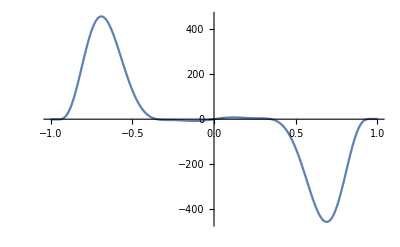

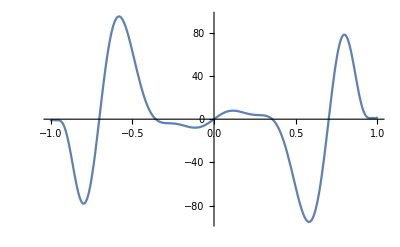

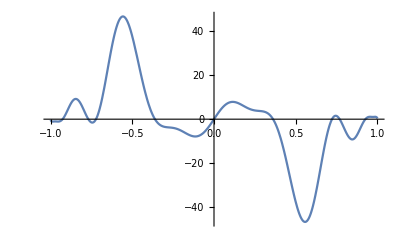

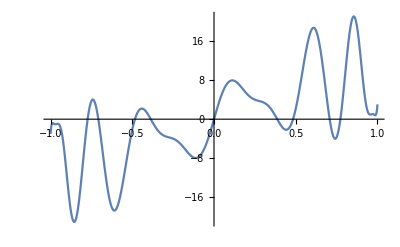

4

0.+5.56569 x-221.023 x^3+4169.99 x^5-42009.9 x^7+239753. x^9-815626. x^11+1.71185×10^6 x^13-2.23579×10^6 x^15+1.76973×10^6 x^17-777239. x^19+145377. x^21

$Aborted

```mathematica
anglesForCircuit[theVQE,True]
```

## Export Candidates to Python

```mathematica
exportCandidate[vqe_Association]:=Module[{str="",idleRemoved=vqe["textual"]//DeleteCases[#,x_/;StringTake[x,2]=="I "]&,angles,subnorm},
{subnorm,angles}=anglesForCircuit[vqe];
Print[subnorm];
str=str<>"{\n    \"qubits\": ";
str=str<>(vqe["qubits"]//ToString)<>",";
str=str<>"\n    \"ancillas\": 1,";
str=str<>"\n    \"circuit\": [";
str=str<>StringRiffle["("<>StringReplace["\""<>StringReplace[#," "->"\" ",1]," "->", "]<>")"&/@(idleRemoved),", "]<>"],\n";
str=str<>"    \"angles\": [";
str=str<>StringRiffle[ToString/@angles,", "]<>"],\n";
str=str<>"    \"histogram\": [\t";
str=str<>StringRiffle[("["<>StringRiffle[(ToString[#,CForm])&/@#,", "]<>"]")&/@(subnorm^2*vqe["Histogram"]),",\n\t\t\t\t\t"]<>"],\n";
str=str<>"}";
str
]
```

```mathematica
exportCandidate[theVQE]
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

{
    "qubits": 7,
    "ancillas": 1,
    "circuit": [("SY", 7), ("RX", 6), ("TY", 5), ("TY", 4), ("T", 3), ("RY", 2), ("SX", 1), ("CZ", 6, 7), ("CZ", 4, 5), ("CZ", 2, 3), ("SX", 6), ("SX", 5), ("SX", 4), ("Z", 3), ("S", 2), ("RY", 1), ("CZ", 5, 6), ("CZ", 3, 4), ("CZ", 1, 2), ("S", 7), ("T", 6), ("SX", 5), ("T", 4), ("S", 3), ("RX", 2), ("Z", 1), ("CZ", 6, 7), ("CZ", 4, 5), ("CZ", 2, 3), ("SX", 7), ("R", 6), ("R", 5), ("TX", 3), ("SX", 1), ("CZ", 5, 6), ("CZ", 3, 4), ("CZ", 1, 2), ("TY", 7), ("SX", 6), ("RY", 5), ("Z", 4), ("SX", 3), ("SY", 2), ("TY", 1), ("CZ", 6, 7), ("CZ", 4, 5), ("CZ", 2, 3), ("T", 7), ("RY", 6), ("RX", 5), ("TY", 4), ("Y", 3), ("RY", 2), ("TX", 1), ("CZ", 5, 6), ("CZ", 3, 4), ("CZ", 1, 2), ("TX", 7), ("TX", 6), ("T", 5), ("Y", 4), ("R", 3), ("Y", 2), ("TX", 1), ("CZ", 6, 7), ("CZ", 4, 5), ("CZ", 2, 3), ("SX", 6), ("Z", 5), ("R", 3), ("Y", 2), ("RX", 1)],
    "angles": [-1.45909, -1.52778, 4.5859, 4.70113, -1.42819, 4.46697, -1.42378, -1.47012, 4.61948, 4.65006, 4.65006, 4.61948, -1.47012, -1.42378, 4.46697, -1.42819, 4.70113, 4.5859, -1.52778, -1.45909, 1.40457],
    "histogram": [	[0.001359833348398322, 0.000449467290268155, 0.002228611570486892, 0.0004674244434705996, 0.0006547426307471456, 0.0016322937152840429, 5.674411090528051e-6, 0.0019207165372189458, 0.0031638721443354666, 0.0013278767943747354, 0.008250306809426077, 0.0020298789633107894, 0.000130480541469412, 0.000597541453559236, 0.002091342003176587, 0.002473145773015557, 0.008243869915409428, 0.002579510126924676, 0.01976759781916504, 0.0067904345218935255, 0.0025497056622119673, 0.005409496624914228, 0.0010156125704338364, 0.006198244235797902, 0.002152974797464979, 0.0007510932156840905, 0.006418639347113561, 0.0022900802975663443, 0.00019871164226082063, 0.00028100836054093626, 0.0009608888717544597, 0.0008716326334709546, 0.0015364762832571668, 0.0005131710438726801, 0.002648169744737993, 0.0005218330489988072, 0.0006133336027668888, 0.0015240955002748077, 0.000017060799853546046, 0.0016645137596197433, 0.0026976320627267107, 0.0011410647945619828, 0.007185910732834253, 0.0018569107074618003, 0.00013329099191270453, 0.000569985451575923, 0.0019105539702421192, 0.002410614737864428, 0.0077020204306293034, 0.002414729291828971, 0.018198503004617134, 0.006134785699021621, 0.0023931760945064334, 0.005117460632367338, 0.0008684240950455867, 0.0057532766975050935, 0.0020903007808308694, 0.0007441660803324219, 0.006403954032586493, 0.0023205202170557414, 0.0001679716061205097, 0.00022570929910666862, 0.0010758886589263656, 0.000993654986285791],
					[0.0012024842401170874, 0.0017387198456668366, 0.00008853794620207437, 0.001475594620637968, 0.001468870713827902, 0.0012171693652169356, 0.0013582898027491468, 0.00016909741254667772, 0.003761583342705782, 0.0033648570982805054, 0.0018288940093657553, 0.005816600261095012, 0.00009342092339299386, 0.0005761570072506218, 0.0020274693072343418, 0.002595462533342839, 0.010865605758101584, 0.014683889934159578, 0.00035041450314333576, 0.011481502187988147, 0.0062111052889106426, 0.00408212600925663, 0.004665823888753205, 0.00021400390643744988, 0.0033200920205050024, 0.0038592359137852566, 0.0005838191812460476, 0.0038496405422926484, 0.0005274191421716242, 0.0002723539323690506, 0.0007979903433627216, 0.0007144780901237864, 0.0014079189093512807, 0.001957278170592703, 0.00010103116166324779, 0.0017534218792593795, 0.0014113175344231572, 0.0011166177980696556, 0.0011612295643169599, 0.00012983876570519924, 0.003272696140243429, 0.002903831347840755, 0.0016507114223477761, 0.005054279387152794, 0.00008988461480097725, 0.0005647835198457341, 0.001979122209931411, 0.0023906548070170737, 0.009996301762306963, 0.013532178282133874, 0.000304627847517031, 0.010616930534139098, 0.005831812796720522, 0.0038431950375891247, 0.00430325775442239, 0.00015407193069242212, 0.003283764872997878, 0.003734481744302093, 0.0006763392535845379, 0.003864355239921013, 0.00042329537693251614, 0.00025131739366645217, 0.0009103091987398552, 0.0008783025811005191],
					[0.0016552565884704832, 0.0019605082404536987, 0.0005147625039432077, 0.000374809319756581, 0.0028566607877897957, 0.0013135827943699901, 4.6677523119167005e-6, 0.00003851595986895461, 0.003516968238841837, 0.0052507089239109935, 0.003810229424368087, 0.0021940281243261733, 0.0030289507152055457, 0.000532856461393929, 0.0004256731992337618, 0.0013050293953875646, 0.014787477680956528, 0.01095850241319936, 0.007273298779440501, 0.004362133509796299, 0.006735547966868081, 0.007182863099382749, 0.00029928383282249024, 0.0009553641942845909, 0.004024415710584758, 0.0030215510777181877, 0.0029158095274007785, 0.001651011342125254, 0.00026707346292850737, 0.0011494091866165643, 0.00022017889437913758, 0.0006755799641029792, 0.0018728949445129897, 0.0022208178773180185, 0.0006583899691246379, 0.0004675473299109909, 0.0025895066476999654, 0.0012003752800721443, 0.00001042111857433059, 0.000018700616168550438, 0.0030538402523646907, 0.004496684372155388, 0.0033928045534579636, 0.0019381891196067374, 0.0028386467466306044, 0.0005784159400293466, 0.00038656376623090027, 0.0012208186987043093, 0.013599909524179487, 0.0102719600771068, 0.006598385157724985, 0.0039797836670857085, 0.006442038189474106, 0.00661022959860132, 0.0002620109552101596, 0.0008180587761388933, 0.003916660611848297, 0.0029706967758293575, 0.0029910333962247277, 0.0016805503269031244, 0.0003432763779928423, 0.001118583610203166, 0.00024091296923933734, 0.0007604515930039734],
					[0.0014599245173618357, 0.0015288033179590122, 0.0005012625902680507, 0.0010153462270350768, 0.0004053152036995681, 0.0012225434611934367, 0.001672633286465309, 0.0009129353429823328, 0.0025690017339560895, 0.0030679826432729942, 0.0026430137198950447, 0.006491936614322967, 0.0002791483395449715, 0.0018254455974091373, 0.0025085345131839725, 0.0006793813210827185, 0.007171747075385121, 0.012846797955568982, 0.006302813235183777, 0.011060054117254773, 0.003363988221827267, 0.0021858614062642712, 0.0055050507548884, 0.004118158710377965, 0.0015393404467641861, 0.003404942768131429, 0.002270484284578628, 0.004398020158354763, 0.0007430725781561952, 0.00003350534599059813, 0.0009091480810408844, 0.0006265155028394921, 0.001600264444079447, 0.0017262874894174557, 0.0006141547850065308, 0.0012789434023632116, 0.0004027503379592361, 0.0011758195444326264, 0.001432387719435892, 0.0008080460606872356, 0.0021639556178059322, 0.002646543558582659, 0.002345485813388753, 0.005725533307807401, 0.0002692285738069084, 0.001617866015700191, 0.0024415994296347584, 0.000695751132453351, 0.006763362833182318, 0.011842726899228464, 0.005736966292036783, 0.010106982401649492, 0.0030768665629245205, 0.0021730083750677947, 0.005087088590545206, 0.0037953739908869297, 0.001457184009312084, 0.0032985656745252875, 0.0022986452642261386, 0.004504546162742012, 0.0007176503535770929, 0.00005658341164666833, 0.0010471445593501635, 0.0006418462258654229],
					[0.0007266249552636643, 0.00028749503051894894, 0.0007957099562496862, 0.000012899404523585217, 0.001705853348806242, 0.00336485848856289, 0.0015944062982967727, 0.005592392953057476, 0.0005998989554047736, 0.00007840383808793736, 0.0020103182630874994, 0.004994586662425354, 0.0009334791850322171, 0.0015368484988012832, 0.0025320540083611986, 0.0020173785831529584, 0.002444955696906302, 0.0010342906764389355, 0.007138180271876725, 0.0021976485679394003, 0.005508449001819973, 0.010979178683461715, 0.006283907619823027, 0.022255971547784498, 0.00025167862812788, 0.00006688782392730157, 0.0021180991565242606, 0.0022335597796442792, 0.0003066700592225605, 0.0005555498915319437, 0.0011195595824918796, 0.0019849136550859217, 0.0006460978430072458, 0.0002688796238730034, 0.0006867616127309923, 0.000010499997193884472, 0.001697671355982837, 0.0033231356981670503, 0.0017059651363531935, 0.005648622562880283, 0.0005911510188945864, 0.00007681309596014949, 0.001974342776213177, 0.004588902846237135, 0.0007695951871833754, 0.0012681031374458865, 0.002130604113864799, 0.0015574712265739958, 0.002282805919549819, 0.0009744784917383557, 0.006416638316492694, 0.0018521505027853458, 0.005282706813104493, 0.01051022979041378, 0.005990553573712305, 0.021117726873304134, 0.00026727969440489284, 0.00005509922515430159, 0.002219745580548326, 0.002527364339190039, 0.00020159304295999027, 0.0003459815711644313, 0.0010429799627311486, 0.001517207909512202],
					[0.00034372362799735886, 0.00042943589626274467, 0.000310088463524502, 0.000739481358771286, 0.003944041382618021, 0.0027979159765238277, 0.004500330325339863, 0.00101522340424166, 0.0017181714641339599, 0.003935432578637681, 0.00165905303919244, 0.00037055063704145657, 0.0026807996462036255, 0.00115340757315758, 0.0017974501950275897, 0.0013881028609588615, 0.0033069384662538933, 0.0030063534541945685, 0.0016362508106511162, 0.004865532482061814, 0.011868738317798359, 0.009674596408482849, 0.018089824141121525, 0.005394347985486382, 0.0012586356684320004, 0.0017859381734617143, 0.0006993002343104373, 0.0009263513120195601, 0.0005964002041801617, 0.0005904410406435644, 0.0017011426736648957, 0.0010787092698436678, 0.00027011595271629753, 0.0002919929919671087, 0.000364604848234027, 0.000685525283887715, 0.003923544967820254, 0.002780184496386272, 0.004566109422476828, 0.0011055558666999879, 0.0016576386703163015, 0.0037286587379334055, 0.0014513951271982997, 0.0003935172018570108, 0.0022430515517116267, 0.0009328212787476834, 0.0013942451350096728, 0.0011556556995990718, 0.002935657106943971, 0.00260397108776528, 0.0015309853345698873, 0.00445545970128711, 0.011433263109773386, 0.009236786885875743, 0.017163646800532804, 0.005067520254352698, 0.0013694948433824084, 0.0020621448967804257, 0.0007324991368145143, 0.0009053499623202226, 0.00038743025991785836, 0.00039694480086249095, 0.0013218561516097115, 0.0010015312739777192],
					[0.00035866772538304146, 0.0012334169741444782, 0.0001182447229568895, 0.00011239992407148485, 0.004318465562049105, 0.006027933558365889, 0.00038197898662203065, 0.0015291329816863948, 0.004216128139127609, 0.0005256122287486368, 0.0021317205242061214, 0.0008097468269231716, 0.0008218292695667451, 0.003928307845046535, 0.0006230042895563684, 0.0016466188711780252, 0.003214768302694102, 0.004035332505657068, 0.0035712437599787466, 0.001993730644831509, 0.016680437583210042, 0.020697683999318404, 0.0013915200531580585, 0.006257865217202751, 0.0020073667413892183, 0.00022188769212240449, 0.0016701030476268702, 0.000770867907085211, 0.001182949423176569, 0.0016328068977929388, 0.00023802587599242264, 0.0009129109913703605, 0.00023163454184392627, 0.001142642242778063, 0.00012942457500264774, 0.0001085377171804921, 0.004251272330910801, 0.006105086373491366, 0.00040617914670664634, 0.0016128569022745187, 0.003984854686026781, 0.0005064295831585763, 0.0019773717161474694, 0.0007625537519721944, 0.0006347558107515512, 0.003206954291738398, 0.0005260564265756798, 0.0013580071360024528, 0.002772751681170953, 0.0038131375019587557, 0.0031624055356595424, 0.0017777785117770093, 0.015800135330565856, 0.01981840041952356, 0.0013321062898592247, 0.005950575010586033, 0.0022997461685878794, 0.0001903067946032937, 0.0017721395077568037, 0.0008072963683496043, 0.0008485456518509863, 0.001229748757844078, 0.00022248425942116368, 0.0008069838172515575],
					[0.0009120297268354408, 0.0003906981345533422, 0.00008036951490119163, 0.000439631970265923, 0.002807467484173663, 0.000585119754194375, 0.00526247878954111, 0.003602445060814271, 0.0012190396812997056, 0.0032137895944917955, 0.001812085371558974, 0.0014382930716550627, 0.002653682695505583, 0.00047122687930279165, 0.0019972212614419935, 0.0018976294390973024, 0.0018284710924626648, 0.0027191569220264, 0.002489342025499206, 0.005778105173173167, 0.008949940295216455, 0.0016561061067816977, 0.021282196693631083, 0.013139263757260109, 0.0000611626411690928, 0.0015041299896067883, 0.00127410465886765, 0.0018308280985801766, 0.0007892917926475136, 0.00009651364925831789, 0.0019993467652886327, 0.0010815409811378927, 0.0008269044819411843, 0.0002712379608904851, 0.00006893429813394113, 0.0004451623358395315, 0.002865419841372989, 0.0005295019280421414, 0.005334627305143187, 0.0036458456788250517, 0.0011305413834735805, 0.0030522843416590857, 0.0016951240963398349, 0.0013532599158324796, 0.0022113471368277165, 0.00045087097854232727, 0.001541891968211709, 0.0015216635814863327, 0.001766209550916375, 0.0023658371771187506, 0.002184693015829218, 0.005209333486701922, 0.008616462825105923, 0.0015671509827363576, 0.020183559358415537, 0.012534043884277004, 0.00010109181652279034, 0.0017300616063599126, 0.0013769809305775446, 0.0018613544858373315, 0.0006383172152393434, 0.00010321104009716838, 0.0015523184290053662, 0.0008139158020258983],
					[0.0004950295046047768, 0.00023385106985634302, 0.0008652453852448416, 0.00014186821201153787, 0.00016625079131319322, 0.000291319635747073, 0.00037416277402291996, 0.0006757592798872853, 0.0032827860882112957, 0.0012426579450981459, 0.0026477373880136666, 0.0005967614725208127, 0.0027184864139348105, 0.006196473558826694, 0.0003486466251565364, 0.008506172285182552, 0.0035489816627451523, 0.0013216874778469, 0.006933161088171201, 0.0008933526671192429, 0.0046089178557831584, 0.009547097115071493, 0.0032859987979376613, 0.016756168513451564, 0.0016890684913141148, 0.000587924320061428, 0.002195583241401258, 0.0003155416527257908, 0.002136494611093322, 0.004650907397239072, 0.0007732942683467846, 0.007235321482298511, 0.00035780818532880876, 0.00017430894872464016, 0.0007118557563166421, 0.00016688335114386487, 0.0001661327610590574, 0.0003021454078906453, 0.0003665723060551863, 0.000768355213113636, 0.003135567946904215, 0.0011893290880149302, 0.0025892774932051318, 0.0005184180444719159, 0.0025353573680514073, 0.005761498967091351, 0.00033961722730972634, 0.00786148916788037, 0.003114596164148532, 0.0011661287297942634, 0.006209891002191196, 0.0008321237375100719, 0.0040756904337974804, 0.008425584354428554, 0.0029953156777730245, 0.014923848492784563, 0.0019191249464098512, 0.0006756296508155149, 0.0023573669033301573, 0.0003207009356642112, 0.0022741521258091914, 0.004967624543578406, 0.0007581656500442316, 0.00758859825868705],
					[0.0003230927112842414, 0.0001833683665518218, 0.0004535293500644882, 0.0007760037438169479, 0.0003866605296841296, 0.00026587775112862347, 0.0005761323200718487, 0.00027882188008586086, 0.001277634807834842, 0.002328095072555754, 0.00155145248817636, 0.0026127605252769816, 0.006028949366485373, 0.004868452128681245, 0.006356206570436109, 0.0005161708174978661, 0.0033332301986925906, 0.003693345402220199, 0.0007489889276441631, 0.004921618367325557, 0.010079892506757787, 0.00806313060425233, 0.013301955764982276, 0.0027532034062513963, 0.0011442723246279179, 0.001720047856625315, 0.00028456228741457795, 0.0016392352368347805, 0.004683641800224518, 0.0037911293873231743, 0.005580686706068591, 0.0007405598653613757, 0.0002697054529434106, 0.00014755688887671875, 0.00037713464759594854, 0.0006164592520978737, 0.00036193965391694406, 0.00028521519848461293, 0.0006492727756880778, 0.00030677806002889246, 0.0012384214629519842, 0.0021986929201214425, 0.0014552930712547207, 0.002540185118268085, 0.005643186770007429, 0.004521094694807001, 0.005875751841124793, 0.0004579294243936474, 0.002975989989418047, 0.003251840974591766, 0.0006948789270668361, 0.0044000297425674266, 0.008901574153045655, 0.007134791307053639, 0.011864747619528312, 0.0025193258791559613, 0.0012179305537436361, 0.0018572296912222782, 0.0003825961908517783, 0.0018150660004020514, 0.005002996965080733, 0.004028632039686672, 0.00583411834480955, 0.0007227932285418798],
					[0.0001761726330481246, 0.0009414636482554189, 0.00038981805131730745, 0.0002285398390966472, 0.0003670400908743989, 0.0007492997068839394, 0.00008528668045061557, 0.000305866002761518, 0.0019601625932956605, 0.005488946181221865, 0.00010475642750449887, 0.00021607769182191753, 0.009792038257044108, 0.007115883948080083, 0.0000947644859332006, 0.000767092192043206, 0.0035756777675161012, 0.005498883721290489, 0.002177499471132486, 0.0014451219359434364, 0.014222379248351518, 0.015558128740613176, 0.0007469143365598838, 0.0036707599567192754, 0.0015713179434125668, 0.002577428992078031, 0.00033714632785532885, 0.00030222444215664124, 0.007144260359544374, 0.006381382909263721, 0.0001812193328537595, 0.001089155157315839, 0.00015356228425256, 0.0006922376324382225, 0.00036185142401804735, 0.00020320490080512118, 0.00045781296553622886, 0.0007507427566724385, 0.00008105505770785572, 0.00031359490820200426, 0.0018489409123397342, 0.005243631141603436, 0.00011810048415819408, 0.00022192003449487027, 0.00902639671352152, 0.006658696466569266, 0.0000938293924313604, 0.0007190401578106828, 0.0031616941324546974, 0.004836619250436098, 0.002007157322778633, 0.0013172689279745977, 0.012573322044305656, 0.01384652127692336, 0.0006789380267898303, 0.0033216576107647834, 0.0016791317480842958, 0.0029651490338670865, 0.00032117529180123545, 0.0003073663624671189, 0.007608633439541095, 0.006704906444913257, 0.0001802624191168885, 0.0010947382745475948],
					[0.0005464549285954534, 0.00018206669286899974, 0.00022264577927577517, 0.0007848267709772849, 0.0003922966749138381, 5.750993025924005e-6, 0.0006671551006099946, 0.00044228971242071916, 0.004577051241683524, 0.002037935532149558, 0.0001383047529680157, 0.00101665136704283, 0.002557996682817716, 0.0029166610846939364, 0.007642469364393339, 0.004652651751195586, 0.003389230565915429, 0.0033332035935116334, 0.0016875961099478932, 0.004287152626507592, 0.0064369299703381806, 0.0021797631212934886, 0.015713376083777292, 0.009868113106834959, 0.0019982114974966157, 0.0015174690880864281, 0.0003560732974828003, 0.0009163638224367637, 0.0024463735394641513, 0.001587350616500296, 0.0066460649003599334, 0.004116228702653375, 0.0003783040317496566, 0.00014527648423484453, 0.0002114907008228367, 0.0006757850247066234, 0.00036584402036678615, 0.000013626037831294946, 0.0007577818359069475, 0.0004659537940135204, 0.004338218496952026, 0.0019294956694082114, 0.00014136527742638678, 0.0010235131288095685, 0.0024215781253042936, 0.0026852288484170085, 0.007060208022915188, 0.004330947733696354, 0.002939441035596295, 0.002937132366795436, 0.001541830693633885, 0.003904335537618495, 0.005738834015608368, 0.0018825237083514793, 0.014012455946719002, 0.008786625288104876, 0.002320640199526192, 0.0016388190718590813, 0.0003476790386923204, 0.0009656841261421312, 0.0025667630592320764, 0.0017513825614847269, 0.006951989152603919, 0.004318405804798096],
					[0.001819363212754027, 0.0005611724672418045, 0.007359579589296169, 0.004300947543347392, 0.0002469782916513347, 0.00035421838605943117, 0.0017070569153102338, 0.0018184385264812509, 0.0002530505978321235, 0.00010556147105348394, 0.0024123842366954823, 0.0024652122458505717, 0.00029284020915566327, 0.00028953057557425544, 0.0037936104064354085, 0.0010032637548938572, 0.007280570042902134, 0.0023126704195166234, 0.024959624810210388, 0.012007379239504495, 0.001493340081577262, 0.0024948587951806912, 0.004391042107596926, 0.006675925791724163, 0.0005748588409471703, 0.00020949962555005702, 0.0013541474548967435, 0.00029544960769399293, 0.00032478381706158515, 0.0005323702529575535, 0.0009296334706218528, 0.0006433462846650616, 0.0017197489724206324, 0.000523639907852901, 0.0068895853028412965, 0.004039505308940165, 0.00021538136627932637, 0.00032327423944619846, 0.0014366039022499129, 0.0016423613192483838, 0.00025823210323204325, 0.00011265061367533463, 0.002304466314153384, 0.0022533398953356967, 0.0002970196424559875, 0.00029840117303548563, 0.003621390584698833, 0.0010090165866960608, 0.006835912711722238, 0.002162915815654435, 0.02359599212385209, 0.011489325509709086, 0.0013589271671865272, 0.002274308628419038, 0.004061843922916324, 0.006233924203980426, 0.0004727730031342706, 0.0001837988927898251, 0.001075590904871177, 0.00019267057516939338, 0.0003366778298982269, 0.0005318637666262267, 0.0011625210396818244, 0.0006354955111552204],
					[0.004081516057294181, 0.005242609695045796, 0.0008777010610556212, 0.0038392359992437957, 0.0005527219727645044, 0.00042801433919079595, 0.0016374024789417982, 0.001508553328605157, 0.0013437190985409466, 0.0017143722846943788, 0.0010038905589883147, 0.0011742266092080085, 0.001218800797108535, 0.00018230570314831655, 0.001113798260901202, 0.002864340184901135, 0.013602843144505957, 0.017173672679644404, 0.0021142766027621874, 0.013669452085221084, 0.0034852714560867745, 0.0023765106448968574, 0.005792755228404575, 0.00340062944669083, 0.0006709262454660663, 0.0007483515371111374, 0.00012195691153001919, 0.0008927208349807327, 0.0009548571899917383, 0.0003887467542797894, 0.0005793833474468589, 0.0005071465335876736, 0.003837668806882974, 0.004972099843657176, 0.0007871544377036001, 0.0035755564038112125, 0.00045960617716849606, 0.0003908720671885264, 0.001466870618339181, 0.0013002719645276153, 0.0012625739498489496, 0.0015634115956786457, 0.000948160402889093, 0.0011545429779797566, 0.0012030660676631423, 0.00019722513256921655, 0.0011088110965828304, 0.0027167256900711705, 0.012884587061363388, 0.016313237725111326, 0.002012000496319978, 0.012874320878143115, 0.0031423298304837765, 0.0021855145099348903, 0.005407336861232073, 0.0031938227208515696, 0.0005067109811061652, 0.0005104676200562895, 0.00015497595824737559, 0.000752678816554838, 0.001028900594734114, 0.0003793062613186161, 0.0005928670797348336, 0.0006654842115739393],
					[0.005630116934053803, 0.0022080611363004777, 0.004080426743710292, 0.002122457998574847, 0.0007936145746305346, 0.001721728837525325, 0.0003739426459252926, 0.00123740606142109, 0.001980568531425402, 0.00033177540148004677, 0.001999955952942206, 0.0009239086655840036, 0.00007321341206213848, 0.002215768166686964, 0.0008813304154149659, 0.0022089329518951294, 0.018134712856095397, 0.00930174632846902, 0.012405999328516115, 0.0067177859990530915, 0.003245698394094233, 0.007363558991855417, 0.0009914556431760365, 0.0034544537469533136, 0.0007523198686005448, 0.0008592146468594108, 0.0005098099869429374, 0.00031261102668508206, 0.0002536704341930856, 0.0013596925413783178, 0.00022941934376241507, 0.0005873515059722441, 0.0053303046257692065, 0.0020698010278291296, 0.003796282731380689, 0.00197609110707598, 0.0007721992071039485, 0.0014774843570301733, 0.000312433361096266, 0.0010555039019934209, 0.0018104166023869203, 0.0003609042735392885, 0.0018817561741757928, 0.0008756118762944377, 0.00005777264983122197, 0.0022039083050593294, 0.0008419026468520713, 0.0021222443851437478, 0.017236567374448546, 0.008697580135384707, 0.011782928982631509, 0.006367069668473098, 0.003059134187465033, 0.006751104204129554, 0.0009135127165270106, 0.003205252814380688, 0.0005116747307991045, 0.0007467527298102542, 0.00041270200015468197, 0.00025370391520062035, 0.00019290587857199868, 0.001474430460205955, 0.00028480131129615053, 0.0007144204972874016],
					[0.0010148322720749572, 0.004533985177588865, 0.003218589755039784, 0.005273655607935816, 0.0010381429439934322, 0.00012749622026423816, 0.001903524415787388, 0.0010575285394571893, 0.000021657217099139084, 0.001447286287669705, 0.001457190909339696, 0.0023100741373230952, 0.002157177421198817, 0.0010544273941156075, 0.0012277189698416487, 0.0009399211609031179, 0.004724834778027952, 0.014954871393901257, 0.009897627461247232, 0.016982910878957293, 0.00401357315371853, 2.9546535437951064e-6, 0.006697197487503762, 0.004341441481312929, 0.0004884444143410908, 0.0006694835598342585, 0.0003954473354513748, 0.0008805802194612463, 0.0009494162243265515, 0.00020191811695729133, 0.0006391038232080434, 0.0006396956608141908, 0.0009758151711839538, 0.004297996796917533, 0.0030083989359276637, 0.004890268588025846, 0.0008614921608738086, 0.00011704824776067868, 0.001710654861336693, 0.0009284255572526293, 0.0000293282274144924, 0.0013235843999891497, 0.0013624440786922263, 0.0022133322203005874, 0.0020998315834219942, 0.000958155332708286, 0.0012218617022666382, 0.0009459793684894156, 0.004415190173214187, 0.014198523644597867, 0.009405113398323815, 0.016065318944802037, 0.0036567238971774796, 6.187739829316539e-6, 0.006258199262016433, 0.004007893023479079, 0.0004125768015968887, 0.0004627162739800421, 0.0003026623720196831, 0.0007468779283680629, 0.001086975984828926, 0.00025985979988245496, 0.0006474665759769181, 0.0006722557866731829],
					[0.00026106515805711985, 0.0000839705925696443, 0.0005615982111466892, 0.0001592639163626575, 0.00007792484096297945, 0.00017514340051906556, 0.000016263300771890436, 0.00017328759864954042, 0.00010228588652653182, 0.00004141132019600829, 0.0003285230115904652, 0.00011829326287413122, 6.887580889552549e-6, 0.000016992458701205616, 0.00008667268370331727, 0.00010986165999850252, 0.00030337519271036447, 0.00010142929222990433, 0.00064790529442525, 0.0001562013177921582, 0.00006524336454290805, 0.0001483083507886142, 0.00002387391263018799, 0.00011621306526819771, 0.00008660045749857286, 0.00003884584126542256, 0.00029153483111077285, 0.00011642056354270038, 0.00001864461067693654, 0.00005362717695187939, 0.00010811176315318328, 0.00021059408040674082, 0.00044920266145904487, 0.0001451293373059922, 0.0010861079313866213, 0.00034172127052244604, 0.00010210468214662034, 0.00021071745331291346, 0.00006342854225829818, 0.00021041219483769537, 0.00002346252870005932, 6.700289983656666e-6, 0.00010323058569432819, 0.0000692732833657009, 0.000022328751874735998, 0.00004767702086143035, 0.000027982767937083584, 0.00011265746227426173, 0.0002552823465460176, 0.00009386179511532735, 0.00038374047570657925, 0.00002647571813086966, 0.00009519929120300361, 0.0002600511976015605, 0.000023997660931976657, 0.0003136597641333611, 0.00086771066318726, 0.00037277420421530686, 0.002146762847338142, 0.00048088912564748165, 0.00006792798732964275, 0.00027443551627720573, 0.0005923830554009176, 0.0008791542867323017],
					[0.0003042499561305594, 0.00041051526330825803, 9.813811111517953e-6, 0.0003413188475857766, 0.0001913406269642973, 0.00012725792698352288, 0.00012395451262900076, 6.607432665773164e-8, 0.00015844362646833318, 0.00015638473244228903, 0.00006419441695837408, 0.00021149070531813942, 6.667408258905009e-6, 0.00002214982579823417, 0.00009459941508982146, 0.00009699773414561712, 0.000340992873744976, 0.00043828448051495367, 0.00002129202998756725, 0.00040834171291017626, 0.00016892479402645162, 0.00010227889677883333, 0.0000791775330322713, 3.2574693923503926e-6, 0.0001345992255682719, 0.0001186126214796927, 0.0000844083995615787, 0.00019578144680792105, 0.000019779335586713462, 0.00005631511699834887, 0.00017292357408532817, 0.00014195960451835084, 0.0005844832174616419, 0.0007601041790588992, 0.000030819752922592983, 0.0006467540512309727, 0.00026175745627642685, 0.0001539110971706358, 0.00015860577981368412, 0.000012388539294783905, 0.00005891360070557002, 0.00007918392853363592, 0.000013551883532122836, 0.00005101727497241645, 0.00004287024527840215, 0.00004392651874943495, 0.00009105969539956379, 0.00003278954352011273, 0.0001851076161249911, 0.00023015678520113469, 0.000051601279475754336, 0.0002924946546969173, 0.00020819058622636267, 0.00019091097389976704, 0.0002179480814365945, 0.00007585827230717327, 0.0009536338775270975, 0.0008071880768551622, 0.0005414117119795789, 0.001565903174026345, 0.00007356636078338458, 0.00024642839855047233, 0.0007006538755114684, 0.0007932522108947386],
					[0.0004068636307012647, 0.00035870917219108547, 0.00018429977628364096, 0.00011602529896012119, 0.00023592181581096676, 0.00018791135465263104, 5.908092622988349e-6, 0.000012877877816891456, 0.00016810737951602806, 0.00016075702842410935, 0.00016882607181025155, 0.00009282300143675102, 0.00008651103574922561, 0.00005459175873983686, 0.000017838986572045424, 0.00006147260223147055, 0.00043317259994433527, 0.0004291551880641961, 0.00021168787637511658, 0.00013489543277403333, 0.00019127454555818666, 0.00014505581018143222, 7.961923270990548e-6, 9.34641421929581e-6, 0.00013154728504723243, 0.00014799409467916894, 0.00016542995849578099, 0.00008843035519528629, 0.00020413899819254607, 0.00008428773429413293, 0.00002107754492301419, 0.00008147335377904673, 0.0007660492128203318, 0.0006106110240866605, 0.00040279892619372534, 0.00024270203757338496, 0.00022966175313621123, 0.0002929241507688464, 0.000018265261587147714, 0.000045811707063321384, 0.0000853970016729234, 0.00002637370842765895, 0.000060285915059219495, 0.000030610062583943893, 0.00009226212829643603, 0.00008364464221014577, 5.6075628514589906e-6, 0.000029131669589472054, 0.00021139688876989766, 0.0004007856227795775, 0.00008253358868240768, 0.00006464423526691206, 0.000529035977940865, 0.0001485889568937613, 4.667387320470951e-6, 0.000010615591714804952, 0.0008392493510478183, 0.0014767664797149815, 0.0009827399698963126, 0.0005693810397290795, 0.001151896706549404, 0.0001720077787381699, 0.00011798713092860604, 0.00037200922952388614],
					[0.00024156499934669827, 0.0003605487161666513, 0.0001623402134947344, 0.00030144394912802724, 0.00008527772326476068, 0.00010015232484779055, 0.0001486473687800691, 0.00010854172401085676, 0.00006940569592328596, 0.00013968950737177117, 0.0001212408735810073, 0.0002601774043110746, 0.00002807746564193584, 0.000034409447300342, 0.00011357419068035445, 0.00004435327966994555, 0.0002785522459873369, 0.00038722395157796065, 0.00018084408114041195, 0.0003622908184519715, 0.00007537780433169147, 0.00010517745071035868, 0.00009544350906712399, 0.00007763992912073408, 0.00005935490942203525, 0.00010664932011182756, 0.00011332832013068976, 0.0002540691437529172, 0.000027114870851189905, 0.00007544778706302395, 0.00021016456490856946, 0.00007825040836595678, 0.00038380354696802605, 0.0006676940982574875, 0.0003410571521362262, 0.0006296064033123613, 0.00015451641903120708, 0.0000904876093380708, 0.00018498585086146132, 0.0001566729933247887, 0.000012523158508802499, 0.0000680383626424024, 0.0000479687016144653, 0.00007413646497807632, 0.00003081447934154754, 0.000013027422970111095, 0.0001083663749157965, 0.0000584377257200565, 0.00027996490151842236, 0.00020694754986329007, 0.00006909357417352013, 0.0002033543099435606, 0.00003287347596020433, 0.00026574820293534307, 0.00027390336672032477, 0.00012038286825402686, 0.0007386875422999718, 0.0007425526732766973, 0.0006660777175001984, 0.00172081890731132, 0.0000516543847515922, 0.000652173745848178, 0.0008717321902251147, 0.00023834052491518236],
					[0.00007145360368032876, 0.00003250533372246586, 0.0001532316236616599, 0.000028757006181006176, 0.00020030124777626866, 0.00039289126503172424, 0.00022766282594764858, 0.0007530721586389668, 0.00002698263164810081, 2.879533757311157e-6, 0.00013682546970147808, 0.00021039832184370396, 5.9145109145052885e-6, 7.021555957963041e-6, 0.00005585229654077056, 0.000013695498515413356, 0.00005219061376735753, 0.000027355450884502228, 0.00010997550417909569, 0.000040159618329164786, 0.00020253491433387774, 0.00038845232679096095, 0.00026354929528462473, 0.0007563242134039297, 0.000056122230429621235, 8.653669014869111e-6, 0.00018010010133764893, 0.00027005913647638836, 0.0000206890652031119, 0.00003872834123659617, 0.00005647796371027769, 0.000015556670611760572, 0.00008735948537602204, 0.00004087040726083095, 0.00030431826238136504, 0.00013159568969068656, 0.0002484135824522391, 0.00048535801867725795, 0.00033252048330739925, 0.0010288902321670345, 0.00003542847240298544, 9.04945563240843e-6, 0.00011495888923916058, 0.00007372821351957848, 0.000016092703849990055, 0.00003889088522720624, 5.196433454935991e-6, 0.00006946554928178945, 0.00011401712405495102, 0.00004378524301341465, 0.00005822316592755393, 0.0000548636498789843, 0.00030457556402520557, 0.0005868570626069476, 0.00032143388533944936, 0.0009149489313780199, 0.00022715297778979333, 0.0000382786480600525, 0.0005437683902508577, 0.00142671956063436, 0.0003590824177139587, 0.0006209047049600183, 0.0007730480827516474, 0.0007466465271117343],
					[0.00006301914333787794, 0.00004464514084102419, 0.00005556546902031108, 0.0001227178140462483, 0.000445518192325847, 0.00034040944034648374, 0.00061296396606875, 0.0001750358986535248, 0.00009860328030829978, 0.00018523881796333466, 0.0000521421355284707, 0.00004110172315048945, 0.000022996326707982263, 4.237412818955937e-6, 0.0000153725966109619, 0.00003987752579075081, 0.00004000438148099023, 0.000017739127003635697, 0.0000746111050928862, 0.00009732657358260963, 0.00045711792105833084, 0.0003378941746532462, 0.0006209649530845708, 0.00019488370101725542, 0.00013477180093021283, 0.0002686248704009918, 0.00005755649650501578, 0.00005398196942230677, 0.00006661134736563894, 0.000023052391931883753, 0.000013193343882987726, 0.00002859495758123644, 0.0001386488221215203, 0.00011761865000210642, 0.00010133652506460399, 0.00020653984752067926, 0.000536813124275673, 0.00043345795789528284, 0.0008438458567239918, 0.0002810653777089855, 0.0000690077627887363, 0.00010311574934389682, 6.040936578665951e-6, 0.000055000582082832715, 0.00003139145096734288, 0.00003256759912142243, 0.00005299065401035601, 0.000012695867714799762, 0.0000309464835842538, 0.00008465178759583661, 0.00008422898633810126, 0.00007106192535671301, 0.000730912470945003, 0.0004787472990899666, 0.0007407771963132586, 0.0001773784770013952, 0.0004867505280332833, 0.0011754678013610146, 0.00047840473706313804, 0.00009529651027762769, 0.0010067096631906883, 0.0004622664638617056, 0.0006434624809639856, 0.0003872431245209744],
					[0.000045614260735874034, 0.00012942099623885087, 0.00007007470191936093, 0.00004083760835137598, 0.0005521562095064038, 0.0007499512167366768, 0.0000519001935099522, 0.00021991987764156511, 0.0001999188111690258, 0.000016807256157339257, 0.00011226433454155412, 0.000048095555082674574, 8.883123194498416e-8, 0.00003703319128020553, 0.000013150751838779874, 0.00003221108757772115, 0.00002055220643192674, 0.00010733773741589985, 0.00006659281060620486, 0.00003519843270608986, 0.0005242150790853761, 0.0007828620986103132, 0.00006048021098240374, 0.00024330336113529801, 0.00028300575056206917, 0.00004798324887581472, 0.00012857576109031322, 0.000055370376730329577, 0.000022733624345762323, 0.00006596417704647283, 0.000014482940082537556, 0.00002827129928697574, 0.0001327030321525703, 0.00015441329666739098, 0.00018148865029460811, 0.00009553886559433509, 0.0007317270761374948, 0.0009722384196898566, 0.000073681992212495, 0.000317534828564087, 0.00010760185219782865, 0.00003901274266194476, 0.00005675697490355458, 0.000029793461030805177, 0.0000770763931395523, 0.00004326046504084012, 7.730312653350749e-7, 8.535682368194486e-6, 0.00007184214863236445, 0.0001968853656708171, 6.202793542033045e-7, 1.5413892175201963e-6, 0.0006770360303630878, 0.001088376480436379, 0.00007898500693884712, 0.0002834179256113123, 0.0012421647344356844, 0.00023256105535764018, 0.000555558108950008, 0.00020563567799173311, 0.0003951730013383906, 0.0014018230994861888, 0.00019341962434858332, 0.0005092660073641889],
					[0.0000687982255446024, 0.00004231376249634286, 0.000044138106590907673, 0.0001306974726136094, 0.00033888951383930253, 0.000053613241332937266, 0.000718462845815035, 0.0004629618964073262, 0.00003306859442537712, 0.00015364770967281913, 0.0000943666565788829, 0.00009600299627351682, 0.000034971553674428226, 0.00001567906247173647, 0.000016620856337929878, 0.000015212389444556552, 0.00005740336337143367, 0.000017718249747670165, 0.0000380323893903474, 0.00011652718465067056, 0.00036746221322739856, 0.000042121527650456184, 0.0007253969125702175, 0.0004758800963653273, 0.00007468397809706065, 0.0002233219717272905, 0.00011505415556511128, 0.00010187503186906687, 0.00005506662660767078, 0.00003735575330723149, 0.000013649170325505281, 0.000025380490521337745, 0.00005997842431992973, 0.0001057874100397131, 0.0001224544877071936, 0.0002759235226420721, 0.0004327744529996576, 0.000058673839602672454, 0.0009905880650989086, 0.0006131459589026859, 0.000027573984264899295, 0.00008843412401619892, 0.000048961189212435705, 0.00006819573330059952, 0.000011532064717353544, 0.000021373663284769445, 0.00006423841222297813, 0.00003250143158882169, 0.00018010431561710517, 0.00007158767560861142, 1.7958622412753683e-6, 0.000017401329407912438, 0.0005413122670301033, 0.00009985549023010193, 0.000860598465744296, 0.0006260492203451275, 0.0004502944363280418, 0.0009600551718080913, 0.00048774524061932545, 0.0003378247279796084, 0.0009091597501460526, 0.00018513056408117702, 0.000719308444621404, 0.000686082973688717],
					[0.000060232419823255094, 0.000023691212385775475, 0.00014331027890177354, 0.000028502805673924232, 0.00008846579831609016, 0.0001808758001105283, 0.00008080642408720171, 0.0003476023287391282, 0.00016385189259634296, 0.000060718852934058096, 0.0001631598032580261, 0.00001956625862290106, 0.00014589968935043582, 0.0003238096291060202, 0.00003249790353763349, 0.00045645378607621096, 0.000028677840732551763, 0.000010593510775268338, 0.00009329764733262423, 0.00003574419541845012, 0.00008015009577395753, 0.00016834894090706493, 0.00006976328142999609, 0.0003371153226682778, 0.0002378830169636591, 0.00009122662555044578, 0.000227649476623592, 0.00001954401102205744, 0.0001705154945586538, 0.0003787103349890023, 0.000033702834830582075, 0.0005040064854175972, 0.0001384839573054361, 0.00004874115387874915, 0.000284284595452261, 0.0000521102219350076, 0.0002293606268579672, 0.00048236143969189026, 0.00014992701083521088, 0.0008543256824802474, 0.00010153400807987303, 0.00003888583799794453, 0.00013015285412260294, 3.116246731164688e-6, 0.00007723868423339899, 0.00016350336762455817, 0.000033306575577347295, 0.00023480450111723028, 0.0000767865804158804, 0.0000385663626102101, 0.00008046646695038896, 0.000032595095129987894, 1.8461732579002656e-8, 1.054597977406538e-6, 0.000027338201547648533, 0.000011607598867113146, 0.0009771130923450192, 0.0003779734287570146, 0.0007560728513107882, 0.00016723488209068285, 0.0007122176697958305, 0.0016335389900011992, 0.00007128828375528239, 0.0021704333722099164],
					[0.00006732287092005866, 0.00006649592244357738, 0.000022239303053601814, 0.00009967862036748818, 0.00018983597824545238, 0.00015684924416347527, 0.00027921888289174314, 0.00007184624595227886, 0.00007964718149053203, 0.00012696465310757375, 0.000056453498111671196, 0.00014423147470155257, 0.0003259024448933971, 0.00025679252512460677, 0.0003455609503020419, 0.000030405087750256894, 0.00004721244144969254, 0.00005178593352582078, 0.0000126361026251812, 0.000056678716658198465, 0.00016586316573478482, 0.00014764395255011616, 0.00026962146589212745, 0.00007224905660228039, 0.00010448609910965652, 0.0001585640322120933, 0.00009886299577362343, 0.00021439000306437984, 0.0003875259701218186, 0.0002958988712825026, 0.0003786231086937547, 0.000024887199697769247, 0.00014367167838485743, 0.0001731617898075064, 0.000017432389432936113, 0.00018935407094615393, 0.0004942884424379542, 0.00040824954954634535, 0.0006754367597918695, 0.00013800000808914564, 0.00005944947022458925, 0.00007314006945250043, 0.00003151018535853683, 0.00010958922189595888, 0.00017688667226545163, 0.00013064365071593917, 0.00018139953463469036, 0.00001992327093645332, 0.000021823108182253555, 6.366186980788122e-6, 0.00010301548856508024, 0.00009720972137834376, 1.4016543800905308e-6, 8.552343428560847e-7, 0.00001077082625683554, 0.000026991145144965508, 0.0003486426245267614, 0.0006291828250761508, 0.0005151651493595492, 0.0007854036555410396, 0.001590625471438656, 0.001271902818283259, 0.0016107482237224914, 0.00011420180231782845],
					[0.00006738787002565217, 0.00009560669991960562, 0.00005785207020571099, 0.00003489007663375803, 0.0002787921780794523, 0.0003152942085462818, 0.000017849799679184574, 0.0000858141649480304, 0.00010966713047469628, 0.00026647470271352105, 0.000013618848213401639, 0.000017536126009709485, 0.0004915389199808792, 0.0004054450351510933, 8.46127779391966e-6, 0.00005321577514441143, 0.00005499765645717633, 0.00004166290456284028, 0.00004616058925114975, 0.000025492043987727963, 0.0002816155086723753, 0.0002813133695292786, 0.00001474377088328999, 0.00007770499169435684, 0.0001332378593402999, 0.000397654140397531, 0.000020123481068845584, 0.00002528764935307521, 0.0005601549537409766, 0.0004630161652445454, 9.604563772478122e-6, 0.000054159467037841656, 0.00016965834636990815, 0.00020444993482581414, 0.00009050496825842034, 0.00005900667911731191, 0.0007459109880954227, 0.000761117085755927, 0.000033382695312957526, 0.00017556399070101008, 0.0000642066291357816, 0.00016638407347189187, 0.000023063181473454054, 0.000020035062850456248, 0.0002265510149691283, 0.000234192454949195, 8.531178688363824e-6, 0.000039578479945848336, 2.985168456577939e-6, 0.0001588943087466612, 0.0000434588987645063, 0.000023076129138722425, 0.000013844723659364074, 4.785373576622728e-6, 5.992473670227854e-6, 0.000015396289218531248, 0.0005193640986232951, 0.0016632948187062435, 0.00003288361297649192, 0.00006285172419746867, 0.0025748966851948385, 0.0018175462610860466, 0.000021373273015862722, 0.0001736620964654785],
					[0.000051129846557192285, 0.00006027917257720173, 0.000041998774082209654, 0.00010232892356812528, 0.00013099268715338817, 0.00003506738897409503, 0.00032953895405338625, 0.00020215132107208122, 0.00021323123967737363, 0.00011223923548379337, 0.000014964021000613677, 0.00006686231124954882, 0.00015442059067320672, 0.0001317144555161989, 0.0004130402396090883, 0.0002594857222718059, 0.0000189434057645643, 0.00004578899554005631, 0.000034700704904849806, 0.00006888008804942735, 0.00010926702074327798, 0.00003958952793793122, 0.0003197309724288029, 0.00018679011966928971, 0.0003131115604458667, 0.0001412737376994122, 0.000017251770993964233, 0.00010466606102051223, 0.00018115413707412367, 0.000161725183979519, 0.0004525892367992984, 0.0002914665919429005, 0.00012892268772295458, 0.00015438379127108545, 0.00007428123421613318, 0.00016603221536127838, 0.0003035314436856715, 0.0001213634260828564, 0.000800111552713574, 0.0004909683373832134, 0.00011949673333129588, 0.00006627685984920026, 0.000017964832137037847, 0.00006995052161405237, 0.0000991746509245068, 0.00005151154910279516, 0.0002146179458121803, 0.0001435489827130521, 0.00010960172890792304, 7.369727624977566e-6, 0.000018691569970322998, 0.00009275147860324381, 7.5361012088818e-6, 0.000016105735084030256, 0.00001313527779386658, 3.241746037968582e-6, 0.0013775458602739317, 0.0005522146032295907, 0.000030001219591170605, 0.0003186325714088052, 0.0006540099105984079, 0.0008087616676572266, 0.0019397971140030904, 0.0011849096235034965],
					[0.0002234580822104098, 0.00006875244956962779, 0.0008043964081555846, 0.0004225161778918483, 0.0000354665519519416, 0.0000605376488695633, 0.00012106850454292953, 0.00019533558507830654, 0.000014244885282071582, 7.604265355967048e-6, 0.00006931182578491461, 0.000046127265072828664, 0.0000211961409248396, 0.00002682560212384552, 0.00015207827479585669, 0.00005052521590877154, 0.00019085138567614078, 0.00005665484569130347, 0.0006839643630561165, 0.0003737717111510366, 0.000024804614548953598, 0.00004668530401849193, 0.00007199046372728463, 0.00014879031803395292, 0.00004087625103356328, 0.000017809271377680278, 0.0002246042440404417, 0.00015378071854886633, 0.00003164174987527196, 0.000035371615853492786, 0.00027655635479040855, 0.00010877590357079459, 0.00029699354331140873, 0.00009273917403506676, 0.000980393882347427, 0.00046390733179447644, 0.00005962923519511675, 0.0001056307899411553, 0.00013143042337040783, 0.00024944850791139636, 0.00005844163924139365, 0.000021383324271126452, 0.00021378433677918504, 0.00009718465663776555, 0.000022711174037100025, 0.00003114778082120512, 0.00011446421717475163, 0.00008284674705190761, 0.0002621277381734846, 0.00007849983191503853, 0.0011599815619599758, 0.0007519022979170821, 0.000026453515734261984, 0.00003178453104547953, 0.00032153341319678293, 0.00027066177612493857, 0.00014813570064364068, 0.00005366026712184014, 0.001135973999001972, 0.00103721577915395, 0.00008809561300914018, 0.00007587036242164363, 0.0012907027859242726, 0.00040170676215344755],
					[0.0004449865820785817, 0.0005745080763996159, 0.00007146618370263681, 0.0004281622756466285, 0.00007623075469711869, 0.00006182309021383518, 0.00016897904681641615, 0.0001053753987153758, 0.000032359371755896025, 0.000028815302604137383, 0.00003155684775076278, 0.00004455671938498651, 0.00007455337642106262, 0.000018589746445279344, 0.000053131610388332, 0.00010435050049864046, 0.00038395338568553356, 0.0005090336425291377, 0.00005558945429804254, 0.0003566658230618851, 0.00004823741313525872, 0.000047646168760277085, 0.00012594876382262626, 0.00007043835461051831, 0.00011471635547956571, 0.0001238774911322251, 0.00007077947845020396, 0.0001276971599385547, 0.00011080684904527699, 0.000028351587769414937, 0.00011206606567664963, 0.00020112112159862588, 0.0005379342977655944, 0.0006904782930528108, 0.0000704225820530714, 0.0005351987586169006, 0.00013647583475997, 0.00009709135695005268, 0.000211986386156462, 0.00010058537855159244, 0.00010999795670242796, 0.00012324235462571825, 0.000032383941253440144, 0.00012516970434788398, 0.00006518132733446528, 0.000027878615724436707, 0.00007767930536457184, 0.0000804306706614908, 0.000651983711865964, 0.000852903399445355, 0.00016112663664520976, 0.0005864976820090514, 0.00006203984763059227, 0.000047813812383806335, 0.00024930147947539396, 0.0002912780966116754, 0.0006339890606946433, 0.0008090120395108501, 0.0003763394402867364, 0.0005556452054291696, 0.00036531210769610064, 0.0000577812703919934, 0.00043202110477059096, 0.0010012610406498143],
					[0.0006091049038798672, 0.00027631325195095563, 0.0004132812152659436, 0.000220423746730701, 0.00010320053347409103, 0.0001858345019774872, 0.000026498028293412443, 0.00009687522669775289, 0.000034344177741974596, 0.000027299798427302078, 0.00005071275086975041, 0.000024931514456756213, 1.1462607641214545e-6, 0.0001229137757344879, 0.000035988918777248294, 0.00009057627847745661, 0.0005385214190999416, 0.00022981536530328816, 0.00035059759710069345, 0.00018630792407066867, 0.00009435257890894045, 0.00012149912049100076, 0.000015221411523181592, 0.00006119758940555705, 0.00014152090708814398, 0.00006333785877141252, 0.0001554047391467243, 0.00007680697999426854, 6.239205859577887e-6, 0.00021234116486752814, 0.00006443287307999573, 0.00016933238028286342, 0.0007251307075979645, 0.0003767314921487167, 0.0004737343779847194, 0.00025843735375698153, 0.0001395046938126494, 0.0002678604061793394, 0.00002975622347622312, 0.00010901763294986474, 0.00013275541573999915, 0.00008284527139723773, 0.00011402793873451437, 0.00006116533105771889, 0.000018760653832493745, 0.0001288977308252266, 0.00002665775043889176, 0.0000768537839883526, 0.0009225535558286117, 0.0003054570525082404, 0.0006786227397810781, 0.00034587808184764605, 0.00011730365498028064, 0.0002422249880189947, 0.00007029693030294861, 0.0002206076627992421, 0.0009197502999772767, 0.00017935234356186372, 0.0008664866953608544, 0.00040939640702140694, 0.00004709665235726071, 0.000746239692872835, 0.0002973964725474672, 0.0007656427057309347],
					[0.00014045372696442309, 0.0004984295172130828, 0.00033109913339748263, 0.0005491407402524763, 0.00009639062762540815, 3.0932266876759118e-6, 0.0001969825334841649, 0.00011594190264549018, 8.02270204097361e-6, 0.00002525177043351033, 0.0000340239217652214, 0.00006998984725607863, 0.00010541235096842423, 0.00003397900477483476, 0.000057743534466742144, 0.00005349034354331268, 0.00012274677184696944, 0.0004405691087848603, 0.0002842602343857516, 0.00045766619055701826, 0.00005570675046951871, 7.270763792899933e-6, 0.0001482794045215993, 0.00008101378154466444, 0.00001519275882046699, 0.00010728165114041976, 0.00011104623594199125, 0.0002035498390976697, 0.00017889360673103099, 0.000051517043020719306, 0.00012405454312172282, 0.00009788043121649505, 0.00020093528430563512, 0.0006010448737440035, 0.0003825231876109367, 0.0006495305858277995, 0.00013748909414256334, 2.5163048397538723e-6, 0.0002460060219227578, 0.00016012753551299818, 0.00003452440870177115, 0.00010824847009150699, 0.00008567227670620948, 0.00016234880142998136, 0.00008944222733702555, 8.171255170217377e-6, 0.00008744318265062903, 0.00006611325392709321, 0.00013465203676704448, 0.0007344567587664737, 0.0005339748789097931, 0.0008494277555222775, 0.00016344183042585667, 0.00004741551732271188, 0.000290495800456812, 0.0001490800878960876, 0.000027251569814640432, 0.0006871019809356466, 0.0006420447260630357, 0.0010185874691080756, 0.0007100120356548007, 0.0003306250830308314, 0.0004821142750573692, 0.0003336241297655015],
					[0.0008504931867630402, 0.00027720651220014943, 0.0016725084305059042, 0.00041482093361331176, 0.0002836731153510827, 0.0006684783895455939, 0.0000249211228154105, 0.000671692739112531, 0.0006961159795044748, 0.00029146859564703183, 0.0020187858635710917, 0.000611642944508109, 0.00003355920651063541, 0.00012311355334759062, 0.0005450969243849467, 0.0006740084852153099, 0.007266557942788796, 0.0023068491245434395, 0.017101993803365318, 0.005521207386686777, 0.0020370528536547017, 0.0043382435754649885, 0.0008234329520741671, 0.004611378462761015, 0.0013286763846217203, 0.00046702538923303505, 0.004489679026769883, 0.0018953813250433505, 0.00020956676077351822, 0.0003508775138651192, 0.0008875129150189967, 0.0013153599828061645, 0.0007651167924804481, 0.0002685307177644085, 0.0011578893474358369, 0.00013989717579349442, 0.0003333184851150856, 0.0008724374130433268, 0.00003080983115298057, 0.001035526934535879, 0.002297522699740163, 0.0009787250224024188, 0.005814016958465382, 0.0013561202628534987, 0.00014329346011686134, 0.0006042392531334706, 0.001554603745182124, 0.0021157065400167485, 0.0015284855065861276, 0.0004656471303951847, 0.003728302431922342, 0.001406713633258741, 0.0005748151612029955, 0.0012277674446386038, 0.00020347314637244758, 0.0015519894371824844, 0.0007804930354638516, 0.0002826252180796324, 0.0020632927887927898, 0.000571849808274527, 0.000024809600610401107, 0.00002955855921773945, 0.000267881278732562, 0.00005263887569825818],
					[0.0009009547857222424, 0.0012312388696508062, 0.000034075250725542414, 0.0010487601569838193, 0.0006804689538677052, 0.00048467345637653663, 0.0004706923980870739, 0.000012930558493299469, 0.0009397135045100353, 0.0008657483572350808, 0.00044201056677750704, 0.0013705409547080782, 0.000016346986659757083, 0.00014048161100724423, 0.0005670860807187034, 0.0006518634910727802, 0.009317368504161703, 0.012447779429088344, 0.0003399859003872146, 0.010091474423747089, 0.005048320158957159, 0.003215165853405019, 0.003433265463010679, 0.00011335636858200415, 0.002335023315917632, 0.0026977201207031474, 0.0005263375889619068, 0.002621681100085276, 0.0004373328760628899, 0.0003784487415205802, 0.0011464780020590977, 0.0008010575528212318, 0.0005893480528597894, 0.0008007495524828923, 0.00010426441579104254, 0.000837072012340457, 0.0007369716288724264, 0.0006450324022350473, 0.0007238130174159094, 0.00016627561532388084, 0.0026095985224634842, 0.0022573878862624246, 0.0013962550763312479, 0.004183143458404308, 0.00013727481223941893, 0.0005555139983116607, 0.0017034860018219544, 0.002021568186076184, 0.0020831890803647067, 0.0028844481051154185, 0.00005075103472944669, 0.002110760481952807, 0.0013577714672171942, 0.0009490531078619758, 0.0011777514905235026, 0.00007346912379385757, 0.0010355869399252793, 0.0011560359606649867, 0.00019630688307340174, 0.0013103310669471322, 0.00010287239366228829, 0.000015355422153005134, 0.00006209305415565396, 0.0001945674442880145],
					[0.0012037611286684082, 0.001191713304635341, 0.0004944936490905116, 0.00032506098068815065, 0.0010012922251464438, 0.0006160627014410379, 0.000011928616645141425, 0.000019481823591996717, 0.0009224322984552636, 0.0011396961065845955, 0.000997044038488469, 0.0005588409397023884, 0.0006737622402662583, 0.00022651547116124432, 0.00011093206545612795, 0.0003645683925748534, 0.012499955151349332, 0.009784106645633664, 0.006172095577248605, 0.0037404508831527642, 0.005278856937812093, 0.005588098067904428, 0.0002496703957596573, 0.0006934824424786947, 0.0028647349466033533, 0.0018436096267195749, 0.0022446620917196108, 0.0012277554606254654, 0.0006868845199271326, 0.0011896737031422242, 0.00019248594921398524, 0.0006942730001804666, 0.0007447761056423444, 0.0011599101607766428, 0.00023905798109318853, 0.0001876897859620055, 0.0016572292731886183, 0.0005878385344422093, 6.468922459501684e-6, 0.000020555933756944693, 0.002353368727971834, 0.00387337537265553, 0.0026745388888573607, 0.001545101953976743, 0.0027076765587367995, 0.00042395916152754737, 0.00031224778557278833, 0.0009739594926120674, 0.002912853672778375, 0.0019888003248613303, 0.0013994675418889542, 0.0008280271626337391, 0.001626458831276236, 0.0016460719833668936, 0.000057707049579442604, 0.00022780732517397646, 0.0011860544566753405, 0.0011455130303402586, 0.000860538344917953, 0.0005061550186772555, 3.0758944033623893e-6, 0.0001577971167139554, 0.00006300976318238544, 0.00015100553995925736],
					[0.0008280761064516584, 0.0010831265211190392, 0.0004456955882375176, 0.0008581308472741983, 0.0002515872169823159, 0.0004478069639843801, 0.0005729670847540566, 0.00037640410110386063, 0.0005210210649834738, 0.0007823697879865556, 0.0006989034501711068, 0.0016157190800895854, 0.00011337920024437758, 0.00034693699816495217, 0.0006913936346761588, 0.00022406833637299514, 0.006366286481380567, 0.010911432880414889, 0.005328973154087175, 0.009589915741501713, 0.0026994377158269488, 0.001922160169476437, 0.004050179210814358, 0.0031383307478371307, 0.0008501526714550808, 0.0023702321819420377, 0.0017222582252867896, 0.003238119046984098, 0.0006273582086300625, 0.00004214240686568345, 0.0013390151132419083, 0.0007548014437261324, 0.0008416113471771565, 0.0007116618671357824, 0.00022080402446857526, 0.0005573567946926788, 0.00015399154135669642, 0.0007762025788122432, 0.0009015826281333246, 0.00044031591554501327, 0.0019180247248422844, 0.0020690263936974053, 0.0018294442882511685, 0.004629889536670608, 0.0001617278989124412, 0.0015662603170328439, 0.0021153757343160408, 0.0005744790481879023, 0.0013296592489582596, 0.0025152919483155452, 0.001225588887096574, 0.0020586086177920232, 0.0007240385362251922, 0.000460191460054152, 0.0013940746963960612, 0.0009797404967211312, 0.0006111913994696437, 0.0010291516224492495, 0.000663057852903345, 0.0013948599757885691, 0.0001591954065062272, 0.00008724219709757761, 0.00006683923726504316, 0.00006161147339011705],
					[0.0002724992402059489, 0.00012111532059355501, 0.0004239282394538139, 0.000030300388265927535, 0.0007656418377339773, 0.0014987984584605657, 0.0008239252167740172, 0.0027237663927030336, 0.0001628282970290321, 0.000017430639050313783, 0.0006804997772375952, 0.0013159416344469134, 0.00012375446815154415, 0.0001909538624049319, 0.0004793550766037074, 0.00022684713348134725, 0.001867349148909533, 0.0008278354593390393, 0.005415249829954216, 0.0017058113750118202, 0.004727325320308653, 0.009336676399567534, 0.0056421163763162845, 0.0189558683065725, 0.0003715299496330781, 0.00007548348152183378, 0.002161091691354725, 0.0021490740806944524, 0.000086913765700151, 0.00019198118285511327, 0.0005347466782272766, 0.0009017423535047498, 0.0003844547613767867, 0.0001499991812442882, 0.0002855120660786003, 0.0000704888317654886, 0.0009657687187509204, 0.0018822630777655244, 0.0009533857525164389, 0.003010171505403061, 0.0005341496854085215, 0.00008255566715674867, 0.0014506262817218071, 0.0037321491875442446, 0.0008357326220812029, 0.0014206068925597865, 0.001961553431608987, 0.001748336976249731, 0.000591398490156596, 0.00023391203445144034, 0.0016561036554781253, 0.00047015289621033397, 0.0011267419202741437, 0.002278913392596722, 0.001158688945874539, 0.0045313950488025485, 0.000011495602797724369, 7.676695108012905e-6, 0.0003675781347847002, 0.000594615994668574, 0.00016756540772166215, 0.000279704250326162, 0.0005092179496577074, 0.0007751826375197025],
					[0.0001636607944428908, 0.00011607145471288133, 0.0001867281737589919, 0.00038138276560448014, 0.0017342445749595633, 0.0012783389352259474, 0.0022110692952110535, 0.0005884791002750237, 0.0005323248933813718, 0.001105454906885237, 0.00037331502459070516, 0.00016560552290652953, 0.0003880455127407946, 0.00013375241519062678, 0.00021684918644226118, 0.0002822634262678465, 0.002437679086695922, 0.002057923807754896, 0.0015152367161664322, 0.003805406202597336, 0.010261866537832044, 0.008230692765620207, 0.01545250086126088, 0.004716926238051787, 0.0013414420920303848, 0.0020457333627401345, 0.0004748706675873908, 0.0008951330808461684, 0.0001179719016347595, 0.00022354039246009667, 0.0007651157267447922, 0.0006087559594476333, 0.00012960497793666805, 0.00023876479428042068, 0.00021617879886185633, 0.00030590626938622686, 0.0022799372831736713, 0.0015475108909488793, 0.0024284293332050987, 0.0005557115471082954, 0.0012764382743049613, 0.003021690871881988, 0.0012446080010707732, 0.0002567436745735817, 0.0023661066831260156, 0.0010586298385731165, 0.0015254397597578102, 0.0010160536410427704, 0.0007927994526137542, 0.0007873641728197468, 0.0002741872135471767, 0.001097216237315817, 0.0024126062903646207, 0.001996466732523773, 0.003661670236552892, 0.0010249960481066385, 0.00022311902557468845, 0.0003366469630908899, 0.0002694646343754114, 0.00015213580431802393, 0.0003871740386719964, 0.00026974822416472963, 0.0006729998210766411, 0.0004017481613118717],
					[0.00010346035420392775, 0.0004961697152904813, 0.00015126170771001426, 0.00009695141131482504, 0.0020139105730612753, 0.002817685585929971, 0.00019150985897889116, 0.0007890258877014628, 0.001187117963369336, 0.00011630680063270471, 0.0006216089590325762, 0.0002516666247292282, 0.00005613989375956221, 0.0005577269912550881, 0.00011693041026403705, 0.00029011324536284, 0.0022277630344891045, 0.0032122386716311228, 0.0028191678153580506, 0.0015570762917363574, 0.013926390473673993, 0.017960664805616925, 0.0012569947345375618, 0.005517936388936482, 0.002232676814732933, 0.0003014686553845315, 0.0015120346349164727, 0.0007109990981701453, 0.0006778376443278092, 0.000515239346883202, 0.00010858467780139509, 0.000413722311274871, 0.00019542335647432707, 0.0006599434635984619, 0.000012018758399073818, 0.000023069261993304366, 0.002280240371282747, 0.0034249331838544354, 0.00023219196977363973, 0.0008742235295251118, 0.003210224777787476, 0.0005184574040788156, 0.0015071590818352334, 0.0005636395581297758, 0.000847288316173232, 0.003347810206323743, 0.00048784376398396963, 0.0012832876360187931, 0.0008244809519730353, 0.0009264403374737362, 0.000763709933948819, 0.0004369358529009189, 0.0035195961770270465, 0.004128071391212051, 0.0002552209059900386, 0.0011928508333187927, 0.00039559165238565395, 0.000016578413440315708, 0.0003995115703174096, 0.00016968479121564232, 0.0003786375488535839, 0.000837476587964058, 0.0001144287612311084, 0.00040112734717648817],
					[0.0003063041586259726, 0.00011256805688182362, 0.0000878437086369313, 0.00034112726437451874, 0.0012964162788762794, 0.00021539028501459616, 0.002587546175748141, 0.0017127791660325885, 0.00026682222627913427, 0.0009099010334906172, 0.0005288835546079424, 0.0004710935333861507, 0.0004253636982846573, 0.0001108703040859128, 0.00023538283503649407, 0.0002492937032344653, 0.0014397680835108622, 0.0018745614148803621, 0.0019102779113451033, 0.0045916384034782815, 0.007902717611341129, 0.001290265972351042, 0.01815406089025944, 0.011314941928813417, 0.00020383179119104274, 0.0017267951479409513, 0.001216880764962141, 0.0016096714991099476, 0.00022496211300793433, 0.00017692450247222815, 0.0009146354531304648, 0.00039886191167667954, 0.000548518954049147, 0.00020929461071376242, 9.198007753871906e-6, 0.0001234432679483867, 0.0016531898906003773, 0.00032442911123884034, 0.0028300347895690255, 0.002003935263027721, 0.001069572878716724, 0.0024676816731001167, 0.0013061826628171158, 0.0009560436071973356, 0.0022080070955056382, 0.0004300877794294581, 0.0017004881727625887, 0.0016276468748020593, 0.00044669416144230004, 0.000707656511440762, 0.0005537602934331981, 0.00124345610998024, 0.0017406008997713422, 0.00039609377110454743, 0.004316353239241305, 0.0026426913974307888, 7.250379263370142e-6, 0.00027655458838220156, 0.00028872185521908644, 0.0004088396044943596, 0.0004543834826404129, 8.314154327048626e-7, 0.000778933480597361, 0.0004975218665547544],
					[0.00016388943017142207, 0.00007195792292329146, 0.00040307282937722015, 0.00009201943274450913, 0.00018985634091143474, 0.00037737120774835903, 0.00023385057247143624, 0.000794703750526196, 0.0009496945230980079, 0.0003561598339200765, 0.0008524950829200226, 0.0001352544811285359, 0.0008023707046823125, 0.0018038964716603177, 0.00013720266955776498, 0.002493790728755296, 0.0024922296108152065, 0.0009188468983313132, 0.0051531874894981886, 0.000803869655043434, 0.003600241205683032, 0.00747604732482123, 0.0026158679921965797, 0.013373804587258061, 0.001931366112444824, 0.0007000160558293248, 0.002365141464478212, 0.00020876772997814965, 0.001973173524474673, 0.004280958513167912, 0.0006751153608131783, 0.006382161874637564, 0.000243740441041759, 0.00012147402602722669, 0.0003416860362589593, 0.00008880509152590792, 0.000018252721409187945, 0.00002269329571800773, 0.00013606532973169534, 0.00010954014395399175, 0.0025146589948044223, 0.0009646295171728163, 0.001975198608350969, 0.00043974294711441887, 0.0019280461730237363, 0.004411220522469997, 0.00021353501492251908, 0.005938465775706499, 0.0009060953029248194, 0.0003443336496265687, 0.001656181636349253, 0.00015808934183131893, 0.0010019976694705466, 0.0020635470346785202, 0.0007142113730013095, 0.003534844492960273, 0.00029645356830757517, 0.00009667384815631248, 0.0003591487851878651, 0.000115957371271781, 0.0004947387771215162, 0.0010977357368952545, 0.0001599629943822906, 0.0017603714742634522],
					[0.00017610738376839299, 0.00014254225529218906, 0.00011336660762374273, 0.0002989233685321229, 0.0004049232963987021, 0.0003363841367944866, 0.0006481759546431418, 0.00020629848382109302, 0.0004124341531022375, 0.0006975635101898336, 0.000387385494036715, 0.0007962207637378664, 0.0017894659989555052, 0.0014217828664384107, 0.001874378566999203, 0.00015163314226257778, 0.0025081758360260505, 0.0027976056983565587, 0.0004984935675020741, 0.0035638585518034923, 0.0078104792610335224, 0.0063479275466542355, 0.01062611824628681, 0.002281436055984332, 0.0011718348469168954, 0.0016874389174393076, 0.0004526949249836626, 0.001893322673390655, 0.004394264517075727, 0.003450713008984331, 0.004904622390127876, 0.0005618093569054001, 0.00010959175523418689, 0.0000392190633424816, 0.0002933264692251837, 0.0003535683070519987, 0.000048621051622921386, 0.00002577863947578662, 0.00010201422588739362, 0.0001101375738267821, 0.0009275945630047342, 0.001681997353623818, 0.0012724045882950342, 0.002012233562519052, 0.004293796371435642, 0.0034471178619985016, 0.004419394086731772, 0.00033095916595687197, 0.00077783677652712, 0.0008412979261812816, 0.00022288671857486063, 0.0012226785094487105, 0.002218416903039226, 0.001731075343544595, 0.0028057668188862074, 0.0005593415046406228, 0.00020744590366893854, 0.00036502146128014254, 0.000047389478299213126, 0.00024837672967524305, 0.0010601248289078568, 0.0009009569665112225, 0.001354153284873747, 0.00019757390236968398],
					[0.00014897802529911794, 0.0002843370117349847, 0.0001889384004344579, 0.0001086861777478843, 0.000586948867217067, 0.0007271916438817333, 0.00005129647776241633, 0.00023034488279621412, 0.0005936641989392738, 0.001567757709449438, 0.00005136499928271897, 0.000080817013395219, 0.002783907337996279, 0.002161472373099725, 0.00003684141344829349, 0.0002550394501114094, 0.002741675295120889, 0.0038103487933375813, 0.0017096220435095578, 0.0011064875217201315, 0.011335154637524159, 0.012206684388407439, 0.0005874821639017459, 0.0029366399201255604, 0.0015070114398261839, 0.0030478585831839777, 0.0003319836724656918, 0.00031843766725464794, 0.006382619003539807, 0.005826512123373969, 0.00016590157394926296, 0.0009363765722303131, 0.00003308917716371892, 0.0004929004902513482, 0.00017330576300261094, 0.00009641016443617383, 0.00003324529033137671, 0.00012907374498196146, 0.00003059203846982037, 0.000093640417029724, 0.0013994376431572075, 0.004251242881513587, 0.00008122490616867666, 0.00016232463660316917, 0.0069601634428436915, 0.004970685872886744, 0.00006133213457260587, 0.000499086035819715, 0.0008015641918911233, 0.001434991254378278, 0.0004922751801265837, 0.0003358693043359693, 0.002988313508370184, 0.0033770775864948185, 0.0001652074823378238, 0.0007840019929078455, 0.000338802229235462, 0.000435027258945524, 0.00005048343444410546, 0.000043920650298446974, 0.00177947679785976, 0.0014513210273887662, 0.000035054677461621984, 0.00024695647995236306],
					[0.00014166045019843734, 0.00013179809948690225, 0.000125866103560104, 0.0003316149619710086, 0.00031374904135114505, 0.0000545305574537732, 0.0007627631925595133, 0.0004647390802930052, 0.001279885499763631, 0.0006141973213438037, 0.00006028389099069218, 0.0003392372089685229, 0.0008035909868581106, 0.0007921833172937413, 0.0022467634708139336, 0.0013947227996899104, 0.002301357398117336, 0.00251663675005399, 0.0013315260667870292, 0.003218613438729832, 0.0049953904921095395, 0.0017106063364672546, 0.012561188221182512, 0.0077987760601997, 0.0023253994692455314, 0.0015002983119808194, 0.00032515079510002674, 0.0010544427864041471, 0.002291672733706108, 0.0014835461332700106, 0.005835449442500122, 0.0037007409636171597, 0.00031020156544475116, 0.000043029359263356854, 0.00008646998233653653, 0.00035600468780921235, 0.00008734977147996283, 9.923154667686361e-6, 0.00011696255269341767, 0.00007231601197182223, 0.0035307961911884432, 0.0014746176398446075, 0.0000871446399157623, 0.0008016715964938058, 0.0017875188235318982, 0.002140500553479706, 0.005318748925183681, 0.0032444991839274706, 0.000898895814113547, 0.0007637692552704774, 0.0003736642409566205, 0.0010283706203913336, 0.0014255646439553702, 0.00046259276011735665, 0.003309722741160701, 0.0021167204248772904, 0.0003703782630185744, 0.0003163573958485683, 0.00006636548368533546, 0.00011513243037105433, 0.0005233149700803998, 0.00040764164317427635, 0.0016187916346378332, 0.0009630607347699973],
					[0.0008070793556433102, 0.000246112540902954, 0.003049042936522502, 0.0016924942377885839, 0.0001115181246124388, 0.00018361027901818381, 0.0005126409583624898, 0.0007240924315287, 0.0000612733945897543, 0.000032990769744725887, 0.0004911114619486647, 0.0004529377491726307, 0.00010288345754104838, 0.0001164663053318215, 0.000989604140186392, 0.0002837278397020244, 0.005854823418469803, 0.0018377671714966397, 0.02004769403586087, 0.009778778690992893, 0.0011313240580299098, 0.001934637605095372, 0.0031236050031820495, 0.005172429018121113, 0.0005556942842232754, 0.0002205633289800774, 0.0016019913616068338, 0.0004800580914219189, 0.0003561199122494116, 0.0005261352286682095, 0.0014732205654449256, 0.0008559536256276936, 0.0009215466999520334, 0.00027996475054739274, 0.003910835303320069, 0.0024176354047193804, 0.00010687549919020433, 0.00014171165720623332, 0.0009923188415210794, 0.000936437420318449, 0.00030129780320770354, 0.00011374229482042504, 0.0024803247057716463, 0.0023524720145970354, 0.00022493889244092907, 0.00020392116110789032, 0.0031584335742852313, 0.0009252986162264751, 0.0016229438273376161, 0.0005233305228213885, 0.005642178067459851, 0.0027056949840774907, 0.0003525207661136052, 0.000567547434858007, 0.0011754252103628785, 0.001575684632497538, 0.0000863799364342809, 0.00002552305742999744, 0.00015776852198097008, 0.0000635906352315999, 0.00004467487710353584, 0.00008711344034743968, 0.00008966174289077295, 0.00004030539948173645],
					[0.0016946812005780823, 0.002197144477704011, 0.00030242911572787244, 0.0016004742768473698, 0.00023306311014493876, 0.00020171051412564168, 0.000633900042015501, 0.0004631881272357314, 0.0002534312406078299, 0.0002812633452979622, 0.00023294779846442108, 0.00027067099108555687, 0.0003916536227286693, 0.00007736890044181765, 0.00030924239680125303, 0.000714416822789545, 0.010983006234477594, 0.01400146257718662, 0.0016321395322760497, 0.010902454972879934, 0.0025794607705978555, 0.0018477987117158294, 0.004455954364435177, 0.0024787818376795713, 0.0007684960813851186, 0.0007626495273040111, 0.0002731028483411775, 0.0010540586092017891, 0.0010812869257797637, 0.0004014084856515365, 0.0008106650522255636, 0.0009180688683333745, 0.0021843696156842425, 0.002832751141443307, 0.000506430963228096, 0.0020064304381832115, 0.00024170783899801478, 0.000190345720173082, 0.0008529671993355668, 0.0008923226597292982, 0.0013834338936417443, 0.0017646255464981288, 0.0008891442713066075, 0.0012106331069503223, 0.0009361651453549554, 0.0001434449084213423, 0.0010067926002460593, 0.0024261895900381646, 0.003056238354658309, 0.003809332746028668, 0.0005193060653864215, 0.0031092702356229213, 0.000844796109757362, 0.0005446163004668101, 0.0013835890981443292, 0.000898176535463519, 0.00009317346362406168, 0.00014884306820094252, 1.1275034649398833e-6, 0.00009011811578690793, 0.0001370863482116537, 0.000053974876180854624, 0.00003100540040441931, 0.000039688835026560454],
					[0.0023409489742205565, 0.0009828702314715995, 0.0016180344615309874, 0.0008528754036342085, 0.00037056618178148913, 0.0006538361352131114, 0.0001112114359247762, 0.00039624804060242824, 0.0003331805462379889, 0.00010892097448710648, 0.0004060704930733993, 0.00019014136165728044, 3.6825452387040935e-6, 0.0006754905975927688, 0.0002319516242087124, 0.0005815569757211061, 0.014773339007423024, 0.0074130905242185095, 0.009950137355863047, 0.005382496429315659, 0.002671132561302847, 0.005479035201945589, 0.0007006138562337694, 0.002511214064946213, 0.0008031042048046446, 0.0008701256986287834, 0.0007562170474043999, 0.0004288601153942813, 0.00018106337337423124, 0.0017414442098197906, 0.0003537381632278166, 0.0009351835855684009, 0.003054204432872025, 0.001095158590889416, 0.0022322463020661865, 0.0011483728327112614, 0.00040661437049398897, 0.0008550642086546356, 0.0002168725146189326, 0.0006987923244684037, 0.0020170617146830624, 0.00037238443845512476, 0.0019459977389473888, 0.0009123929263112193, 0.00009241141571234121, 0.0018297172596245682, 0.0007299557541285415, 0.0018605078145950789, 0.004032888848739574, 0.0020932418330014036, 0.002835585341765903, 0.0015324313781894636, 0.0006977287884945238, 0.0018091902597615487, 0.00026650470469957374, 0.0008977542908763631, 0.00014572546394623105, 0.00011407175979040928, 0.00004488343473653256, 0.000028581492603675468, 0.00006224935683576065, 0.0001318282056118386, 0.000023599615483952885, 0.00004407828189193581],
					[0.00048598636271205564, 0.0019025686430754279, 0.001291255734779339, 0.002114918330290531, 0.0003506811992795993, 0.000026671687461519845, 0.0007401425349223972, 0.0004143663718582902, 0.00001469124366611686, 0.00023940133557190038, 0.00028392057232337425, 0.0005003002238943859, 0.0006187251668987886, 0.00024761898904079464, 0.00033762053191900814, 0.0002887170549026954, 0.003822716807371721, 0.012181565194840286, 0.007974270241898394, 0.01354051107270988, 0.0028949004454197347, 0.000015346316593508013, 0.0051670003096555735, 0.003284748612759633, 0.00041056535280296663, 0.0006845213683031301, 0.000547442951895802, 0.001215777393230204, 0.0012725119775707366, 0.00022199426483459817, 0.0008942526941080459, 0.0008226703954768781, 0.0004919785919427108, 0.0024442248575708807, 0.0017583524080124128, 0.0028354263010128837, 0.0005442628914658858, 0.00011233901411414041, 0.0009930676808482585, 0.0005276738318076828, 0.000044751556209399264, 0.0014957926879682552, 0.0014336619530260523, 0.0022736306211931056, 0.001757784939897426, 0.0008342170642518357, 0.0011187021660555587, 0.0008018880738556884, 0.0010335394298219172, 0.0033197053587059665, 0.0022456148682231, 0.0038952877449453865, 0.0010275954383276236, 1.2871076067354478e-6, 0.0015941959717641718, 0.0010480995261335014, 0.00009198168217953098, 0.0001288226607627493, 0.000045484295787153695, 0.00006697351234741475, 0.00010174327277979083, 0.00007283733279060586, 0.00003349030593708662, 0.00005368454831600155],
					[0.002104906337246055, 0.0007010182072464464, 0.004880988715990492, 0.001329851547980815, 0.0003773533617219708, 0.0007966418575841965, 0.00026871348843620545, 0.0006066667026422199, 0.0000982374553033304, 0.000051980769398777356, 0.0005363620240998692, 0.000385167409840049, 0.00014595974577274315, 0.0003737865032334302, 0.0003281312653535322, 0.001081102954122609, 0.0023664660335163236, 0.0008763769779003266, 0.0044823363667511095, 0.0005413950818403995, 0.00035702269228791246, 0.0010098948193074564, 0.000339343792473555, 0.000832244505268029, 0.003864038921073936, 0.0017184330187599661, 0.00954088916145337, 0.0022475923718356153, 0.0005407015206684748, 0.001951112691457992, 0.0031024839220891573, 0.005809146893309428, 0.00292613268363047, 0.00096042274318099, 0.006653455315111763, 0.0018553063185011353, 0.0006398624769578724, 0.0013807606410746918, 0.00030565173418876327, 0.0011867479351682895, 0.00030707410019925136, 0.0001306108553275273, 0.001335828513186599, 0.000723675473841002, 0.00014566869537593663, 0.00034741008739690035, 0.0005173814666922558, 0.001233815240705136, 0.000884709522394484, 0.00033807229205972035, 0.0019391936288874708, 0.00032233790199878275, 0.000041013752861680185, 0.00014166666914480693, 0.00024303791150257986, 0.00011331209345027745, 0.0014600394616573447, 0.00065472235371527, 0.0032928381294086108, 0.0006551408651100356, 0.0002764605036115782, 0.0009604508475615486, 0.0011136028384977966, 0.002451435520801162],
					[0.0025743737864413374, 0.003257465529336919, 0.00017729235588994692, 0.003007633136795603, 0.0010147738416285865, 0.0005483503455578599, 0.0004356697188063352, 0.000050581504391819736, 0.0002577847752427925, 0.00024529748055261404, 0.00023810738459076642, 0.000330558018255852, 0.0002160530442237763, 0.0003598049755594074, 0.0008672577243359457, 0.00048586472436318426, 0.002161622656232895, 0.0024376621537103983, 0.0004701989616463105, 0.0031970906884185215, 0.0009041654458153119, 0.0006649554385382066, 0.0005243117590177546, 0.0004450731659656825, 0.00413470080423366, 0.003264762558190611, 0.0028468687347189456, 0.0071246213759796765, 0.0006346199726635689, 0.0017596500260140208, 0.004590198387963899, 0.004418976640883586, 0.00354583712188374, 0.0045915287575539745, 0.00018991024457762245, 0.004068040936409037, 0.0016576099075058168, 0.0009748507312526534, 0.0008517596808734979, 0.000028802467757643904, 0.0006621043055129759, 0.0006756097664993089, 0.00035513980754094544, 0.0008043350630011532, 0.0002072101097076589, 0.00036223549030727056, 0.001017248445773806, 0.0006575814443814999, 0.0009217729421875174, 0.0009587823921057973, 0.00024826503228747023, 0.0013554929787596944, 0.00013066154938760652, 0.00007974557670334952, 0.00007458026960860654, 0.0002540430312597866, 0.001387811996744736, 0.0010401682663271237, 0.0010750120604402554, 0.0025597484863791402, 0.00038049085792750084, 0.000827688836769751, 0.001900207187642989, 0.0016935628281318515],
					[0.0032615869484745445, 0.002941268959707442, 0.001741944889895676, 0.0010719640103861443, 0.0008408894074406759, 0.0009865710374604279, 0.00007908924207966506, 0.00014282572340383232, 0.0002911795743399104, 0.00018356256451098325, 0.0004015898596613193, 0.00019541566012982155, 0.001051508345677057, 0.0005230794083743589, 0.00006039012351595489, 0.0002940025909149481, 0.002345077053659718, 0.003661360326159524, 0.0013492963067996055, 0.0009108407733893054, 0.00198778127608033, 0.00039042698920413715, 0.0000823563997913149, 0.00007794114426116109, 0.003430283711535024, 0.006775665754150638, 0.004559041216180308, 0.002605962791256933, 0.007388890514973862, 0.0013565438299591392, 0.0006017915642037314, 0.002056219118388335, 0.004584576356361696, 0.004054134943728448, 0.002320822506174157, 0.0014357832541600692, 0.0016071346774323748, 0.0016308036513913795, 0.00009510707985427965, 0.00017997737871158407, 0.0007580081658010836, 0.0004834661626573338, 0.0008295345725612377, 0.0004261800415347165, 0.0010487319710831954, 0.0006606921397231635, 0.00010085361972670842, 0.0004339977596371649, 0.0009520714581442056, 0.0013833563711781478, 0.0007063922618450169, 0.0004424932541730882, 0.0003709341676861314, 0.000012761785624605342, 0.00005541714736091213, 0.00009991732628770134, 0.001071931801677014, 0.002600426533611827, 0.001511740544331749, 0.0008786419302706621, 0.0032986438516385014, 0.0005564339332259853, 0.00021218644318201412, 0.000734685482425569],
					[0.0018334480349800123, 0.0028745624108511333, 0.0014589885480095531, 0.002849765814623092, 0.0005739090982715059, 0.0004753624684602538, 0.0005083526623842475, 0.0004917511812685953, 0.00004682520545343407, 0.00021318619587709338, 0.00027340903859264076, 0.0005383272187188671, 0.00013773868450617848, 0.00029458893301255787, 0.0010509220035794407, 0.0004457308473841329, 0.002300365740047773, 0.002198132025686457, 0.0010577858013625769, 0.002710290892911353, 0.00019649341860194583, 0.0013801855857357272, 0.0006855368346057741, 0.00027628997039350826, 0.0033555035888797845, 0.0030256656946212263, 0.0030105808081707336, 0.00797920338145114, 0.0002528065718186737, 0.0037497120326934158, 0.005695397600668747, 0.001705528822344182, 0.0025935371606733604, 0.004043996878085801, 0.0019763627324359484, 0.0037814202892292475, 0.0008631819876184258, 0.0007813740257957571, 0.001005738030348201, 0.000862728743627234, 0.00015564313318339624, 0.0005931429202125372, 0.000591045287123265, 0.0011573576020351686, 0.000228305476145761, 0.00025957853488522785, 0.001223151195835134, 0.0005332402833041055, 0.0007890547035992349, 0.0008673975709817753, 0.0005271671413355181, 0.0013006939294239307, 0.00005971623800890909, 0.000368151676471555, 0.0001026998175022697, 8.46269497660637e-6, 0.001351280615814398, 0.0009757467222392797, 0.0009748270097084087, 0.002760886462129169, 0.000054677563296728325, 0.0016656991589170363, 0.0023676301751470495, 0.0007139428131112676],
					[0.000278855351208269, 0.00015262248279829493, 0.000960666644768606, 0.0005213059233061103, 0.0011301064504937316, 0.002159032864081596, 0.0016397004771453135, 0.004528680979064496, 0.000314622360780139, 0.00006442882654381614, 0.0008250192941274625, 0.0008608349953342044, 0.00011785411458812398, 0.0002683836662277994, 0.00005939125893689569, 0.00018536265656786828, 0.0003321664559246385, 0.00016702154818031136, 0.00003610763179623945, 0.0006743453126975378, 0.0016884904053338812, 0.0031269741452227186, 0.0023988636657599877, 0.005361277508804441, 0.0015634212224845958, 0.00028625894933091093, 0.003282024318236268, 0.007600605398211508, 0.0019955141311144343, 0.003571749232244506, 0.0036896085290291972, 0.003805050315621877, 0.0005191654866443265, 0.0002616244985833982, 0.0014859420281846355, 0.000579430936860719, 0.0017779414661178387, 0.0034370819488983343, 0.0023508146213905806, 0.00699186586445745, 0.0003452411769403052, 0.0000617460200105068, 0.0011868219305244654, 0.001317326199811511, 0.00004882910455530493, 0.00013025839594894286, 0.00010399348083822276, 0.00005172112077204121, 0.000035528176694609386, 0.000021198596607778306, 0.00006526758044626748, 0.000525335946376205, 0.00039643901750382934, 0.0006937679217969821, 0.0007768664551438893, 0.0012660623757594046, 0.0006854454912188281, 0.00014376927872018444, 0.0011228671701175282, 0.00274156789725003, 0.0009953907371219879, 0.0018213787034580546, 0.0015593339155946435, 0.002037815028852911],
					[0.0004045501164935758, 0.0002771501972217529, 0.0005230110772926296, 0.0007087390110733272, 0.002500533171997784, 0.0019207655479643775, 0.0037380218815938507, 0.0012982001692291357, 0.0005737679792185528, 0.0010664222220379898, 0.00010903513407636004, 0.00031568014145272777, 0.0003137519847098824, 0.00018033240172537788, 0.00012288436943061357, 0.00001402294045480855, 2.8835373266154233e-6, 0.00019695557065096695, 0.0008095561979712119, 0.0002002456426499381, 0.004078628841515473, 0.002612561982758302, 0.004437205931380013, 0.0014472089694672217, 0.002870709112484456, 0.00683501891856399, 0.0023290077021321043, 0.000697574155082725, 0.00558334668588842, 0.002599110407733936, 0.0032014540390023724, 0.0016780110753852895, 0.0006178569585713647, 0.0004141187856610541, 0.0006844776378439893, 0.0011297095681966692, 0.003930584812491598, 0.003030458881959167, 0.005739348448616131, 0.0018573117577973333, 0.000814644350257699, 0.0014602118866702879, 0.0002023554900815165, 0.0004339236002772711, 0.00014816674077503626, 0.00007500000680214487, 0.000025550218525200527, 0.00008608513601213053, 0.00006753989084262362, 0.0002189403045821022, 0.00034192381848870915, 0.00001892628621142129, 0.0009897946698330536, 0.0005861392654898448, 0.0010763621277733923, 0.0004808397071078268, 0.0010176300483449477, 0.00254051801550832, 0.0008864953729605366, 0.0002490064004927673, 0.002705920411379056, 0.001349639709160742, 0.0016835660568141528, 0.0006747922076736394],
					[0.0003373263415330726, 0.0005708203366255913, 0.0006686458126189941, 0.0003366579113036313, 0.0030691574490281995, 0.004511626795058203, 0.00036919479032556225, 0.0015075417363731721, 0.001100627601564043, 0.00031787939533066504, 0.0004376236946785777, 0.00020877478521233784, 0.0003374099475983194, 0.00025487711858814774, 0.000018704317541181117, 0.000020000312593035517, 0.00019331738054827774, 0.0007334425013797691, 0.00022296601602088382, 0.000059915050649798176, 0.0034665001766312044, 0.006521708619796141, 0.0005758346576533215, 0.002011562271040314, 0.007138039113756033, 0.001647514993266957, 0.0028622355729682174, 0.0010845202082720923, 0.002435287208394036, 0.00729851342166217, 0.0009407806007971937, 0.002387340977156613, 0.0004758225743243839, 0.0010028862993265552, 0.0008946690674534011, 0.0004727850091687248, 0.004895333427922472, 0.0069247317449854994, 0.000530423817412024, 0.002207214910544242, 0.0015360383616942386, 0.00030530526683861844, 0.0007301343526316328, 0.00033965734612229753, 0.00021642642565090445, 0.0000600517516193442, 0.000026187304454810933, 0.00003213662038945286, 0.00025065752180011895, 0.00009842717757076138, 0.0002250232973778376, 0.00007322230337614139, 0.0006816938424736391, 0.0016615394268971711, 0.0001851248666437414, 0.0006047776341895814, 0.002622604372978098, 0.00079297892346535, 0.0009345258529403917, 0.0003435406879227433, 0.001408776643659884, 0.0035513895084837628, 0.0004003102189238794, 0.0010534420139600579],
					[0.00023128178927233928, 0.00025142058186161653, 0.0004225636709750827, 0.0010081843599722394, 0.002096286895691398, 0.00020465876010693673, 0.004372040425294441, 0.002784534689692385, 0.00035749468842134264, 0.0008977821860716085, 0.00041162020070477275, 0.00039800840158790674, 0.00014358280262280864, 0.00020900566297781133, 0.00014840459721354073, 0.00012999863350651882, 0.0007139659056591475, 0.00014491365924762514, 0.00010831877195044428, 0.00024244261174150784, 0.0033746786325003966, 0.00034705330820377457, 0.005131009139467751, 0.0037228646449490813, 0.002806917532630165, 0.005610294120193403, 0.002612265201834729, 0.0017028330336049868, 0.0046945512757050846, 0.0012393262394613633, 0.0035833019460892778, 0.0035447427467542735, 0.000450092781534196, 0.0003843082175032533, 0.0005642993659898513, 0.0014474625852457625, 0.0031706190451335292, 0.0003822061758224304, 0.006720342162644289, 0.0042845365172640105, 0.0003580295633261483, 0.0012266902786989692, 0.0006490054291175645, 0.0006774100561440952, 0.00006419795606486834, 0.0002123100726756844, 0.00003625297336467505, 0.00002204110000928612, 0.00015372985508555333, 0.000168889365662265, 0.00015499045951399804, 0.00016972061986304018, 0.000925333384691647, 0.00005181430031817491, 0.0012346571763450491, 0.0009213309088492558, 0.0012362264334794468, 0.002084640128327464, 0.0008815049325733744, 0.0004912783429262986, 0.0021720871015813944, 0.0005597669726397633, 0.0019024516849801777, 0.001779612625826236],
					[0.00034368153046776854, 0.00011280998302182262, 0.0008380443779265906, 0.000254474877359744, 0.0008214890527895825, 0.001747356358631626, 0.0005449602625604485, 0.0032159566930412982, 0.0009819597013898636, 0.0003847551500124476, 0.0010303352504712631, 0.00003229500821740721, 0.0006006714645361624, 0.0013059098200987403, 0.00016507431190686023, 0.0016870945035411284, 0.00010696655256179317, 0.00006004076750558327, 0.00002027844419160414, 0.0003267069648107425, 0.0002209189262359288, 0.0005522611151462113, 0.00015112151989443923, 0.0011438705012903336, 0.0057669397253227415, 0.002262492973538728, 0.00461275701521011, 0.0007857683937207083, 0.0037297598053196695, 0.008522201813370512, 0.0003774543709429336, 0.010939939880930989, 0.000540115504048987, 0.0001901486364215035, 0.001328372733806984, 0.0003409061756056444, 0.0011089010922075864, 0.0023287708779762602, 0.0008197695706020431, 0.004344676379792311, 0.0013412747833608275, 0.00051245976949714, 0.0014331663783106606, 0.00007085429650810337, 0.0009803255644837306, 0.002138771289389617, 0.0002668236683748574, 0.0029044675601523034, 0.00015033967752129643, 0.00005334101936085424, 0.00006963723676329385, 0.00013527456613626027, 0.0002608190538299012, 0.0006140877744984419, 0.000051530300246013974, 0.0009950114875295311, 0.0021345556089161334, 0.0008527341859037049, 0.0016511623310551185, 0.00029393551177477327, 0.0012234634158311355, 0.0028163258543792, 0.00009563091967869888, 0.0034901853492387658],
					[0.00044630782234219565, 0.0005686648169413855, 0.00002949159088612898, 0.0005045465386062137, 0.0017324996748091473, 0.001494430473347182, 0.0025430152724836928, 0.000559816946382923, 0.00045249800766927593, 0.0006009204777304641, 0.00041333423187680596, 0.0009625923928144385, 0.0013948080206121363, 0.0010141648739434214, 0.0012736010941338698, 0.00007617611139346614, 3.6969918793381997e-6, 0.00007500468529692926, 0.00035866883207561157, 0.00007662221981785363, 0.00039576956283603285, 0.0004803388881489169, 0.0008844505393773442, 0.00030761307220461456, 0.002045493879231218, 0.0034538849817889196, 0.0030988231372545247, 0.004829756109517616, 0.008436851255969565, 0.0065806618371736375, 0.008089037849077043, 0.0004628049283438844, 0.000675695855491267, 0.0007873066272251085, 0.00009371505242951896, 0.0008428255147372258, 0.002351425210200302, 0.002000603364955396, 0.003452974107044499, 0.000797115238378021, 0.0006581872325898544, 0.0009224397587896026, 0.0004896893210793273, 0.0012874389152179467, 0.0022383755796226068, 0.0016818708259308769, 0.002202922298705154, 0.00016721937814187545, 0.000052349070244554656, 0.00016658589054730007, 0.00011902835311024883, 0.00007062918587959559, 0.000536471808204219, 0.0005022759831815881, 0.0007535545581778434, 0.00012914626654024014, 0.0007015946901894765, 0.0011691966148483965, 0.001259294505842509, 0.001802301826769341, 0.0027871413203976775, 0.0021538506747999678, 0.0025597980902699363, 0.000124815453660235],
					[0.0005738071470184893, 0.0004722027773888538, 0.00031390634932986145, 0.00018909449503871215, 0.002832013727628257, 0.002728938373572015, 0.00011720611012301276, 0.0006516041556996552, 0.000502024687988424, 0.001658887028408364, 0.00013268104756512, 0.00013575234612907936, 0.001819784109726613, 0.0016782837988715213, 0.000047266775508179197, 0.00021341541597659112, 0.0000828306722775865, 0.00025970664984334744, 0.00013173616346179025, 0.00003971924348700535, 0.001240266366926124, 0.0006204167794181587, 0.00002399277402067382, 0.0001834961422019369, 0.0028133878350953046, 0.009902058539336183, 0.0002811244596590235, 0.00043138727370178095, 0.013137779339080108, 0.009460117901556948, 0.000123843116248532, 0.0008476155136785359, 0.0007965253197943666, 0.0007819527374316287, 0.0005119138106045319, 0.0003091511820526016, 0.0037136672773132305, 0.0037701613450767356, 0.00017818093972289816, 0.0009401083584653576, 0.0007867109587246933, 0.0022208872107365644, 0.0001690927818137804, 0.00018106427640168557, 0.0030761914056034426, 0.0027694479413688375, 0.00007275283796690975, 0.0003719958974613202, 0.00015163704637342472, 0.0002476570347268518, 8.09983627111378e-6, 1.1985824103143083e-6, 0.00111228158596546, 0.0006946659740254445, 8.514100757148878e-6, 0.00010598695535585794, 0.0009331910796491873, 0.0037212291106573712, 0.00011753154969505351, 0.00016043589764812546, 0.004341441010753015, 0.003015601258836732, 0.00003602040733318288, 0.00023254286220487593],
					[0.00029040470320511574, 0.0005005236256815132, 0.0002623780163756957, 0.0004957044235136041, 0.0010489503460535986, 0.0004642275957297677, 0.003019390287598146, 0.0017971941376414304, 0.0012511898780971592, 0.0005431096189934462, 0.00009466741512405748, 0.0005403781978763245, 0.0007018136702617284, 0.0005187187722229547, 0.0015144807534802445, 0.0010237369041179653, 0.0002543418855424996, 0.00005308399961536214, 0.0000694659161492334, 0.00013710092776263462, 0.00014506057976030384, 0.0003489986530451138, 0.0010747638560829602, 0.0004993489736785241, 0.008046127448164823, 0.0030535123931502584, 0.00019126271564682133, 0.002137055550830377, 0.0035089562502165746, 0.004250365098484816, 0.009735029754273827, 0.006075004767588915, 0.00044674158165411226, 0.0006996702599104769, 0.00040600624193648705, 0.0008471249663820448, 0.0014876595519627096, 0.0005621175436754191, 0.004091658092103158, 0.0024606827328369453, 0.0016968420972465256, 0.0008272283328985865, 0.00014054690222778697, 0.0006931378953038203, 0.001120755376935888, 0.0008255578699563528, 0.0026226294331084293, 0.001721445402399855, 0.0002514477945591726, 0.00013818964406343186, 0.000014645984720302796, 4.30907643879278e-6, 0.0002090572570210675, 0.00030759997331516006, 0.0009106685680061413, 0.0004941228177615287, 0.0030101755738509766, 0.001036357041196287, 0.000057269936101016143, 0.0008285850865014512, 0.00112068910710201, 0.0014869570660679464, 0.0030870268068899595, 0.0019309325590678886],
					[0.0011183754543281764, 0.0003360993289005625, 0.0037172444586378362, 0.00187064910408433, 0.000184250005804223, 0.00035343646179523014, 0.0003122583557466449, 0.0008349909537331288, 0.00035260481835197864, 0.0001363858240524955, 0.0016174125919507414, 0.000939740886799702, 0.00016486314944659793, 0.00019114225060143475, 0.0012736435596580023, 0.0006637711420816517, 0.0010351308119617452, 0.000280807235365639, 0.004539757826260595, 0.0031792371755681973, 0.000038000995074731044, 0.00007178626426871308, 0.0009121690668083503, 0.0008209012636561515, 0.0012170555431532067, 0.00044474951776157096, 0.00816856419257467, 0.006772225630485392, 0.0005930490227743538, 0.000513481695447213, 0.008089554951706173, 0.002903007577126317, 0.00187052219516089, 0.0005686515985910369, 0.006402729737521113, 0.003256320903978142, 0.00030627433079289437, 0.0005614542908346322, 0.000703596519464964, 0.0014950777459071772, 0.00034570096484364454, 0.00014314411259274632, 0.0014977789373686956, 0.00080765755292248, 0.00021680075552273052, 0.00026651461511833857, 0.0014876515446679672, 0.0007199284752511318, 0.00012867709688604395, 0.000027878992590208302, 0.0006313627909462309, 0.0005657524142140785, 9.255338340098333e-7, 8.438565467057245e-6, 0.00021855970442195258, 0.00007236882289317593, 0.0006521502686417904, 0.00022380832324818132, 0.004068004150095256, 0.0032494201186099407, 0.00022409600760402648, 0.00017841194761667646, 0.003327120196392245, 0.0013110593592022795],
					[0.002075377989631425, 0.0027458310082261583, 0.00024319355018635207, 0.0019779657979069835, 0.000390655994448303, 0.000326414479196728, 0.0006928264803406254, 0.00027503882309357156, 0.000836292837753354, 0.0009309191262512669, 0.000361426578900415, 0.0009175055782498751, 0.0005271483526904493, 0.00017424344431968966, 0.0006543908472085519, 0.0009376374575689823, 0.0026335325861835627, 0.0036404817677407326, 0.0005738862197892112, 0.00218703247544268, 0.00005135383725163793, 0.00012369297219642447, 0.0007352092865344708, 0.0009326014938254209, 0.004487192652983501, 0.005565027766289382, 0.0024242534073492385, 0.0041261210573527145, 0.002316786289825543, 0.00045158415752548755, 0.0030444724423751793, 0.006286250357327844, 0.0035571003842009134, 0.004650790055189375, 0.0004760530439496313, 0.003414280951911247, 0.0006519924061325667, 0.0005384454526807859, 0.0012629066240192972, 0.0006130584041670342, 0.0007494592639437359, 0.0007809327551805243, 0.0003724257625856009, 0.0008914637860177061, 0.0007017783745246281, 0.00022162546675417392, 0.0007151037640196955, 0.0010523877852616772, 0.00038914418010766214, 0.0005899484815923712, 0.0001044810295077456, 0.0002700976034287753, 0.00001862258399182476, 3.938800596686068e-6, 0.0000693555561304981, 0.00020837568589718666, 0.0022516669375781317, 0.0028326779915352584, 0.0010688923957164716, 0.002040145535765308, 0.0008646317759334867, 0.00018314792954544782, 0.0013520074372608585, 0.0026409003680754415],
					[0.002881413046443584, 0.0013766269131334555, 0.0018060809477737885, 0.000978247438600071, 0.0005611495481107681, 0.0007692884227315941, 0.00006818256744776473, 0.0002863152387891067, 0.0010334755844610705, 0.0005058145372440007, 0.0009971359121857919, 0.0005097180872640663, 0.00008601776427861545, 0.0010996437643060045, 0.000294723020383406, 0.0008130355528196442, 0.0039164612654429805, 0.0011196063488958224, 0.0026572012555487337, 0.0013416641792686707, 0.0005558590416056317, 0.0004814250184749289, 0.00019366438036464543, 0.0006119091493627432, 0.006294037486683175, 0.0015366120368815377, 0.005923477233299468, 0.0028484681271106656, 0.0003445544284675703, 0.0050052331611715436, 0.001859262951811706, 0.0048900427056032345, 0.004899519389507723, 0.0023113017807312513, 0.003176121258681434, 0.0017112820063307915, 0.0009055877248401058, 0.0014021942448248336, 0.00015384226843269877, 0.0006047786489020428, 0.0008716897901546144, 0.0005316509436515137, 0.0009180326477207004, 0.0004729081862007326, 0.00007218009433216411, 0.0013344757564489845, 0.000347795775325313, 0.0009364437644537187, 0.0006367619801471503, 0.00011514675740890617, 0.00040606693908832523, 0.00019569561799216738, 0.0000947305932002291, 0.00003721366835848239, 0.0000485007947491117, 0.00011984757030837268, 0.0031756750484296754, 0.0007911561030329577, 0.00284598363144051, 0.0013805680776920303, 0.0002115953155394613, 0.0020346437530108625, 0.0007600033732711049, 0.002034445068993798],
					[0.0007658979261859689, 0.0023825071663289656, 0.0014771533187146896, 0.0024168099347212867, 0.0003475762993541795, 0.00003449248399392241, 0.0008129723029059554, 0.0004898946908251819, 0.00016155721063888754, 0.0008108109636575339, 0.0007323827080676076, 0.0013413932387909002, 0.0008531771654223865, 0.0001661769726109131, 0.0007328763444873469, 0.0005411896192670301, 0.0005763156580679092, 0.0031205449696539733, 0.0021375804750576486, 0.0032004919463766487, 0.0003241509883759394, 0.0002924606073678753, 0.0008753075836004882, 0.0003509384104636353, 0.00029996777544164964, 0.0047518641373290715, 0.0043906414764647884, 0.007160121494739348, 0.004540362080273291, 0.0018244528071965102, 0.0034101443268742806, 0.002324134032709964, 0.0012400061423499904, 0.0040364046767078325, 0.0025743967191306774, 0.0042474168970626815, 0.000671472101202439, 0.000033232574627753, 0.0014771337991143912, 0.0008845644120550926, 0.00017371281746646073, 0.0006848350249836685, 0.0006597629513716699, 0.0012759707739057517, 0.0010464174348615476, 0.00021456082091957093, 0.000794063037866307, 0.0006358540969127547, 0.0000784865232959253, 0.0005000955488453003, 0.0003323620492940245, 0.0004427271732013088, 0.0000654124013903604, 0.00013010007799420326, 0.00008447808551440265, 0.000020302061717231785, 0.00019018171627256474, 0.0024220315531057585, 0.0021342115730159403, 0.0034469580182008934, 0.001816655522065247, 0.0007207749909692257, 0.001525265393564033, 0.0009779916042167267]],
}

This can be copied as-is as valid JSON to python, by right-clicking and selecting “copy as... plain text”